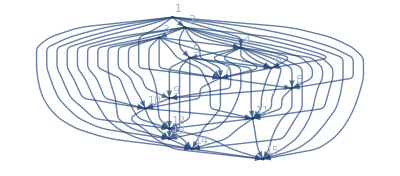

65

```mathematica
n=15;
flow=100;
g= Graph[
Table[i,{i,n}],
Join[
Flatten[
Table[i->j,{i,n-2},{j,RandomSample[Range[i+2,n],RandomInteger[n-i-1]]}]],
Table[i->i+1,{i,1,n-1}]
],
VertexLabels->Table[i->i,{i,n}]
]
val=Sort[EdgeList[g]]; (*care arce sunt in graf*)
m=EdgeCount[g] (*numarul de arce*)

A=IncidenceMatrix[g]; (*matricea de incidenta*)
b=Table[{0,0},n];b⟦1,1⟧=-80;b⟦n,1⟧=80; (*m[rimea fluxului transmis din sursa spre destinatie*)
                                                (* b⟦1,2⟧=-1;b⟦n,2⟧=1;*)
X=Array[x,m];

lu=Table[{0,100},{i,m}];

γ=Table[RandomInteger[{1,5}],m];
δ=Table[RandomInteger[{1,5}],m];
f[j_Integer,x_]:=Piecewise[{{γ⟦j⟧ x, x≤δ⟦j⟧}, {γ⟦j⟧ δ⟦j⟧, x>δ⟦j⟧}, {0, True}}]
fd[j_Integer,x_]:=Piecewise[{{f[j,x]/x, x>0}, {γ⟦j⟧, x==0}, {0, True}}]
```

## Alg P2

```mathematica
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
 min=10000;
solmin={};
perm=Gather[val,First[#1]==First[#2]&]⟦All,All,2⟧; (* Lista de adiacenta --- Are nevoie ca lista de muchii sa fie sortata *)
Do[perm⟦i⟧=RandomSample[perm⟦i⟧],{i,n-1}]; (* Lista randomizata *)
cc=Table[Length[perm⟦i⟧],{i,n-1}]; (* Lista care arata gradul fiecarui nod (cite muchii ies din el) *)
v=Table[{0, Table[Normalize[RandomReal[{0,1},cc⟦i⟧],Total],{i,n-1}]}, {k,4*n}] ; (* Cromozomii initiali *)

(* Lista de coeficienti care vor fi folositi pentru a determina fluxul care va merge pe fiecare muchie *)
pos = SparseArray[MapIndexed[#⟦1⟧*n+#⟦2⟧->#2⟦1⟧&,val]]; (* Creaza un hash map care codeaza muchia cu pozitia ei in lista de muchii ---- Modul de codare este i*n + j pentru muchia i -> j *)
prev=-1000; genEps=0.1; (* variabile ajutatoare pentru conditia de oprire a programului *)

Do[
If[v⟦i⟧⟦1⟧>0,Continue[]];
flux=Table[0,n]; (* Acest tabel retine fluxul care intra in fiecare nod *)
flux⟦1⟧=flow;
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦i,2,j,ii⟧; (* Din nodul j este impins fluxul spre alte noduri *)
v⟦i,1⟧+=f[pos⟦j*n+perm⟦j,ii⟧⟧,flux⟦j⟧*v⟦i,2,j,ii⟧]; (* solutia acestui cromozom este actualizata *)
,{j,n-1},{ii,cc⟦j⟧}]
,{i,4*n}];


(*Print["**********************************************************************************"];
Print["Pasul 1. Initializarea unei matrici a ratelor de flux si a unei populatii intiale:"];
Print[v];*)
counter = 1;

While[Abs[v⟦1⟧⟦1⟧-prev]>genEps,(* Verifica daca ultimele 2 cele mai bune solutii sunt aproape egale *)
prev=v⟦1⟧⟦1⟧;
(*Print[v⟦1⟧⟦1⟧];*)
Print["------------------------------------------------------------------"];
Print["Iteratia ", counter];

counter++;
(*Afisam Populatia si evaluarea functiei populatiei*)
(*Print["Pasul 2. Populatia si evaluarea functiei obiectiv:"];*)

v=Take[v,2*n]; (* Ia jumatatea de solutii care sunt cele mai bune *)
(*Print["Pasul 3. Parintii care vor fi folositi la incrucisare:"];
Print[v];*)
v=Join[v,Flatten[Table[
zz=RandomInteger[{1,n-2}];
{{0,Join[Take[v⟦i,2⟧,zz],Drop[v⟦i+1,2⟧,zz]]},{0,Join[Take[v⟦i+1,2⟧,zz],Drop[v⟦i,2⟧,zz]]}},
{i,1,2*n,2}],1] (* Formeaza copii taind la zz *)
];
(*Print["Pasul 4. Urmasii:"];
Print[Take[v,-2*n]];*)
Do[If[RandomInteger[{1,100}]==1, j=RandomInteger[{1,n-1}];v⟦i,2,j⟧=Normalize[RandomReal[{0,1},cc⟦j⟧],Total]],{i,n+1,2*n}] ;(* Mutatii *)
Do[
If[v⟦i⟧⟦1⟧>0,Continue[]];
flux=Table[0,n]; (* Acest tabel retine fluxul care intra in fiecare nod *)
flux⟦1⟧=flow;
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦i,2,j,ii⟧; (* Din nodul j este impins fluxul spre alte noduri *)
v⟦i,1⟧+=f[pos⟦j*n+perm⟦j,ii⟧⟧,flux⟦j⟧*v⟦i,2,j,ii⟧]; (* solutia acestui cromozom este actualizata *)
,{j,n-1},{ii,cc⟦j⟧}]
,{i,2*n,4*n}];

(*Print["Pasul 5. Populatia noua dupa mutatii:"];
Print[v];
Print[v⟦1⟧⟦1⟧];

Print["Solutiile asociate cromozomilor"];*)
solutii = Table[0,4*n];
Do[
flux=Table[0,n];
flux⟦1⟧=flow;
X=Table[0,m];
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦k,2,j,ii⟧; 
X⟦pos⟦j*n+perm⟦j,ii⟧⟧⟧=flux⟦j⟧*v⟦k,2,j,ii⟧;
,{j,n-1},{ii,cc⟦j⟧}
];
solutii⟦k⟧ = {v⟦k,1⟧, X};
,{k,4*n}];
(*Print[solutii];*)
Print["Parintii si urmasii ",v];
Print["Cel mai bun cromozom ",v[[Ordering[solutii,1]]]];
Print["Cea mai buna solutie ",solutii[[Ordering[solutii,1]]]];
Print["Functia obiectiv totala ",Sum[v⟦i,1⟧,{i,4*n}]];
v=v[[Ordering[solutii]]];
];

(* Gasirea solutiei finale *)
flux=Table[0,n];
flux⟦1⟧=flow;
X=Table[0,m];
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦1,2,j,ii⟧; 
X⟦pos⟦j*n+perm⟦j,ii⟧⟧⟧=flux⟦j⟧*v⟦1,2,j,ii⟧;
,{j,n-1},{ii,cc⟦j⟧}
]
(*{Print[v⟦1,1⟧,X];}
Print["    "]*)
];
Print[thisTimer];
,{bigCount,1,10}]
```

Test 1

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{296.491,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{333.349,{{0.117077,0.051097,0.163322,0.0114299,0.0916038,0.0769731,0.111415,0.0941714,0.0789934,0.203917},{0.141492,0.0104213,0.104029,0.141884,0.151906,0.00584095,0.0880555,0.0829372,0.0661354,0.0417778,0.16552},{0.199996,0.16236,0.103554,0.0839399,0.0146372,0.124715,0.163825,0.146973},{0.0149986,0.149109,0.184148,0.0583633,0.0987382,0.111423,0.172689,0.0346196,0.175912},{0.150331,0.190123,0.135076,0.0405297,0.330515,0.153426},{0.93641,0.0635896},{0.265981,0.332501,0.401518},{0.35542,0.13973,0.50485},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{310.171,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{306.822,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.507089,0.489263,0.00364802},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{298.802,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{316.719,{{0.0538266,0.0107206,0.00839506,0.0426507,0.112868,0.295941,0.0155666,0.131059,0.20897,0.120002},{0.132411,0.11676,0.142258,0.118988,0.0136672,0.145408,0.167895,0.0241553,0.108979,0.00762776,0.0218514},{0.115468,0.10636,0.115963,0.078052,0.137605,0.1999,0.0391041,0.207548},{0.157128,0.143001,0.119146,0.142938,0.055943,0.178359,0.0287939,0.123215,0.0514766},{0.131252,0.195281,0.0981848,0.205537,0.134938,0.234807},{0.448176,0.551824},{0.309255,0.545955,0.14479},{0.316741,0.461353,0.221906},{0.466838,0.533162},{0.37376,0.0888647,0.537375},{0.0938267,0.435849,0.470325},{0.158215,0.0206966,0.821089},{1.},{1.}}},{353.249,{{0.182342,0.171246,0.132855,0.0253554,0.110583,0.0826036,0.0339398,0.0859583,0.0901336,0.084984},{0.0372831,0.0230849,0.0463949,0.048741,0.125373,0.000752409,0.201027,0.00237073,0.225428,0.0500362,0.239509},{0.171385,0.276279,0.118331,0.0624516,0.21167,0.00754053,0.0972258,0.0551174},{0.0884615,0.0700858,0.166106,0.0185428,0.193248,0.0406649,0.192704,0.207845,0.0223422},{0.219643,0.0622564,0.282021,0.257016,0.00105077,0.178012},{0.379309,0.620691},{0.510572,0.0233241,0.466104},{0.0636838,0.328856,0.60746},{0.990235,0.00976488},{0.165174,0.320091,0.514736},{0.619936,0.297011,0.0830529},{0.699193,0.12991,0.170897},{1.},{1.}}},{304.572,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.285258,0.141787,0.572955},{0.216746,0.267144,0.51611},{0.590485,0.409515},{0.533914,0.428577,0.0375085},{0.477723,0.456194,0.0660832},{0.098841,0.681042,0.220117},{1.},{1.}}},{329.186,{{0.0803868,0.143893,0.160577,0.137948,0.0114653,0.122519,0.0532517,0.11133,0.051857,0.126772},{0.11575,0.101719,0.134465,0.0716765,0.0400893,0.150777,0.00852244,0.164962,0.135648,0.0484601,0.0279307},{0.0493514,0.19645,0.0736404,0.134074,0.104515,0.201751,0.0978337,0.142385},{0.0840312,0.0144285,0.159436,0.199835,0.124789,0.0341504,0.184678,0.0612801,0.137372},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{352.088,{{0.101774,0.187125,0.0879662,0.0723054,0.0304146,0.147494,0.0830047,0.137102,0.0978832,0.0549307},{0.0179032,0.0499308,0.101132,0.112545,0.0840472,0.104991,0.0728473,0.0670517,0.137211,0.129925,0.122416},{0.21828,0.181202,0.14225,0.100113,0.0968517,0.0149008,0.135455,0.110947},{0.00614665,0.189788,0.261725,0.0138564,0.00964791,0.102151,0.133934,0.119452,0.163299},{0.188774,0.186659,0.112157,0.167959,0.124234,0.220217},{0.509743,0.490257},{0.618955,0.225374,0.155671},{0.192468,0.798587,0.0089449},{0.526864,0.473136},{0.0658627,0.650186,0.283951},{0.480952,0.395888,0.12316},{0.145709,0.371626,0.482665},{1.},{1.}}},{321.227,{{0.0459725,0.129004,0.119638,0.0489373,0.0971985,0.123484,0.0897384,0.126053,0.128751,0.091223},{0.136327,0.132637,0.00877766,0.0696203,0.199922,0.00939233,0.120068,0.0337298,0.191418,0.0847806,0.0133269},{0.153942,0.150213,0.0267439,0.0455258,0.216117,0.0666556,0.26544,0.0753629},{0.0946886,0.121139,0.138748,0.0385093,0.114972,0.103305,0.116419,0.0945152,0.177703},{0.116389,0.25969,0.159615,0.266398,0.0152077,0.182699},{0.26017,0.73983},{0.0424233,0.465172,0.492405},{0.443025,0.374545,0.18243},{0.795283,0.204717},{0.318284,0.326338,0.355378},{0.371227,0.405023,0.22375},{0.511758,0.243198,0.245045},{1.},{1.}}},{300.725,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{295.255,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{316.741,{{0.0888412,0.134605,0.147713,0.128203,0.0367518,0.0836429,0.0801176,0.079594,0.143598,0.0769341},{0.0262458,0.126581,0.110904,0.0814271,0.0322378,0.110595,0.0877059,0.090264,0.117731,0.0942974,0.12201},{0.0236423,0.102416,0.0405049,0.206472,0.130039,0.218655,0.198186,0.0800852},{0.153504,0.170939,0.161214,0.0158217,0.0921079,0.228717,0.112534,0.0506382,0.0145252},{0.170043,0.259115,0.225736,0.0850519,0.0155334,0.24452},{0.564306,0.435694},{0.440301,0.460075,0.0996237},{0.110798,0.716785,0.172418},{0.825725,0.174275},{0.125029,0.565973,0.308998},{0.367561,0.286719,0.34572},{0.624466,0.0647271,0.310807},{1.},{1.}}},{340.744,{{0.115678,0.0932965,0.153426,0.0634271,0.0555272,0.167601,0.0276135,0.030749,0.156904,0.135778},{0.0445111,0.231244,0.078851,0.0292964,0.0222549,0.21058,0.056553,0.168886,0.0946384,0.0199698,0.0432161},{0.0176093,0.0918406,0.265031,0.0498146,0.0141802,0.119714,0.223538,0.218272},{0.186448,0.144471,0.131753,0.109551,0.259622,0.0689971,0.0225751,0.0374332,0.0391487},{0.23031,0.150251,0.242685,0.177698,0.114769,0.0842865},{0.506727,0.493273},{0.0347622,0.615869,0.349369},{0.451492,0.497016,0.051492},{0.490892,0.509108},{0.131107,0.157359,0.711534},{0.307484,0.3383,0.354216},{0.376646,0.331218,0.292136},{1.},{1.}}},{322.851,{{0.0298304,0.178514,0.140093,0.032844,0.10243,0.124558,0.126262,0.105891,0.0436722,0.115905},{0.168189,0.0384663,0.178139,0.18648,0.150857,0.0264018,0.0398358,0.0937529,0.0114612,0.0492084,0.0572093},{0.188243,0.0805416,0.0996338,0.219199,0.00797328,0.13175,0.0846189,0.188041},{0.071344,0.137366,0.0923152,0.147095,0.140707,0.0844416,0.166673,0.0482967,0.111763},{0.000602192,0.0872035,0.288663,0.144341,0.291148,0.188042},{0.357252,0.642748},{0.409453,0.274124,0.316424},{0.131548,0.273347,0.595104},{0.290187,0.709813},{0.159441,0.731426,0.109133},{0.433815,0.0689139,0.497271},{0.203908,0.021859,0.774233},{1.},{1.}}},{318.18,{{0.135786,0.00272568,0.0879791,0.146906,0.151483,0.0861699,0.12096,0.108847,0.143003,0.0161406},{0.135555,0.176486,0.0635838,0.136667,0.0788665,0.0399099,0.0410255,0.186277,0.0208897,0.0565524,0.0641872},{0.123168,0.220668,0.194703,0.0884759,0.162115,0.0922367,0.0506864,0.0679467},{0.0362256,0.0926024,0.0366466,0.175665,0.128795,0.175429,0.118392,0.184168,0.0520764},{0.0612363,0.227751,0.14754,0.17813,0.156528,0.228815},{0.882458,0.117542},{0.37224,0.28907,0.33869},{0.38087,0.273175,0.345955},{0.417098,0.582902},{0.214072,0.471682,0.314246},{0.338208,0.6199,0.0418921},{0.365561,0.439924,0.194514},{1.},{1.}}},{324.887,{{0.0575456,0.0762899,0.182776,0.0950035,0.0224537,0.0940392,0.0860392,0.185972,0.129668,0.0702127},{0.109251,0.0693957,0.10784,0.0156027,0.0837067,0.105624,0.0473835,0.126529,0.130685,0.0786394,0.125342},{0.0964816,0.170059,0.155474,0.0968167,0.10137,0.211192,0.131873,0.0367345},{0.178784,0.0452508,0.0346894,0.126338,0.12357,0.131372,0.138342,0.121291,0.100364},{0.0952774,0.343764,0.039311,0.0707741,0.179741,0.271133},{0.64682,0.35318},{0.445358,0.147973,0.406669},{0.100552,0.510143,0.389306},{0.211886,0.788114},{0.0696471,0.196152,0.734201},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{319.858,{{0.096695,0.167407,0.0207672,0.121949,0.0709756,0.109098,0.0704016,0.166947,0.158527,0.0172323},{0.0237036,0.133637,0.109544,0.0201205,0.18768,0.0919385,0.0144997,0.194297,0.0993456,0.0558705,0.0693648},{0.148527,0.129215,0.0243116,0.160505,0.120095,0.130574,0.122413,0.16436},{0.0681497,0.0210005,0.0398054,0.0114328,0.282093,0.36175,0.0166656,0.0710593,0.128044},{0.138462,0.192722,0.240479,0.24544,0.0520059,0.130891},{0.229894,0.770106},{0.398333,0.456693,0.144974},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{333.982,{{0.179987,0.177456,0.0735057,0.0958338,0.176895,0.0535397,0.112756,0.0270385,0.000101757,0.102886},{0.113042,0.0415854,0.0630462,0.13511,0.0961044,0.166722,0.0799144,0.133426,0.0825833,0.0421346,0.0463306},{0.11594,0.112407,0.0663859,0.184982,0.116183,0.152971,0.0330908,0.218041},{0.112407,0.214339,0.0334783,0.02223,0.184417,0.0945051,0.0236281,0.0908458,0.22415},{0.155884,0.111319,0.289783,0.173494,0.0622178,0.207303},{0.309381,0.690619},{0.344984,0.132733,0.522283},{0.438412,0.418737,0.142851},{0.17483,0.82517},{0.279725,0.247771,0.472504},{0.445726,0.439689,0.114585},{0.209117,0.274816,0.516067},{1.},{1.}}},{303.69,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.588891,0.411109},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{330.924,{{0.0660665,0.0504339,0.126049,0.0907112,0.136497,0.173463,0.0614161,0.0654479,0.0728647,0.157051},{0.000466472,0.18025,0.0499167,0.0105255,0.144107,0.181791,0.147472,0.0415995,0.0541172,0.134296,0.0554596},{0.0386762,0.00532827,0.187076,0.111518,0.0308058,0.133724,0.269763,0.223108},{0.00474495,0.215494,0.178087,0.0601228,0.165845,0.0953277,0.108104,0.034125,0.13815},{0.1592,0.182494,0.0554543,0.207752,0.0839402,0.31116},{0.406589,0.593411},{0.380854,0.374446,0.2447},{0.247599,0.400688,0.351713},{0.552528,0.447472},{0.0327696,0.14676,0.82047},{0.481182,0.462739,0.0560791},{0.198694,0.381691,0.419615},{1.},{1.}}},{306.963,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{298.716,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{341.626,{{0.230706,0.0094266,0.127725,0.00536486,0.104158,0.0675257,0.0924396,0.142132,0.100171,0.120351},{0.0142391,0.222821,0.0505246,0.0679641,0.0854476,0.0126882,0.104528,0.114786,0.111401,0.167303,0.0482993},{0.0959183,0.242537,0.151246,0.0993558,0.0607387,0.0364486,0.159796,0.153958},{0.0579095,0.134553,0.110778,0.184115,0.184034,0.0727926,0.104526,0.101147,0.0501441},{0.196896,0.231062,0.175299,0.006419,0.172255,0.218069},{0.345235,0.654765},{0.124554,0.446257,0.429189},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{315.265,{{0.097709,0.095204,0.0963004,0.110428,0.101759,0.0717174,0.107257,0.0416038,0.21038,0.0676413},{0.022065,0.139362,0.141976,0.0788405,0.0574316,0.159312,0.157802,0.00782925,0.0951031,0.116796,0.0234832},{0.0199578,0.248808,0.188845,0.252157,0.0138838,0.046157,0.00877767,0.221415},{0.0248894,0.0212717,0.181857,0.158015,0.298794,0.0424208,0.00724046,0.263988,0.0015239},{0.116912,0.219717,0.103975,0.220089,0.186476,0.152831},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{329.497,{{0.117077,0.051097,0.163322,0.0114299,0.0916038,0.0769731,0.111415,0.0941714,0.0789934,0.203917},{0.141492,0.0104213,0.104029,0.141884,0.151906,0.00584095,0.0880555,0.0829372,0.0661354,0.0417778,0.16552},{0.199996,0.16236,0.103554,0.0839399,0.0146372,0.124715,0.163825,0.146973},{0.0149986,0.149109,0.184148,0.0583633,0.0987382,0.111423,0.172689,0.0346196,0.175912},{0.150331,0.190123,0.135076,0.0405297,0.330515,0.153426},{0.93641,0.0635896},{0.265981,0.332501,0.401518},{0.35542,0.13973,0.50485},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{310.171,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{304.513,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.507089,0.489263,0.00364802},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{301.277,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{316.719,{{0.0538266,0.0107206,0.00839506,0.0426507,0.112868,0.295941,0.0155666,0.131059,0.20897,0.120002},{0.132411,0.11676,0.142258,0.118988,0.0136672,0.145408,0.167895,0.0241553,0.108979,0.00762776,0.0218514},{0.115468,0.10636,0.115963,0.078052,0.137605,0.1999,0.0391041,0.207548},{0.157128,0.143001,0.119146,0.142938,0.055943,0.178359,0.0287939,0.123215,0.0514766},{0.131252,0.195281,0.0981848,0.205537,0.134938,0.234807},{0.448176,0.551824},{0.309255,0.545955,0.14479},{0.316741,0.461353,0.221906},{0.466838,0.533162},{0.37376,0.0888647,0.537375},{0.0938267,0.435849,0.470325},{0.158215,0.0206966,0.821089},{1.},{1.}}},{353.249,{{0.182342,0.171246,0.132855,0.0253554,0.110583,0.0826036,0.0339398,0.0859583,0.0901336,0.084984},{0.0372831,0.0230849,0.0463949,0.048741,0.125373,0.000752409,0.201027,0.00237073,0.225428,0.0500362,0.239509},{0.171385,0.276279,0.118331,0.0624516,0.21167,0.00754053,0.0972258,0.0551174},{0.0884615,0.0700858,0.166106,0.0185428,0.193248,0.0406649,0.192704,0.207845,0.0223422},{0.219643,0.0622564,0.282021,0.257016,0.00105077,0.178012},{0.379309,0.620691},{0.510572,0.0233241,0.466104},{0.0636838,0.328856,0.60746},{0.990235,0.00976488},{0.165174,0.320091,0.514736},{0.619936,0.297011,0.0830529},{0.699193,0.12991,0.170897},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{346.699,{{0.0803868,0.143893,0.160577,0.137948,0.0114653,0.122519,0.0532517,0.11133,0.051857,0.126772},{0.11575,0.101719,0.134465,0.0716765,0.0400893,0.150777,0.00852244,0.164962,0.135648,0.0484601,0.0279307},{0.0493514,0.19645,0.0736404,0.134074,0.104515,0.201751,0.0978337,0.142385},{0.0840312,0.0144285,0.159436,0.199835,0.124789,0.0341504,0.184678,0.0612801,0.137372},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.285258,0.141787,0.572955},{0.216746,0.267144,0.51611},{0.590485,0.409515},{0.533914,0.428577,0.0375085},{0.477723,0.456194,0.0660832},{0.098841,0.681042,0.220117},{1.},{1.}}},{359.313,{{0.101774,0.187125,0.0879662,0.0723054,0.0304146,0.147494,0.0830047,0.137102,0.0978832,0.0549307},{0.0179032,0.0499308,0.101132,0.112545,0.0840472,0.104991,0.0728473,0.0670517,0.137211,0.129925,0.122416},{0.21828,0.181202,0.14225,0.100113,0.0968517,0.0149008,0.135455,0.110947},{0.00614665,0.189788,0.261725,0.0138564,0.00964791,0.102151,0.133934,0.119452,0.163299},{0.188774,0.186659,0.112157,0.167959,0.124234,0.220217},{0.509743,0.490257},{0.618955,0.225374,0.155671},{0.443025,0.374545,0.18243},{0.795283,0.204717},{0.318284,0.326338,0.355378},{0.371227,0.405023,0.22375},{0.511758,0.243198,0.245045},{1.},{1.}}},{315.333,{{0.0459725,0.129004,0.119638,0.0489373,0.0971985,0.123484,0.0897384,0.126053,0.128751,0.091223},{0.136327,0.132637,0.00877766,0.0696203,0.199922,0.00939233,0.120068,0.0337298,0.191418,0.0847806,0.0133269},{0.153942,0.150213,0.0267439,0.0455258,0.216117,0.0666556,0.26544,0.0753629},{0.0946886,0.121139,0.138748,0.0385093,0.114972,0.103305,0.116419,0.0945152,0.177703},{0.116389,0.25969,0.159615,0.266398,0.0152077,0.182699},{0.26017,0.73983},{0.0424233,0.465172,0.492405},{0.192468,0.798587,0.0089449},{0.526864,0.473136},{0.0658627,0.650186,0.283951},{0.480952,0.395888,0.12316},{0.145709,0.371626,0.482665},{1.},{1.}}},{291.219,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{318.491,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{319.491,{{0.0888412,0.134605,0.147713,0.128203,0.0367518,0.0836429,0.0801176,0.079594,0.143598,0.0769341},{0.0262458,0.126581,0.110904,0.0814271,0.0322378,0.110595,0.0877059,0.090264,0.117731,0.0942974,0.12201},{0.0236423,0.102416,0.0405049,0.206472,0.130039,0.218655,0.198186,0.0800852},{0.153504,0.170939,0.161214,0.0158217,0.0921079,0.228717,0.112534,0.0506382,0.0145252},{0.170043,0.259115,0.225736,0.0850519,0.0155334,0.24452},{0.564306,0.435694},{0.440301,0.460075,0.0996237},{0.110798,0.716785,0.172418},{0.825725,0.174275},{0.125029,0.565973,0.308998},{0.307484,0.3383,0.354216},{0.376646,0.331218,0.292136},{1.},{1.}}},{338.348,{{0.115678,0.0932965,0.153426,0.0634271,0.0555272,0.167601,0.0276135,0.030749,0.156904,0.135778},{0.0445111,0.231244,0.078851,0.0292964,0.0222549,0.21058,0.056553,0.168886,0.0946384,0.0199698,0.0432161},{0.0176093,0.0918406,0.265031,0.0498146,0.0141802,0.119714,0.223538,0.218272},{0.186448,0.144471,0.131753,0.109551,0.259622,0.0689971,0.0225751,0.0374332,0.0391487},{0.23031,0.150251,0.242685,0.177698,0.114769,0.0842865},{0.506727,0.493273},{0.0347622,0.615869,0.349369},{0.451492,0.497016,0.051492},{0.490892,0.509108},{0.131107,0.157359,0.711534},{0.367561,0.286719,0.34572},{0.624466,0.0647271,0.310807},{1.},{1.}}},{331.062,{{0.0298304,0.178514,0.140093,0.032844,0.10243,0.124558,0.126262,0.105891,0.0436722,0.115905},{0.168189,0.0384663,0.178139,0.18648,0.150857,0.0264018,0.0398358,0.0937529,0.0114612,0.0492084,0.0572093},{0.188243,0.0805416,0.0996338,0.219199,0.00797328,0.13175,0.0846189,0.188041},{0.071344,0.137366,0.0923152,0.147095,0.140707,0.0844416,0.166673,0.0482967,0.111763},{0.000602192,0.0872035,0.288663,0.144341,0.291148,0.188042},{0.357252,0.642748},{0.409453,0.274124,0.316424},{0.131548,0.273347,0.595104},{0.290187,0.709813},{0.214072,0.471682,0.314246},{0.338208,0.6199,0.0418921},{0.365561,0.439924,0.194514},{1.},{1.}}},{310.034,{{0.135786,0.00272568,0.0879791,0.146906,0.151483,0.0861699,0.12096,0.108847,0.143003,0.0161406},{0.135555,0.176486,0.0635838,0.136667,0.0788665,0.0399099,0.0410255,0.186277,0.0208897,0.0565524,0.0641872},{0.123168,0.220668,0.194703,0.0884759,0.162115,0.0922367,0.0506864,0.0679467},{0.0362256,0.0926024,0.0366466,0.175665,0.128795,0.175429,0.118392,0.184168,0.0520764},{0.0612363,0.227751,0.14754,0.17813,0.156528,0.228815},{0.882458,0.117542},{0.37224,0.28907,0.33869},{0.38087,0.273175,0.345955},{0.417098,0.582902},{0.159441,0.731426,0.109133},{0.433815,0.0689139,0.497271},{0.203908,0.021859,0.774233},{1.},{1.}}},{318.584,{{0.0575456,0.0762899,0.182776,0.0950035,0.0224537,0.0940392,0.0860392,0.185972,0.129668,0.0702127},{0.109251,0.0693957,0.10784,0.0156027,0.0837067,0.105624,0.0473835,0.126529,0.130685,0.0786394,0.125342},{0.0964816,0.170059,0.155474,0.0968167,0.10137,0.211192,0.131873,0.0367345},{0.178784,0.0452508,0.0346894,0.126338,0.12357,0.131372,0.138342,0.121291,0.100364},{0.0952774,0.343764,0.039311,0.0707741,0.179741,0.271133},{0.64682,0.35318},{0.445358,0.147973,0.406669},{0.100552,0.510143,0.389306},{0.211886,0.788114},{0.0696471,0.196152,0.734201},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{302.446,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{309.81,{{0.096695,0.167407,0.0207672,0.121949,0.0709756,0.109098,0.0704016,0.166947,0.158527,0.0172323},{0.0237036,0.133637,0.109544,0.0201205,0.18768,0.0919385,0.0144997,0.194297,0.0993456,0.0558705,0.0693648},{0.148527,0.129215,0.0243116,0.160505,0.120095,0.130574,0.122413,0.16436},{0.0681497,0.0210005,0.0398054,0.0114328,0.282093,0.36175,0.0166656,0.0710593,0.128044},{0.138462,0.192722,0.240479,0.24544,0.0520059,0.130891},{0.229894,0.770106},{0.398333,0.456693,0.144974},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{333.982,{{0.179987,0.177456,0.0735057,0.0958338,0.176895,0.0535397,0.112756,0.0270385,0.000101757,0.102886},{0.113042,0.0415854,0.0630462,0.13511,0.0961044,0.166722,0.0799144,0.133426,0.0825833,0.0421346,0.0463306},{0.11594,0.112407,0.0663859,0.184982,0.116183,0.152971,0.0330908,0.218041},{0.112407,0.214339,0.0334783,0.02223,0.184417,0.0945051,0.0236281,0.0908458,0.22415},{0.155884,0.111319,0.289783,0.173494,0.0622178,0.207303},{0.309381,0.690619},{0.344984,0.132733,0.522283},{0.438412,0.418737,0.142851},{0.17483,0.82517},{0.279725,0.247771,0.472504},{0.445726,0.439689,0.114585},{0.209117,0.274816,0.516067},{1.},{1.}}},{303.69,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.588891,0.411109},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{330.924,{{0.0660665,0.0504339,0.126049,0.0907112,0.136497,0.173463,0.0614161,0.0654479,0.0728647,0.157051},{0.000466472,0.18025,0.0499167,0.0105255,0.144107,0.181791,0.147472,0.0415995,0.0541172,0.134296,0.0554596},{0.0386762,0.00532827,0.187076,0.111518,0.0308058,0.133724,0.269763,0.223108},{0.00474495,0.215494,0.178087,0.0601228,0.165845,0.0953277,0.108104,0.034125,0.13815},{0.1592,0.182494,0.0554543,0.207752,0.0839402,0.31116},{0.406589,0.593411},{0.380854,0.374446,0.2447},{0.247599,0.400688,0.351713},{0.552528,0.447472},{0.0327696,0.14676,0.82047},{0.481182,0.462739,0.0560791},{0.198694,0.381691,0.419615},{1.},{1.}}},{306.963,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{305.296,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{336.252,{{0.230706,0.0094266,0.127725,0.00536486,0.104158,0.0675257,0.0924396,0.142132,0.100171,0.120351},{0.0142391,0.222821,0.0505246,0.0679641,0.0854476,0.0126882,0.104528,0.114786,0.111401,0.167303,0.0482993},{0.0959183,0.242537,0.151246,0.0993558,0.0607387,0.0364486,0.159796,0.153958},{0.0579095,0.134553,0.110778,0.184115,0.184034,0.0727926,0.104526,0.101147,0.0501441},{0.196896,0.231062,0.175299,0.006419,0.172255,0.218069},{0.345235,0.654765},{0.124554,0.446257,0.429189},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{297.093,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{314.662,{{0.097709,0.095204,0.0963004,0.110428,0.101759,0.0717174,0.107257,0.0416038,0.21038,0.0676413},{0.022065,0.139362,0.141976,0.0788405,0.0574316,0.159312,0.157802,0.00782925,0.0951031,0.116796,0.0234832},{0.0199578,0.248808,0.188845,0.252157,0.0138838,0.046157,0.00877767,0.221415},{0.0248894,0.0212717,0.181857,0.158015,0.298794,0.0424208,0.00724046,0.263988,0.0015239},{0.116912,0.219717,0.103975,0.220089,0.186476,0.152831},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}}}

Cel mai bun cromozom {{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}}}

Cea mai buna solutie {{277.086,{3.0218,8.52169,9.90757,11.2658,22.2489,5.21245,9.7923,14.5035,14.0938,1.43228,0.181052,0.188053,0.0177237,0.294581,0.12511,0.480444,0.0512062,0.278726,0.591987,0.608579,0.204333,0.0141262,0.0256962,0.018568,0.0218436,0.0257532,0.0229245,0.00873769,0.0434021,1.1986,0.0217165,0.319902,1.18647,0.170685,0.763697,0.735108,2.28888,2.03881,0.213198,0.331926,0.0682959,0.364931,0.20716,0.0308127,4.63445,5.82831,5.78652,2.958,7.95123,3.84313,11.0056,14.8536,0.864268,3.23968,0.1939,3.23907,5.6787,4.87794,3.48367,10.0965,2.04156,9.92285,6.7534,20.5934,58.9424}}}

Functia obiectiv totala 18942.6

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{291.219,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{295.255,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{296.491,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{297.093,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{298.716,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{298.802,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{300.725,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{301.277,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{302.446,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{303.69,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.671456,0.328544},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{303.69,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.588891,0.411109},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{304.513,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.507089,0.489263,0.00364802},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{304.572,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.285258,0.141787,0.572955},{0.216746,0.267144,0.51611},{0.590485,0.409515},{0.533914,0.428577,0.0375085},{0.477723,0.456194,0.0660832},{0.098841,0.681042,0.220117},{1.},{1.}}},{305.296,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{306.822,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.507089,0.489263,0.00364802},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{306.963,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{306.963,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{309.81,{{0.096695,0.167407,0.0207672,0.121949,0.0709756,0.109098,0.0704016,0.166947,0.158527,0.0172323},{0.0237036,0.133637,0.109544,0.0201205,0.18768,0.0919385,0.0144997,0.194297,0.0993456,0.0558705,0.0693648},{0.148527,0.129215,0.0243116,0.160505,0.120095,0.130574,0.122413,0.16436},{0.0681497,0.0210005,0.0398054,0.0114328,0.282093,0.36175,0.0166656,0.0710593,0.128044},{0.138462,0.192722,0.240479,0.24544,0.0520059,0.130891},{0.229894,0.770106},{0.398333,0.456693,0.144974},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{310.034,{{0.135786,0.00272568,0.0879791,0.146906,0.151483,0.0861699,0.12096,0.108847,0.143003,0.0161406},{0.135555,0.176486,0.0635838,0.136667,0.0788665,0.0399099,0.0410255,0.186277,0.0208897,0.0565524,0.0641872},{0.123168,0.220668,0.194703,0.0884759,0.162115,0.0922367,0.0506864,0.0679467},{0.0362256,0.0926024,0.0366466,0.175665,0.128795,0.175429,0.118392,0.184168,0.0520764},{0.0612363,0.227751,0.14754,0.17813,0.156528,0.228815},{0.882458,0.117542},{0.37224,0.28907,0.33869},{0.38087,0.273175,0.345955},{0.417098,0.582902},{0.159441,0.731426,0.109133},{0.433815,0.0689139,0.497271},{0.203908,0.021859,0.774233},{1.},{1.}}},{310.171,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}},{310.171,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}},{314.662,{{0.097709,0.095204,0.0963004,0.110428,0.101759,0.0717174,0.107257,0.0416038,0.21038,0.0676413},{0.022065,0.139362,0.141976,0.0788405,0.0574316,0.159312,0.157802,0.00782925,0.0951031,0.116796,0.0234832},{0.0199578,0.248808,0.188845,0.252157,0.0138838,0.046157,0.00877767,0.221415},{0.0248894,0.0212717,0.181857,0.158015,0.298794,0.0424208,0.00724046,0.263988,0.0015239},{0.116912,0.219717,0.103975,0.220089,0.186476,0.152831},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{300.154,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{290.606,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{297.093,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{312.699,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{276.837,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{299.514,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{302.755,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{298.135,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{302.046,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{327.959,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.588891,0.411109},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{303.69,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.588891,0.411109},{0.259293,0.349786,0.390921},{0.155607,0.414165,0.430228},{0.365814,0.634186},{0.448212,0.466235,0.0855526},{0.170279,0.222907,0.606814},{0.268781,0.337811,0.393408},{1.},{1.}}},{304.513,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.507089,0.489263,0.00364802},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{313.711,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.285258,0.141787,0.572955},{0.216746,0.267144,0.51611},{0.590485,0.409515},{0.533914,0.428577,0.0375085},{0.477723,0.456194,0.0660832},{0.098841,0.681042,0.220117},{1.},{1.}}},{304.256,{{0.0244555,0.0550857,0.123565,0.0833383,0.107586,0.151945,0.058679,0.127253,0.171286,0.0968071},{0.0393314,0.0717019,0.057036,0.14567,0.123435,0.138746,0.0153402,0.036177,0.06623,0.153546,0.152787},{0.311987,0.316864,0.205333,0.0607714,0.00795094,0.0233399,0.0171338,0.0566199},{0.0158732,0.08763,0.0102764,0.00620862,0.188941,0.0764979,0.239726,0.207432,0.167414},{0.135026,0.0498277,0.217281,0.191611,0.140117,0.266137},{0.818648,0.181352},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{307.254,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.507089,0.489263,0.00364802},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{305.69,{{0.106985,0.0865136,0.0389608,0.159547,0.133951,0.149964,0.0215596,0.129769,0.168128,0.00462154},{0.0895342,0.172552,0.125651,0.168242,0.096396,0.0163614,0.222753,0.0161834,0.0185999,0.0358718,0.0378548},{0.0322247,0.147319,0.193808,0.172232,0.0658025,0.0658861,0.21381,0.108918},{0.0681497,0.0210005,0.0398054,0.0114328,0.282093,0.36175,0.0166656,0.0710593,0.128044},{0.138462,0.192722,0.240479,0.24544,0.0520059,0.130891},{0.229894,0.770106},{0.398333,0.456693,0.144974},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{307.274,{{0.096695,0.167407,0.0207672,0.121949,0.0709756,0.109098,0.0704016,0.166947,0.158527,0.0172323},{0.0237036,0.133637,0.109544,0.0201205,0.18768,0.0919385,0.0144997,0.194297,0.0993456,0.0558705,0.0693648},{0.148527,0.129215,0.0243116,0.160505,0.120095,0.130574,0.122413,0.16436},{0.156016,0.162788,0.0382846,0.171516,0.144508,0.0662278,0.106458,0.0258726,0.128328},{0.301783,0.354917,0.0693261,0.0882997,0.00118237,0.184492},{0.574034,0.425966},{0.187029,0.345793,0.467178},{0.477924,0.488183,0.033893},{0.828649,0.171351},{0.497499,0.165504,0.336997},{0.0204744,0.134028,0.845498},{0.0201035,0.475481,0.504415},{1.},{1.}}},{313.835,{{0.135786,0.00272568,0.0879791,0.146906,0.151483,0.0861699,0.12096,0.108847,0.143003,0.0161406},{0.135555,0.176486,0.0635838,0.136667,0.0788665,0.0399099,0.0410255,0.186277,0.0208897,0.0565524,0.0641872},{0.123168,0.220668,0.194703,0.0884759,0.162115,0.0922367,0.0506864,0.0679467},{0.0362256,0.0926024,0.0366466,0.175665,0.128795,0.175429,0.118392,0.184168,0.0520764},{0.0612363,0.227751,0.14754,0.17813,0.156528,0.228815},{0.882458,0.117542},{0.37224,0.28907,0.33869},{0.38087,0.273175,0.345955},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}},{305.15,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.417098,0.582902},{0.159441,0.731426,0.109133},{0.433815,0.0689139,0.497271},{0.203908,0.021859,0.774233},{1.},{1.}}},{293.236,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{335.857,{{0.097709,0.095204,0.0963004,0.110428,0.101759,0.0717174,0.107257,0.0416038,0.21038,0.0676413},{0.022065,0.139362,0.141976,0.0788405,0.0574316,0.159312,0.157802,0.00782925,0.0951031,0.116796,0.0234832},{0.0199578,0.248808,0.188845,0.252157,0.0138838,0.046157,0.00877767,0.221415},{0.0248894,0.0212717,0.181857,0.158015,0.298794,0.0424208,0.00724046,0.263988,0.0015239},{0.116912,0.219717,0.103975,0.220089,0.186476,0.152831},{0.456326,0.543674},{0.243305,0.50629,0.250404},{0.367784,0.20709,0.425126},{0.270543,0.729457},{0.294797,0.218616,0.486588},{0.121268,0.293507,0.585224},{0.415485,0.218087,0.366428},{1.},{1.}}}}

Cel mai bun cromozom {{276.837,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}}}

Cea mai buna solutie {{276.837,{10.2775,1.03593,5.24354,3.61799,13.7928,18.4044,7.27352,5.27533,16.9649,18.1141,0.749409,0.996215,1.35602,0.100695,0.647529,0.34268,1.7292,0.298294,1.23764,1.68724,1.13253,0.0964707,0.105406,0.0602223,0.00847934,0.127745,0.130849,0.0863347,0.133902,0.0213831,0.127607,0.263206,0.375693,0.507765,0.541721,0.2234,0.0248439,0.0430015,0.125876,0.345243,0.266332,0.289522,0.0295883,0.320845,2.16205,3.54107,4.72127,1.1816,1.19336,3.49242,9.35892,6.38114,0.295038,3.97996,13.9801,1.2769,6.48089,9.96006,7.33663,10.8438,10.2421,3.8636,8.46144,17.4724,48.543}}}

Functia obiectiv totala 18037.6

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{276.837,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{290.606,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.219,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{293.236,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{295.255,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{296.491,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{297.093,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{297.093,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{298.135,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{298.716,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{298.802,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{299.514,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{300.154,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{300.725,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{275.997,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{264.308,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.367884,0.249868,0.382248},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.12228,0.616822,0.260898},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{283.542,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{299.75,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{296.559,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{304.011,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{307.67,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{281.201,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{295.467,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{299.335,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.510105,0.377971,0.111924},{0.381377,0.103714,0.514909},{0.0653048,0.808693,0.126002},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{298.302,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.0661969,0.112899,0.189066,0.280411,0.31226,0.039168},{0.556476,0.443524},{0.324267,0.316875,0.358858},{0.445505,0.305832,0.248663},{0.483875,0.516125},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.332,{{0.0319253,0.0777445,0.150795,0.138009,0.0986598,0.107556,0.145967,0.119783,0.0273187,0.102241},{0.110366,0.12735,0.0841096,0.127605,0.0332886,0.0686427,0.0222951,0.118208,0.128255,0.0748674,0.105012},{0.154462,0.211758,0.0893584,0.227,0.111562,0.137157,0.011422,0.05728},{0.0186689,0.148183,0.140634,0.0820457,0.0953419,0.125299,0.109567,0.131944,0.148317},{0.108787,0.09836,0.131655,0.23418,0.227271,0.199746},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.250767,0.0517747,0.697459},{0.279622,0.1572,0.563178},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{298.674,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.345087,0.654913},{0.479594,0.252278,0.268128},{0.330446,0.336235,0.333319},{0.514675,0.418429,0.066896},{1.},{1.}}},{315.232,{{0.0490903,0.0494795,0.0357567,0.221405,0.0759116,0.115291,0.192064,0.052387,0.146756,0.0618593},{0.117019,0.246729,0.219125,0.100277,0.0230709,0.0789338,0.0099885,0.0256991,0.0796215,0.0741046,0.0254317},{0.113624,0.213069,0.156678,0.144201,0.0417994,0.0788187,0.185984,0.0658254},{0.196645,0.0302856,0.0247183,0.187808,0.0170559,0.199653,0.10471,0.177793,0.0613308},{0.149949,0.316091,0.28406,0.0524791,0.128142,0.069279},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.495124,0.504876},{0.0751172,0.495411,0.429472},{0.631239,0.321938,0.046823},{0.273114,0.256531,0.470356},{1.},{1.}}},{289.298,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{291.767,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{312.968,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.559074,0.310925,0.130002},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}},{300.725,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.559074,0.310925,0.130002},{0.292645,0.707355},{0.13677,0.722168,0.141062},{0.295685,0.618751,0.0855639},{0.295382,0.246317,0.458301},{1.},{1.}}},{300.859,{{0.0616068,0.0577415,0.0897019,0.164983,0.142817,0.0878152,0.0604568,0.161301,0.17103,0.00254669},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.13197,0.0532679,0.0907873,0.172795,0.155605,0.186267,0.197252,0.0120551},{0.181421,0.0646543,0.106912,0.156608,0.0614743,0.0695656,0.0334981,0.156438,0.169429},{0.175751,0.13307,0.111956,0.329212,0.143058,0.106953},{0.435518,0.564482},{0.23399,0.310452,0.455558},{0.395348,0.345916,0.258736},{0.511796,0.488204},{0.182631,0.332862,0.484506},{0.591258,0.186428,0.222314},{0.441722,0.481124,0.0771535},{1.},{1.}}}}

Cel mai bun cromozom {{264.308,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}}}

Cea mai buna solutie {{264.308,{3.0218,8.52169,9.90757,11.2658,22.2489,5.21245,9.7923,14.5035,14.0938,1.43228,0.220342,0.292909,0.3987,0.0296065,0.190387,0.100755,0.508423,0.0877048,0.363893,0.496086,0.332989,0.0283644,0.0309917,0.0177066,0.00249311,0.0375596,0.0384724,0.0253842,0.0393701,0.0888322,0.530121,1.09344,1.56075,2.10942,2.25048,0.928076,0.103209,0.178642,0.0445538,0.122198,0.0942681,0.102476,0.0104728,0.113563,3.99678,6.54606,11.1017,2.77846,2.80611,6.35784,17.0376,11.6167,0.591044,7.97298,5.87038,0.536182,2.72138,11.3024,8.32543,12.3053,13.3738,5.04497,11.0487,29.4944,60.364}}}

Functia obiectiv totala 17584.8

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{264.308,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{275.997,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{276.837,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{281.201,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.295,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.542,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.367884,0.249868,0.382248},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{289.298,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{290.606,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.219,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{291.767,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{293.236,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{295.255,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{295.467,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{296.491,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{273.404,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{270.932,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{276.837,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{277.086,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{279.023,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.789406,0.210594},{0.0212804,0.355486,0.623234},{0.264271,0.546995,0.188734},{0.10907,0.530129,0.360801},{1.},{1.}}},{296.157,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.144879,0.039548,0.0513595,0.092588,0.105061,0.0126886,0.118581,0.11144,0.0186952,0.151897,0.153263},{0.0399056,0.06694,0.00417324,0.350838,0.132018,0.201534,0.152634,0.0519573},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{277.591,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.156799,0.168504,0.0757915,0.170948,0.0959228,0.0823787,0.011595,0.145749,0.0923119},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{273.884,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.144623,0.661073,0.194304},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{288.753,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.367884,0.249868,0.382248},{1.},{1.}}},{283.568,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.158993,0.0414025,0.00586528,0.201396,0.195906,0.0974855,0.0922386,0.0169456,0.0622322,0.0676197,0.0599153},{0.102556,0.120649,0.239722,0.126619,0.141928,0.0780233,0.142243,0.0482608},{0.233705,0.0875411,0.0366697,0.00248932,0.137393,0.0842639,0.136003,0.0195653,0.26237},{0.175281,0.300028,0.272893,0.0561494,0.170316,0.0253326},{0.557053,0.442947},{0.346587,0.476243,0.177171},{0.37053,0.129388,0.500082},{0.207167,0.792833},{0.210509,0.409691,0.3798},{0.317221,0.275577,0.407202},{0.12228,0.616822,0.260898},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.367884,0.249868,0.382248},{1.},{1.}}},{283.571,{{0.048715,0.207216,0.00292284,0.0627718,0.0227349,0.112234,0.114839,0.161771,0.152921,0.113874},{0.122588,0.180446,0.00727341,0.127297,0.158514,0.100984,0.00278352,0.0283868,0.152152,0.111031,0.00854458},{0.0384761,0.190886,0.135743,0.166946,0.0531557,0.187627,0.0839154,0.143251},{0.00383923,0.092336,0.136061,0.225383,0.0873935,0.246445,0.121888,0.0247122,0.0619415},{0.161501,0.174679,0.185198,0.159977,0.179445,0.139201},{0.371684,0.628316},{0.89805,0.05656,0.0453905},{0.182679,0.79041,0.0269115},{0.677415,0.322585},{0.0363557,0.137185,0.826459},{0.256773,0.398,0.345227},{0.12228,0.616822,0.260898},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{285.938,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{286.981,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.108654,0.247409,0.200615,0.147797,0.223643,0.0718822},{0.26212,0.73788},{0.505012,0.00681,0.488178},{0.425963,0.232133,0.341904},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{277.542,{{0.0103593,0.0524354,0.181141,0.0527533,0.0727352,0.102775,0.0361799,0.184044,0.169649,0.137928},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{294.97,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.353723,0.231257,0.41502},{0.34442,0.620844,0.0347355},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}},{286.098,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{296.555,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{291.274,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.509253,0.490747},{0.591242,0.121766,0.286992},{0.00521014,0.44128,0.55351},{0.375993,0.033608,0.590399},{1.},{1.}}},{291.767,{{0.118598,0.0580334,0.106882,0.0386587,0.15511,0.0282173,0.187803,0.149469,0.00634542,0.150883},{0.043632,0.0465385,0.0969064,0.107974,0.123961,0.103963,0.118638,0.0743499,0.098259,0.094169,0.0916094},{0.192083,0.0318278,0.203194,0.110066,0.0776949,0.167241,0.003317,0.214577},{0.144629,0.134564,0.166375,0.133247,0.0659682,0.125706,0.0321975,0.101635,0.095679},{0.0408843,0.0914437,0.284892,0.195662,0.0939854,0.293132},{0.139161,0.860839},{0.274606,0.612828,0.112566},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{292.861,{{0.0878321,0.00427184,0.129168,0.174787,0.1279,0.0989941,0.124299,0.16495,0.00874936,0.0790481},{0.149184,0.111882,0.033726,0.120923,0.0486019,0.144022,0.150756,0.0195792,0.079268,0.102747,0.0393105},{0.123143,0.0594949,0.166213,0.104878,0.186472,0.134516,0.150613,0.0746707},{0.0306072,0.0867584,0.158179,0.0603666,0.131148,0.134975,0.0555038,0.290055,0.052407},{0.0579511,0.190495,0.260442,0.150814,0.131549,0.208749},{0.139061,0.860939},{0.66532,0.168169,0.166511},{0.182332,0.284059,0.533609},{0.848675,0.151325},{0.64507,0.310308,0.0446223},{0.335967,0.520854,0.14318},{0.459551,0.5123,0.0281487},{1.},{1.}}},{293.236,{{0.160859,0.013951,0.0756593,0.187145,0.0372855,0.0486597,0.125809,0.116917,0.088232,0.145483},{0.106061,0.141271,0.15178,0.06343,0.101245,0.0354137,0.120444,0.121037,0.0389415,0.0433066,0.0770696},{0.0946586,0.0674685,0.238321,0.00165598,0.0818021,0.120231,0.354259,0.0416036},{0.0391565,0.0771528,0.186417,0.0299587,0.0596799,0.17958,0.180478,0.1488,0.0987774},{0.122456,0.0556137,0.217794,0.131636,0.129534,0.342966},{0.359256,0.640744},{0.416306,0.557273,0.0264211},{0.224446,0.412164,0.36339},{0.720251,0.279749},{0.266036,0.255462,0.478502},{0.559901,0.108296,0.331803},{0.430104,0.0734395,0.496456},{1.},{1.}}},{295.255,{{0.141638,0.155676,0.00552698,0.124698,0.132374,0.138949,0.0672132,0.0190027,0.00257471,0.212348},{0.158097,0.0926725,0.0738843,0.095582,0.0459406,0.00309466,0.059192,0.105489,0.0518185,0.139692,0.174538},{0.0441005,0.0938231,0.0526756,0.242875,0.210303,0.131308,0.0855799,0.139334},{0.100484,0.164595,0.126748,0.00326067,0.0902806,0.158749,0.172598,0.181376,0.00190916},{0.115735,0.3573,0.0232345,0.0467565,0.233899,0.223074},{0.976368,0.0236317},{0.166587,0.156954,0.676459},{0.135199,0.343667,0.521134},{0.979911,0.0200886},{0.349432,0.13594,0.514628},{0.0545804,0.188861,0.756558},{0.0643238,0.894522,0.0411539},{1.},{1.}}},{295.467,{{0.0684655,0.173393,0.126014,0.176096,0.0421843,0.0890688,0.00095556,0.030043,0.157626,0.136154},{0.0983929,0.17901,0.130259,0.0369861,0.0998596,0.120993,0.0120165,0.143372,0.0461009,0.0999614,0.0330483},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.317041,0.682959},{0.353723,0.231257,0.41502},{0.158701,0.32959,0.511709},{0.559321,0.440679},{0.395617,0.343095,0.261288},{0.494112,0.132473,0.373415},{0.720215,0.251048,0.0287364},{1.},{1.}}},{296.491,{{0.046986,0.130999,0.0383132,0.00680965,0.131523,0.0745841,0.136169,0.186512,0.103812,0.144292},{0.127323,0.0764755,0.126318,0.0361695,0.0302117,0.132128,0.143327,0.0271479,0.149934,0.14986,0.00110475},{0.172038,0.0648486,0.0174873,0.176435,0.137135,0.139762,0.143935,0.148358},{0.0380558,0.0777088,0.176299,0.0810502,0.129518,0.00905381,0.140446,0.147379,0.200488},{0.1154,0.043658,0.0473457,0.189271,0.600896,0.00342952},{0.621389,0.378611},{0.464719,0.173402,0.36188},{0.474187,0.0213505,0.504463},{0.842765,0.157235},{0.335646,0.512294,0.15206},{0.453821,0.304639,0.24154},{0.717362,0.17867,0.103969},{1.},{1.}}}}

Cel mai bun cromozom {{264.308,{{0.0852169,0.0990757,0.0143228,0.145035,0.097923,0.030218,0.112658,0.0521245,0.140938,0.222489},{0.0333429,0.0630047,0.131941,0.164169,0.120423,0.00979766,0.0290241,0.168252,0.096932,0.110196,0.0729177},{0.0803597,0.0113147,0.178677,0.174603,0.140652,0.128729,0.17046,0.115204},{0.0202016,0.254494,0.123651,0.0599484,0.0100455,0.104951,0.176496,0.238542,0.0116713},{0.0913864,0.210193,0.250647,0.193358,0.0214812,0.232934},{0.620901,0.379099},{0.66532,0.168169,0.166511},{0.48662,0.18159,0.33179},{0.930985,0.0690147},{0.643122,0.0587408,0.298137},{0.35394,0.385346,0.260714},{0.453849,0.171205,0.374946},{1.},{1.}}}}

Cea mai buna solutie {{264.308,{3.0218,8.52169,9.90757,11.2658,22.2489,5.21245,9.7923,14.5035,14.0938,1.43228,0.220342,0.292909,0.3987,0.0296065,0.190387,0.100755,0.508423,0.0877048,0.363893,0.496086,0.332989,0.0283644,0.0309917,0.0177066,0.00249311,0.0375596,0.0384724,0.0253842,0.0393701,0.0888322,0.530121,1.09344,1.56075,2.10942,2.25048,0.928076,0.103209,0.178642,0.0445538,0.122198,0.0942681,0.102476,0.0104728,0.113563,3.99678,6.54606,11.1017,2.77846,2.80611,6.35784,17.0376,11.6167,0.591044,7.97298,5.87038,0.536182,2.72138,11.3024,8.32543,12.3053,13.3738,5.04497,11.0487,29.4944,60.364}}}

Functia obiectiv totala 17152.5

{0.59375,Null}

Test 2

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{276.501,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.326473,0.0865383,0.586989},{1.},{1.}}},{348.921,{{0.130969,0.145657,0.0886354,0.0639724,0.0449412,0.0368612,0.160389,0.233329,0.00680788,0.0884376},{0.103097,0.148255,0.0432134,0.183068,0.0930794,0.0163235,0.0822844,0.00266804,0.183008,0.0193016,0.125702},{0.170096,0.165277,0.167346,0.162611,0.0166457,0.128424,0.0963353,0.0932635},{0.190947,0.202745,0.023532,0.0199079,0.207031,0.0486578,0.0297546,0.189152,0.0882719},{0.0841913,0.0544366,0.268774,0.447144,0.0871072,0.058347},{0.439899,0.560101},{0.103371,0.299846,0.596783},{0.0658185,0.453611,0.48057},{0.63763,0.36237},{0.191361,0.344923,0.463716},{0.408392,0.245816,0.345792},{0.571813,0.306635,0.121552},{1.},{1.}}},{337.631,{{0.094166,0.0150517,0.131073,0.0964811,0.145932,0.0635926,0.134057,0.00529711,0.109426,0.204923},{0.0548731,0.0734137,0.123071,0.115553,0.133236,0.13843,0.0465543,0.139282,0.0499216,0.0981365,0.0275296},{0.162132,0.134197,0.110587,0.138579,0.160883,0.0541814,0.131023,0.108418},{0.104639,0.177928,0.0104535,0.0712775,0.223631,0.145238,0.0181502,0.034202,0.214482},{0.203871,0.12163,0.241223,0.151511,0.16312,0.118645},{0.411368,0.588632},{0.487115,0.326518,0.186368},{0.230524,0.481897,0.287579},{0.409105,0.590895},{0.403421,0.369745,0.226834},{0.314653,0.0758346,0.609512},{0.302389,0.471254,0.226356},{1.},{1.}}},{313.617,{{0.0183276,0.212652,0.0380898,0.0532502,0.00699672,0.166185,0.180207,0.0835446,0.0428538,0.197894},{0.174218,0.0207518,0.0338835,0.0801701,0.0365923,0.193417,0.164285,0.133283,0.0880547,0.0597905,0.015554},{0.0283988,0.164627,0.104393,0.0407929,0.233609,0.0204024,0.159052,0.248724},{0.14708,0.187777,0.0930852,0.0495211,0.183064,0.113477,0.167996,0.0204232,0.0375757},{0.0473727,0.20376,0.206214,0.197914,0.171877,0.172862},{0.485482,0.514518},{0.177145,0.20262,0.620235},{0.344177,0.601563,0.0542595},{0.424617,0.575383},{0.316995,0.365173,0.317831},{0.766419,0.0722693,0.161311},{0.327299,0.367394,0.305307},{1.},{1.}}},{331.116,{{0.103121,0.0951717,0.133929,0.111181,0.101516,0.0978838,0.0628134,0.056722,0.115852,0.12181},{0.0067202,0.108924,0.070843,0.186658,0.0101125,0.1978,0.071703,0.0231991,0.143701,0.147823,0.0325161},{0.114799,0.17299,0.112631,0.0320835,0.133775,0.156208,0.0855716,0.191941},{0.102698,0.122332,0.139206,0.0931765,0.0510081,0.0946918,0.160456,0.127071,0.109361},{0.230541,0.0554051,0.316777,0.194462,0.190972,0.0118427},{0.0929557,0.907044},{0.390231,0.214772,0.394997},{0.275329,0.330248,0.394423},{0.424433,0.575567},{0.76126,0.146134,0.0926065},{0.479881,0.0594135,0.460705},{0.15527,0.341561,0.503168},{1.},{1.}}},{317.875,{{0.0948055,0.00615185,0.119174,0.0678923,0.139155,0.0412535,0.164389,0.0812963,0.153772,0.132111},{0.108689,0.149621,0.144308,0.0449768,0.0958107,0.0239503,0.0701948,0.0309597,0.14236,0.134369,0.0547604},{0.157351,0.131407,0.244241,0.0282583,0.0787195,0.0351096,0.152672,0.172241},{0.0234132,0.0949434,0.152881,0.234649,0.0631859,0.251551,0.0287657,0.0366859,0.113925},{0.174074,0.14825,0.144417,0.168002,0.161562,0.203696},{0.684669,0.315331},{0.297631,0.340497,0.361872},{0.331755,0.0836763,0.584568},{0.539908,0.460092},{0.110842,0.00221184,0.886947},{0.508554,0.273779,0.217668},{0.362406,0.191939,0.445655},{1.},{1.}}},{284.689,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.529392,0.470608},{0.625472,0.0943874,0.280141},{0.415596,0.0964133,0.487991},{0.0596062,0.940394},{0.438675,0.238724,0.3226},{0.308812,0.424719,0.266469},{0.165532,0.128434,0.706034},{1.},{1.}}},{355.955,{{0.198649,0.0104855,0.0636577,0.1081,0.0457726,0.0485298,0.251229,0.11805,0.0829307,0.0725958},{0.107379,0.145386,0.0510881,0.0526993,0.0124744,0.131014,0.0643053,0.108615,0.124985,0.0514473,0.150606},{0.0156919,0.24429,0.140556,0.237763,0.180955,0.026007,0.0394285,0.115308},{0.0258968,0.160464,0.0832171,0.148143,0.0874129,0.12399,0.204888,0.117,0.0489874},{0.0714598,0.256552,0.035314,0.247518,0.198047,0.191109},{0.881848,0.118152},{0.0403957,0.541162,0.418442},{0.248753,0.540244,0.211003},{0.487051,0.512949},{0.784002,0.0347204,0.181277},{0.51927,0.352226,0.128504},{0.215555,0.345651,0.438794},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{305.724,{{0.0473513,0.13245,0.146606,0.138768,0.015121,0.143056,0.0462939,0.0884344,0.145594,0.0963253},{0.0155401,0.0479272,0.0986135,0.137501,0.166874,0.0110443,0.113206,0.102756,0.0457251,0.143146,0.117668},{0.127366,0.261612,0.259944,0.0516725,0.0351526,0.214462,0.041667,0.00812447},{0.0762242,0.00704166,0.216081,0.196878,0.0631093,0.0487867,0.110237,0.175398,0.106245},{0.231682,0.108865,0.322322,0.103522,0.0328503,0.200759},{0.673421,0.326579},{0.572823,0.379655,0.0475218},{0.149629,0.259583,0.590788},{0.0738247,0.926175},{0.515014,0.428367,0.0566188},{0.261569,0.514643,0.223788},{0.142945,0.518487,0.338568},{1.},{1.}}},{286.937,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.000323541,0.0470223,0.218687,0.106547,0.0721053,0.26822,0.100144,0.186951},{0.120132,0.130863,0.0159954,0.137605,0.15714,0.134504,0.0355137,0.145027,0.123219},{0.036427,0.24223,0.245015,0.0825116,0.231595,0.162221},{0.33444,0.66556},{0.429505,0.244189,0.326306},{0.233374,0.262067,0.504559},{0.356727,0.643273},{0.0674609,0.0775694,0.85497},{0.0585833,0.702654,0.238763},{0.620902,0.308,0.0710977},{1.},{1.}}},{299.426,{{0.0408445,0.160337,0.1052,0.132929,0.118733,0.0839229,0.0678789,0.172165,0.0140806,0.103908},{0.035533,0.00435684,0.00287522,0.209027,0.105715,0.0839195,0.192603,0.153239,0.0659819,0.0858074,0.0609415},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.300061,0.699939},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{300.77,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.109781,0.0100907,0.148929,0.111727,0.00562546,0.141926,0.147192,0.159087,0.165642},{0.151125,0.0693138,0.095447,0.267524,0.227373,0.189217},{0.527141,0.472859},{0.188774,0.187179,0.624046},{0.274701,0.269798,0.455501},{0.0176181,0.982382},{0.787207,0.120728,0.0920652},{0.325558,0.171337,0.503104},{0.100435,0.651391,0.248174},{1.},{1.}}},{292.272,{{0.100436,0.0256101,0.181777,0.202683,0.205294,0.00464335,0.0646518,0.033741,0.112156,0.0690074},{0.137896,0.157472,0.112178,0.0236732,0.0809877,0.133213,0.127417,0.0511236,0.0589502,0.106467,0.010622},{0.0187862,0.0173918,0.0484796,0.130145,0.145845,0.130319,0.270165,0.238868},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{292.971,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.531226,0.0446798,0.424095},{0.582281,0.130141,0.287578},{0.365254,0.152863,0.481883},{1.},{1.}}},{325.024,{{0.197804,0.249842,0.0662412,0.117212,0.0253677,0.00505861,0.0457124,0.175331,0.0330343,0.0843973},{0.0742248,0.0569222,0.152723,0.150587,0.118252,0.0892708,0.0661837,0.0624849,0.0994772,0.116728,0.0131458},{0.154665,0.156931,0.026232,0.114319,0.103915,0.233734,0.0566919,0.153513},{0.19679,0.141209,0.0634636,0.164724,0.03727,0.14358,0.00530037,0.0860607,0.161602},{0.0489333,0.216657,0.309587,0.181396,0.145206,0.0982199},{0.887914,0.112086},{0.00229474,0.706381,0.291324},{0.211672,0.405725,0.382603},{0.573788,0.426212},{0.348481,0.612913,0.0386063},{0.608038,0.0619128,0.330049},{0.338502,0.188339,0.473159},{1.},{1.}}},{336.636,{{0.103934,0.0732893,0.142765,0.131039,0.039478,0.0996862,0.0981265,0.112707,0.103772,0.0952029},{0.155795,0.111941,0.0469342,0.0460391,0.133427,0.0720845,0.0657442,0.0210428,0.168392,0.167069,0.0115309},{0.0130996,0.0708137,0.136007,0.0296413,0.130789,0.159389,0.23451,0.225751},{0.142772,0.094361,0.122998,0.115125,0.023639,0.18422,0.0756089,0.127106,0.11417},{0.0230118,0.185475,0.224608,0.158075,0.260962,0.147868},{0.753889,0.246111},{0.350914,0.253934,0.395152},{0.231814,0.0484245,0.719761},{0.759137,0.240863},{0.436269,0.460868,0.102863},{0.116488,0.370291,0.513221},{0.0611837,0.289479,0.649337},{1.},{1.}}},{330.432,{{0.107215,0.0665458,0.220115,0.209712,0.0299185,0.0158892,0.0258606,0.107349,0.0807957,0.136599},{0.00377708,0.183748,0.0460449,0.205503,0.113576,0.0702272,0.0492616,0.0186348,0.172666,0.0819794,0.0545823},{0.157164,0.209656,0.0255112,0.0863728,0.140206,0.129795,0.131826,0.11947},{0.183008,0.0539867,0.197932,0.0255578,0.130239,0.0656962,0.0362683,0.0539335,0.253378},{0.271475,0.0868417,0.23248,0.319955,0.0232836,0.0659651},{0.534419,0.465581},{0.124221,0.435995,0.439784},{0.60614,0.220121,0.173739},{0.322734,0.677266},{0.688766,0.0219772,0.289257},{0.0447461,0.408762,0.546492},{0.0636663,0.374208,0.562125},{1.},{1.}}},{300.231,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.10702,0.253838,0.134665,0.0583834,0.108167,0.337926},{0.213023,0.786977},{0.0838873,0.425366,0.490747},{0.424247,0.400015,0.175738},{0.85412,0.14588},{0.574212,0.379951,0.0458374},{0.318421,0.475182,0.206396},{0.368295,0.405343,0.226362},{1.},{1.}}},{331.573,{{0.141617,0.165952,0.0602291,0.0537634,0.0710312,0.094571,0.159329,0.0463927,0.162217,0.0448974},{0.119608,0.00998096,0.0759575,0.0197998,0.0851359,0.137868,0.154266,0.096697,0.0653869,0.101737,0.133564},{0.00959234,0.133785,0.221668,0.153014,0.0158775,0.054596,0.230761,0.180706},{0.154783,0.0327856,0.10363,0.0901141,0.137396,0.067295,0.206027,0.0508201,0.157149},{0.27748,0.148905,0.204185,0.155875,0.0773297,0.136226},{0.485338,0.514662},{0.207666,0.258799,0.533535},{0.0992464,0.640529,0.260224},{0.622127,0.377873},{0.33432,0.198341,0.46734},{0.517894,0.259773,0.222334},{0.0686932,0.385641,0.545665},{1.},{1.}}},{313.507,{{0.0428165,0.092887,0.143328,0.135067,0.115807,0.159616,0.138491,0.0292388,0.0419864,0.100763},{0.138203,0.0100976,0.0951899,0.124343,0.083898,0.10715,0.0982366,0.134836,0.139763,0.0283769,0.0399063},{0.167199,0.153161,0.0994374,0.146845,0.0312494,0.249733,0.0944694,0.0579055},{0.113253,0.105546,0.201451,0.00399177,0.0718361,0.148661,0.0726282,0.155642,0.126991},{0.143164,0.160071,0.2349,0.219327,0.106922,0.135617},{0.82393,0.17607},{0.329777,0.314279,0.355944},{0.5199,0.464377,0.0157233},{0.306634,0.693366},{0.479206,0.106135,0.41466},{0.134702,0.428367,0.43693},{0.642903,0.120309,0.236788},{1.},{1.}}},{278.29,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.225479,0.774521},{0.416441,0.338073,0.245485},{0.613281,0.269774,0.116944},{0.589454,0.0553538,0.355192},{1.},{1.}}},{338.783,{{0.0556726,0.00909284,0.0681452,0.106541,0.215314,0.0890355,0.0238286,0.105687,0.140926,0.185757},{0.0526601,0.131305,0.0249923,0.107063,0.0604503,0.142742,0.11534,0.0907505,0.00017112,0.141574,0.132952},{0.116211,0.0800036,0.197734,0.0715866,0.158406,0.0947008,0.158251,0.123108},{0.0118641,0.0775308,0.194145,0.0249656,0.0590828,0.224509,0.172331,0.190632,0.0449399},{0.212918,0.139017,0.174799,0.105902,0.134093,0.23327},{0.245827,0.754173},{0.420312,0.344595,0.235093},{0.42743,0.322034,0.250535},{0.129682,0.870318},{0.294208,0.241068,0.464724},{0.106578,0.549479,0.343944},{0.423198,0.0995824,0.477219},{1.},{1.}}},{292.199,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.24554,0.467113,0.287348},{0.388634,0.329638,0.281728},{0.157297,0.618,0.224702},{1.},{1.}}},{269.44,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{286.515,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{335.667,{{0.129421,0.086938,0.153612,0.00701434,0.0977625,0.167282,0.148651,0.0620592,0.00231901,0.144941},{0.0297074,0.128247,0.0481134,0.0137113,0.113231,0.0560372,0.047868,0.154253,0.158051,0.0676177,0.183164},{0.0423764,0.263998,0.07019,0.11562,0.242428,0.0472797,0.0259285,0.192179},{0.150007,0.11354,0.161258,0.0481676,0.138309,0.128293,0.0732175,0.185171,0.00203553},{0.0813813,0.255439,0.088416,0.0601329,0.152214,0.362417},{0.630745,0.369255},{0.150574,0.34173,0.507696},{0.513155,0.0614646,0.42538},{0.507677,0.492323},{0.247694,0.218932,0.533374},{0.355773,0.123727,0.520499},{0.318649,0.184461,0.496891},{1.},{1.}}},{299.221,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.348717,0.574545,0.0767388},{0.246078,0.753922},{0.268853,0.375787,0.35536},{0.334091,0.659118,0.00679051},{0.440848,0.173571,0.385581},{1.},{1.}}},{294.958,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}},{254.938,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{277.617,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.571813,0.306635,0.121552},{1.},{1.}}},{348.677,{{0.130969,0.145657,0.0886354,0.0639724,0.0449412,0.0368612,0.160389,0.233329,0.00680788,0.0884376},{0.103097,0.148255,0.0432134,0.183068,0.0930794,0.0163235,0.0822844,0.00266804,0.183008,0.0193016,0.125702},{0.170096,0.165277,0.167346,0.162611,0.0166457,0.128424,0.0963353,0.0932635},{0.190947,0.202745,0.023532,0.0199079,0.207031,0.0486578,0.0297546,0.189152,0.0882719},{0.0841913,0.0544366,0.268774,0.447144,0.0871072,0.058347},{0.439899,0.560101},{0.103371,0.299846,0.596783},{0.0658185,0.453611,0.48057},{0.63763,0.36237},{0.191361,0.344923,0.463716},{0.408392,0.245816,0.345792},{0.326473,0.0865383,0.586989},{1.},{1.}}},{335.638,{{0.094166,0.0150517,0.131073,0.0964811,0.145932,0.0635926,0.134057,0.00529711,0.109426,0.204923},{0.0548731,0.0734137,0.123071,0.115553,0.133236,0.13843,0.0465543,0.139282,0.0499216,0.0981365,0.0275296},{0.162132,0.134197,0.110587,0.138579,0.160883,0.0541814,0.131023,0.108418},{0.104639,0.177928,0.0104535,0.0712775,0.223631,0.145238,0.0181502,0.034202,0.214482},{0.203871,0.12163,0.241223,0.151511,0.16312,0.118645},{0.411368,0.588632},{0.487115,0.326518,0.186368},{0.230524,0.481897,0.287579},{0.409105,0.590895},{0.403421,0.369745,0.226834},{0.766419,0.0722693,0.161311},{0.327299,0.367394,0.305307},{1.},{1.}}},{315.719,{{0.0183276,0.212652,0.0380898,0.0532502,0.00699672,0.166185,0.180207,0.0835446,0.0428538,0.197894},{0.174218,0.0207518,0.0338835,0.0801701,0.0365923,0.193417,0.164285,0.133283,0.0880547,0.0597905,0.015554},{0.0283988,0.164627,0.104393,0.0407929,0.233609,0.0204024,0.159052,0.248724},{0.14708,0.187777,0.0930852,0.0495211,0.183064,0.113477,0.167996,0.0204232,0.0375757},{0.0473727,0.20376,0.206214,0.197914,0.171877,0.172862},{0.485482,0.514518},{0.177145,0.20262,0.620235},{0.344177,0.601563,0.0542595},{0.424617,0.575383},{0.316995,0.365173,0.317831},{0.314653,0.0758346,0.609512},{0.302389,0.471254,0.226356},{1.},{1.}}},{323.365,{{0.103121,0.0951717,0.133929,0.111181,0.101516,0.0978838,0.0628134,0.056722,0.115852,0.12181},{0.0067202,0.108924,0.070843,0.186658,0.0101125,0.1978,0.071703,0.0231991,0.143701,0.147823,0.0325161},{0.114799,0.17299,0.112631,0.0320835,0.133775,0.156208,0.0855716,0.191941},{0.102698,0.122332,0.139206,0.0931765,0.0510081,0.0946918,0.160456,0.127071,0.109361},{0.230541,0.0554051,0.316777,0.194462,0.190972,0.0118427},{0.0929557,0.907044},{0.390231,0.214772,0.394997},{0.331755,0.0836763,0.584568},{0.539908,0.460092},{0.110842,0.00221184,0.886947},{0.508554,0.273779,0.217668},{0.362406,0.191939,0.445655},{1.},{1.}}},{324.269,{{0.0948055,0.00615185,0.119174,0.0678923,0.139155,0.0412535,0.164389,0.0812963,0.153772,0.132111},{0.108689,0.149621,0.144308,0.0449768,0.0958107,0.0239503,0.0701948,0.0309597,0.14236,0.134369,0.0547604},{0.157351,0.131407,0.244241,0.0282583,0.0787195,0.0351096,0.152672,0.172241},{0.0234132,0.0949434,0.152881,0.234649,0.0631859,0.251551,0.0287657,0.0366859,0.113925},{0.174074,0.14825,0.144417,0.168002,0.161562,0.203696},{0.684669,0.315331},{0.297631,0.340497,0.361872},{0.275329,0.330248,0.394423},{0.424433,0.575567},{0.76126,0.146134,0.0926065},{0.479881,0.0594135,0.460705},{0.15527,0.341561,0.503168},{1.},{1.}}},{281.596,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.881848,0.118152},{0.0403957,0.541162,0.418442},{0.248753,0.540244,0.211003},{0.487051,0.512949},{0.784002,0.0347204,0.181277},{0.51927,0.352226,0.128504},{0.215555,0.345651,0.438794},{1.},{1.}}},{361.608,{{0.198649,0.0104855,0.0636577,0.1081,0.0457726,0.0485298,0.251229,0.11805,0.0829307,0.0725958},{0.107379,0.145386,0.0510881,0.0526993,0.0124744,0.131014,0.0643053,0.108615,0.124985,0.0514473,0.150606},{0.0156919,0.24429,0.140556,0.237763,0.180955,0.026007,0.0394285,0.115308},{0.0258968,0.160464,0.0832171,0.148143,0.0874129,0.12399,0.204888,0.117,0.0489874},{0.0714598,0.256552,0.035314,0.247518,0.198047,0.191109},{0.529392,0.470608},{0.625472,0.0943874,0.280141},{0.415596,0.0964133,0.487991},{0.0596062,0.940394},{0.438675,0.238724,0.3226},{0.308812,0.424719,0.266469},{0.165532,0.128434,0.706034},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{305.724,{{0.0473513,0.13245,0.146606,0.138768,0.015121,0.143056,0.0462939,0.0884344,0.145594,0.0963253},{0.0155401,0.0479272,0.0986135,0.137501,0.166874,0.0110443,0.113206,0.102756,0.0457251,0.143146,0.117668},{0.127366,0.261612,0.259944,0.0516725,0.0351526,0.214462,0.041667,0.00812447},{0.0762242,0.00704166,0.216081,0.196878,0.0631093,0.0487867,0.110237,0.175398,0.106245},{0.231682,0.108865,0.322322,0.103522,0.0328503,0.200759},{0.673421,0.326579},{0.572823,0.379655,0.0475218},{0.149629,0.259583,0.590788},{0.0738247,0.926175},{0.515014,0.428367,0.0566188},{0.261569,0.514643,0.223788},{0.142945,0.518487,0.338568},{1.},{1.}}},{280.886,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.300061,0.699939},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{306.477,{{0.0408445,0.160337,0.1052,0.132929,0.118733,0.0839229,0.0678789,0.172165,0.0140806,0.103908},{0.035533,0.00435684,0.00287522,0.209027,0.105715,0.0839195,0.192603,0.153239,0.0659819,0.0858074,0.0609415},{0.000323541,0.0470223,0.218687,0.106547,0.0721053,0.26822,0.100144,0.186951},{0.120132,0.130863,0.0159954,0.137605,0.15714,0.134504,0.0355137,0.145027,0.123219},{0.036427,0.24223,0.245015,0.0825116,0.231595,0.162221},{0.33444,0.66556},{0.429505,0.244189,0.326306},{0.233374,0.262067,0.504559},{0.356727,0.643273},{0.0674609,0.0775694,0.85497},{0.0585833,0.702654,0.238763},{0.620902,0.308,0.0710977},{1.},{1.}}},{289.85,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{315.512,{{0.100436,0.0256101,0.181777,0.202683,0.205294,0.00464335,0.0646518,0.033741,0.112156,0.0690074},{0.137896,0.157472,0.112178,0.0236732,0.0809877,0.133213,0.127417,0.0511236,0.0589502,0.106467,0.010622},{0.0187862,0.0173918,0.0484796,0.130145,0.145845,0.130319,0.270165,0.238868},{0.109781,0.0100907,0.148929,0.111727,0.00562546,0.141926,0.147192,0.159087,0.165642},{0.151125,0.0693138,0.095447,0.267524,0.227373,0.189217},{0.527141,0.472859},{0.188774,0.187179,0.624046},{0.274701,0.269798,0.455501},{0.0176181,0.982382},{0.787207,0.120728,0.0920652},{0.325558,0.171337,0.503104},{0.100435,0.651391,0.248174},{1.},{1.}}},{289.593,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.348481,0.612913,0.0386063},{0.608038,0.0619128,0.330049},{0.338502,0.188339,0.473159},{1.},{1.}}},{330.,{{0.197804,0.249842,0.0662412,0.117212,0.0253677,0.00505861,0.0457124,0.175331,0.0330343,0.0843973},{0.0742248,0.0569222,0.152723,0.150587,0.118252,0.0892708,0.0661837,0.0624849,0.0994772,0.116728,0.0131458},{0.154665,0.156931,0.026232,0.114319,0.103915,0.233734,0.0566919,0.153513},{0.19679,0.141209,0.0634636,0.164724,0.03727,0.14358,0.00530037,0.0860607,0.161602},{0.0489333,0.216657,0.309587,0.181396,0.145206,0.0982199},{0.887914,0.112086},{0.00229474,0.706381,0.291324},{0.211672,0.405725,0.382603},{0.573788,0.426212},{0.531226,0.0446798,0.424095},{0.582281,0.130141,0.287578},{0.365254,0.152863,0.481883},{1.},{1.}}},{336.636,{{0.103934,0.0732893,0.142765,0.131039,0.039478,0.0996862,0.0981265,0.112707,0.103772,0.0952029},{0.155795,0.111941,0.0469342,0.0460391,0.133427,0.0720845,0.0657442,0.0210428,0.168392,0.167069,0.0115309},{0.0130996,0.0708137,0.136007,0.0296413,0.130789,0.159389,0.23451,0.225751},{0.142772,0.094361,0.122998,0.115125,0.023639,0.18422,0.0756089,0.127106,0.11417},{0.0230118,0.185475,0.224608,0.158075,0.260962,0.147868},{0.753889,0.246111},{0.350914,0.253934,0.395152},{0.231814,0.0484245,0.719761},{0.759137,0.240863},{0.436269,0.460868,0.102863},{0.116488,0.370291,0.513221},{0.0611837,0.289479,0.649337},{1.},{1.}}},{330.432,{{0.107215,0.0665458,0.220115,0.209712,0.0299185,0.0158892,0.0258606,0.107349,0.0807957,0.136599},{0.00377708,0.183748,0.0460449,0.205503,0.113576,0.0702272,0.0492616,0.0186348,0.172666,0.0819794,0.0545823},{0.157164,0.209656,0.0255112,0.0863728,0.140206,0.129795,0.131826,0.11947},{0.183008,0.0539867,0.197932,0.0255578,0.130239,0.0656962,0.0362683,0.0539335,0.253378},{0.271475,0.0868417,0.23248,0.319955,0.0232836,0.0659651},{0.534419,0.465581},{0.124221,0.435995,0.439784},{0.60614,0.220121,0.173739},{0.322734,0.677266},{0.688766,0.0219772,0.289257},{0.0447461,0.408762,0.546492},{0.0636663,0.374208,0.562125},{1.},{1.}}},{302.275,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.27748,0.148905,0.204185,0.155875,0.0773297,0.136226},{0.485338,0.514662},{0.207666,0.258799,0.533535},{0.0992464,0.640529,0.260224},{0.622127,0.377873},{0.33432,0.198341,0.46734},{0.517894,0.259773,0.222334},{0.0686932,0.385641,0.545665},{1.},{1.}}},{328.248,{{0.141617,0.165952,0.0602291,0.0537634,0.0710312,0.094571,0.159329,0.0463927,0.162217,0.0448974},{0.119608,0.00998096,0.0759575,0.0197998,0.0851359,0.137868,0.154266,0.096697,0.0653869,0.101737,0.133564},{0.00959234,0.133785,0.221668,0.153014,0.0158775,0.054596,0.230761,0.180706},{0.154783,0.0327856,0.10363,0.0901141,0.137396,0.067295,0.206027,0.0508201,0.157149},{0.10702,0.253838,0.134665,0.0583834,0.108167,0.337926},{0.213023,0.786977},{0.0838873,0.425366,0.490747},{0.424247,0.400015,0.175738},{0.85412,0.14588},{0.574212,0.379951,0.0458374},{0.318421,0.475182,0.206396},{0.368295,0.405343,0.226362},{1.},{1.}}},{306.745,{{0.0428165,0.092887,0.143328,0.135067,0.115807,0.159616,0.138491,0.0292388,0.0419864,0.100763},{0.138203,0.0100976,0.0951899,0.124343,0.083898,0.10715,0.0982366,0.134836,0.139763,0.0283769,0.0399063},{0.167199,0.153161,0.0994374,0.146845,0.0312494,0.249733,0.0944694,0.0579055},{0.113253,0.105546,0.201451,0.00399177,0.0718361,0.148661,0.0726282,0.155642,0.126991},{0.143164,0.160071,0.2349,0.219327,0.106922,0.135617},{0.82393,0.17607},{0.329777,0.314279,0.355944},{0.5199,0.464377,0.0157233},{0.225479,0.774521},{0.416441,0.338073,0.245485},{0.613281,0.269774,0.116944},{0.589454,0.0553538,0.355192},{1.},{1.}}},{286.266,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.306634,0.693366},{0.479206,0.106135,0.41466},{0.134702,0.428367,0.43693},{0.642903,0.120309,0.236788},{1.},{1.}}},{338.783,{{0.0556726,0.00909284,0.0681452,0.106541,0.215314,0.0890355,0.0238286,0.105687,0.140926,0.185757},{0.0526601,0.131305,0.0249923,0.107063,0.0604503,0.142742,0.11534,0.0907505,0.00017112,0.141574,0.132952},{0.116211,0.0800036,0.197734,0.0715866,0.158406,0.0947008,0.158251,0.123108},{0.0118641,0.0775308,0.194145,0.0249656,0.0590828,0.224509,0.172331,0.190632,0.0449399},{0.212918,0.139017,0.174799,0.105902,0.134093,0.23327},{0.245827,0.754173},{0.420312,0.344595,0.235093},{0.42743,0.322034,0.250535},{0.129682,0.870318},{0.24554,0.467113,0.287348},{0.388634,0.329638,0.281728},{0.157297,0.618,0.224702},{1.},{1.}}},{294.48,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.294208,0.241068,0.464724},{0.106578,0.549479,0.343944},{0.423198,0.0995824,0.477219},{1.},{1.}}},{266.042,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{290.04,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{330.747,{{0.129421,0.086938,0.153612,0.00701434,0.0977625,0.167282,0.148651,0.0620592,0.00231901,0.144941},{0.0297074,0.128247,0.0481134,0.0137113,0.113231,0.0560372,0.047868,0.154253,0.158051,0.0676177,0.183164},{0.0423764,0.263998,0.07019,0.11562,0.242428,0.0472797,0.0259285,0.192179},{0.150007,0.11354,0.161258,0.0481676,0.138309,0.128293,0.0732175,0.185171,0.00203553},{0.0813813,0.255439,0.088416,0.0601329,0.152214,0.362417},{0.630745,0.369255},{0.150574,0.34173,0.507696},{0.348717,0.574545,0.0767388},{0.246078,0.753922},{0.268853,0.375787,0.35536},{0.334091,0.659118,0.00679051},{0.440848,0.173571,0.385581},{1.},{1.}}},{304.557,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.513155,0.0614646,0.42538},{0.507677,0.492323},{0.247694,0.218932,0.533374},{0.355773,0.123727,0.520499},{0.318649,0.184461,0.496891},{1.},{1.}}},{285.412,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{257.014,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}}}

Cel mai bun cromozom {{254.938,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}}}

Cea mai buna solutie {{254.938,{13.325,0.282793,1.61961,2.7383,10.3927,8.93278,13.152,17.4521,15.8463,16.2583,1.32024,0.123135,0.741961,1.92331,2.26268,1.93353,1.66568,1.68667,0.327612,1.33407,0.00614196,0.374777,0.018353,0.198476,0.0643495,0.0575434,0.112469,0.105878,0.388391,0.115976,0.0687156,0.012995,0.0474199,0.00214724,0.0048174,0.176749,0.173805,0.17808,0.280601,0.11766,0.0514063,0.0639526,0.204804,0.139513,3.44265,0.467948,1.76302,0.261309,6.74842,5.0585,3.44281,5.63536,2.69695,2.47945,0.567299,7.22733,5.81963,0.661286,2.75662,2.92806,7.51004,8.0392,1.38184,32.8941,67.7926}}}

Functia obiectiv totala 18431.7

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{254.938,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{257.014,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}},{266.042,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{269.44,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{276.501,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.326473,0.0865383,0.586989},{1.},{1.}}},{277.617,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.571813,0.306635,0.121552},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{278.29,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.225479,0.774521},{0.416441,0.338073,0.245485},{0.613281,0.269774,0.116944},{0.589454,0.0553538,0.355192},{1.},{1.}}},{280.886,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.300061,0.699939},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{281.596,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.881848,0.118152},{0.0403957,0.541162,0.418442},{0.248753,0.540244,0.211003},{0.487051,0.512949},{0.784002,0.0347204,0.181277},{0.51927,0.352226,0.128504},{0.215555,0.345651,0.438794},{1.},{1.}}},{284.689,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.529392,0.470608},{0.625472,0.0943874,0.280141},{0.415596,0.0964133,0.487991},{0.0596062,0.940394},{0.438675,0.238724,0.3226},{0.308812,0.424719,0.266469},{0.165532,0.128434,0.706034},{1.},{1.}}},{285.412,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{286.266,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.306634,0.693366},{0.479206,0.106135,0.41466},{0.134702,0.428367,0.43693},{0.642903,0.120309,0.236788},{1.},{1.}}},{286.515,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{286.937,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.000323541,0.0470223,0.218687,0.106547,0.0721053,0.26822,0.100144,0.186951},{0.120132,0.130863,0.0159954,0.137605,0.15714,0.134504,0.0355137,0.145027,0.123219},{0.036427,0.24223,0.245015,0.0825116,0.231595,0.162221},{0.33444,0.66556},{0.429505,0.244189,0.326306},{0.233374,0.262067,0.504559},{0.356727,0.643273},{0.0674609,0.0775694,0.85497},{0.0585833,0.702654,0.238763},{0.620902,0.308,0.0710977},{1.},{1.}}},{289.593,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.348481,0.612913,0.0386063},{0.608038,0.0619128,0.330049},{0.338502,0.188339,0.473159},{1.},{1.}}},{289.85,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{290.04,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{292.199,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.24554,0.467113,0.287348},{0.388634,0.329638,0.281728},{0.157297,0.618,0.224702},{1.},{1.}}},{292.272,{{0.100436,0.0256101,0.181777,0.202683,0.205294,0.00464335,0.0646518,0.033741,0.112156,0.0690074},{0.137896,0.157472,0.112178,0.0236732,0.0809877,0.133213,0.127417,0.0511236,0.0589502,0.106467,0.010622},{0.0187862,0.0173918,0.0484796,0.130145,0.145845,0.130319,0.270165,0.238868},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{292.971,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.531226,0.0446798,0.424095},{0.582281,0.130141,0.287578},{0.365254,0.152863,0.481883},{1.},{1.}}},{294.48,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.294208,0.241068,0.464724},{0.106578,0.549479,0.343944},{0.423198,0.0995824,0.477219},{1.},{1.}}},{294.958,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}},{299.221,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.348717,0.574545,0.0767388},{0.246078,0.753922},{0.268853,0.375787,0.35536},{0.334091,0.659118,0.00679051},{0.440848,0.173571,0.385581},{1.},{1.}}},{299.426,{{0.0408445,0.160337,0.1052,0.132929,0.118733,0.0839229,0.0678789,0.172165,0.0140806,0.103908},{0.035533,0.00435684,0.00287522,0.209027,0.105715,0.0839195,0.192603,0.153239,0.0659819,0.0858074,0.0609415},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.300061,0.699939},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{300.231,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.10702,0.253838,0.134665,0.0583834,0.108167,0.337926},{0.213023,0.786977},{0.0838873,0.425366,0.490747},{0.424247,0.400015,0.175738},{0.85412,0.14588},{0.574212,0.379951,0.0458374},{0.318421,0.475182,0.206396},{0.368295,0.405343,0.226362},{1.},{1.}}},{300.77,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.109781,0.0100907,0.148929,0.111727,0.00562546,0.141926,0.147192,0.159087,0.165642},{0.151125,0.0693138,0.095447,0.267524,0.227373,0.189217},{0.527141,0.472859},{0.188774,0.187179,0.624046},{0.274701,0.269798,0.455501},{0.0176181,0.982382},{0.787207,0.120728,0.0920652},{0.325558,0.171337,0.503104},{0.100435,0.651391,0.248174},{1.},{1.}}},{302.275,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.27748,0.148905,0.204185,0.155875,0.0773297,0.136226},{0.485338,0.514662},{0.207666,0.258799,0.533535},{0.0992464,0.640529,0.260224},{0.622127,0.377873},{0.33432,0.198341,0.46734},{0.517894,0.259773,0.222334},{0.0686932,0.385641,0.545665},{1.},{1.}}},{304.557,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.513155,0.0614646,0.42538},{0.507677,0.492323},{0.247694,0.218932,0.533374},{0.355773,0.123727,0.520499},{0.318649,0.184461,0.496891},{1.},{1.}}},{254.938,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{257.014,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}},{269.44,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{266.042,{{0.0146284,0.133173,0.112566,0.0130547,0.155614,0.106792,0.178092,0.181568,0.0460169,0.0584946},{0.0239591,0.0355728,0.0843338,0.167733,0.0748871,0.0669279,0.0787257,0.107197,0.061859,0.158073,0.140732},{0.157928,0.159077,0.16176,0.0771201,0.126152,0.159654,0.118036,0.0402734},{0.14167,0.0437215,0.104819,0.0227637,0.234976,0.136449,0.0537316,0.0592496,0.20262},{0.0302169,0.26834,0.293862,0.150832,0.245172,0.0115778},{0.633597,0.366403},{0.237041,0.411489,0.351471},{0.184193,0.401375,0.414432},{0.433009,0.566991},{0.241956,0.442947,0.315097},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{277.617,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.571813,0.306635,0.121552},{1.},{1.}}},{276.501,{{0.000817842,0.0861744,0.161615,0.137544,0.0978628,0.148247,0.0141743,0.107987,0.112722,0.132855},{0.0408927,0.0164809,0.157906,0.0115094,0.189618,0.119009,0.0418682,0.0406765,0.168101,0.031102,0.182836},{0.188109,0.0317939,0.231608,0.242836,0.193779,0.0375225,0.0268174,0.0475328},{0.0873387,0.151018,0.0675574,0.127724,0.0380482,0.148163,0.154031,0.11602,0.1101},{0.223038,0.176184,0.0306059,0.190531,0.125024,0.254618},{0.114203,0.885797},{0.356648,0.311029,0.332323},{0.211868,0.563595,0.224536},{0.597857,0.402143},{0.73784,0.0834002,0.17876},{0.382929,0.329069,0.288002},{0.326473,0.0865383,0.586989},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{277.844,{{0.197504,0.179376,0.12016,0.000158719,0.152281,0.0853499,0.0422225,0.137046,0.083917,0.00198445},{0.100768,0.123159,0.0460738,0.0448008,0.139007,0.100854,0.0394421,0.0956894,0.092148,0.118087,0.0999707},{0.232412,0.0538171,0.151943,0.140317,0.0903701,0.030871,0.0737352,0.226535},{0.0472054,0.179116,0.190502,0.0789002,0.0502542,0.136084,0.0955385,0.0216494,0.20075},{0.134601,0.14124,0.132739,0.0765307,0.245692,0.269197},{0.803988,0.196012},{0.703238,0.139837,0.156925},{0.413208,0.0605992,0.526193},{0.304847,0.695153},{0.394808,0.346553,0.25864},{0.559162,0.191602,0.249236},{0.315085,0.342722,0.342192},{1.},{1.}}},{274.497,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.225479,0.774521},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{284.885,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.300061,0.699939},{0.416441,0.338073,0.245485},{0.613281,0.269774,0.116944},{0.589454,0.0553538,0.355192},{1.},{1.}}},{288.317,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.881848,0.118152},{0.0403957,0.541162,0.418442},{0.248753,0.540244,0.211003},{0.487051,0.512949},{0.438675,0.238724,0.3226},{0.308812,0.424719,0.266469},{0.165532,0.128434,0.706034},{1.},{1.}}},{281.984,{{0.0659001,0.0436211,0.00860087,0.148325,0.135795,0.163402,0.155724,0.135886,0.0927833,0.0499618},{0.0772079,0.0336673,0.0266641,0.084473,0.0462926,0.0884168,0.073862,0.0519222,0.179992,0.173594,0.163908},{0.0591845,0.158168,0.0477136,0.0422715,0.205482,0.169418,0.105911,0.211852},{0.164921,0.160812,0.0685733,0.0993273,0.044404,0.0226211,0.101136,0.180276,0.15793},{0.24821,0.181634,0.00676767,0.392945,0.0769635,0.0934798},{0.529392,0.470608},{0.625472,0.0943874,0.280141},{0.415596,0.0964133,0.487991},{0.0596062,0.940394},{0.784002,0.0347204,0.181277},{0.51927,0.352226,0.128504},{0.215555,0.345651,0.438794},{1.},{1.}}},{299.919,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.0432345,0.137975,0.0732929,0.122774,0.191356,0.0809776,0.189492,0.160898},{0.00752374,0.115341,0.148336,0.0436097,0.0266758,0.210834,0.0879347,0.218312,0.141433},{0.459881,0.0873231,0.0912121,0.106606,0.0532651,0.201712},{0.978306,0.0216937},{0.74714,0.108444,0.144416},{0.12396,0.370657,0.505383},{0.306634,0.693366},{0.479206,0.106135,0.41466},{0.134702,0.428367,0.43693},{0.642903,0.120309,0.236788},{1.},{1.}}},{273.862,{{0.031673,0.15989,0.146168,0.158946,0.0878208,0.131121,0.122158,0.0774096,0.0224265,0.0623871},{0.0485357,0.0802316,0.0592398,0.113446,0.0232512,0.12065,0.0927902,0.0536882,0.159123,0.122873,0.126171},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}},{291.865,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.120132,0.130863,0.0159954,0.137605,0.15714,0.134504,0.0355137,0.145027,0.123219},{0.036427,0.24223,0.245015,0.0825116,0.231595,0.162221},{0.33444,0.66556},{0.429505,0.244189,0.326306},{0.233374,0.262067,0.504559},{0.356727,0.643273},{0.0674609,0.0775694,0.85497},{0.0585833,0.702654,0.238763},{0.620902,0.308,0.0710977},{1.},{1.}}},{284.553,{{0.0555341,0.198059,0.073733,0.227071,0.146325,0.103667,0.0741487,0.091673,0.0193189,0.0104698},{0.160131,0.179999,0.130595,0.1341,0.00800532,0.00277985,0.122864,0.0268677,0.0417882,0.0479824,0.144887},{0.000323541,0.0470223,0.218687,0.106547,0.0721053,0.26822,0.100144,0.186951},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.702298,0.0125388,0.285163},{0.491928,0.469629,0.0384431},{1.},{1.}}},{303.311,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{274.216,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.348481,0.612913,0.0386063},{0.608038,0.0619128,0.330049},{0.338502,0.188339,0.473159},{1.},{1.}}},{291.992,{{0.0580981,0.0126129,0.116212,0.133117,0.0833937,0.17877,0.136388,0.181626,0.0848785,0.0149046},{0.00693184,0.062725,0.110177,0.231526,0.1215,0.0433381,0.0380401,0.0461298,0.127395,0.18572,0.0265165},{0.0469821,0.108097,0.197117,0.0655963,0.0451857,0.229382,0.138886,0.168754},{0.132916,0.0361865,0.140523,0.0803108,0.135595,0.149315,0.121203,0.117006,0.0869449},{0.302877,0.0379801,0.250805,0.0557954,0.105461,0.247082},{0.224192,0.775808},{0.623777,0.224524,0.151699},{0.36065,0.296939,0.342411},{0.513919,0.486081},{0.465252,0.357616,0.177132},{0.388634,0.329638,0.281728},{0.157297,0.618,0.224702},{1.},{1.}}},{292.092,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.24554,0.467113,0.287348},{0.118851,0.480731,0.400418},{0.454053,0.0539827,0.491964},{1.},{1.}}},{282.021,{{0.100436,0.0256101,0.181777,0.202683,0.205294,0.00464335,0.0646518,0.033741,0.112156,0.0690074},{0.137896,0.157472,0.112178,0.0236732,0.0809877,0.133213,0.127417,0.0511236,0.0589502,0.106467,0.010622},{0.0187862,0.0173918,0.0484796,0.130145,0.145845,0.130319,0.270165,0.238868},{0.131378,0.0265062,0.118142,0.143454,0.0347321,0.186094,0.185379,0.141223,0.0330922},{0.0263373,0.221832,0.140673,0.244659,0.169517,0.196982},{0.0231846,0.976815},{0.564287,0.267166,0.168547},{0.445169,0.536646,0.018185},{0.616396,0.383604},{0.531226,0.0446798,0.424095},{0.582281,0.130141,0.287578},{0.365254,0.152863,0.481883},{1.},{1.}}},{303.311,{{0.106161,0.152486,0.0106522,0.0456084,0.0614357,0.0613371,0.12745,0.168655,0.174298,0.091917},{0.0809444,0.120397,0.115161,0.0796843,0.151966,0.102891,0.0313094,0.0473528,0.0528649,0.150034,0.067394},{0.0380668,0.204302,0.0380278,0.192185,0.247328,0.0969206,0.0831152,0.100054},{0.1057,0.145373,0.116509,0.195612,0.00246735,0.114547,0.130462,0.130983,0.0583467},{0.131555,0.222437,0.13985,0.118783,0.180039,0.207336},{0.046624,0.953376},{0.348597,0.406595,0.244808},{0.163727,0.451794,0.384479},{0.248572,0.751428},{0.18995,0.360721,0.449329},{0.784779,0.0771758,0.138045},{0.425319,0.20921,0.365471},{1.},{1.}}},{294.48,{{0.0569198,0.0480513,0.180374,0.133633,0.22689,0.0132956,0.00900123,0.105806,0.138508,0.0875207},{0.142836,0.00203381,0.0890689,0.105092,0.0868832,0.103555,0.0744569,0.0943918,0.142504,0.0390812,0.120099},{0.16738,0.171896,0.0441043,0.150256,0.0831209,0.133417,0.0645533,0.185274},{0.0726423,0.120656,0.0526807,0.136172,0.044119,0.105193,0.166277,0.162898,0.139362},{0.272898,0.376713,0.217445,0.0763598,0.00398088,0.0526029},{0.413097,0.586903},{0.377958,0.278357,0.343685},{0.51362,0.160216,0.326164},{0.493693,0.506307},{0.294208,0.241068,0.464724},{0.348431,0.389987,0.261581},{0.454345,0.08682,0.458835},{1.},{1.}}},{296.081,{{0.104738,0.138132,0.0699034,0.0277591,0.116831,0.103727,0.123693,0.139605,0.127485,0.0481271},{0.0213302,0.167162,0.0515072,0.131189,0.154269,0.0394753,0.0604828,0.154399,0.072929,0.102003,0.0452544},{0.190197,0.211262,0.195728,0.120226,0.0138301,0.0903775,0.0212161,0.157163},{0.251485,0.121322,0.0999074,0.141682,0.0809656,0.197805,0.0204062,0.0596911,0.0267357},{0.250965,0.268687,0.280679,0.0592752,0.0767478,0.0636465},{0.834223,0.165777},{0.294283,0.15298,0.552736},{0.0869352,0.625973,0.287092},{0.0537381,0.946262},{0.0922848,0.47477,0.432945},{0.106578,0.549479,0.343944},{0.423198,0.0995824,0.477219},{1.},{1.}}},{294.18,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.348717,0.574545,0.0767388},{0.300061,0.699939},{0.0167649,0.598652,0.384583},{0.362894,0.342677,0.294429},{0.349295,0.423546,0.227159},{1.},{1.}}},{304.193,{{0.0408445,0.160337,0.1052,0.132929,0.118733,0.0839229,0.0678789,0.172165,0.0140806,0.103908},{0.035533,0.00435684,0.00287522,0.209027,0.105715,0.0839195,0.192603,0.153239,0.0659819,0.0858074,0.0609415},{0.072699,0.105305,0.0747732,0.20814,0.220604,0.0950578,0.193523,0.0298982},{0.102156,0.157685,0.153567,0.153369,0.102054,0.0737717,0.107379,0.0582359,0.0917821},{0.265586,0.227957,0.276072,0.0274908,0.0134211,0.189473},{0.935069,0.0649308},{0.173785,0.448456,0.37776},{0.484301,0.438198,0.0775012},{0.246078,0.753922},{0.268853,0.375787,0.35536},{0.334091,0.659118,0.00679051},{0.440848,0.173571,0.385581},{1.},{1.}}},{299.143,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.10702,0.253838,0.134665,0.0583834,0.108167,0.337926},{0.213023,0.786977},{0.0838873,0.425366,0.490747},{0.424247,0.400015,0.175738},{0.85412,0.14588},{0.574212,0.379951,0.0458374},{0.325558,0.171337,0.503104},{0.100435,0.651391,0.248174},{1.},{1.}}},{301.791,{{0.0925749,0.0572831,0.0057105,0.126984,0.165098,0.139913,0.143794,0.0911106,0.138437,0.0390944},{0.118621,0.130625,0.106179,0.0684762,0.0885201,0.0538416,0.103961,0.135982,0.0569436,0.00517421,0.131676},{0.233897,0.0323938,0.0749315,0.22076,0.169682,0.0110915,0.240768,0.0164751},{0.109781,0.0100907,0.148929,0.111727,0.00562546,0.141926,0.147192,0.159087,0.165642},{0.151125,0.0693138,0.095447,0.267524,0.227373,0.189217},{0.527141,0.472859},{0.188774,0.187179,0.624046},{0.274701,0.269798,0.455501},{0.0176181,0.982382},{0.787207,0.120728,0.0920652},{0.318421,0.475182,0.206396},{0.368295,0.405343,0.226362},{1.},{1.}}},{287.116,{{0.0535415,0.0844932,0.0376507,0.112271,0.152738,0.155905,0.071167,0.0688986,0.186745,0.0765903},{0.0583427,0.0809253,0.11245,0.0294167,0.150118,0.168093,0.0199936,0.138749,0.162603,0.0213188,0.0579897},{0.350956,0.105971,0.0270098,0.0323299,0.280893,0.018251,0.114376,0.0702134},{0.0999011,0.114622,0.106523,0.113293,0.0129692,0.12033,0.165177,0.157386,0.109799},{0.205901,0.134778,0.20362,0.19361,0.149745,0.112345},{0.0464539,0.953546},{0.038423,0.528995,0.432582},{0.513155,0.0614646,0.42538},{0.507677,0.492323},{0.247694,0.218932,0.533374},{0.355773,0.123727,0.520499},{0.318649,0.184461,0.496891},{1.},{1.}}},{316.739,{{0.0638551,0.158467,0.0885975,0.0485928,0.0707678,0.0776527,0.102251,0.104454,0.183403,0.101959},{0.130798,0.013287,0.0339316,0.123326,0.109569,0.176153,0.0296718,0.112305,0.0791139,0.0413828,0.15046},{0.012136,0.136677,0.184697,0.109828,0.185967,0.138588,0.065206,0.166901},{0.0817379,0.0205985,0.0418081,0.226458,0.0747041,0.0904087,0.0443633,0.231099,0.188823},{0.27748,0.148905,0.204185,0.155875,0.0773297,0.136226},{0.485338,0.514662},{0.207666,0.258799,0.533535},{0.0992464,0.640529,0.260224},{0.622127,0.377873},{0.33432,0.198341,0.46734},{0.517894,0.259773,0.222334},{0.0686932,0.385641,0.545665},{1.},{1.}}}}

Cel mai bun cromozom {{254.938,{{0.13325,0.174521,0.162583,0.0161961,0.13152,0.0893278,0.027383,0.103927,0.158463,0.00282793},{0.0556818,0.100117,0.144339,0.0990796,0.126579,0.145105,0.0092409,0.000460934,0.0245862,0.169807,0.125004},{0.150334,0.0801962,0.0139013,0.294183,0.0487408,0.0851884,0.0435857,0.283871},{0.0880173,0.00275039,0.00617057,0.226397,0.228102,0.222626,0.0166452,0.148553,0.0607398},{0.137142,0.0745423,0.162615,0.238716,0.0599185,0.327065},{0.880338,0.119662},{0.769248,0.0297865,0.200966},{0.357828,0.398634,0.243538},{0.478992,0.521008},{0.530865,0.0416695,0.427466},{0.434389,0.461405,0.104206},{0.443565,0.474819,0.0816154},{1.},{1.}}}}

Cea mai buna solutie {{254.938,{13.325,0.282793,1.61961,2.7383,10.3927,8.93278,13.152,17.4521,15.8463,16.2583,1.32024,0.123135,0.741961,1.92331,2.26268,1.93353,1.66568,1.68667,0.327612,1.33407,0.00614196,0.374777,0.018353,0.198476,0.0643495,0.0575434,0.112469,0.105878,0.388391,0.115976,0.0687156,0.012995,0.0474199,0.00214724,0.0048174,0.176749,0.173805,0.17808,0.280601,0.11766,0.0514063,0.0639526,0.204804,0.139513,3.44265,0.467948,1.76302,0.261309,6.74842,5.0585,3.44281,5.63536,2.69695,2.47945,0.567299,7.22733,5.81963,0.661286,2.75662,2.92806,7.51004,8.0392,1.38184,32.8941,67.7926}}}

Functia obiectiv totala 17148.5

{0.28125,Null}

Test 3

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{267.358,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.268994,0.128611,0.602395},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{310.035,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{319.698,{{0.0926218,0.140644,0.0324341,0.135046,0.0883563,0.108046,0.129748,0.0611962,0.141086,0.0708215},{0.113032,0.0858708,0.0981878,0.140256,0.0549901,0.0502236,0.120082,0.070859,0.087843,0.107916,0.07074},{0.138642,0.13051,0.0657502,0.150149,0.139038,0.21344,0.080246,0.0822243},{0.168919,0.0490084,0.153533,0.140325,0.0297796,0.166234,0.11297,0.0179912,0.161239},{0.191394,0.209568,0.114998,0.199388,0.142246,0.142406},{0.890127,0.109873},{0.244818,0.298316,0.456866},{0.44165,0.438421,0.119929},{0.885682,0.114318},{0.0898433,0.399733,0.510423},{0.210883,0.448035,0.341082},{0.108445,0.344697,0.546858},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{336.336,{{0.0391216,0.162963,0.00108286,0.18561,0.154258,0.0157884,0.150064,0.154794,0.0603334,0.0759845},{0.134468,0.0961017,0.0286366,0.129279,0.08758,0.0171651,0.122902,0.146152,0.0736628,0.00505467,0.158998},{0.154649,0.176042,0.22595,0.0253826,0.120313,0.0568932,0.219599,0.0211712},{0.00887899,0.219692,0.151729,0.122828,0.153647,0.00549468,0.0248059,0.164866,0.148058},{0.276393,0.202876,0.0399391,0.0612636,0.0397635,0.379765},{0.595717,0.404283},{0.294758,0.490255,0.214987},{0.263396,0.429594,0.307009},{0.691045,0.308955},{0.243548,0.499194,0.257258},{0.050865,0.363154,0.585981},{0.0278823,0.743214,0.228904},{1.},{1.}}},{311.955,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}},{327.417,{{0.130573,0.142039,0.08381,0.136925,0.0167589,0.0595763,0.163069,0.0896729,0.0247404,0.152836},{0.0101449,0.149523,0.215423,0.0743754,0.043182,0.0299778,0.0454734,0.0751833,0.174608,0.0540754,0.128034},{0.276065,0.148834,0.0708821,0.11205,0.00142996,0.187154,0.194803,0.00878324},{0.184045,0.0409161,0.131583,0.126904,0.0474599,0.0871944,0.0826154,0.147562,0.15172},{0.157685,0.0148505,0.242863,0.0221072,0.28155,0.280944},{0.688409,0.311591},{0.335201,0.285889,0.37891},{0.372732,0.379741,0.247528},{0.884574,0.115426},{0.525576,0.322448,0.151976},{0.373217,0.331097,0.295687},{0.123053,0.750767,0.12618},{1.},{1.}}},{325.887,{{0.122831,0.186497,0.146041,0.0128377,0.153849,0.0596856,0.0991423,0.0983146,0.103774,0.0170277},{0.160768,0.0234413,0.0535434,0.076645,0.107963,0.154802,0.0756872,0.00198869,0.114604,0.162976,0.0675815},{0.152939,0.240142,0.0237914,0.235756,0.016164,0.0699941,0.109892,0.151321},{0.00284947,0.0527469,0.0302117,0.257624,0.0266593,0.0482017,0.235706,0.211503,0.134497},{0.340941,0.077418,0.0285856,0.11426,0.309803,0.128993},{0.671501,0.328499},{0.564125,0.200532,0.235342},{0.22669,0.175035,0.598275},{0.18802,0.81198},{0.408002,0.313192,0.278806},{0.363889,0.350991,0.28512},{0.463946,0.468309,0.0677456},{1.},{1.}}},{344.644,{{0.014597,0.0512386,0.0960347,0.194513,0.164651,0.0907897,0.126809,0.0943524,0.166381,0.000633598},{0.0746047,0.153556,0.0173149,0.103632,0.090068,0.154505,0.0631695,0.114922,0.102185,0.0797798,0.0462632},{0.214711,0.0925755,0.0604786,0.19997,0.0406167,0.176558,0.179754,0.0353366},{0.166925,0.0637553,0.0335962,0.161997,0.152498,0.172212,0.0268579,0.1045,0.117657},{0.07678,0.187044,0.011388,0.106612,0.32036,0.297816},{0.750851,0.249149},{0.119919,0.718339,0.161743},{0.636923,0.329227,0.0338502},{0.742946,0.257054},{0.0635048,0.32933,0.607166},{0.264455,0.321342,0.414203},{0.556322,0.0887359,0.354942},{1.},{1.}}},{346.579,{{0.0639467,0.0328371,0.0436694,0.128514,0.11391,0.119765,0.137505,0.139478,0.130419,0.0899555},{0.0253459,0.0125362,0.0855645,0.0477657,0.117282,0.129883,0.0955106,0.0484349,0.150661,0.149794,0.137221},{0.109692,0.117836,0.0259279,0.230824,0.173806,0.0256956,0.118257,0.197962},{0.19375,0.17542,0.125781,0.0812611,0.0388803,0.144848,0.0831866,0.0917586,0.0651146},{0.0422334,0.170753,0.00549844,0.11281,0.360111,0.308594},{0.310445,0.689555},{0.449441,0.446397,0.104163},{0.101559,0.540323,0.358118},{0.168678,0.831322},{0.515539,0.359895,0.124567},{0.638275,0.155323,0.206402},{0.319519,0.604774,0.0757074},{1.},{1.}}},{293.743,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{334.752,{{0.180412,0.188709,0.155551,0.0078953,0.110897,0.12277,0.106363,0.0201123,0.0402807,0.0670101},{0.148016,0.00806619,0.0288646,0.126274,0.140307,0.140199,0.114356,0.106464,0.144686,0.00739636,0.035371},{0.0136149,0.0298031,0.128936,0.0756434,0.182557,0.118897,0.224724,0.225824},{0.068392,0.107765,0.0427574,0.0736341,0.107475,0.218983,0.131963,0.248345,0.00068522},{0.22913,0.309498,0.104494,0.172665,0.00300203,0.181211},{0.115363,0.884637},{0.0654854,0.415739,0.518775},{0.412982,0.468142,0.118876},{0.524669,0.475331},{0.270897,0.354568,0.374535},{0.0470124,0.537262,0.415726},{0.549259,0.0759105,0.374831},{1.},{1.}}},{323.673,{{0.128162,0.250143,0.0123812,0.0290208,0.139069,0.149821,0.148836,0.104074,0.00566997,0.0328234},{0.0195877,0.146274,0.153848,0.00965354,0.0909489,0.0770233,0.0982943,0.0818924,0.0196864,0.129422,0.17337},{0.00922874,0.046755,0.0508472,0.221272,0.202908,0.0134909,0.178495,0.277004},{0.0649859,0.0402699,0.183938,0.143649,0.142071,0.16095,0.11814,0.0354244,0.110572},{0.00462663,0.224914,0.0722384,0.26041,0.263519,0.174292},{0.655637,0.344363},{0.405168,0.222237,0.372595},{0.44655,0.400139,0.153311},{0.493298,0.506702},{0.123231,0.610325,0.266444},{0.310638,0.456038,0.233324},{0.536988,0.0852986,0.377713},{1.},{1.}}},{363.272,{{0.157327,0.151356,0.0912612,0.045504,0.137565,0.0481759,0.138695,0.0615067,0.0471775,0.121432},{0.050448,0.162692,0.140929,0.0391013,0.0410332,0.0474159,0.142433,0.077301,0.055551,0.096359,0.146737},{0.215625,0.0354044,0.171252,0.215201,0.227052,0.054378,0.00946014,0.0716281},{0.0770957,0.104834,0.16452,0.142915,0.0236231,0.221701,0.0584018,0.184113,0.0227973},{0.316481,0.10045,0.0153972,0.239784,0.0328934,0.294994},{0.497729,0.502271},{0.483987,0.182399,0.333614},{0.407429,0.160869,0.431702},{0.241785,0.758215},{0.466177,0.148344,0.385479},{0.559087,0.226966,0.213947},{0.175671,0.673703,0.150626},{1.},{1.}}},{287.836,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.170202,0.168282,0.0959735,0.0972192,0.176496,0.0150823,0.0878602,0.0494578,0.139427},{0.08958,0.119516,0.133475,0.0840344,0.195343,0.378051},{0.346656,0.653344},{0.120141,0.571875,0.307984},{0.231693,0.387038,0.381269},{0.754369,0.245631},{0.0627809,0.474746,0.462473},{0.484011,0.0270101,0.488979},{0.147062,0.446344,0.406594},{1.},{1.}}},{300.034,{{0.0898396,0.158584,0.100257,0.0329213,0.151783,0.0527929,0.0536926,0.101565,0.1577,0.100865},{0.187496,0.0418716,0.09966,0.0710998,0.0405707,0.18484,0.108084,0.0206753,0.0383758,0.0247424,0.182584},{0.250325,0.00849635,0.0470505,0.0462896,0.213264,0.132493,0.0831518,0.21893},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{322.129,{{0.175145,0.101683,0.00676824,0.100983,0.109453,0.118717,0.167283,0.126802,0.0263839,0.0667818},{0.0918508,0.0823094,0.0750891,0.0115353,0.128559,0.0956,0.157989,0.114244,0.0942439,0.0845122,0.0640671},{0.116812,0.157031,0.149641,0.163051,0.100565,0.0897908,0.147776,0.0753334},{0.181454,0.143397,0.111759,0.0952689,0.0442371,0.125725,0.103837,0.139372,0.0549506},{0.0995104,0.189423,0.262159,0.167813,0.250586,0.0305082},{0.58209,0.41791},{0.282778,0.128791,0.58843},{0.005259,0.64869,0.346051},{0.257124,0.742876},{0.363525,0.19293,0.443545},{0.44204,0.369438,0.188522},{0.0680175,0.555337,0.376646},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{291.526,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.131599,0.207345,0.661056},{1.},{1.}}},{245.277,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}},{341.483,{{0.0269189,0.0586628,0.171306,0.133419,0.168244,0.131264,0.0512396,0.0512355,0.065879,0.14183},{0.0916001,0.132029,0.0380373,0.155281,0.031742,0.00396179,0.100255,0.166441,0.0829284,0.0613837,0.13634},{0.294749,0.0677398,0.217455,0.00992884,0.0394719,0.294436,0.0360795,0.0401397},{0.049581,0.0804224,0.092221,0.126859,0.202337,0.22849,0.0196435,0.19358,0.00686596},{0.280974,0.0274682,0.346855,0.0265802,0.0936447,0.224478},{0.376108,0.623892},{0.428209,0.471541,0.10025},{0.488173,0.331587,0.18024},{0.329396,0.670604},{0.332651,0.385624,0.281725},{0.331373,0.387625,0.281002},{0.0129118,0.45881,0.528279},{1.},{1.}}},{327.181,{{0.225973,0.120689,0.00213258,0.0994378,0.109181,0.116072,0.117353,0.101398,0.0410275,0.0667347},{0.0696061,0.095339,0.106999,0.0939528,0.116933,0.11723,0.0708215,0.088088,0.0832072,0.0285945,0.129229},{0.094944,0.129724,0.133535,0.109775,0.150758,0.152377,0.143665,0.0852223},{0.16093,0.0377595,0.0663909,0.124655,0.157493,0.0747155,0.142559,0.163307,0.0721903},{0.206895,0.194062,0.0681137,0.118973,0.217245,0.19471},{0.15909,0.84091},{0.134621,0.384141,0.481238},{0.353042,0.554025,0.0929328},{0.47884,0.52116},{0.114265,0.681628,0.204107},{0.342828,0.041875,0.615297},{0.216758,0.387635,0.395608},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{267.693,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.0890028,0.142842,0.768155},{0.571745,0.428255},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{288.285,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.45152,0.54848},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{322.94,{{0.111417,0.124138,0.073352,0.0836438,0.0518469,0.150003,0.118741,0.0533046,0.099755,0.1338},{0.0205284,0.161169,0.137924,0.121692,0.0442154,0.166383,0.000498791,0.0958357,0.0983842,0.0210118,0.132358},{0.0149833,0.0957113,0.178597,0.10008,0.126293,0.168179,0.176092,0.140065},{0.190395,0.029051,0.147448,0.17492,0.0226855,0.136005,0.176384,0.0167994,0.106312},{0.123474,0.0829483,0.249327,0.146119,0.248913,0.149219},{0.463056,0.536944},{0.300596,0.22777,0.471634},{0.451959,0.475083,0.0729586},{0.789552,0.210448},{0.514728,0.253236,0.232036},{0.116468,0.373534,0.509999},{0.497722,0.406799,0.0954793},{1.},{1.}}},{338.153,{{0.156159,0.0496988,0.119567,0.0501109,0.0469123,0.0514084,0.153361,0.096759,0.132162,0.143862},{0.0188947,0.158011,0.0357488,0.0695029,0.0920842,0.0931644,0.119979,0.169857,0.137585,0.0527792,0.0523935},{0.214065,0.223173,0.00672007,0.152527,0.18203,0.126722,0.0564829,0.0382798},{0.00175456,0.0107744,0.0128433,0.286278,0.118448,0.115959,0.112873,0.183801,0.157268},{0.217376,0.0443826,0.26124,0.115168,0.107147,0.254688},{0.680769,0.319231},{0.115203,0.346276,0.538521},{0.463184,0.350102,0.186713},{0.591338,0.408662},{0.352183,0.230697,0.41712},{0.110604,0.49587,0.393526},{0.390895,0.587301,0.0218048},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{362.066,{{0.179228,0.0935556,0.121789,0.0957879,0.150168,0.0217303,0.122543,0.0769959,0.0718805,0.0663214},{0.17076,0.100892,0.0758097,0.105447,0.111895,0.0251469,0.0323827,0.12887,0.163991,0.0475917,0.0372154},{0.0632587,0.127114,0.0207263,0.100914,0.120842,0.140108,0.180769,0.246268},{0.155266,0.0665634,0.220948,0.0146041,0.132599,0.00407014,0.1906,0.191939,0.0234099},{0.0188569,0.08073,0.185114,0.273257,0.200234,0.241809},{0.705911,0.294089},{0.311358,0.337561,0.35108},{0.258313,0.420903,0.320784},{0.316005,0.683995},{0.01176,0.437996,0.550244},{0.061803,0.021473,0.916724},{0.455891,0.5118,0.0323094},{1.},{1.}}},{284.896,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{293.731,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.268994,0.128611,0.602395},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{319.698,{{0.0926218,0.140644,0.0324341,0.135046,0.0883563,0.108046,0.129748,0.0611962,0.141086,0.0708215},{0.113032,0.0858708,0.0981878,0.140256,0.0549901,0.0502236,0.120082,0.070859,0.087843,0.107916,0.07074},{0.138642,0.13051,0.0657502,0.150149,0.139038,0.21344,0.080246,0.0822243},{0.168919,0.0490084,0.153533,0.140325,0.0297796,0.166234,0.11297,0.0179912,0.161239},{0.191394,0.209568,0.114998,0.199388,0.142246,0.142406},{0.890127,0.109873},{0.244818,0.298316,0.456866},{0.44165,0.438421,0.119929},{0.885682,0.114318},{0.0898433,0.399733,0.510423},{0.210883,0.448035,0.341082},{0.108445,0.344697,0.546858},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{336.336,{{0.0391216,0.162963,0.00108286,0.18561,0.154258,0.0157884,0.150064,0.154794,0.0603334,0.0759845},{0.134468,0.0961017,0.0286366,0.129279,0.08758,0.0171651,0.122902,0.146152,0.0736628,0.00505467,0.158998},{0.154649,0.176042,0.22595,0.0253826,0.120313,0.0568932,0.219599,0.0211712},{0.00887899,0.219692,0.151729,0.122828,0.153647,0.00549468,0.0248059,0.164866,0.148058},{0.276393,0.202876,0.0399391,0.0612636,0.0397635,0.379765},{0.595717,0.404283},{0.294758,0.490255,0.214987},{0.263396,0.429594,0.307009},{0.691045,0.308955},{0.243548,0.499194,0.257258},{0.050865,0.363154,0.585981},{0.0278823,0.743214,0.228904},{1.},{1.}}},{311.955,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}},{329.369,{{0.130573,0.142039,0.08381,0.136925,0.0167589,0.0595763,0.163069,0.0896729,0.0247404,0.152836},{0.0101449,0.149523,0.215423,0.0743754,0.043182,0.0299778,0.0454734,0.0751833,0.174608,0.0540754,0.128034},{0.276065,0.148834,0.0708821,0.11205,0.00142996,0.187154,0.194803,0.00878324},{0.184045,0.0409161,0.131583,0.126904,0.0474599,0.0871944,0.0826154,0.147562,0.15172},{0.157685,0.0148505,0.242863,0.0221072,0.28155,0.280944},{0.688409,0.311591},{0.335201,0.285889,0.37891},{0.22669,0.175035,0.598275},{0.18802,0.81198},{0.408002,0.313192,0.278806},{0.363889,0.350991,0.28512},{0.463946,0.468309,0.0677456},{1.},{1.}}},{314.283,{{0.122831,0.186497,0.146041,0.0128377,0.153849,0.0596856,0.0991423,0.0983146,0.103774,0.0170277},{0.160768,0.0234413,0.0535434,0.076645,0.107963,0.154802,0.0756872,0.00198869,0.114604,0.162976,0.0675815},{0.152939,0.240142,0.0237914,0.235756,0.016164,0.0699941,0.109892,0.151321},{0.00284947,0.0527469,0.0302117,0.257624,0.0266593,0.0482017,0.235706,0.211503,0.134497},{0.340941,0.077418,0.0285856,0.11426,0.309803,0.128993},{0.671501,0.328499},{0.564125,0.200532,0.235342},{0.372732,0.379741,0.247528},{0.884574,0.115426},{0.525576,0.322448,0.151976},{0.373217,0.331097,0.295687},{0.123053,0.750767,0.12618},{1.},{1.}}},{346.557,{{0.014597,0.0512386,0.0960347,0.194513,0.164651,0.0907897,0.126809,0.0943524,0.166381,0.000633598},{0.0746047,0.153556,0.0173149,0.103632,0.090068,0.154505,0.0631695,0.114922,0.102185,0.0797798,0.0462632},{0.109692,0.117836,0.0259279,0.230824,0.173806,0.0256956,0.118257,0.197962},{0.19375,0.17542,0.125781,0.0812611,0.0388803,0.144848,0.0831866,0.0917586,0.0651146},{0.0422334,0.170753,0.00549844,0.11281,0.360111,0.308594},{0.310445,0.689555},{0.449441,0.446397,0.104163},{0.101559,0.540323,0.358118},{0.168678,0.831322},{0.515539,0.359895,0.124567},{0.638275,0.155323,0.206402},{0.319519,0.604774,0.0757074},{1.},{1.}}},{339.372,{{0.0639467,0.0328371,0.0436694,0.128514,0.11391,0.119765,0.137505,0.139478,0.130419,0.0899555},{0.0253459,0.0125362,0.0855645,0.0477657,0.117282,0.129883,0.0955106,0.0484349,0.150661,0.149794,0.137221},{0.214711,0.0925755,0.0604786,0.19997,0.0406167,0.176558,0.179754,0.0353366},{0.166925,0.0637553,0.0335962,0.161997,0.152498,0.172212,0.0268579,0.1045,0.117657},{0.07678,0.187044,0.011388,0.106612,0.32036,0.297816},{0.750851,0.249149},{0.119919,0.718339,0.161743},{0.636923,0.329227,0.0338502},{0.742946,0.257054},{0.0635048,0.32933,0.607166},{0.264455,0.321342,0.414203},{0.556322,0.0887359,0.354942},{1.},{1.}}},{293.743,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{334.752,{{0.180412,0.188709,0.155551,0.0078953,0.110897,0.12277,0.106363,0.0201123,0.0402807,0.0670101},{0.148016,0.00806619,0.0288646,0.126274,0.140307,0.140199,0.114356,0.106464,0.144686,0.00739636,0.035371},{0.0136149,0.0298031,0.128936,0.0756434,0.182557,0.118897,0.224724,0.225824},{0.068392,0.107765,0.0427574,0.0736341,0.107475,0.218983,0.131963,0.248345,0.00068522},{0.22913,0.309498,0.104494,0.172665,0.00300203,0.181211},{0.115363,0.884637},{0.0654854,0.415739,0.518775},{0.412982,0.468142,0.118876},{0.524669,0.475331},{0.270897,0.354568,0.374535},{0.0470124,0.537262,0.415726},{0.549259,0.0759105,0.374831},{1.},{1.}}},{323.394,{{0.128162,0.250143,0.0123812,0.0290208,0.139069,0.149821,0.148836,0.104074,0.00566997,0.0328234},{0.0195877,0.146274,0.153848,0.00965354,0.0909489,0.0770233,0.0982943,0.0818924,0.0196864,0.129422,0.17337},{0.00922874,0.046755,0.0508472,0.221272,0.202908,0.0134909,0.178495,0.277004},{0.0649859,0.0402699,0.183938,0.143649,0.142071,0.16095,0.11814,0.0354244,0.110572},{0.00462663,0.224914,0.0722384,0.26041,0.263519,0.174292},{0.655637,0.344363},{0.405168,0.222237,0.372595},{0.407429,0.160869,0.431702},{0.241785,0.758215},{0.466177,0.148344,0.385479},{0.559087,0.226966,0.213947},{0.175671,0.673703,0.150626},{1.},{1.}}},{363.346,{{0.157327,0.151356,0.0912612,0.045504,0.137565,0.0481759,0.138695,0.0615067,0.0471775,0.121432},{0.050448,0.162692,0.140929,0.0391013,0.0410332,0.0474159,0.142433,0.077301,0.055551,0.096359,0.146737},{0.215625,0.0354044,0.171252,0.215201,0.227052,0.054378,0.00946014,0.0716281},{0.0770957,0.104834,0.16452,0.142915,0.0236231,0.221701,0.0584018,0.184113,0.0227973},{0.316481,0.10045,0.0153972,0.239784,0.0328934,0.294994},{0.497729,0.502271},{0.483987,0.182399,0.333614},{0.44655,0.400139,0.153311},{0.493298,0.506702},{0.123231,0.610325,0.266444},{0.310638,0.456038,0.233324},{0.536988,0.0852986,0.377713},{1.},{1.}}},{281.215,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{316.944,{{0.0898396,0.158584,0.100257,0.0329213,0.151783,0.0527929,0.0536926,0.101565,0.1577,0.100865},{0.187496,0.0418716,0.09966,0.0710998,0.0405707,0.18484,0.108084,0.0206753,0.0383758,0.0247424,0.182584},{0.250325,0.00849635,0.0470505,0.0462896,0.213264,0.132493,0.0831518,0.21893},{0.170202,0.168282,0.0959735,0.0972192,0.176496,0.0150823,0.0878602,0.0494578,0.139427},{0.08958,0.119516,0.133475,0.0840344,0.195343,0.378051},{0.346656,0.653344},{0.120141,0.571875,0.307984},{0.231693,0.387038,0.381269},{0.754369,0.245631},{0.0627809,0.474746,0.462473},{0.484011,0.0270101,0.488979},{0.147062,0.446344,0.406594},{1.},{1.}}},{322.129,{{0.175145,0.101683,0.00676824,0.100983,0.109453,0.118717,0.167283,0.126802,0.0263839,0.0667818},{0.0918508,0.0823094,0.0750891,0.0115353,0.128559,0.0956,0.157989,0.114244,0.0942439,0.0845122,0.0640671},{0.116812,0.157031,0.149641,0.163051,0.100565,0.0897908,0.147776,0.0753334},{0.181454,0.143397,0.111759,0.0952689,0.0442371,0.125725,0.103837,0.139372,0.0549506},{0.0995104,0.189423,0.262159,0.167813,0.250586,0.0305082},{0.58209,0.41791},{0.282778,0.128791,0.58843},{0.005259,0.64869,0.346051},{0.257124,0.742876},{0.363525,0.19293,0.443545},{0.44204,0.369438,0.188522},{0.0680175,0.555337,0.376646},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{292.096,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}},{249.087,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.131599,0.207345,0.661056},{1.},{1.}}},{336.914,{{0.0269189,0.0586628,0.171306,0.133419,0.168244,0.131264,0.0512396,0.0512355,0.065879,0.14183},{0.0916001,0.132029,0.0380373,0.155281,0.031742,0.00396179,0.100255,0.166441,0.0829284,0.0613837,0.13634},{0.294749,0.0677398,0.217455,0.00992884,0.0394719,0.294436,0.0360795,0.0401397},{0.049581,0.0804224,0.092221,0.126859,0.202337,0.22849,0.0196435,0.19358,0.00686596},{0.280974,0.0274682,0.346855,0.0265802,0.0936447,0.224478},{0.376108,0.623892},{0.134621,0.384141,0.481238},{0.353042,0.554025,0.0929328},{0.47884,0.52116},{0.114265,0.681628,0.204107},{0.342828,0.041875,0.615297},{0.216758,0.387635,0.395608},{1.},{1.}}},{327.069,{{0.225973,0.120689,0.00213258,0.0994378,0.109181,0.116072,0.117353,0.101398,0.0410275,0.0667347},{0.0696061,0.095339,0.106999,0.0939528,0.116933,0.11723,0.0708215,0.088088,0.0832072,0.0285945,0.129229},{0.094944,0.129724,0.133535,0.109775,0.150758,0.152377,0.143665,0.0852223},{0.16093,0.0377595,0.0663909,0.124655,0.157493,0.0747155,0.142559,0.163307,0.0721903},{0.206895,0.194062,0.0681137,0.118973,0.217245,0.19471},{0.15909,0.84091},{0.428209,0.471541,0.10025},{0.488173,0.331587,0.18024},{0.329396,0.670604},{0.332651,0.385624,0.281725},{0.331373,0.387625,0.281002},{0.0129118,0.45881,0.528279},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{280.495,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.0890028,0.142842,0.768155},{0.571745,0.428255},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{275.648,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.45152,0.54848},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{321.281,{{0.111417,0.124138,0.073352,0.0836438,0.0518469,0.150003,0.118741,0.0533046,0.099755,0.1338},{0.0205284,0.161169,0.137924,0.121692,0.0442154,0.166383,0.000498791,0.0958357,0.0983842,0.0210118,0.132358},{0.0149833,0.0957113,0.178597,0.10008,0.126293,0.168179,0.176092,0.140065},{0.190395,0.029051,0.147448,0.17492,0.0226855,0.136005,0.176384,0.0167994,0.106312},{0.123474,0.0829483,0.249327,0.146119,0.248913,0.149219},{0.463056,0.536944},{0.300596,0.22777,0.471634},{0.451959,0.475083,0.0729586},{0.591338,0.408662},{0.352183,0.230697,0.41712},{0.110604,0.49587,0.393526},{0.390895,0.587301,0.0218048},{1.},{1.}}},{338.829,{{0.156159,0.0496988,0.119567,0.0501109,0.0469123,0.0514084,0.153361,0.096759,0.132162,0.143862},{0.0188947,0.158011,0.0357488,0.0695029,0.0920842,0.0931644,0.119979,0.169857,0.137585,0.0527792,0.0523935},{0.214065,0.223173,0.00672007,0.152527,0.18203,0.126722,0.0564829,0.0382798},{0.00175456,0.0107744,0.0128433,0.286278,0.118448,0.115959,0.112873,0.183801,0.157268},{0.217376,0.0443826,0.26124,0.115168,0.107147,0.254688},{0.680769,0.319231},{0.115203,0.346276,0.538521},{0.463184,0.350102,0.186713},{0.789552,0.210448},{0.514728,0.253236,0.232036},{0.116468,0.373534,0.509999},{0.497722,0.406799,0.0954793},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{362.066,{{0.179228,0.0935556,0.121789,0.0957879,0.150168,0.0217303,0.122543,0.0769959,0.0718805,0.0663214},{0.17076,0.100892,0.0758097,0.105447,0.111895,0.0251469,0.0323827,0.12887,0.163991,0.0475917,0.0372154},{0.0632587,0.127114,0.0207263,0.100914,0.120842,0.140108,0.180769,0.246268},{0.155266,0.0665634,0.220948,0.0146041,0.132599,0.00407014,0.1906,0.191939,0.0234099},{0.0188569,0.08073,0.185114,0.273257,0.200234,0.241809},{0.705911,0.294089},{0.311358,0.337561,0.35108},{0.258313,0.420903,0.320784},{0.316005,0.683995},{0.01176,0.437996,0.550244},{0.061803,0.021473,0.916724},{0.455891,0.5118,0.0323094},{1.},{1.}}}}

Cel mai bun cromozom {{245.277,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}}}

Cea mai buna solutie {{245.277,{4.39059,1.14064,1.01674,17.6132,13.8543,15.517,12.8231,2.47696,3.22545,27.942,0.0810888,0.236589,0.227795,0.709561,0.923423,0.157389,0.665856,0.361527,0.117254,0.634558,0.275547,0.00229415,0.0119634,0.017723,0.0163368,0.00459913,0.0186339,0.00140738,0.008131,0.233219,0.164891,0.293712,0.131659,0.0158163,0.148827,0.0604622,0.00970702,0.321224,0.0963661,0.0993487,0.0355909,0.00845807,0.0778339,0.143416,1.20893,0.7906,0.571376,16.2053,3.37972,2.3598,2.36244,9.9925,0.965798,1.46175,3.54377,15.4566,14.3582,2.39624,2.75472,2.0833,1.29144,7.42858,8.15755,19.437,36.8697}}}

Functia obiectiv totala 18814.3

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{245.277,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}},{249.087,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.131599,0.207345,0.661056},{1.},{1.}}},{267.358,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.268994,0.128611,0.602395},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{267.693,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.0890028,0.142842,0.768155},{0.571745,0.428255},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{275.648,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.45152,0.54848},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{280.495,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.0890028,0.142842,0.768155},{0.571745,0.428255},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{281.215,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{284.896,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{287.836,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.170202,0.168282,0.0959735,0.0972192,0.176496,0.0150823,0.0878602,0.0494578,0.139427},{0.08958,0.119516,0.133475,0.0840344,0.195343,0.378051},{0.346656,0.653344},{0.120141,0.571875,0.307984},{0.231693,0.387038,0.381269},{0.754369,0.245631},{0.0627809,0.474746,0.462473},{0.484011,0.0270101,0.488979},{0.147062,0.446344,0.406594},{1.},{1.}}},{288.285,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.45152,0.54848},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{291.526,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.131599,0.207345,0.661056},{1.},{1.}}},{292.096,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}},{293.731,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.268994,0.128611,0.602395},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{293.743,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{293.743,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{300.034,{{0.0898396,0.158584,0.100257,0.0329213,0.151783,0.0527929,0.0536926,0.101565,0.1577,0.100865},{0.187496,0.0418716,0.09966,0.0710998,0.0405707,0.18484,0.108084,0.0206753,0.0383758,0.0247424,0.182584},{0.250325,0.00849635,0.0470505,0.0462896,0.213264,0.132493,0.0831518,0.21893},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{310.035,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{311.955,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}},{311.955,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}},{314.283,{{0.122831,0.186497,0.146041,0.0128377,0.153849,0.0596856,0.0991423,0.0983146,0.103774,0.0170277},{0.160768,0.0234413,0.0535434,0.076645,0.107963,0.154802,0.0756872,0.00198869,0.114604,0.162976,0.0675815},{0.152939,0.240142,0.0237914,0.235756,0.016164,0.0699941,0.109892,0.151321},{0.00284947,0.0527469,0.0302117,0.257624,0.0266593,0.0482017,0.235706,0.211503,0.134497},{0.340941,0.077418,0.0285856,0.11426,0.309803,0.128993},{0.671501,0.328499},{0.564125,0.200532,0.235342},{0.372732,0.379741,0.247528},{0.884574,0.115426},{0.525576,0.322448,0.151976},{0.373217,0.331097,0.295687},{0.123053,0.750767,0.12618},{1.},{1.}}},{245.277,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}},{249.087,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.131599,0.207345,0.661056},{1.},{1.}}},{251.407,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.268994,0.128611,0.602395},{0.0890028,0.142842,0.768155},{0.571745,0.428255},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{282.276,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{288.211,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.571745,0.428255},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{268.559,{{0.168896,0.094085,0.070195,0.110014,0.133893,0.0944478,0.051067,0.0303068,0.147037,0.100058},{0.0921997,0.023314,0.0556411,0.0207383,0.0753394,0.0973305,0.136318,0.134857,0.123705,0.137841,0.102716},{0.086209,0.0868445,0.100595,0.209725,0.237337,0.0426373,0.163997,0.0726546},{0.28147,0.0848415,0.265056,0.127532,0.00826225,0.0659397,0.0962258,0.0108859,0.0597871},{0.096537,0.126261,0.267328,0.10145,0.388658,0.019766},{0.949824,0.0501763},{0.493806,0.0225492,0.483645},{0.0890028,0.142842,0.768155},{0.45152,0.54848},{0.179893,0.798542,0.0215648},{0.474402,0.140562,0.385036},{0.000481581,0.55023,0.449288},{1.},{1.}}},{281.215,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{284.896,{{0.126486,0.0649713,0.0100629,0.183258,0.120942,0.240419,0.00615951,0.00991747,0.172941,0.0648433},{0.0869432,0.046056,0.106057,0.044058,0.152729,0.075499,0.0634359,0.0580816,0.114476,0.109415,0.14325},{0.280989,0.134849,0.0674858,0.0135244,0.0843055,0.251549,0.0420782,0.12522},{0.175367,0.186498,0.166441,0.0375154,0.0291311,0.123891,0.0600958,0.0731146,0.147947},{0.19052,0.260751,0.0245628,0.262154,0.0338792,0.228133},{0.500792,0.499208},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{278.658,{{0.0962882,0.205287,0.0104063,0.17205,0.0417978,0.00688488,0.101747,0.0909993,0.149539,0.125},{0.088866,0.107881,0.126654,0.143323,0.143089,0.0917064,0.0539715,0.0484207,0.132915,0.0125112,0.0506617},{0.129163,0.197855,0.198067,0.106749,0.110932,0.00985224,0.189077,0.0583057},{0.0350436,0.171657,0.161189,0.0272678,0.102845,0.162273,0.163531,0.0332995,0.142895},{0.0470595,0.278024,0.281206,0.171454,0.0707263,0.15153},{0.209898,0.790102},{0.069079,0.655806,0.275115},{0.0139994,0.46896,0.517041},{0.45152,0.54848},{0.0705233,0.24405,0.685427},{0.131303,0.63224,0.236457},{0.611351,0.375684,0.0129647},{1.},{1.}}},{296.3,{{0.145758,0.0078133,0.114891,0.186432,0.0203673,0.104256,0.0996469,0.131374,0.0655106,0.123951},{0.00671698,0.194164,0.0536753,0.0106149,0.194965,0.0405486,0.0966981,0.12342,0.0823322,0.162708,0.0341581},{0.100364,0.226285,0.092991,0.0920831,0.147365,0.221116,0.00440707,0.115388},{0.170202,0.168282,0.0959735,0.0972192,0.176496,0.0150823,0.0878602,0.0494578,0.139427},{0.08958,0.119516,0.133475,0.0840344,0.195343,0.378051},{0.346656,0.653344},{0.120141,0.571875,0.307984},{0.231693,0.387038,0.381269},{0.754369,0.245631},{0.0627809,0.474746,0.462473},{0.484011,0.0270101,0.488979},{0.147062,0.446344,0.406594},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{288.948,{{0.116656,0.130092,0.128041,0.0513667,0.00652524,0.107993,0.10919,0.101656,0.134807,0.113673},{0.0398596,0.111762,0.059151,0.108191,0.053413,0.111621,0.0672951,0.11897,0.133464,0.0600433,0.136231},{0.117433,0.0483832,0.197899,0.163925,0.191518,0.0192964,0.0199818,0.241563},{0.0919585,0.123142,0.00932128,0.186313,0.0184511,0.249794,0.0890465,0.151044,0.0809305},{0.0322159,0.257931,0.130586,0.329124,0.173538,0.0766054},{0.293538,0.706462},{0.425139,0.0960262,0.478834},{0.494985,0.47323,0.0317852},{0.980342,0.0196583},{0.345731,0.329406,0.324863},{0.265702,0.133355,0.600943},{0.411433,0.533991,0.0545768},{1.},{1.}}},{291.526,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.335846,0.284319,0.379835},{0.0185222,0.261232,0.720246},{0.440145,0.483337,0.076518},{1.},{1.}}},{292.096,{{0.143664,0.160583,0.133568,0.0559022,0.0346138,0.0781143,0.063587,0.150368,0.0639029,0.115697},{0.0942626,0.116598,0.115112,0.135044,0.0895907,0.0114164,0.146647,0.0789907,0.0938194,0.0579391,0.0605811},{0.155478,0.047827,0.142339,0.00218455,0.20987,0.135965,0.188453,0.117885},{0.159465,0.079805,0.141573,0.135642,0.0898063,0.149092,0.0824492,0.0772711,0.0848968},{0.163967,0.232569,0.0778464,0.197675,0.215198,0.112744},{0.745837,0.254163},{0.316579,0.069104,0.614317},{0.266529,0.605455,0.128016},{0.560963,0.439037},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.131599,0.207345,0.661056},{1.},{1.}}},{295.277,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.268994,0.128611,0.602395},{0.388921,0.311117,0.299962},{0.76404,0.23596},{0.926149,0.00462286,0.0692279},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{293.743,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.296347,0.459854,0.243799},{0.506898,0.0791586,0.413943},{1.},{1.}}},{294.423,{{0.171458,0.0774652,0.0437789,0.0776577,0.147223,0.158813,0.00867894,0.0652884,0.185778,0.063859},{0.116826,0.0471964,0.0743732,0.112331,0.0256745,0.131035,0.0876779,0.168021,0.0332942,0.0681898,0.13538},{0.156949,0.0562723,0.199589,0.0504857,0.173281,0.0919041,0.118533,0.152985},{0.0759739,0.0590007,0.19348,0.0830396,0.14808,0.116233,0.144622,0.0969874,0.0825836},{0.210462,0.301686,0.155455,0.121073,0.208919,0.00240558},{0.821692,0.178308},{0.540121,0.275669,0.184211},{0.244863,0.336105,0.419032},{0.540082,0.459918},{0.476369,0.501703,0.0219281},{0.141135,0.369459,0.489406},{0.854827,0.0940459,0.0511269},{1.},{1.}}},{312.237,{{0.0898396,0.158584,0.100257,0.0329213,0.151783,0.0527929,0.0536926,0.101565,0.1577,0.100865},{0.187496,0.0418716,0.09966,0.0710998,0.0405707,0.18484,0.108084,0.0206753,0.0383758,0.0247424,0.182584},{0.250325,0.00849635,0.0470505,0.0462896,0.213264,0.132493,0.0831518,0.21893},{0.194397,0.112044,0.0813921,0.0438224,0.187436,0.108181,0.0607919,0.118446,0.0934894},{0.0337652,0.0148701,0.335245,0.29351,0.182951,0.139659},{0.434824,0.565176},{0.472579,0.0584863,0.468935},{0.563217,0.421453,0.0153299},{0.636004,0.363996},{0.239604,0.371945,0.388451},{0.262798,0.416762,0.32044},{0.297992,0.424893,0.277115},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{303.572,{{0.0279636,0.0127018,0.144925,0.0932886,0.0989569,0.0755642,0.164065,0.13985,0.160921,0.0817647},{0.103975,0.0000981851,0.184265,0.00819846,0.0644704,0.253713,0.0207101,0.177205,0.000728283,0.0733313,0.113305},{0.17736,0.250503,0.0256543,0.0549411,0.074969,0.0048271,0.189958,0.221788},{0.102466,0.248135,0.0623697,0.174091,0.165336,0.126342,0.0147663,0.0739154,0.0325778},{0.0807322,0.207699,0.156873,0.29696,0.0352398,0.222496},{0.672258,0.327742},{0.173815,0.392891,0.433294},{0.126268,0.048715,0.825017},{0.302204,0.697796},{0.0512256,0.837448,0.111326},{0.309956,0.384071,0.305973},{0.237724,0.621948,0.140328},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.11,{{0.0481275,0.116475,0.0801773,0.191051,0.0155219,0.0593323,0.134067,0.0861629,0.175329,0.093756},{0.0672595,0.0458493,0.143465,0.110749,0.159059,0.132744,0.0135603,0.0272665,0.163854,0.0626626,0.0735311},{0.0542563,0.0321919,0.0897788,0.178968,0.156811,0.048882,0.190284,0.248827},{0.121268,0.0925492,0.0634902,0.0597777,0.0507335,0.187634,0.140282,0.0892686,0.194997},{0.124716,0.240399,0.069705,0.212758,0.00851607,0.343906},{0.395874,0.604126},{0.485645,0.511725,0.00263073},{0.4354,0.0254341,0.539166},{0.425794,0.574206},{0.241097,0.404379,0.354524},{0.213381,0.480753,0.305866},{0.11735,0.0358833,0.846767},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{305.639,{{0.0154273,0.199417,0.14376,0.119015,0.186792,0.0697508,0.00604284,0.129425,0.0505736,0.0797979},{0.0460518,0.103073,0.139582,0.0789744,0.123144,0.0545563,0.143178,0.0170164,0.0878827,0.0884022,0.118139},{0.109111,0.0130588,0.241337,0.0596798,0.204928,0.187892,0.135252,0.0487414},{0.00215582,0.0327375,0.0449648,0.0832723,0.126898,0.172865,0.14966,0.160916,0.226531},{0.0323596,0.313777,0.224,0.285211,0.0990665,0.0455854},{0.454872,0.545128},{0.0542233,0.437237,0.50854},{0.537444,0.0695791,0.392977},{0.89366,0.10634},{0.226397,0.304517,0.469086},{0.182716,0.503694,0.313589},{0.38235,0.382552,0.235098},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{306.28,{{0.168186,0.175326,0.11056,0.152969,0.127152,0.00152354,0.086726,0.164209,0.0115122,0.00183643},{0.0866307,0.0515417,0.114952,0.0668443,0.0143129,0.0913062,0.0515314,0.152928,0.120897,0.165604,0.0834514},{0.0252765,0.216036,0.114743,0.176435,0.0403761,0.184195,0.0849679,0.157971},{0.129129,0.0000129804,0.0275947,0.225165,0.207756,0.197881,0.0669787,0.123433,0.0220503},{0.317464,0.183494,0.0829192,0.182811,0.061436,0.171876},{0.270597,0.729403},{0.0415369,0.377929,0.580534},{0.0251021,0.386481,0.588417},{0.36823,0.63177},{0.259684,0.486625,0.25369},{0.0761691,0.425365,0.498466},{0.547542,0.125021,0.327437},{1.},{1.}}},{298.864,{{0.0775297,0.203419,0.0870645,0.0484878,0.0578327,0.208488,0.114401,0.0428642,0.087142,0.07277},{0.105913,0.0364852,0.0109738,0.0862891,0.0749096,0.182487,0.0987016,0.0462457,0.0828026,0.157426,0.117766},{0.00980733,0.167523,0.0346987,0.0398789,0.217095,0.169593,0.20331,0.158093},{0.0848145,0.194886,0.0256799,0.172449,0.0462071,0.0506923,0.123396,0.10019,0.201685},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}},{330.055,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.0330313,0.0576285,0.149658,0.21927,0.263713,0.2767},{0.545125,0.454875},{0.396601,0.236215,0.367184},{0.449912,0.107772,0.442316},{0.625784,0.374216},{0.327463,0.25972,0.412817},{0.390437,0.25866,0.350903},{0.487495,0.290956,0.221549},{1.},{1.}}},{323.66,{{0.0877667,0.208512,0.113233,0.0915023,0.0316646,0.0192153,0.174879,0.148192,0.0384142,0.0866201},{0.0289731,0.237136,0.232968,0.0771941,0.0371669,0.0523198,0.00342292,0.188499,0.00355128,0.0305458,0.108223},{0.191625,0.168683,0.0829671,0.0928685,0.0907099,0.130342,0.226872,0.0159315},{0.0325748,0.0684021,0.108891,0.16682,0.268599,0.0576649,0.0372549,0.204823,0.0549706},{0.184017,0.165857,0.142942,0.0971683,0.122815,0.2872},{0.164848,0.835152},{0.219096,0.320591,0.460313},{0.341224,0.163027,0.495748},{0.884574,0.115426},{0.525576,0.322448,0.151976},{0.373217,0.331097,0.295687},{0.123053,0.750767,0.12618},{1.},{1.}}},{308.353,{{0.122831,0.186497,0.146041,0.0128377,0.153849,0.0596856,0.0991423,0.0983146,0.103774,0.0170277},{0.160768,0.0234413,0.0535434,0.076645,0.107963,0.154802,0.0756872,0.00198869,0.114604,0.162976,0.0675815},{0.152939,0.240142,0.0237914,0.235756,0.016164,0.0699941,0.109892,0.151321},{0.00284947,0.0527469,0.0302117,0.257624,0.0266593,0.0482017,0.235706,0.211503,0.134497},{0.340941,0.077418,0.0285856,0.11426,0.309803,0.128993},{0.671501,0.328499},{0.564125,0.200532,0.235342},{0.372732,0.379741,0.247528},{0.249415,0.750585},{0.469198,0.469677,0.0611256},{0.384163,0.580801,0.0350359},{0.671315,0.0412786,0.287407},{1.},{1.}}}}

Cel mai bun cromozom {{245.277,{{0.0101674,0.0322545,0.27942,0.176132,0.0439059,0.0247696,0.0114064,0.138543,0.128231,0.15517},{0.0627586,0.0538854,0.210319,0.0518825,0.0184688,0.035847,0.0267059,0.161609,0.144527,0.0823414,0.151655},{0.0282918,0.017356,0.218563,0.100273,0.0567172,0.201468,0.229797,0.147534},{0.00703653,0.0438285,0.107883,0.0954382,0.232853,0.212909,0.0114651,0.169059,0.119528},{0.168832,0.311089,0.0183467,0.209031,0.2155,0.0772014},{0.395394,0.604606},{0.0283472,0.803978,0.167675},{0.160549,0.16037,0.679081},{0.602151,0.397849},{0.43042,0.106233,0.463347},{0.380788,0.287977,0.331235},{0.440145,0.483337,0.076518},{1.},{1.}}}}

Cea mai buna solutie {{245.277,{4.39059,1.14064,1.01674,17.6132,13.8543,15.517,12.8231,2.47696,3.22545,27.942,0.0810888,0.236589,0.227795,0.709561,0.923423,0.157389,0.665856,0.361527,0.117254,0.634558,0.275547,0.00229415,0.0119634,0.017723,0.0163368,0.00459913,0.0186339,0.00140738,0.008131,0.233219,0.164891,0.293712,0.131659,0.0158163,0.148827,0.0604622,0.00970702,0.321224,0.0963661,0.0993487,0.0355909,0.00845807,0.0778339,0.143416,1.20893,0.7906,0.571376,16.2053,3.37972,2.3598,2.36244,9.9925,0.965798,1.46175,3.54377,15.4566,14.3582,2.39624,2.75472,2.0833,1.29144,7.42858,8.15755,19.437,36.8697}}}

Functia obiectiv totala 17545.2

{0.359375,Null}

Test 4

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{302.645,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.0601675,0.126927,0.0407952,0.00426853,0.118726,0.00181185,0.190391,0.0752382,0.12965,0.142259,0.109765},{0.130123,0.170384,0.190216,0.11173,0.0769123,0.167731,0.0930272,0.0598766},{0.0915001,0.00444529,0.0414654,0.119735,0.120802,0.170867,0.134154,0.176716,0.140315},{0.111926,0.29807,0.0327595,0.120603,0.303156,0.133487},{0.565084,0.434916},{0.730017,0.140041,0.129942},{0.462939,0.228496,0.308564},{0.62822,0.37178},{0.406321,0.446571,0.147108},{0.332683,0.61047,0.0568461},{0.577908,0.0392834,0.382809},{1.},{1.}}},{299.874,{{0.10533,0.0325788,0.235906,0.147407,0.197499,0.041011,0.059557,0.123265,0.0457667,0.0116793},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{314.405,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.288997,0.711003},{0.55052,0.209713,0.239766},{0.0101683,0.442641,0.547191},{0.483627,0.272291,0.244083},{1.},{1.}}},{347.57,{{0.081748,0.11966,0.1363,0.138358,0.133291,0.0907688,0.123959,0.0440022,0.0697087,0.0622051},{0.0884886,0.0565131,0.0204103,0.0865967,0.100104,0.0963603,0.116276,0.183087,0.0232564,0.200092,0.0288162},{0.0148218,0.246676,0.266871,0.0336237,0.0217961,0.0696163,0.0839185,0.262677},{0.159018,0.151875,0.07429,0.116894,0.0617388,0.0698144,0.115866,0.128444,0.122059},{0.31998,0.230345,0.234863,0.0044409,0.0818293,0.128542},{0.48856,0.51144},{0.172445,0.505611,0.321944},{0.121599,0.453885,0.424517},{0.526647,0.473353},{0.405346,0.46062,0.134034},{0.559539,0.00789082,0.43257},{0.431865,0.449692,0.118443},{1.},{1.}}},{309.39,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{298.158,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{328.027,{{0.00507469,0.199277,0.0464122,0.18862,0.037591,0.079702,0.15003,0.140397,0.100101,0.0527957},{0.0663186,0.0573795,0.0117332,0.00817532,0.0248407,0.156617,0.103136,0.192157,0.188438,0.128887,0.062317},{0.167198,0.139509,0.0240086,0.133375,0.201837,0.00610755,0.204804,0.123161},{0.00486666,0.0793921,0.225089,0.0924571,0.155254,0.310455,0.00664886,0.0307837,0.0950536},{0.141973,0.245616,0.00112666,0.203079,0.247842,0.160363},{0.453806,0.546194},{0.30065,0.32219,0.37716},{0.336584,0.352633,0.310783},{0.43228,0.56772},{0.026893,0.388295,0.584812},{0.348529,0.428922,0.222549},{0.33922,0.178404,0.482376},{1.},{1.}}},{269.869,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{316.642,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.586092,0.413908},{0.472478,0.137453,0.39007},{0.497563,0.140589,0.361848},{0.14854,0.85146},{0.244019,0.17694,0.579041},{0.0919276,0.492648,0.415424},{0.328076,0.440172,0.231752},{1.},{1.}}},{301.297,{{0.126745,0.101809,0.174486,0.0249582,0.0113486,0.0303354,0.00719759,0.212501,0.0855581,0.225062},{0.0888363,0.102149,0.0168805,0.12362,0.0491224,0.0809486,0.0512808,0.0864421,0.0658794,0.202598,0.132243},{0.166798,0.166537,0.0467494,0.028908,0.16397,0.182611,0.176006,0.0684204},{0.0393357,0.238839,0.0634057,0.0271156,0.0449946,0.00176674,0.211158,0.189706,0.183678},{0.263106,0.275876,0.271234,0.042295,0.106951,0.040538},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{316.047,{{0.036971,0.0232641,0.198269,0.0342904,0.216347,0.106943,0.049486,0.0492887,0.164876,0.120265},{0.0673687,0.114892,0.121328,0.107406,0.0954617,0.0500006,0.048673,0.106297,0.11146,0.0770641,0.100048},{0.145521,0.167133,0.0434977,0.214833,0.112757,0.0722917,0.221975,0.0219919},{0.0826883,0.1838,0.0748085,0.17354,0.000158488,0.151767,0.144059,0.111832,0.0773471},{0.218644,0.316311,0.000342675,0.0727883,0.26365,0.128265},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}},{262.528,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.7235,0.2765},{0.471907,0.24214,0.285953},{0.425217,0.421245,0.153538},{0.426501,0.573499},{0.427574,0.443033,0.129394},{0.380509,0.411485,0.208005},{0.349862,0.271267,0.378871},{1.},{1.}}},{334.942,{{0.163195,0.154736,0.149853,0.0925227,0.121074,0.0462382,0.0326693,0.119268,0.00122457,0.11922},{0.0510431,0.0576122,0.1107,0.129361,0.0986554,0.124196,0.126854,0.0550695,0.0902342,0.0793611,0.0769142},{0.0941837,0.22648,0.24199,0.0474552,0.0549664,0.12721,0.159355,0.0483592},{0.0411562,0.0906903,0.0855561,0.163749,0.135175,0.276823,0.0931272,0.0858178,0.0279055},{0.134042,0.272251,0.0237273,0.272882,0.157053,0.140044},{0.815854,0.184146},{0.515994,0.0576333,0.426373},{0.442112,0.448544,0.109344},{0.30704,0.69296},{0.299772,0.35312,0.347108},{0.358006,0.351869,0.290126},{0.095175,0.45295,0.451875},{1.},{1.}}},{366.42,{{0.153153,0.0473632,0.169075,0.121504,0.133397,0.067676,0.034453,0.132417,0.0648935,0.076069},{0.13914,0.134973,0.145125,0.0687313,0.0363097,0.0926429,0.0865102,0.113263,0.0765784,0.0979257,0.00879936},{0.183784,0.195768,0.0972552,0.0714061,0.155793,0.162602,0.108429,0.024963},{0.0184228,0.17189,0.105587,0.0344502,0.178364,0.138833,0.168081,0.122215,0.0621569},{0.132214,0.231376,0.0331086,0.184298,0.162337,0.256666},{0.328846,0.671154},{0.343829,0.157316,0.498855},{0.06555,0.287683,0.646767},{0.25986,0.74014},{0.750591,0.101624,0.147785},{0.131986,0.626941,0.241073},{0.190013,0.621118,0.18887},{1.},{1.}}},{334.112,{{0.0141733,0.0195506,0.131507,0.165755,0.16054,0.169172,0.0339905,0.10828,0.0711624,0.125868},{0.00994932,0.14943,0.010854,0.102365,0.158392,0.0183438,0.177539,0.0616858,0.0923517,0.130028,0.0890616},{0.440371,0.0260345,0.141139,0.141168,0.0986692,0.0307915,0.0907184,0.0311086},{0.0832536,0.159754,0.20541,0.133935,0.100912,0.0954082,0.065985,0.00686695,0.148474},{0.119536,0.0404179,0.243557,0.215291,0.16132,0.219878},{0.0415064,0.958494},{0.464539,0.222317,0.313145},{0.00790603,0.568543,0.423551},{0.305334,0.694666},{0.300417,0.404797,0.294786},{0.448181,0.340898,0.210921},{0.826496,0.0746739,0.0988296},{1.},{1.}}},{372.68,{{0.0342073,0.0653845,0.190653,0.188266,0.0522151,0.186992,0.0629131,0.0334954,0.0737958,0.112078},{0.133937,0.108428,0.10647,0.0469125,0.025353,0.103441,0.0797939,0.0750312,0.173614,0.0520744,0.0949459},{0.170024,0.174655,0.137118,0.164348,0.149712,0.0263517,0.148504,0.0292879},{0.0411245,0.171614,0.00544571,0.175496,0.204849,0.119029,0.051191,0.117536,0.113715},{0.28929,0.010716,0.0661064,0.310764,0.257894,0.0652296},{0.0193388,0.980661},{0.333769,0.309204,0.357027},{0.607212,0.0538854,0.338903},{0.785617,0.214383},{0.433718,0.542461,0.0238216},{0.620032,0.28371,0.0962572},{0.199593,0.303792,0.496615},{1.},{1.}}},{297.045,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.641222,0.263531,0.0952464},{0.335207,0.312946,0.351847},{1.},{1.}}},{276.223,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{333.919,{{0.214199,0.167319,0.0636323,0.122741,0.0579637,0.0532935,0.034565,0.0902157,0.0174584,0.178612},{0.0933385,0.0814207,0.0839571,0.0561671,0.0482084,0.049025,0.129553,0.146513,0.135838,0.0537097,0.12227},{0.232646,0.0622072,0.14065,0.22612,0.065672,0.108854,0.153456,0.0103948},{0.0682117,0.229021,0.068695,0.108524,0.024765,0.138231,0.194235,0.142641,0.0256759},{0.23614,0.193412,0.242492,0.100179,0.0350309,0.192746},{0.138554,0.861446},{0.514015,0.168127,0.317859},{0.539786,0.322272,0.137942},{0.403075,0.596925},{0.248573,0.465716,0.285711},{0.429984,0.373411,0.196605},{0.304666,0.111616,0.583719},{1.},{1.}}},{311.852,{{0.191657,0.0370798,0.0872073,0.153677,0.101833,0.00193637,0.0427835,0.100313,0.195246,0.0882663},{0.151514,0.00520226,0.0841602,0.0146531,0.0585402,0.0506201,0.178785,0.118631,0.103363,0.131554,0.102977},{0.0835774,0.0464901,0.13667,0.291857,0.0562109,0.0403249,0.223269,0.121601},{0.189698,0.00731714,0.0788385,0.00662638,0.157771,0.141595,0.187478,0.0679062,0.16277},{0.0535707,0.00602433,0.0729023,0.309486,0.214156,0.34386},{0.33879,0.66121},{0.105284,0.692511,0.202205},{0.318273,0.59111,0.0906172},{0.148264,0.851736},{0.468465,0.482283,0.0492518},{0.570754,0.0286872,0.400559},{0.46535,0.356276,0.178374},{1.},{1.}}},{318.328,{{0.207107,0.0329024,0.121707,0.0812372,0.0606769,0.0283795,0.0575939,0.0929191,0.16079,0.156688},{0.146034,0.133711,0.113665,0.0589775,0.0243351,0.157924,0.12864,0.0543237,0.129746,0.0141306,0.0385128},{0.154041,0.156226,0.180038,0.123632,0.0574135,0.0626174,0.111432,0.1546},{0.0806683,0.0807435,0.0535984,0.185513,0.0624139,0.0820761,0.223072,0.118892,0.113022},{0.0864126,0.265204,0.154338,0.0984607,0.124667,0.270918},{0.27681,0.72319},{0.125361,0.2816,0.59304},{0.303826,0.312577,0.383597},{0.141191,0.858809},{0.343647,0.389669,0.266684},{0.119831,0.155244,0.724925},{0.184832,0.633625,0.181543},{1.},{1.}}},{298.636,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.695669,0.131593,0.172737},{0.501789,0.498211},{0.332709,0.102992,0.564299},{0.307719,0.435849,0.256432},{0.264402,0.210844,0.524754},{1.},{1.}}},{326.911,{{0.206471,0.0241253,0.15018,0.127359,0.053473,0.205547,0.0577616,0.0184815,0.0452589,0.111343},{0.101862,0.0941416,0.0994534,0.0195055,0.127936,0.0905226,0.0739057,0.107837,0.103047,0.125217,0.0565716},{0.034163,0.0951131,0.136088,0.194719,0.109276,0.118949,0.201348,0.110344},{0.058747,0.0429624,0.0609384,0.174,0.151254,0.0769352,0.197654,0.188692,0.0488174},{0.236274,0.0560745,0.230668,0.0461833,0.278377,0.152424},{0.140498,0.859502},{0.396041,0.603563,0.000395319},{0.462502,0.173844,0.363654},{0.349382,0.650618},{0.445409,0.358502,0.196089},{0.110013,0.448032,0.441956},{0.455678,0.0374093,0.506913},{1.},{1.}}},{360.038,{{0.0468225,0.0230519,0.141586,0.104146,0.178075,0.111967,0.0908106,0.172907,0.0325622,0.098072},{0.15206,0.0866972,0.182612,0.0663962,0.00939998,0.145465,0.0421105,0.111154,0.127415,0.00913344,0.0675556},{0.0381567,0.0494245,0.28021,0.0908784,0.261575,0.0995504,0.137645,0.0425601},{0.06814,0.0459938,0.0957141,0.144414,0.21708,0.0745697,0.144499,0.0161761,0.193413},{0.326153,0.295853,0.0871041,0.0191893,0.0567658,0.214935},{0.570191,0.429809},{0.523945,0.112544,0.363511},{0.438332,0.224714,0.336955},{0.237699,0.762301},{0.530536,0.24523,0.224233},{0.602917,0.160123,0.23696},{0.338453,0.578219,0.0833278},{1.},{1.}}},{344.663,{{0.0600052,0.0499236,0.0889772,0.161925,0.138506,0.0328453,0.152713,0.153756,0.0135263,0.147822},{0.0341921,0.0706433,0.0371117,0.111055,0.021962,0.274839,0.0228109,0.0103584,0.046773,0.120367,0.249888},{0.263521,0.00601159,0.202775,0.0271814,0.209234,0.140186,0.0366744,0.114416},{0.162497,0.00562758,0.04576,0.160901,0.153562,0.0293262,0.121269,0.218613,0.102445},{0.12975,0.181605,0.262062,0.140933,0.0803533,0.205297},{0.481321,0.518679},{0.431154,0.265004,0.303842},{0.111682,0.699214,0.189105},{0.508107,0.491893},{0.371629,0.302828,0.325543},{0.110522,0.500367,0.389111},{0.040358,0.654314,0.305327},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{294.223,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.411614,0.523705,0.0646802},{1.},{1.}}},{332.945,{{0.0831431,0.0873482,0.210253,0.0367932,0.206932,0.02476,0.0123206,0.0805532,0.0400993,0.217798},{0.0373658,0.0602026,0.0974354,0.0662362,0.125283,0.112716,0.153493,0.103552,0.0696392,0.104202,0.0698736},{0.307519,0.0836185,0.105277,0.0263611,0.24852,0.0500002,0.135778,0.0429271},{0.130075,0.103678,0.154431,0.0471633,0.148444,0.133941,0.0715874,0.112424,0.098257},{0.143682,0.108704,0.155554,0.263873,0.108727,0.21946},{0.454271,0.545729},{0.397019,0.164115,0.438866},{0.039472,0.553741,0.406787},{0.588363,0.411637},{0.601094,0.23863,0.160276},{0.307232,0.160951,0.531816},{0.476874,0.278422,0.244705},{1.},{1.}}},{301.542,{{0.0641672,0.106516,0.0815364,0.0342442,0.167533,0.103954,0.118271,0.109376,0.0865706,0.127832},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}},{324.333,{{0.101554,0.141126,0.15004,0.00748073,0.0775788,0.043748,0.149458,0.158596,0.104763,0.0656557},{0.107402,0.0413668,0.0493965,0.114374,0.0634661,0.0852871,0.157512,0.138847,0.0659988,0.118513,0.0578361},{0.0103067,0.200956,0.0427876,0.140537,0.0618377,0.248465,0.0925669,0.202543},{0.0991964,0.173661,0.193691,0.017922,0.0325742,0.122222,0.165267,0.0424397,0.153027},{0.238726,0.187311,0.147896,0.0593359,0.125717,0.241013},{0.476595,0.523405},{0.457308,0.119307,0.423386},{0.252231,0.125155,0.622614},{0.626908,0.373092},{0.574235,0.273679,0.152087},{0.222544,0.393801,0.383655},{0.415299,0.443465,0.141236},{1.},{1.}}},{267.275,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{355.401,{{0.10533,0.0325788,0.235906,0.147407,0.197499,0.041011,0.059557,0.123265,0.0457667,0.0116793},{0.0601675,0.126927,0.0407952,0.00426853,0.118726,0.00181185,0.190391,0.0752382,0.12965,0.142259,0.109765},{0.130123,0.170384,0.190216,0.11173,0.0769123,0.167731,0.0930272,0.0598766},{0.0915001,0.00444529,0.0414654,0.119735,0.120802,0.170867,0.134154,0.176716,0.140315},{0.111926,0.29807,0.0327595,0.120603,0.303156,0.133487},{0.565084,0.434916},{0.730017,0.140041,0.129942},{0.462939,0.228496,0.308564},{0.62822,0.37178},{0.406321,0.446571,0.147108},{0.332683,0.61047,0.0568461},{0.577908,0.0392834,0.382809},{1.},{1.}}},{311.54,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.288997,0.711003},{0.55052,0.209713,0.239766},{0.559539,0.00789082,0.43257},{0.431865,0.449692,0.118443},{1.},{1.}}},{351.237,{{0.081748,0.11966,0.1363,0.138358,0.133291,0.0907688,0.123959,0.0440022,0.0697087,0.0622051},{0.0884886,0.0565131,0.0204103,0.0865967,0.100104,0.0963603,0.116276,0.183087,0.0232564,0.200092,0.0288162},{0.0148218,0.246676,0.266871,0.0336237,0.0217961,0.0696163,0.0839185,0.262677},{0.159018,0.151875,0.07429,0.116894,0.0617388,0.0698144,0.115866,0.128444,0.122059},{0.31998,0.230345,0.234863,0.0044409,0.0818293,0.128542},{0.48856,0.51144},{0.172445,0.505611,0.321944},{0.121599,0.453885,0.424517},{0.526647,0.473353},{0.405346,0.46062,0.134034},{0.0101683,0.442641,0.547191},{0.483627,0.272291,0.244083},{1.},{1.}}},{309.815,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{298.861,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{328.027,{{0.00507469,0.199277,0.0464122,0.18862,0.037591,0.079702,0.15003,0.140397,0.100101,0.0527957},{0.0663186,0.0573795,0.0117332,0.00817532,0.0248407,0.156617,0.103136,0.192157,0.188438,0.128887,0.062317},{0.167198,0.139509,0.0240086,0.133375,0.201837,0.00610755,0.204804,0.123161},{0.00486666,0.0793921,0.225089,0.0924571,0.155254,0.310455,0.00664886,0.0307837,0.0950536},{0.141973,0.245616,0.00112666,0.203079,0.247842,0.160363},{0.453806,0.546194},{0.30065,0.32219,0.37716},{0.336584,0.352633,0.310783},{0.43228,0.56772},{0.026893,0.388295,0.584812},{0.348529,0.428922,0.222549},{0.33922,0.178404,0.482376},{1.},{1.}}},{269.869,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{289.949,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{319.981,{{0.126745,0.101809,0.174486,0.0249582,0.0113486,0.0303354,0.00719759,0.212501,0.0855581,0.225062},{0.0888363,0.102149,0.0168805,0.12362,0.0491224,0.0809486,0.0512808,0.0864421,0.0658794,0.202598,0.132243},{0.166798,0.166537,0.0467494,0.028908,0.16397,0.182611,0.176006,0.0684204},{0.0393357,0.238839,0.0634057,0.0271156,0.0449946,0.00176674,0.211158,0.189706,0.183678},{0.263106,0.275876,0.271234,0.042295,0.106951,0.040538},{0.586092,0.413908},{0.472478,0.137453,0.39007},{0.497563,0.140589,0.361848},{0.14854,0.85146},{0.244019,0.17694,0.579041},{0.0919276,0.492648,0.415424},{0.328076,0.440172,0.231752},{1.},{1.}}},{330.387,{{0.036971,0.0232641,0.198269,0.0342904,0.216347,0.106943,0.049486,0.0492887,0.164876,0.120265},{0.0673687,0.114892,0.121328,0.107406,0.0954617,0.0500006,0.048673,0.106297,0.11146,0.0770641,0.100048},{0.145521,0.167133,0.0434977,0.214833,0.112757,0.0722917,0.221975,0.0219919},{0.0826883,0.1838,0.0748085,0.17354,0.000158488,0.151767,0.144059,0.111832,0.0773471},{0.218644,0.316311,0.000342675,0.0727883,0.26365,0.128265},{0.7235,0.2765},{0.471907,0.24214,0.285953},{0.425217,0.421245,0.153538},{0.426501,0.573499},{0.427574,0.443033,0.129394},{0.380509,0.411485,0.208005},{0.349862,0.271267,0.378871},{1.},{1.}}},{257.734,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}},{346.612,{{0.163195,0.154736,0.149853,0.0925227,0.121074,0.0462382,0.0326693,0.119268,0.00122457,0.11922},{0.0510431,0.0576122,0.1107,0.129361,0.0986554,0.124196,0.126854,0.0550695,0.0902342,0.0793611,0.0769142},{0.0941837,0.22648,0.24199,0.0474552,0.0549664,0.12721,0.159355,0.0483592},{0.0184228,0.17189,0.105587,0.0344502,0.178364,0.138833,0.168081,0.122215,0.0621569},{0.132214,0.231376,0.0331086,0.184298,0.162337,0.256666},{0.328846,0.671154},{0.343829,0.157316,0.498855},{0.06555,0.287683,0.646767},{0.25986,0.74014},{0.750591,0.101624,0.147785},{0.131986,0.626941,0.241073},{0.190013,0.621118,0.18887},{1.},{1.}}},{354.238,{{0.153153,0.0473632,0.169075,0.121504,0.133397,0.067676,0.034453,0.132417,0.0648935,0.076069},{0.13914,0.134973,0.145125,0.0687313,0.0363097,0.0926429,0.0865102,0.113263,0.0765784,0.0979257,0.00879936},{0.183784,0.195768,0.0972552,0.0714061,0.155793,0.162602,0.108429,0.024963},{0.0411562,0.0906903,0.0855561,0.163749,0.135175,0.276823,0.0931272,0.0858178,0.0279055},{0.134042,0.272251,0.0237273,0.272882,0.157053,0.140044},{0.815854,0.184146},{0.515994,0.0576333,0.426373},{0.442112,0.448544,0.109344},{0.30704,0.69296},{0.299772,0.35312,0.347108},{0.358006,0.351869,0.290126},{0.095175,0.45295,0.451875},{1.},{1.}}},{329.497,{{0.0141733,0.0195506,0.131507,0.165755,0.16054,0.169172,0.0339905,0.10828,0.0711624,0.125868},{0.00994932,0.14943,0.010854,0.102365,0.158392,0.0183438,0.177539,0.0616858,0.0923517,0.130028,0.0890616},{0.440371,0.0260345,0.141139,0.141168,0.0986692,0.0307915,0.0907184,0.0311086},{0.0411245,0.171614,0.00544571,0.175496,0.204849,0.119029,0.051191,0.117536,0.113715},{0.28929,0.010716,0.0661064,0.310764,0.257894,0.0652296},{0.0193388,0.980661},{0.333769,0.309204,0.357027},{0.607212,0.0538854,0.338903},{0.785617,0.214383},{0.433718,0.542461,0.0238216},{0.620032,0.28371,0.0962572},{0.199593,0.303792,0.496615},{1.},{1.}}},{384.947,{{0.0342073,0.0653845,0.190653,0.188266,0.0522151,0.186992,0.0629131,0.0334954,0.0737958,0.112078},{0.133937,0.108428,0.10647,0.0469125,0.025353,0.103441,0.0797939,0.0750312,0.173614,0.0520744,0.0949459},{0.170024,0.174655,0.137118,0.164348,0.149712,0.0263517,0.148504,0.0292879},{0.0832536,0.159754,0.20541,0.133935,0.100912,0.0954082,0.065985,0.00686695,0.148474},{0.119536,0.0404179,0.243557,0.215291,0.16132,0.219878},{0.0415064,0.958494},{0.464539,0.222317,0.313145},{0.00790603,0.568543,0.423551},{0.305334,0.694666},{0.300417,0.404797,0.294786},{0.448181,0.340898,0.210921},{0.826496,0.0746739,0.0988296},{1.},{1.}}},{292.318,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{280.872,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.641222,0.263531,0.0952464},{0.335207,0.312946,0.351847},{1.},{1.}}},{319.698,{{0.214199,0.167319,0.0636323,0.122741,0.0579637,0.0532935,0.034565,0.0902157,0.0174584,0.178612},{0.0933385,0.0814207,0.0839571,0.0561671,0.0482084,0.049025,0.129553,0.146513,0.135838,0.0537097,0.12227},{0.0835774,0.0464901,0.13667,0.291857,0.0562109,0.0403249,0.223269,0.121601},{0.189698,0.00731714,0.0788385,0.00662638,0.157771,0.141595,0.187478,0.0679062,0.16277},{0.0535707,0.00602433,0.0729023,0.309486,0.214156,0.34386},{0.33879,0.66121},{0.105284,0.692511,0.202205},{0.318273,0.59111,0.0906172},{0.148264,0.851736},{0.468465,0.482283,0.0492518},{0.570754,0.0286872,0.400559},{0.46535,0.356276,0.178374},{1.},{1.}}},{320.839,{{0.191657,0.0370798,0.0872073,0.153677,0.101833,0.00193637,0.0427835,0.100313,0.195246,0.0882663},{0.151514,0.00520226,0.0841602,0.0146531,0.0585402,0.0506201,0.178785,0.118631,0.103363,0.131554,0.102977},{0.232646,0.0622072,0.14065,0.22612,0.065672,0.108854,0.153456,0.0103948},{0.0682117,0.229021,0.068695,0.108524,0.024765,0.138231,0.194235,0.142641,0.0256759},{0.23614,0.193412,0.242492,0.100179,0.0350309,0.192746},{0.138554,0.861446},{0.514015,0.168127,0.317859},{0.539786,0.322272,0.137942},{0.403075,0.596925},{0.248573,0.465716,0.285711},{0.429984,0.373411,0.196605},{0.304666,0.111616,0.583719},{1.},{1.}}},{322.099,{{0.207107,0.0329024,0.121707,0.0812372,0.0606769,0.0283795,0.0575939,0.0929191,0.16079,0.156688},{0.146034,0.133711,0.113665,0.0589775,0.0243351,0.157924,0.12864,0.0543237,0.129746,0.0141306,0.0385128},{0.154041,0.156226,0.180038,0.123632,0.0574135,0.0626174,0.111432,0.1546},{0.0806683,0.0807435,0.0535984,0.185513,0.0624139,0.0820761,0.223072,0.118892,0.113022},{0.0864126,0.265204,0.154338,0.0984607,0.124667,0.270918},{0.27681,0.72319},{0.125361,0.2816,0.59304},{0.695669,0.131593,0.172737},{0.501789,0.498211},{0.332709,0.102992,0.564299},{0.307719,0.435849,0.256432},{0.264402,0.210844,0.524754},{1.},{1.}}},{301.874,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.303826,0.312577,0.383597},{0.141191,0.858809},{0.343647,0.389669,0.266684},{0.119831,0.155244,0.724925},{0.184832,0.633625,0.181543},{1.},{1.}}},{326.79,{{0.206471,0.0241253,0.15018,0.127359,0.053473,0.205547,0.0577616,0.0184815,0.0452589,0.111343},{0.101862,0.0941416,0.0994534,0.0195055,0.127936,0.0905226,0.0739057,0.107837,0.103047,0.125217,0.0565716},{0.034163,0.0951131,0.136088,0.194719,0.109276,0.118949,0.201348,0.110344},{0.058747,0.0429624,0.0609384,0.174,0.151254,0.0769352,0.197654,0.188692,0.0488174},{0.236274,0.0560745,0.230668,0.0461833,0.278377,0.152424},{0.140498,0.859502},{0.396041,0.603563,0.000395319},{0.462502,0.173844,0.363654},{0.349382,0.650618},{0.530536,0.24523,0.224233},{0.602917,0.160123,0.23696},{0.338453,0.578219,0.0833278},{1.},{1.}}},{359.184,{{0.0468225,0.0230519,0.141586,0.104146,0.178075,0.111967,0.0908106,0.172907,0.0325622,0.098072},{0.15206,0.0866972,0.182612,0.0663962,0.00939998,0.145465,0.0421105,0.111154,0.127415,0.00913344,0.0675556},{0.0381567,0.0494245,0.28021,0.0908784,0.261575,0.0995504,0.137645,0.0425601},{0.06814,0.0459938,0.0957141,0.144414,0.21708,0.0745697,0.144499,0.0161761,0.193413},{0.326153,0.295853,0.0871041,0.0191893,0.0567658,0.214935},{0.570191,0.429809},{0.523945,0.112544,0.363511},{0.438332,0.224714,0.336955},{0.237699,0.762301},{0.445409,0.358502,0.196089},{0.110013,0.448032,0.441956},{0.455678,0.0374093,0.506913},{1.},{1.}}},{344.663,{{0.0600052,0.0499236,0.0889772,0.161925,0.138506,0.0328453,0.152713,0.153756,0.0135263,0.147822},{0.0341921,0.0706433,0.0371117,0.111055,0.021962,0.274839,0.0228109,0.0103584,0.046773,0.120367,0.249888},{0.263521,0.00601159,0.202775,0.0271814,0.209234,0.140186,0.0366744,0.114416},{0.162497,0.00562758,0.04576,0.160901,0.153562,0.0293262,0.121269,0.218613,0.102445},{0.12975,0.181605,0.262062,0.140933,0.0803533,0.205297},{0.481321,0.518679},{0.431154,0.265004,0.303842},{0.111682,0.699214,0.189105},{0.508107,0.491893},{0.371629,0.302828,0.325543},{0.110522,0.500367,0.389111},{0.040358,0.654314,0.305327},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{297.573,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.476874,0.278422,0.244705},{1.},{1.}}},{330.97,{{0.0831431,0.0873482,0.210253,0.0367932,0.206932,0.02476,0.0123206,0.0805532,0.0400993,0.217798},{0.0373658,0.0602026,0.0974354,0.0662362,0.125283,0.112716,0.153493,0.103552,0.0696392,0.104202,0.0698736},{0.307519,0.0836185,0.105277,0.0263611,0.24852,0.0500002,0.135778,0.0429271},{0.130075,0.103678,0.154431,0.0471633,0.148444,0.133941,0.0715874,0.112424,0.098257},{0.143682,0.108704,0.155554,0.263873,0.108727,0.21946},{0.454271,0.545729},{0.397019,0.164115,0.438866},{0.039472,0.553741,0.406787},{0.588363,0.411637},{0.601094,0.23863,0.160276},{0.307232,0.160951,0.531816},{0.411614,0.523705,0.0646802},{1.},{1.}}},{318.54,{{0.0641672,0.106516,0.0815364,0.0342442,0.167533,0.103954,0.118271,0.109376,0.0865706,0.127832},{0.107402,0.0413668,0.0493965,0.114374,0.0634661,0.0852871,0.157512,0.138847,0.0659988,0.118513,0.0578361},{0.0103067,0.200956,0.0427876,0.140537,0.0618377,0.248465,0.0925669,0.202543},{0.0991964,0.173661,0.193691,0.017922,0.0325742,0.122222,0.165267,0.0424397,0.153027},{0.238726,0.187311,0.147896,0.0593359,0.125717,0.241013},{0.476595,0.523405},{0.457308,0.119307,0.423386},{0.252231,0.125155,0.622614},{0.626908,0.373092},{0.574235,0.273679,0.152087},{0.222544,0.393801,0.383655},{0.415299,0.443465,0.141236},{1.},{1.}}},{313.699,{{0.101554,0.141126,0.15004,0.00748073,0.0775788,0.043748,0.149458,0.158596,0.104763,0.0656557},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}}}

Cel mai bun cromozom {{257.734,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}}}

Cea mai buna solutie {{257.734,{4.30823,11.073,3.70215,0.326706,18.1704,19.4077,9.49699,5.51208,9.19099,18.8118,0.154815,0.115568,0.343866,0.24087,0.129457,0.624836,0.510403,0.344957,0.730066,0.63495,0.478439,0.00124919,0.010546,0.0344443,0.0258624,0.0259214,0.00104931,0.0109902,0.0447526,2.08652,0.468623,0.0989073,1.34797,1.7585,1.9954,1.85183,0.0115983,1.57045,0.262436,0.586077,0.433936,0.0710283,0.713333,0.363574,2.07549,2.60914,1.95312,0.808131,0.489827,4.65209,11.0609,6.38339,1.04435,5.82604,3.86818,6.27812,11.6502,10.9414,6.86752,2.14172,14.258,13.1106,0.350207,28.3084,58.6138}}}

Functia obiectiv totala 19027.4

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{257.734,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}},{262.528,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.7235,0.2765},{0.471907,0.24214,0.285953},{0.425217,0.421245,0.153538},{0.426501,0.573499},{0.427574,0.443033,0.129394},{0.380509,0.411485,0.208005},{0.349862,0.271267,0.378871},{1.},{1.}}},{267.275,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{269.869,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{269.869,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{276.223,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{280.872,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.641222,0.263531,0.0952464},{0.335207,0.312946,0.351847},{1.},{1.}}},{289.949,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{292.318,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{294.223,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.411614,0.523705,0.0646802},{1.},{1.}}},{297.045,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.641222,0.263531,0.0952464},{0.335207,0.312946,0.351847},{1.},{1.}}},{297.573,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.476874,0.278422,0.244705},{1.},{1.}}},{298.158,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{298.636,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.695669,0.131593,0.172737},{0.501789,0.498211},{0.332709,0.102992,0.564299},{0.307719,0.435849,0.256432},{0.264402,0.210844,0.524754},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{298.861,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{299.874,{{0.10533,0.0325788,0.235906,0.147407,0.197499,0.041011,0.059557,0.123265,0.0457667,0.0116793},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{301.297,{{0.126745,0.101809,0.174486,0.0249582,0.0113486,0.0303354,0.00719759,0.212501,0.0855581,0.225062},{0.0888363,0.102149,0.0168805,0.12362,0.0491224,0.0809486,0.0512808,0.0864421,0.0658794,0.202598,0.132243},{0.166798,0.166537,0.0467494,0.028908,0.16397,0.182611,0.176006,0.0684204},{0.0393357,0.238839,0.0634057,0.0271156,0.0449946,0.00176674,0.211158,0.189706,0.183678},{0.263106,0.275876,0.271234,0.042295,0.106951,0.040538},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{301.542,{{0.0641672,0.106516,0.0815364,0.0342442,0.167533,0.103954,0.118271,0.109376,0.0865706,0.127832},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}},{301.874,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.303826,0.312577,0.383597},{0.141191,0.858809},{0.343647,0.389669,0.266684},{0.119831,0.155244,0.724925},{0.184832,0.633625,0.181543},{1.},{1.}}},{302.645,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.0601675,0.126927,0.0407952,0.00426853,0.118726,0.00181185,0.190391,0.0752382,0.12965,0.142259,0.109765},{0.130123,0.170384,0.190216,0.11173,0.0769123,0.167731,0.0930272,0.0598766},{0.0915001,0.00444529,0.0414654,0.119735,0.120802,0.170867,0.134154,0.176716,0.140315},{0.111926,0.29807,0.0327595,0.120603,0.303156,0.133487},{0.565084,0.434916},{0.730017,0.140041,0.129942},{0.462939,0.228496,0.308564},{0.62822,0.37178},{0.406321,0.446571,0.147108},{0.332683,0.61047,0.0568461},{0.577908,0.0392834,0.382809},{1.},{1.}}},{309.39,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{309.815,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{311.54,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.288997,0.711003},{0.55052,0.209713,0.239766},{0.559539,0.00789082,0.43257},{0.431865,0.449692,0.118443},{1.},{1.}}},{311.852,{{0.191657,0.0370798,0.0872073,0.153677,0.101833,0.00193637,0.0427835,0.100313,0.195246,0.0882663},{0.151514,0.00520226,0.0841602,0.0146531,0.0585402,0.0506201,0.178785,0.118631,0.103363,0.131554,0.102977},{0.0835774,0.0464901,0.13667,0.291857,0.0562109,0.0403249,0.223269,0.121601},{0.189698,0.00731714,0.0788385,0.00662638,0.157771,0.141595,0.187478,0.0679062,0.16277},{0.0535707,0.00602433,0.0729023,0.309486,0.214156,0.34386},{0.33879,0.66121},{0.105284,0.692511,0.202205},{0.318273,0.59111,0.0906172},{0.148264,0.851736},{0.468465,0.482283,0.0492518},{0.570754,0.0286872,0.400559},{0.46535,0.356276,0.178374},{1.},{1.}}},{313.699,{{0.101554,0.141126,0.15004,0.00748073,0.0775788,0.043748,0.149458,0.158596,0.104763,0.0656557},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}},{314.405,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.288997,0.711003},{0.55052,0.209713,0.239766},{0.0101683,0.442641,0.547191},{0.483627,0.272291,0.244083},{1.},{1.}}},{316.047,{{0.036971,0.0232641,0.198269,0.0342904,0.216347,0.106943,0.049486,0.0492887,0.164876,0.120265},{0.0673687,0.114892,0.121328,0.107406,0.0954617,0.0500006,0.048673,0.106297,0.11146,0.0770641,0.100048},{0.145521,0.167133,0.0434977,0.214833,0.112757,0.0722917,0.221975,0.0219919},{0.0826883,0.1838,0.0748085,0.17354,0.000158488,0.151767,0.144059,0.111832,0.0773471},{0.218644,0.316311,0.000342675,0.0727883,0.26365,0.128265},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}},{316.642,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.586092,0.413908},{0.472478,0.137453,0.39007},{0.497563,0.140589,0.361848},{0.14854,0.85146},{0.244019,0.17694,0.579041},{0.0919276,0.492648,0.415424},{0.328076,0.440172,0.231752},{1.},{1.}}},{262.528,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.7235,0.2765},{0.471907,0.24214,0.285953},{0.425217,0.421245,0.153538},{0.426501,0.573499},{0.427574,0.443033,0.129394},{0.380509,0.411485,0.208005},{0.349862,0.271267,0.378871},{1.},{1.}}},{257.734,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}},{267.275,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{269.869,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{269.565,{{0.133918,0.0105162,0.0863326,0.0168164,0.0418162,0.127588,0.128127,0.132481,0.13641,0.185994},{0.0494294,0.0305568,0.0485733,0.0248083,0.19208,0.139813,0.0650125,0.0871599,0.142965,0.061207,0.158394},{0.0752429,0.168047,0.192998,0.0956752,0.00248362,0.200174,0.123864,0.141516},{0.067796,0.0275604,0.165246,0.12633,0.0493624,0.145526,0.110231,0.145228,0.16272},{0.0682239,0.128929,0.145368,0.204708,0.277047,0.175724},{0.644097,0.355903},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{284.063,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.132458,0.443733,0.423809},{0.0521254,0.375995,0.57188},{0.363367,0.636633},{0.315308,0.291648,0.393044},{0.318721,0.20731,0.473968},{0.483021,0.084294,0.432685},{1.},{1.}}},{272.066,{{0.0922918,0.193723,0.0441751,0.0157809,0.165482,0.10346,0.141129,0.176827,0.0301193,0.0370111},{0.015847,0.144682,0.0391061,0.0795843,0.112624,0.219721,0.0302073,0.103907,0.0971851,0.0318577,0.125278},{0.173191,0.0869443,0.178016,0.187342,0.129919,0.181496,0.0618975,0.00119391},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{305.511,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.165582,0.151305,0.0934206,0.103851,0.0176437,0.163036,0.0811736,0.0352628,0.188725},{0.122222,0.269964,0.254722,0.197514,0.0812208,0.074357},{0.0907082,0.909292},{0.397011,0.0397443,0.563245},{0.624834,0.0296108,0.345555},{0.63992,0.36008},{0.446709,0.310138,0.243153},{0.641222,0.263531,0.0952464},{0.335207,0.312946,0.351847},{1.},{1.}}},{299.723,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.411614,0.523705,0.0646802},{1.},{1.}}},{295.375,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.479985,0.330044,0.189971},{0.776917,0.00345207,0.219631},{1.},{1.}}},{297.045,{{0.0319347,0.160628,0.0821248,0.0614698,0.151962,0.0752012,0.000260954,0.225196,0.209334,0.00188833},{0.0660381,0.12621,0.134064,0.114832,0.109723,0.0665785,0.0178831,0.194213,0.0171958,0.0833847,0.0698779},{0.0216821,0.165424,0.137985,0.172144,0.246946,0.0712902,0.0816573,0.102871},{0.215834,0.0506974,0.27401,0.129922,0.0651035,0.00330757,0.0816424,0.0217266,0.157757},{0.159453,0.369078,0.236195,0.0312634,0.160478,0.0435328},{0.646522,0.353478},{0.169698,0.405176,0.425126},{0.338069,0.29268,0.369252},{0.795066,0.204934},{0.509988,0.123622,0.366391},{0.641222,0.263531,0.0952464},{0.476874,0.278422,0.244705},{1.},{1.}}},{297.573,{{0.0864207,0.000849119,0.157001,0.0222681,0.0970884,0.0260768,0.0513685,0.215396,0.196351,0.14718},{0.0644321,0.104045,0.064181,0.036245,0.102753,0.118837,0.155887,0.0978475,0.0559934,0.141998,0.0577813},{0.0516963,0.174404,0.0374374,0.262503,0.00828286,0.00564098,0.0887552,0.37128},{0.171239,0.18976,0.0485481,0.0500689,0.0423176,0.143004,0.137587,0.173667,0.043809},{0.147076,0.0549639,0.0760723,0.255132,0.333337,0.133419},{0.587187,0.412813},{0.259437,0.582544,0.158019},{0.143772,0.255254,0.600974},{0.878092,0.121908},{0.41668,0.328799,0.25452},{0.342263,0.230173,0.427564},{0.335207,0.312946,0.351847},{1.},{1.}}},{296.169,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.695669,0.131593,0.172737},{0.501789,0.498211},{0.332709,0.102992,0.564299},{0.307719,0.435849,0.256432},{0.264402,0.210844,0.524754},{1.},{1.}}},{305.59,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{298.805,{{0.0889821,0.0359209,0.128593,0.0752828,0.138006,0.0831032,0.265767,0.165501,0.0134248,0.00541941},{0.0424013,0.067343,0.126728,0.124329,0.123758,0.0136829,0.104694,0.130336,0.133196,0.111275,0.022258},{0.199969,0.0820941,0.190472,0.0765907,0.0359962,0.340007,0.0399313,0.0349399},{0.1613,0.0980635,0.18903,0.0444223,0.0539199,0.0608202,0.125351,0.119705,0.147388},{0.120446,0.241372,0.0919148,0.00599691,0.305688,0.234582},{0.224939,0.775061},{0.320377,0.101112,0.578512},{0.238671,0.728697,0.0326322},{0.17615,0.82385},{0.439052,0.121972,0.438977},{0.373066,0.0741614,0.552773},{0.571492,0.357477,0.0710305},{1.},{1.}}},{303.314,{{0.199062,0.0296633,0.0243107,0.157662,0.0581873,0.0953673,0.161675,0.195841,0.0200134,0.0582183},{0.087231,0.109703,0.111331,0.047824,0.0242892,0.123224,0.149348,0.131936,0.0368421,0.0994703,0.0788012},{0.058573,0.0793148,0.0108478,0.300604,0.198485,0.138002,0.146743,0.0674305},{0.107857,0.142408,0.0578721,0.139699,0.12709,0.0856547,0.0320518,0.171088,0.13628},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.518165,0.481835},{0.100747,0.343166,0.556087},{0.430513,0.120808,0.448679},{0.622296,0.140598,0.237106},{1.},{1.}}},{293.506,{{0.10533,0.0325788,0.235906,0.147407,0.197499,0.041011,0.059557,0.123265,0.0457667,0.0116793},{0.00562983,0.00815975,0.0238656,0.0364423,0.174591,0.0165817,0.196298,0.259822,0.0223858,0.00619025,0.250034},{0.164078,0.0603679,0.0825451,0.137153,0.11977,0.0226696,0.180005,0.233412},{0.139294,0.0540678,0.121143,0.146642,0.0355902,0.156204,0.162669,0.0325632,0.151827},{0.101821,0.126118,0.167106,0.218044,0.340868,0.0460419},{0.00781356,0.992186},{0.0410907,0.611241,0.347668},{0.552746,0.00832571,0.438928},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{309.68,{{0.126745,0.101809,0.174486,0.0249582,0.0113486,0.0303354,0.00719759,0.212501,0.0855581,0.225062},{0.0888363,0.102149,0.0168805,0.12362,0.0491224,0.0809486,0.0512808,0.0864421,0.0658794,0.202598,0.132243},{0.166798,0.166537,0.0467494,0.028908,0.16397,0.182611,0.176006,0.0684204},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}},{295.053,{{0.0641672,0.106516,0.0815364,0.0342442,0.167533,0.103954,0.118271,0.109376,0.0865706,0.127832},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.0393357,0.238839,0.0634057,0.0271156,0.0449946,0.00176674,0.211158,0.189706,0.183678},{0.263106,0.275876,0.271234,0.042295,0.106951,0.040538},{0.375365,0.624635},{0.397879,0.504382,0.0977396},{0.713659,0.0970138,0.189328},{0.428629,0.571371},{0.351015,0.0387437,0.610242},{0.0308292,0.465242,0.503929},{0.345369,0.61731,0.0373207},{1.},{1.}}},{315.186,{{0.13348,0.0592912,0.0747472,0.124218,0.118811,0.122205,0.149268,0.0251917,0.115587,0.0772018},{0.048726,0.105627,0.0767989,0.074712,0.122585,0.0706955,0.12134,0.134809,0.0278044,0.0828474,0.134054},{0.130123,0.170384,0.190216,0.11173,0.0769123,0.167731,0.0930272,0.0598766},{0.0915001,0.00444529,0.0414654,0.119735,0.120802,0.170867,0.134154,0.176716,0.140315},{0.111926,0.29807,0.0327595,0.120603,0.303156,0.133487},{0.565084,0.434916},{0.730017,0.140041,0.129942},{0.462939,0.228496,0.308564},{0.62822,0.37178},{0.406321,0.446571,0.147108},{0.332683,0.61047,0.0568461},{0.577908,0.0392834,0.382809},{1.},{1.}}},{297.603,{{0.13806,0.154544,0.0593343,0.0670692,0.157232,0.0796032,0.0788776,0.0291963,0.117618,0.118465},{0.0601675,0.126927,0.0407952,0.00426853,0.118726,0.00181185,0.190391,0.0752382,0.12965,0.142259,0.109765},{0.188249,0.187091,0.100005,0.0719526,0.0102782,0.132226,0.229265,0.0809343},{0.219519,0.0999544,0.0634996,0.18621,0.156898,0.120812,0.000565227,0.0908704,0.0616707},{0.055854,0.217945,0.243351,0.0605469,0.0777316,0.344572},{0.772671,0.227329},{0.389256,0.22679,0.383954},{0.303826,0.312577,0.383597},{0.141191,0.858809},{0.343647,0.389669,0.266684},{0.119831,0.155244,0.724925},{0.184832,0.633625,0.181543},{1.},{1.}}},{309.39,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.0617507,0.159322,0.2474,0.0669407,0.16402,0.300566},{0.701751,0.298249},{0.497982,0.246063,0.255955},{0.158246,0.355648,0.486107},{0.538679,0.461321},{0.0951997,0.0708372,0.833963},{0.651581,0.156108,0.192312},{0.535739,0.394265,0.0699952},{1.},{1.}}},{309.815,{{0.126528,0.0571664,0.0376392,0.180141,0.153959,0.0538371,0.107192,0.0541821,0.19889,0.0304667},{0.0729635,0.161398,0.192955,0.0457273,0.00161999,0.153398,0.0097541,0.0153059,0.134785,0.00982067,0.202273},{0.190275,0.0825412,0.103234,0.0934395,0.171582,0.21402,0.112663,0.0322452},{0.147848,0.0261791,0.141197,0.155892,0.112841,0.135586,0.0148822,0.128294,0.137281},{0.066489,0.314648,0.338916,0.0298485,0.0710399,0.179058},{0.349747,0.650253},{0.130948,0.718095,0.150956},{0.477215,0.302309,0.220476},{0.75617,0.24383},{0.598186,0.376935,0.0248797},{0.47623,0.335292,0.188478},{0.249357,0.545029,0.205614},{1.},{1.}}},{314.387,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.288997,0.711003},{0.468465,0.482283,0.0492518},{0.570754,0.0286872,0.400559},{0.46535,0.356276,0.178374},{1.},{1.}}},{311.519,{{0.191657,0.0370798,0.0872073,0.153677,0.101833,0.00193637,0.0427835,0.100313,0.195246,0.0882663},{0.151514,0.00520226,0.0841602,0.0146531,0.0585402,0.0506201,0.178785,0.118631,0.103363,0.131554,0.102977},{0.0835774,0.0464901,0.13667,0.291857,0.0562109,0.0403249,0.223269,0.121601},{0.189698,0.00731714,0.0788385,0.00662638,0.157771,0.141595,0.187478,0.0679062,0.16277},{0.0535707,0.00602433,0.0729023,0.309486,0.214156,0.34386},{0.33879,0.66121},{0.105284,0.692511,0.202205},{0.318273,0.59111,0.0906172},{0.148264,0.851736},{0.55052,0.209713,0.239766},{0.559539,0.00789082,0.43257},{0.431865,0.449692,0.118443},{1.},{1.}}},{315.564,{{0.101554,0.141126,0.15004,0.00748073,0.0775788,0.043748,0.149458,0.158596,0.104763,0.0656557},{0.14942,0.172783,0.126512,0.0217026,0.0343415,0.121816,0.0265745,0.162262,0.00353827,0.14739,0.0336608},{0.174501,0.186057,0.147839,0.0829313,0.00869881,0.113033,0.0331496,0.25379},{0.15187,0.144505,0.131927,0.0203129,0.164697,0.140866,0.0487459,0.0100823,0.186994},{0.265724,0.226259,0.1992,0.0815104,0.215227,0.0120786},{0.935437,0.0645634},{0.416768,0.215975,0.367257},{0.425094,0.282315,0.292591},{0.288997,0.711003},{0.55052,0.209713,0.239766},{0.0101683,0.442641,0.547191},{0.483627,0.272291,0.244083},{1.},{1.}}},{315.259,{{0.160214,0.181793,0.0410924,0.142533,0.0373693,0.174943,0.0217583,0.116084,0.12274,0.0014733},{0.125023,0.118901,0.141488,0.0653,0.00515596,0.107791,0.112155,0.119538,0.0293728,0.0537614,0.121514},{0.157894,0.0394772,0.12223,0.1487,0.145689,0.167888,0.0552077,0.162914},{0.157979,0.11501,0.111678,0.0662323,0.0949415,0.0429937,0.133544,0.0906561,0.186966},{0.111711,0.154036,0.118166,0.104162,0.120067,0.391857},{0.631408,0.368592},{0.341598,0.180934,0.477468},{0.389798,0.355524,0.254678},{0.918784,0.0812162},{0.410959,0.31627,0.272771},{0.508263,0.0100852,0.481652},{0.100379,0.753862,0.145759},{1.},{1.}}},{333.747,{{0.036971,0.0232641,0.198269,0.0342904,0.216347,0.106943,0.049486,0.0492887,0.164876,0.120265},{0.0673687,0.114892,0.121328,0.107406,0.0954617,0.0500006,0.048673,0.106297,0.11146,0.0770641,0.100048},{0.0343957,0.0380542,0.0598221,0.0380047,0.169548,0.236839,0.185626,0.23771},{0.0828977,0.137024,0.149002,0.0536338,0.119745,0.145943,0.0997587,0.138831,0.0731645},{0.0450159,0.0290058,0.25452,0.301071,0.112875,0.257513},{0.586092,0.413908},{0.472478,0.137453,0.39007},{0.497563,0.140589,0.361848},{0.14854,0.85146},{0.244019,0.17694,0.579041},{0.0919276,0.492648,0.415424},{0.328076,0.440172,0.231752},{1.},{1.}}},{303.246,{{0.0269384,0.117473,0.0527961,0.130822,0.00936908,0.246262,0.0858511,0.0613676,0.121604,0.147517},{0.0771246,0.166313,0.0558453,0.102375,0.160689,0.0641695,0.0991983,0.12964,0.0374717,0.0588826,0.0482915},{0.145521,0.167133,0.0434977,0.214833,0.112757,0.0722917,0.221975,0.0219919},{0.0826883,0.1838,0.0748085,0.17354,0.000158488,0.151767,0.144059,0.111832,0.0773471},{0.218644,0.316311,0.000342675,0.0727883,0.26365,0.128265},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}}}

Cel mai bun cromozom {{257.734,{{0.0949699,0.0370215,0.0430823,0.11073,0.181704,0.188118,0.0551208,0.00326706,0.0919099,0.194077},{0.0359348,0.118472,0.169459,0.145033,0.111052,0.026825,0.0300487,0.147381,0.0798162,0.0800694,0.0559092},{0.167434,0.222486,0.0067778,0.0709889,0.289071,0.00806893,0.167053,0.0681198},{0.0418795,0.120464,0.00103651,0.140346,0.00883906,0.165493,0.186466,0.178323,0.157152},{0.0292251,0.293506,0.107981,0.178546,0.241146,0.149595},{0.556958,0.443042},{0.248573,0.150666,0.600761},{0.500574,0.210537,0.288889},{0.152008,0.847992},{0.534499,0.288033,0.177468},{0.107351,0.548423,0.344226},{0.514381,0.0126343,0.472985},{1.},{1.}}}}

Cea mai buna solutie {{257.734,{4.30823,11.073,3.70215,0.326706,18.1704,19.4077,9.49699,5.51208,9.19099,18.8118,0.154815,0.115568,0.343866,0.24087,0.129457,0.624836,0.510403,0.344957,0.730066,0.63495,0.478439,0.00124919,0.010546,0.0344443,0.0258624,0.0259214,0.00104931,0.0109902,0.0447526,2.08652,0.468623,0.0989073,1.34797,1.7585,1.9954,1.85183,0.0115983,1.57045,0.262436,0.586077,0.433936,0.0710283,0.713333,0.363574,2.07549,2.60914,1.95312,0.808131,0.489827,4.65209,11.0609,6.38339,1.04435,5.82604,3.86818,6.27812,11.6502,10.9414,6.86752,2.14172,14.258,13.1106,0.350207,28.3084,58.6138}}}

Functia obiectiv totala 17764.3

{0.296875,Null}

Test 5

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{308.977,{{0.082558,0.0686875,0.0473624,0.148853,0.130372,0.096553,0.150013,0.135674,0.0874985,0.052428},{0.0253656,0.108078,0.103338,0.124655,0.131364,0.0449646,0.0582915,0.0666521,0.0675959,0.0915452,0.17815},{0.131055,0.00843403,0.00226801,0.139412,0.152597,0.219434,0.0988165,0.247984},{0.0845201,0.0609272,0.135332,0.194254,0.0790778,0.173752,0.120306,0.114706,0.0371249},{0.0372287,0.216416,0.383126,0.2888,0.0632006,0.0112282},{0.63618,0.36382},{0.16191,0.777366,0.0607238},{0.105516,0.072796,0.821688},{0.796225,0.203775},{0.131775,0.472892,0.395334},{0.452144,0.180053,0.367803},{0.295342,0.203365,0.501293},{1.},{1.}}},{345.628,{{0.180162,0.0660218,0.135058,0.110747,0.00226798,0.106324,0.0625528,0.00920066,0.190196,0.137471},{0.103334,0.0113191,0.101975,0.103587,0.0437128,0.191973,0.177377,0.0105739,0.110111,0.0225919,0.123446},{0.172787,0.0941725,0.0908002,0.120006,0.00871234,0.286567,0.0564543,0.1705},{0.013134,0.0351397,0.022468,0.0967807,0.0288207,0.193421,0.219135,0.205464,0.185637},{0.197777,0.0342241,0.127719,0.207188,0.149687,0.283405},{0.453987,0.546013},{0.147748,0.48982,0.362432},{0.276281,0.215664,0.508055},{0.691671,0.308329},{0.163323,0.444735,0.391942},{0.715013,0.148372,0.136614},{0.351138,0.323235,0.325627},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{329.23,{{0.123941,0.116774,0.223516,0.168853,0.120411,0.035125,0.013609,0.0762495,0.0614709,0.0600497},{0.142079,0.166379,0.127157,0.0082901,0.092402,0.0726822,0.109261,0.0875127,0.0822766,0.108637,0.0033232},{0.145475,0.115558,0.107334,0.144207,0.111831,0.0739458,0.179584,0.122065},{0.0528479,0.126101,0.0193058,0.133852,0.155085,0.215422,0.13612,0.0245041,0.136763},{0.285558,0.0683087,0.292812,0.142274,0.0464414,0.164605},{0.516444,0.483556},{0.223222,0.432868,0.34391},{0.166426,0.495538,0.338037},{0.666109,0.333891},{0.371067,0.240048,0.388886},{0.0458851,0.367825,0.58629},{0.19153,0.433084,0.375386},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{320.098,{{0.109864,0.0976693,0.169398,0.0887705,0.0214406,0.208133,0.0408457,0.104848,0.0521662,0.106865},{0.0168902,0.122577,0.0455277,0.0257593,0.195834,0.0376216,0.0838375,0.0841286,0.165575,0.0583672,0.163881},{0.0825687,0.0847946,0.0264672,0.232565,0.130304,0.190838,0.0882145,0.164248},{0.048623,0.176528,0.141555,0.160258,0.120076,0.172592,0.0797306,0.0711659,0.029471},{0.134448,0.168189,0.216399,0.156766,0.165579,0.158619},{0.674804,0.325196},{0.306828,0.313407,0.379765},{0.402859,0.282176,0.314965},{0.864971,0.135029},{0.511263,0.438524,0.050213},{0.278128,0.322106,0.399766},{0.395581,0.497759,0.10666},{1.},{1.}}},{317.838,{{0.0327557,0.0388098,0.0363149,0.160918,0.188471,0.150511,0.14363,0.0341644,0.168356,0.046069},{0.128029,0.0265277,0.152746,0.125578,0.0858193,0.122067,0.0378166,0.153321,0.0516698,0.0202023,0.0962237},{0.00474339,0.158343,0.192262,0.152138,0.0772951,0.0401394,0.19144,0.183639},{0.111652,0.166729,0.0764957,0.0961449,0.143026,0.149915,0.0933275,0.0328256,0.129884},{0.257565,0.220476,0.0116991,0.198103,0.0377514,0.274406},{0.457389,0.542611},{0.306194,0.19252,0.501286},{0.366197,0.32706,0.306743},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{326.988,{{0.0674369,0.137754,0.0408138,0.0555239,0.140387,0.0837547,0.111059,0.0720857,0.146023,0.145161},{0.0458372,0.0526978,0.0618576,0.100576,0.144088,0.123613,0.152092,0.0241985,0.083591,0.131182,0.0802657},{0.147921,0.149363,0.17093,0.0510924,0.109349,0.107614,0.122263,0.141468},{0.00949197,0.139025,0.0283854,0.084891,0.165731,0.171837,0.150666,0.1206,0.129372},{0.146291,0.0960415,0.401451,0.00639179,0.102024,0.247801},{0.465547,0.534453},{0.187358,0.437645,0.374997},{0.28723,0.423105,0.289665},{0.382282,0.617718},{0.195581,0.422691,0.381728},{0.430192,0.235391,0.334417},{0.719384,0.0463484,0.234267},{1.},{1.}}},{334.177,{{0.0436551,0.127044,0.152637,0.115634,0.0909922,0.0549231,0.158816,0.0424142,0.145387,0.0684973},{0.165818,0.0324484,0.102216,0.0205159,0.185526,0.038236,0.0889836,0.0220712,0.149356,0.178245,0.0165843},{0.101312,0.108803,0.0529641,0.177478,0.0569858,0.250086,0.164123,0.0882481},{0.131412,0.114133,0.073708,0.178216,0.122641,0.164072,0.023413,0.159426,0.0329788},{0.0086525,0.228395,0.163528,0.223445,0.0559284,0.320052},{0.288959,0.711041},{0.164029,0.377711,0.45826},{0.422006,0.126545,0.45145},{0.079432,0.920568},{0.731176,0.183864,0.0849601},{0.278841,0.33877,0.382389},{0.331463,0.311843,0.356694},{1.},{1.}}},{321.454,{{0.0806386,0.0666277,0.139164,0.0942539,0.101824,0.107828,0.0520519,0.1813,0.0503821,0.12593},{0.138653,0.00282045,0.0623437,0.111591,0.000374928,0.135673,0.145982,0.114354,0.0513669,0.141581,0.0952609},{0.0647718,0.123327,0.00640256,0.157632,0.142103,0.131029,0.172569,0.202166},{0.197399,0.167489,0.0598617,0.05169,0.0411457,0.18679,0.209182,0.0230281,0.0634155},{0.190549,0.16255,0.228552,0.196741,0.0671042,0.154504},{0.244534,0.755466},{0.186284,0.236833,0.576883},{0.135678,0.635042,0.22928},{0.736884,0.263116},{0.627577,0.110748,0.261676},{0.469895,0.0636877,0.466417},{0.254205,0.359227,0.386568},{1.},{1.}}},{339.374,{{0.106549,0.0611845,0.00724421,0.0864249,0.159728,0.0917414,0.178833,0.0774467,0.170876,0.0599724},{0.105528,0.0925296,0.128717,0.129497,0.128601,0.00101826,0.0482498,0.143709,0.080284,0.131762,0.0101057},{0.143276,0.0926466,0.157042,0.212268,0.206519,0.146397,0.00202709,0.0398241},{0.124123,0.182851,0.147675,0.0443729,0.0740799,0.049637,0.123235,0.130003,0.124024},{0.0163616,0.293575,0.0707022,0.361748,0.0632631,0.194351},{0.342457,0.657543},{0.835827,0.0504704,0.113702},{0.0429198,0.567658,0.389422},{0.609323,0.390677},{0.438252,0.43523,0.126518},{0.318399,0.150328,0.531273},{0.273253,0.327363,0.399385},{1.},{1.}}},{299.077,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{335.5,{{0.103537,0.0614563,0.122513,0.0829346,0.103236,0.142452,0.125768,0.0465589,0.117734,0.0938103},{0.100387,0.148176,0.0828973,0.0431601,0.148616,0.0501712,0.0976709,0.0334961,0.107907,0.0647043,0.122813},{0.0990616,0.167229,0.169447,0.103183,0.161177,0.132222,0.00298543,0.164695},{0.21036,0.158241,0.102866,0.0383729,0.0514788,0.102436,0.0362621,0.156789,0.143194},{0.115298,0.415537,0.0296014,0.105309,0.045519,0.288736},{0.71093,0.28907},{0.114405,0.202144,0.683451},{0.154137,0.263692,0.58217},{0.318707,0.681293},{0.505985,0.491566,0.00244911},{0.183759,0.425566,0.390675},{0.420442,0.313284,0.266275},{1.},{1.}}},{332.075,{{0.19951,0.0496081,0.0986336,0.14604,0.134992,0.0219859,0.217339,0.0575454,0.0266394,0.0477066},{0.0979329,0.130869,0.102744,0.0451291,0.109874,0.123576,0.145012,0.0733161,0.0631408,0.10349,0.00491725},{0.111052,0.00463381,0.156643,0.172571,0.196028,0.228515,0.00255639,0.128001},{0.0555204,0.26837,0.0720492,0.118565,0.102878,0.0317859,0.233755,0.0670904,0.0499876},{0.245141,0.157223,0.136086,0.24429,0.150356,0.0669042},{0.825157,0.174843},{0.181281,0.532602,0.286118},{0.434453,0.00515352,0.560394},{0.915577,0.0844226},{0.212236,0.256621,0.531143},{0.311073,0.137744,0.551183},{0.329999,0.239918,0.430083},{1.},{1.}}},{319.857,{{0.131818,0.0460367,0.141523,0.181736,0.143957,0.19471,0.0107694,0.0435181,0.0138058,0.0921253},{0.119775,0.10253,0.15903,0.0493155,0.0825082,0.0464998,0.0788211,0.148663,0.0259024,0.144969,0.0419852},{0.087787,0.0189485,0.116291,0.197947,0.240047,0.00368631,0.277304,0.0579897},{0.00852232,0.173924,0.20182,0.134802,0.0678166,0.0696076,0.0684979,0.0826338,0.192375},{0.288555,0.0513846,0.052093,0.224457,0.163882,0.219628},{0.466943,0.533057},{0.0713557,0.231163,0.697482},{0.474753,0.186975,0.338272},{0.101335,0.898665},{0.311315,0.372902,0.315782},{0.305976,0.398821,0.295203},{0.104016,0.413426,0.482558},{1.},{1.}}},{309.708,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.427009,0.572991},{0.392966,0.294671,0.312362},{0.161026,0.451981,0.386993},{0.645301,0.270464,0.0842346},{1.},{1.}}},{328.144,{{0.151364,0.132016,0.13808,0.15065,0.130689,0.0456748,0.0724968,0.0517949,0.0486563,0.0785774},{0.127516,0.11866,0.102007,0.0340527,0.0287847,0.0825091,0.127869,0.014416,0.131952,0.114552,0.117682},{0.0705093,0.0696582,0.218103,0.0124709,0.253252,0.157742,0.0899999,0.128265},{0.184323,0.209697,0.0782886,0.00189261,0.128706,0.118893,0.00443631,0.112898,0.160865},{0.359097,0.219539,0.192222,0.00877806,0.0703822,0.149982},{0.63483,0.36517},{0.64622,0.180124,0.173656},{0.394696,0.420939,0.184364},{0.486974,0.513026},{0.590729,0.33887,0.0704009},{0.116698,0.56013,0.323173},{0.881658,0.0776526,0.0406897},{1.},{1.}}},{295.545,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{319.368,{{0.0635813,0.0788866,0.161647,0.0867289,0.213505,0.0219732,0.00128466,0.175143,0.155728,0.0415227},{0.141672,0.0220167,0.114459,0.109235,0.150504,0.139299,0.079118,0.131256,0.0145461,0.0508741,0.0470217},{0.111889,0.0467026,0.111602,0.036748,0.264304,0.267986,0.123545,0.0372235},{0.017249,0.125143,0.200369,0.0751759,0.0999631,0.160242,0.168123,0.108868,0.0448682},{0.012443,0.137303,0.1631,0.348918,0.0969887,0.241247},{0.483745,0.516255},{0.0561314,0.608625,0.335244},{0.00814535,0.509157,0.482698},{0.387686,0.612314},{0.31894,0.386962,0.294098},{0.33766,0.286834,0.375506},{0.402452,0.41741,0.180138},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{307.295,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{330.194,{{0.178236,0.0999024,0.0741726,0.135659,0.106677,0.0438562,0.154417,0.0117328,0.0370195,0.158327},{0.00958307,0.00453012,0.0647856,0.0853978,0.0826655,0.136585,0.184712,0.161538,0.0515256,0.141538,0.0771396},{0.0210644,0.144614,0.193662,0.211679,0.198093,0.000575431,0.0477389,0.182573},{0.0126104,0.216271,0.249655,0.182639,0.0250107,0.026547,0.161581,0.120253,0.00543358},{0.246294,0.0885656,0.28029,0.226665,0.0712611,0.0869237},{0.530564,0.469436},{0.423005,0.454512,0.122484},{0.543434,0.0805215,0.376045},{0.210384,0.789616},{0.368294,0.256574,0.375131},{0.209093,0.553098,0.237809},{0.0485248,0.217941,0.733534},{1.},{1.}}},{348.645,{{0.106592,0.134222,0.0948756,0.10572,0.0710947,0.0836162,0.168915,0.0536173,0.163461,0.0178867},{0.064005,0.145777,0.201531,0.0191941,0.0950359,0.0343996,0.113228,0.00138235,0.0697463,0.0825108,0.17319},{0.208546,0.0987416,0.158801,0.178792,0.00557379,0.186253,0.0454984,0.117794},{0.126234,0.00916035,0.118134,0.175936,0.18353,0.141933,0.121695,0.00116516,0.122211},{0.0696698,0.231425,0.0498445,0.315575,0.301749,0.0317372},{0.443178,0.556822},{0.669154,0.0554735,0.275372},{0.522498,0.333033,0.144469},{0.644845,0.355155},{0.234912,0.540827,0.224261},{0.341328,0.357278,0.301394},{0.244391,0.471658,0.283951},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{316.627,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.494213,0.431634,0.074153},{1.},{1.}}},{309.066,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.462598,0.27223,0.265172},{0.116948,0.368312,0.514739},{1.},{1.}}},{324.442,{{0.133107,0.0612402,0.117425,0.132793,0.140426,0.121959,0.0573721,0.0402493,0.0814498,0.113978},{0.153517,0.130494,0.0112148,0.0505516,0.00810523,0.0437436,0.142996,0.0632024,0.151849,0.15441,0.0899172},{0.0859975,0.0481745,0.04777,0.0243851,0.280828,0.0399411,0.198319,0.274584},{0.175003,0.102599,0.138367,0.0424756,0.152115,0.0556131,0.106847,0.122659,0.10432},{0.114942,0.178016,0.219094,0.124878,0.166683,0.196387},{0.297689,0.702311},{0.021961,0.847124,0.130915},{0.38067,0.0824121,0.536918},{0.973847,0.026153},{0.304693,0.504076,0.191232},{0.366219,0.293115,0.340665},{0.303792,0.303304,0.392904},{1.},{1.}}},{329.343,{{0.082558,0.0686875,0.0473624,0.148853,0.130372,0.096553,0.150013,0.135674,0.0874985,0.052428},{0.0253656,0.108078,0.103338,0.124655,0.131364,0.0449646,0.0582915,0.0666521,0.0675959,0.0915452,0.17815},{0.131055,0.00843403,0.00226801,0.139412,0.152597,0.219434,0.0988165,0.247984},{0.0845201,0.0609272,0.135332,0.194254,0.0790778,0.173752,0.120306,0.114706,0.0371249},{0.0372287,0.216416,0.383126,0.2888,0.0632006,0.0112282},{0.63618,0.36382},{0.147748,0.48982,0.362432},{0.276281,0.215664,0.508055},{0.691671,0.308329},{0.163323,0.444735,0.391942},{0.715013,0.148372,0.136614},{0.351138,0.323235,0.325627},{1.},{1.}}},{327.783,{{0.180162,0.0660218,0.135058,0.110747,0.00226798,0.106324,0.0625528,0.00920066,0.190196,0.137471},{0.103334,0.0113191,0.101975,0.103587,0.0437128,0.191973,0.177377,0.0105739,0.110111,0.0225919,0.123446},{0.172787,0.0941725,0.0908002,0.120006,0.00871234,0.286567,0.0564543,0.1705},{0.013134,0.0351397,0.022468,0.0967807,0.0288207,0.193421,0.219135,0.205464,0.185637},{0.197777,0.0342241,0.127719,0.207188,0.149687,0.283405},{0.453987,0.546013},{0.16191,0.777366,0.0607238},{0.105516,0.072796,0.821688},{0.796225,0.203775},{0.131775,0.472892,0.395334},{0.452144,0.180053,0.367803},{0.295342,0.203365,0.501293},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{329.23,{{0.123941,0.116774,0.223516,0.168853,0.120411,0.035125,0.013609,0.0762495,0.0614709,0.0600497},{0.142079,0.166379,0.127157,0.0082901,0.092402,0.0726822,0.109261,0.0875127,0.0822766,0.108637,0.0033232},{0.145475,0.115558,0.107334,0.144207,0.111831,0.0739458,0.179584,0.122065},{0.0528479,0.126101,0.0193058,0.133852,0.155085,0.215422,0.13612,0.0245041,0.136763},{0.285558,0.0683087,0.292812,0.142274,0.0464414,0.164605},{0.516444,0.483556},{0.223222,0.432868,0.34391},{0.166426,0.495538,0.338037},{0.666109,0.333891},{0.371067,0.240048,0.388886},{0.0458851,0.367825,0.58629},{0.19153,0.433084,0.375386},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{298.712,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{317.985,{{0.109864,0.0976693,0.169398,0.0887705,0.0214406,0.208133,0.0408457,0.104848,0.0521662,0.106865},{0.0168902,0.122577,0.0455277,0.0257593,0.195834,0.0376216,0.0838375,0.0841286,0.165575,0.0583672,0.163881},{0.0825687,0.0847946,0.0264672,0.232565,0.130304,0.190838,0.0882145,0.164248},{0.048623,0.176528,0.141555,0.160258,0.120076,0.172592,0.0797306,0.0711659,0.029471},{0.134448,0.168189,0.216399,0.156766,0.165579,0.158619},{0.674804,0.325196},{0.306828,0.313407,0.379765},{0.402859,0.282176,0.314965},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{324.479,{{0.0327557,0.0388098,0.0363149,0.160918,0.188471,0.150511,0.14363,0.0341644,0.168356,0.046069},{0.128029,0.0265277,0.152746,0.125578,0.0858193,0.122067,0.0378166,0.153321,0.0516698,0.0202023,0.0962237},{0.00474339,0.158343,0.192262,0.152138,0.0772951,0.0401394,0.19144,0.183639},{0.111652,0.166729,0.0764957,0.0961449,0.143026,0.149915,0.0933275,0.0328256,0.129884},{0.257565,0.220476,0.0116991,0.198103,0.0377514,0.274406},{0.457389,0.542611},{0.306194,0.19252,0.501286},{0.366197,0.32706,0.306743},{0.864971,0.135029},{0.511263,0.438524,0.050213},{0.278128,0.322106,0.399766},{0.395581,0.497759,0.10666},{1.},{1.}}},{326.988,{{0.0674369,0.137754,0.0408138,0.0555239,0.140387,0.0837547,0.111059,0.0720857,0.146023,0.145161},{0.0458372,0.0526978,0.0618576,0.100576,0.144088,0.123613,0.152092,0.0241985,0.083591,0.131182,0.0802657},{0.147921,0.149363,0.17093,0.0510924,0.109349,0.107614,0.122263,0.141468},{0.00949197,0.139025,0.0283854,0.084891,0.165731,0.171837,0.150666,0.1206,0.129372},{0.146291,0.0960415,0.401451,0.00639179,0.102024,0.247801},{0.465547,0.534453},{0.187358,0.437645,0.374997},{0.28723,0.423105,0.289665},{0.382282,0.617718},{0.195581,0.422691,0.381728},{0.430192,0.235391,0.334417},{0.719384,0.0463484,0.234267},{1.},{1.}}},{334.177,{{0.0436551,0.127044,0.152637,0.115634,0.0909922,0.0549231,0.158816,0.0424142,0.145387,0.0684973},{0.165818,0.0324484,0.102216,0.0205159,0.185526,0.038236,0.0889836,0.0220712,0.149356,0.178245,0.0165843},{0.101312,0.108803,0.0529641,0.177478,0.0569858,0.250086,0.164123,0.0882481},{0.131412,0.114133,0.073708,0.178216,0.122641,0.164072,0.023413,0.159426,0.0329788},{0.0086525,0.228395,0.163528,0.223445,0.0559284,0.320052},{0.288959,0.711041},{0.164029,0.377711,0.45826},{0.422006,0.126545,0.45145},{0.079432,0.920568},{0.731176,0.183864,0.0849601},{0.278841,0.33877,0.382389},{0.331463,0.311843,0.356694},{1.},{1.}}},{321.18,{{0.0806386,0.0666277,0.139164,0.0942539,0.101824,0.107828,0.0520519,0.1813,0.0503821,0.12593},{0.138653,0.00282045,0.0623437,0.111591,0.000374928,0.135673,0.145982,0.114354,0.0513669,0.141581,0.0952609},{0.0647718,0.123327,0.00640256,0.157632,0.142103,0.131029,0.172569,0.202166},{0.197399,0.167489,0.0598617,0.05169,0.0411457,0.18679,0.209182,0.0230281,0.0634155},{0.190549,0.16255,0.228552,0.196741,0.0671042,0.154504},{0.244534,0.755466},{0.186284,0.236833,0.576883},{0.135678,0.635042,0.22928},{0.609323,0.390677},{0.438252,0.43523,0.126518},{0.318399,0.150328,0.531273},{0.273253,0.327363,0.399385},{1.},{1.}}},{338.393,{{0.106549,0.0611845,0.00724421,0.0864249,0.159728,0.0917414,0.178833,0.0774467,0.170876,0.0599724},{0.105528,0.0925296,0.128717,0.129497,0.128601,0.00101826,0.0482498,0.143709,0.080284,0.131762,0.0101057},{0.143276,0.0926466,0.157042,0.212268,0.206519,0.146397,0.00202709,0.0398241},{0.124123,0.182851,0.147675,0.0443729,0.0740799,0.049637,0.123235,0.130003,0.124024},{0.0163616,0.293575,0.0707022,0.361748,0.0632631,0.194351},{0.342457,0.657543},{0.835827,0.0504704,0.113702},{0.0429198,0.567658,0.389422},{0.736884,0.263116},{0.627577,0.110748,0.261676},{0.469895,0.0636877,0.466417},{0.254205,0.359227,0.386568},{1.},{1.}}},{299.077,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{335.5,{{0.103537,0.0614563,0.122513,0.0829346,0.103236,0.142452,0.125768,0.0465589,0.117734,0.0938103},{0.100387,0.148176,0.0828973,0.0431601,0.148616,0.0501712,0.0976709,0.0334961,0.107907,0.0647043,0.122813},{0.0990616,0.167229,0.169447,0.103183,0.161177,0.132222,0.00298543,0.164695},{0.21036,0.158241,0.102866,0.0383729,0.0514788,0.102436,0.0362621,0.156789,0.143194},{0.115298,0.415537,0.0296014,0.105309,0.045519,0.288736},{0.71093,0.28907},{0.114405,0.202144,0.683451},{0.154137,0.263692,0.58217},{0.318707,0.681293},{0.505985,0.491566,0.00244911},{0.183759,0.425566,0.390675},{0.329999,0.239918,0.430083},{1.},{1.}}},{332.075,{{0.19951,0.0496081,0.0986336,0.14604,0.134992,0.0219859,0.217339,0.0575454,0.0266394,0.0477066},{0.0979329,0.130869,0.102744,0.0451291,0.109874,0.123576,0.145012,0.0733161,0.0631408,0.10349,0.00491725},{0.111052,0.00463381,0.156643,0.172571,0.196028,0.228515,0.00255639,0.128001},{0.0555204,0.26837,0.0720492,0.118565,0.102878,0.0317859,0.233755,0.0670904,0.0499876},{0.245141,0.157223,0.136086,0.24429,0.150356,0.0669042},{0.825157,0.174843},{0.181281,0.532602,0.286118},{0.434453,0.00515352,0.560394},{0.915577,0.0844226},{0.212236,0.256621,0.531143},{0.311073,0.137744,0.551183},{0.420442,0.313284,0.266275},{1.},{1.}}},{318.851,{{0.131818,0.0460367,0.141523,0.181736,0.143957,0.19471,0.0107694,0.0435181,0.0138058,0.0921253},{0.119775,0.10253,0.15903,0.0493155,0.0825082,0.0464998,0.0788211,0.148663,0.0259024,0.144969,0.0419852},{0.087787,0.0189485,0.116291,0.197947,0.240047,0.00368631,0.277304,0.0579897},{0.00852232,0.173924,0.20182,0.134802,0.0678166,0.0696076,0.0684979,0.0826338,0.192375},{0.288555,0.0513846,0.052093,0.224457,0.163882,0.219628},{0.466943,0.533057},{0.0713557,0.231163,0.697482},{0.474753,0.186975,0.338272},{0.427009,0.572991},{0.392966,0.294671,0.312362},{0.161026,0.451981,0.386993},{0.645301,0.270464,0.0842346},{1.},{1.}}},{310.109,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.101335,0.898665},{0.311315,0.372902,0.315782},{0.305976,0.398821,0.295203},{0.104016,0.413426,0.482558},{1.},{1.}}},{317.945,{{0.151364,0.132016,0.13808,0.15065,0.130689,0.0456748,0.0724968,0.0517949,0.0486563,0.0785774},{0.127516,0.11866,0.102007,0.0340527,0.0287847,0.0825091,0.127869,0.014416,0.131952,0.114552,0.117682},{0.0705093,0.0696582,0.218103,0.0124709,0.253252,0.157742,0.0899999,0.128265},{0.184323,0.209697,0.0782886,0.00189261,0.128706,0.118893,0.00443631,0.112898,0.160865},{0.359097,0.219539,0.192222,0.00877806,0.0703822,0.149982},{0.63483,0.36517},{0.64622,0.180124,0.173656},{0.394696,0.420939,0.184364},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{301.153,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.486974,0.513026},{0.590729,0.33887,0.0704009},{0.116698,0.56013,0.323173},{0.881658,0.0776526,0.0406897},{1.},{1.}}},{318.766,{{0.0635813,0.0788866,0.161647,0.0867289,0.213505,0.0219732,0.00128466,0.175143,0.155728,0.0415227},{0.141672,0.0220167,0.114459,0.109235,0.150504,0.139299,0.079118,0.131256,0.0145461,0.0508741,0.0470217},{0.111889,0.0467026,0.111602,0.036748,0.264304,0.267986,0.123545,0.0372235},{0.017249,0.125143,0.200369,0.0751759,0.0999631,0.160242,0.168123,0.108868,0.0448682},{0.012443,0.137303,0.1631,0.348918,0.0969887,0.241247},{0.483745,0.516255},{0.0561314,0.608625,0.335244},{0.00814535,0.509157,0.482698},{0.387686,0.612314},{0.31894,0.386962,0.294098},{0.33766,0.286834,0.375506},{0.305972,0.0284134,0.665614},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{290.872,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{304.87,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{330.194,{{0.178236,0.0999024,0.0741726,0.135659,0.106677,0.0438562,0.154417,0.0117328,0.0370195,0.158327},{0.00958307,0.00453012,0.0647856,0.0853978,0.0826655,0.136585,0.184712,0.161538,0.0515256,0.141538,0.0771396},{0.0210644,0.144614,0.193662,0.211679,0.198093,0.000575431,0.0477389,0.182573},{0.0126104,0.216271,0.249655,0.182639,0.0250107,0.026547,0.161581,0.120253,0.00543358},{0.246294,0.0885656,0.28029,0.226665,0.0712611,0.0869237},{0.530564,0.469436},{0.423005,0.454512,0.122484},{0.543434,0.0805215,0.376045},{0.210384,0.789616},{0.368294,0.256574,0.375131},{0.209093,0.553098,0.237809},{0.0485248,0.217941,0.733534},{1.},{1.}}},{348.645,{{0.106592,0.134222,0.0948756,0.10572,0.0710947,0.0836162,0.168915,0.0536173,0.163461,0.0178867},{0.064005,0.145777,0.201531,0.0191941,0.0950359,0.0343996,0.113228,0.00138235,0.0697463,0.0825108,0.17319},{0.208546,0.0987416,0.158801,0.178792,0.00557379,0.186253,0.0454984,0.117794},{0.126234,0.00916035,0.118134,0.175936,0.18353,0.141933,0.121695,0.00116516,0.122211},{0.0696698,0.231425,0.0498445,0.315575,0.301749,0.0317372},{0.443178,0.556822},{0.669154,0.0554735,0.275372},{0.522498,0.333033,0.144469},{0.644845,0.355155},{0.234912,0.540827,0.224261},{0.341328,0.357278,0.301394},{0.244391,0.471658,0.283951},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{316.627,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.0929061,0.572269,0.334824},{1.},{1.}}},{310.139,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.366219,0.293115,0.340665},{0.303792,0.303304,0.392904},{1.},{1.}}},{324.442,{{0.133107,0.0612402,0.117425,0.132793,0.140426,0.121959,0.0573721,0.0402493,0.0814498,0.113978},{0.153517,0.130494,0.0112148,0.0505516,0.00810523,0.0437436,0.142996,0.0632024,0.151849,0.15441,0.0899172},{0.0859975,0.0481745,0.04777,0.0243851,0.280828,0.0399411,0.198319,0.274584},{0.175003,0.102599,0.138367,0.0424756,0.152115,0.0556131,0.106847,0.122659,0.10432},{0.114942,0.178016,0.219094,0.124878,0.166683,0.196387},{0.297689,0.702311},{0.021961,0.847124,0.130915},{0.38067,0.0824121,0.536918},{0.973847,0.026153},{0.304693,0.504076,0.191232},{0.462598,0.27223,0.265172},{0.116948,0.368312,0.514739},{1.},{1.}}}}

Cel mai bun cromozom {{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}}}

Cea mai buna solutie {{254.481,{0.199239,6.23085,4.27394,7.54644,13.5156,8.64193,1.74608,14.9032,22.2848,20.658,0.036959,0.000989718,0.0321076,0.0132107,0.0126362,0.0192767,0.0339738,0.00483104,0.0042593,0.0330779,0.00791655,0.00615677,0.00377724,0.00438246,0.00369317,0.00669508,0.00663551,0.00295737,0.00266143,1.20703,0.0520046,0.0320148,1.3104,0.529465,1.09767,0.576672,0.677414,0.755334,0.163178,0.0440995,0.42238,0.0743339,0.00220894,0.532935,0.818776,3.68734,3.78688,1.72967,2.9418,5.43096,2.78721,10.414,3.99625,2.39025,3.54655,5.51216,5.34982,1.35464,6.11731,3.73261,3.66114,1.68297,0.156285,25.1888,58.9261}}}

Functia obiectiv totala 18784.1

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.872,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{295.545,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{298.712,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{299.077,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{299.077,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{301.153,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.486974,0.513026},{0.590729,0.33887,0.0704009},{0.116698,0.56013,0.323173},{0.881658,0.0776526,0.0406897},{1.},{1.}}},{304.87,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{307.295,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{308.977,{{0.082558,0.0686875,0.0473624,0.148853,0.130372,0.096553,0.150013,0.135674,0.0874985,0.052428},{0.0253656,0.108078,0.103338,0.124655,0.131364,0.0449646,0.0582915,0.0666521,0.0675959,0.0915452,0.17815},{0.131055,0.00843403,0.00226801,0.139412,0.152597,0.219434,0.0988165,0.247984},{0.0845201,0.0609272,0.135332,0.194254,0.0790778,0.173752,0.120306,0.114706,0.0371249},{0.0372287,0.216416,0.383126,0.2888,0.0632006,0.0112282},{0.63618,0.36382},{0.16191,0.777366,0.0607238},{0.105516,0.072796,0.821688},{0.796225,0.203775},{0.131775,0.472892,0.395334},{0.452144,0.180053,0.367803},{0.295342,0.203365,0.501293},{1.},{1.}}},{309.066,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.462598,0.27223,0.265172},{0.116948,0.368312,0.514739},{1.},{1.}}},{309.708,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.427009,0.572991},{0.392966,0.294671,0.312362},{0.161026,0.451981,0.386993},{0.645301,0.270464,0.0842346},{1.},{1.}}},{310.109,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.101335,0.898665},{0.311315,0.372902,0.315782},{0.305976,0.398821,0.295203},{0.104016,0.413426,0.482558},{1.},{1.}}},{310.139,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.366219,0.293115,0.340665},{0.303792,0.303304,0.392904},{1.},{1.}}},{316.627,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.494213,0.431634,0.074153},{1.},{1.}}},{316.627,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.0929061,0.572269,0.334824},{1.},{1.}}},{317.838,{{0.0327557,0.0388098,0.0363149,0.160918,0.188471,0.150511,0.14363,0.0341644,0.168356,0.046069},{0.128029,0.0265277,0.152746,0.125578,0.0858193,0.122067,0.0378166,0.153321,0.0516698,0.0202023,0.0962237},{0.00474339,0.158343,0.192262,0.152138,0.0772951,0.0401394,0.19144,0.183639},{0.111652,0.166729,0.0764957,0.0961449,0.143026,0.149915,0.0933275,0.0328256,0.129884},{0.257565,0.220476,0.0116991,0.198103,0.0377514,0.274406},{0.457389,0.542611},{0.306194,0.19252,0.501286},{0.366197,0.32706,0.306743},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{317.945,{{0.151364,0.132016,0.13808,0.15065,0.130689,0.0456748,0.0724968,0.0517949,0.0486563,0.0785774},{0.127516,0.11866,0.102007,0.0340527,0.0287847,0.0825091,0.127869,0.014416,0.131952,0.114552,0.117682},{0.0705093,0.0696582,0.218103,0.0124709,0.253252,0.157742,0.0899999,0.128265},{0.184323,0.209697,0.0782886,0.00189261,0.128706,0.118893,0.00443631,0.112898,0.160865},{0.359097,0.219539,0.192222,0.00877806,0.0703822,0.149982},{0.63483,0.36517},{0.64622,0.180124,0.173656},{0.394696,0.420939,0.184364},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{317.985,{{0.109864,0.0976693,0.169398,0.0887705,0.0214406,0.208133,0.0408457,0.104848,0.0521662,0.106865},{0.0168902,0.122577,0.0455277,0.0257593,0.195834,0.0376216,0.0838375,0.0841286,0.165575,0.0583672,0.163881},{0.0825687,0.0847946,0.0264672,0.232565,0.130304,0.190838,0.0882145,0.164248},{0.048623,0.176528,0.141555,0.160258,0.120076,0.172592,0.0797306,0.0711659,0.029471},{0.134448,0.168189,0.216399,0.156766,0.165579,0.158619},{0.674804,0.325196},{0.306828,0.313407,0.379765},{0.402859,0.282176,0.314965},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{269.469,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{283.548,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{303.213,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{298.712,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{299.077,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{312.441,{{0.149561,0.101382,0.141985,0.103952,0.162789,0.0984399,0.00833131,0.162153,0.0583152,0.0130912},{0.148496,0.172548,0.0314706,0.085773,0.168746,0.0196197,0.0352135,0.00932279,0.0715693,0.138056,0.119185},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.486974,0.513026},{0.590729,0.33887,0.0704009},{0.116698,0.56013,0.323173},{0.881658,0.0776526,0.0406897},{1.},{1.}}},{298.252,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{307.295,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{304.87,{{0.0819455,0.136163,0.0359199,0.0526801,0.207457,0.0749774,0.0475467,0.179341,0.0298553,0.154114},{0.132009,0.0540796,0.139344,0.106605,0.116175,0.041362,0.134425,0.0438845,0.0666118,0.0834806,0.0820231},{0.0573498,0.137676,0.20323,0.137857,0.0406172,0.152937,0.19271,0.077623},{0.0742171,0.133534,0.185583,0.130931,0.108302,0.1535,0.0636792,0.146953,0.00330098},{0.224447,0.160338,0.143661,0.225598,0.182265,0.0636914},{0.623112,0.376888},{0.21209,0.389356,0.398553},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{308.977,{{0.082558,0.0686875,0.0473624,0.148853,0.130372,0.096553,0.150013,0.135674,0.0874985,0.052428},{0.0253656,0.108078,0.103338,0.124655,0.131364,0.0449646,0.0582915,0.0666521,0.0675959,0.0915452,0.17815},{0.131055,0.00843403,0.00226801,0.139412,0.152597,0.219434,0.0988165,0.247984},{0.0845201,0.0609272,0.135332,0.194254,0.0790778,0.173752,0.120306,0.114706,0.0371249},{0.0372287,0.216416,0.383126,0.2888,0.0632006,0.0112282},{0.63618,0.36382},{0.16191,0.777366,0.0607238},{0.105516,0.072796,0.821688},{0.796225,0.203775},{0.131775,0.472892,0.395334},{0.452144,0.180053,0.367803},{0.295342,0.203365,0.501293},{1.},{1.}}},{309.066,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.462598,0.27223,0.265172},{0.116948,0.368312,0.514739},{1.},{1.}}},{310.109,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.101335,0.898665},{0.311315,0.372902,0.315782},{0.305976,0.398821,0.295203},{0.104016,0.413426,0.482558},{1.},{1.}}},{309.708,{{0.144549,0.0807817,0.00759553,0.0797532,0.189611,0.0673206,0.178866,0.162165,0.0066318,0.082727},{0.0886257,0.0860046,0.0312412,0.126374,0.164085,0.0578625,0.133672,0.0742219,0.14511,0.0510293,0.041773},{0.157509,0.049085,0.00529007,0.0277156,0.280887,0.0825137,0.285466,0.111534},{0.0639568,0.110661,0.112124,0.031177,0.105249,0.142135,0.181572,0.0854533,0.167672},{0.260953,0.062663,0.129438,0.228814,0.130144,0.187988},{0.396447,0.603553},{0.245376,0.201666,0.552959},{0.467937,0.31225,0.219813},{0.427009,0.572991},{0.392966,0.294671,0.312362},{0.161026,0.451981,0.386993},{0.645301,0.270464,0.0842346},{1.},{1.}}},{293.14,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.494213,0.431634,0.074153},{1.},{1.}}},{342.127,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0350803,0.169602,0.156246,0.0286968,0.177323,0.177067,0.0195141,0.152209,0.0842621},{0.177665,0.142608,0.140304,0.241722,0.225929,0.071774},{0.243769,0.756231},{0.307437,0.295161,0.397401},{0.201988,0.575156,0.222855},{0.768513,0.231487},{0.681558,0.288472,0.0299703},{0.366219,0.293115,0.340665},{0.303792,0.303304,0.392904},{1.},{1.}}},{320.46,{{0.104441,0.0339402,0.073449,0.129238,0.0832857,0.0494891,0.181418,0.0321799,0.158775,0.153784},{0.12657,0.0270445,0.105903,0.141317,0.0320252,0.0796727,0.148191,0.0462904,0.0893274,0.142067,0.0615914},{0.100659,0.149164,0.0927601,0.0311486,0.0822927,0.199876,0.117082,0.227017},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{317.193,{{0.0327557,0.0388098,0.0363149,0.160918,0.188471,0.150511,0.14363,0.0341644,0.168356,0.046069},{0.128029,0.0265277,0.152746,0.125578,0.0858193,0.122067,0.0378166,0.153321,0.0516698,0.0202023,0.0962237},{0.00474339,0.158343,0.192262,0.152138,0.0772951,0.0401394,0.19144,0.183639},{0.111652,0.166729,0.0764957,0.0961449,0.143026,0.149915,0.0933275,0.0328256,0.129884},{0.257565,0.220476,0.0116991,0.198103,0.0377514,0.274406},{0.457389,0.542611},{0.306194,0.19252,0.501286},{0.366197,0.32706,0.306743},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.0929061,0.572269,0.334824},{1.},{1.}}},{336.506,{{0.151364,0.132016,0.13808,0.15065,0.130689,0.0456748,0.0724968,0.0517949,0.0486563,0.0785774},{0.127516,0.11866,0.102007,0.0340527,0.0287847,0.0825091,0.127869,0.014416,0.131952,0.114552,0.117682},{0.0705093,0.0696582,0.218103,0.0124709,0.253252,0.157742,0.0899999,0.128265},{0.184323,0.209697,0.0782886,0.00189261,0.128706,0.118893,0.00443631,0.112898,0.160865},{0.134448,0.168189,0.216399,0.156766,0.165579,0.158619},{0.674804,0.325196},{0.306828,0.313407,0.379765},{0.402859,0.282176,0.314965},{0.938411,0.0615892},{0.137862,0.389732,0.472405},{0.450803,0.243338,0.305859},{0.347505,0.261035,0.391459},{1.},{1.}}},{299.066,{{0.109864,0.0976693,0.169398,0.0887705,0.0214406,0.208133,0.0408457,0.104848,0.0521662,0.106865},{0.0168902,0.122577,0.0455277,0.0257593,0.195834,0.0376216,0.0838375,0.0841286,0.165575,0.0583672,0.163881},{0.0825687,0.0847946,0.0264672,0.232565,0.130304,0.190838,0.0882145,0.164248},{0.048623,0.176528,0.141555,0.160258,0.120076,0.172592,0.0797306,0.0711659,0.029471},{0.359097,0.219539,0.192222,0.00877806,0.0703822,0.149982},{0.63483,0.36517},{0.64622,0.180124,0.173656},{0.394696,0.420939,0.184364},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}}}

Cel mai bun cromozom {{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}}}

Cea mai buna solutie {{253.936,{0.199239,6.23085,4.27394,7.54644,13.5156,8.64193,1.74608,14.9032,22.2848,20.658,0.036959,0.000989718,0.0321076,0.0132107,0.0126362,0.0192767,0.0339738,0.00483104,0.0042593,0.0330779,0.00791655,0.00615677,0.00377724,0.00438246,0.00369317,0.00669508,0.00663551,0.00295737,0.00266143,1.20703,0.0520046,0.0320148,1.3104,0.529465,1.09767,0.576672,0.677414,0.755334,0.163178,0.0440995,0.42238,0.0743339,0.00220894,0.532935,0.818776,3.68734,3.78688,1.72967,2.9418,5.43096,2.78721,10.414,3.99625,2.39025,3.54655,5.51216,5.34982,1.35464,6.11731,3.73261,2.59796,0.0954123,2.80702,24.1256,56.2754}}}

Functia obiectiv totala 17813.8

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{269.469,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{283.548,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.872,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{293.14,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.494213,0.431634,0.074153},{1.},{1.}}},{295.545,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{298.252,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}},{298.712,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.583,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{281.248,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{290.872,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{277.898,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{277.135,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{299.499,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{294.265,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{286.76,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{281.359,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{300.443,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.0929061,0.572269,0.334824},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.649,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{288.09,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{291.88,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0795385,0.15893,0.080406,0.0896794,0.0906468,0.107768,0.103509,0.0263371,0.0421489,0.0535355,0.167501},{0.215366,0.0899078,0.0469064,0.170312,0.00217864,0.043713,0.231295,0.200321},{0.124718,0.146884,0.0995547,0.170898,0.0491498,0.104946,0.0338642,0.163553,0.106432},{0.15639,0.162416,0.0298508,0.260446,0.187111,0.203786},{0.612976,0.387024},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{290.616,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{310.091,{{0.0791229,0.124237,0.049891,0.128194,0.190388,0.00446664,0.157271,0.0405047,0.0793761,0.146549},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.543713,0.178931,0.277357},{0.333289,0.383682,0.283029},{1.},{1.}}},{271.274,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{292.259,{{0.00133233,0.220269,0.0257154,0.0545428,0.0782748,0.0908531,0.0872094,0.168353,0.212534,0.0609158},{0.0481706,0.0081595,0.100665,0.165534,0.0357076,0.145727,0.022908,0.203024,0.0351255,0.181022,0.053957},{0.171267,0.238247,0.252846,0.128141,0.0538432,0.0101829,0.10325,0.0422231},{0.0493728,0.0802896,0.0515821,0.0945521,0.132958,0.161179,0.152232,0.208783,0.0690517},{0.0565365,0.0753442,0.323994,0.0792182,0.230049,0.234858},{0.802376,0.197624},{0.187967,0.556507,0.255526},{0.542661,0.0868421,0.370497},{0.45123,0.54877},{0.146733,0.463066,0.390201},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{298.083,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.140739,0.33696,0.120351,0.171516,0.0843064,0.0253025,0.0409511,0.079873},{0.105845,0.137133,0.0898206,0.113915,0.0870615,0.10092,0.158527,0.0586209,0.148158},{0.190627,0.298181,0.182285,0.00446244,0.0711282,0.253317},{0.485761,0.514239},{0.217026,0.447764,0.33521},{0.3936,0.180079,0.426321},{0.748296,0.251704},{0.0564802,0.669118,0.274402},{0.408117,0.361925,0.229959},{0.494213,0.431634,0.074153},{1.},{1.}}},{302.835,{{0.0067126,0.13278,0.139992,0.139318,0.142127,0.00265725,0.146044,0.0500758,0.139321,0.100972},{0.123505,0.0884079,0.152588,0.0361462,0.059928,0.0817457,0.0514711,0.199055,0.0422556,0.154458,0.0104394},{0.0245007,0.12336,0.0645927,0.217257,0.222246,0.232041,0.0802718,0.0357306},{0.239859,0.070067,0.0427002,0.0304864,0.104426,0.0434146,0.133568,0.10824,0.227239},{0.134484,0.188022,0.188416,0.167144,0.147455,0.174479},{0.549182,0.450818},{0.214369,0.145856,0.639775},{0.757968,0.129642,0.11239},{0.839954,0.160046},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{294.327,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.441382,0.207068,0.35155},{0.0127229,0.336387,0.65089},{0.217655,0.52463,0.257715},{1.},{1.}}}}

Cel mai bun cromozom {{251.583,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}}}

Cea mai buna solutie {{251.583,{0.199239,6.23085,4.27394,7.54644,13.5156,8.64193,1.74608,14.9032,22.2848,20.658,0.0163771,0.0247201,0.0183919,0.0209273,0.00731165,0.0232588,0.0154718,0.0147171,0.022892,0.0117834,0.0233874,0.00106131,0.00283075,0.00280694,0.00120733,0.00284154,0.00268802,0.00134826,0.00159294,0.136436,0.621348,0.847158,0.905151,0.746021,0.860415,1.03478,0.010826,1.09451,0.0203888,0.00551016,0.0527757,0.00928789,0.000276003,0.0665893,0.897512,4.04192,4.16671,1.90316,3.23687,5.42471,2.784,10.402,3.89502,2.3297,3.55883,5.53125,5.36834,1.36278,6.15405,3.75503,3.6363,1.67155,0.155224,25.1737,58.5436}}}

Functia obiectiv totala 16992.4

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{251.583,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{269.469,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{271.274,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{277.135,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{277.898,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{281.248,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{281.359,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{283.548,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{286.76,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{288.09,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.158955,0.0870291,0.124648,0.138761,0.171684,0.0693927,0.139974,0.109556},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{260.562,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{255.272,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{268.321,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{277.331,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{275.842,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{280.097,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{280.967,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.402452,0.41741,0.180138},{1.},{1.}}},{250.428,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{291.532,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{286.538,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.541448,0.0587442,0.399808},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{284.237,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.721823,0.278177},{0.404374,0.444898,0.150728},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.229,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.519947,0.480053},{0.465185,0.300841,0.233975},{0.275201,0.32394,0.400859},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.690779,0.0310211,0.2782},{0.159646,0.365913,0.474441},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{287.78,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{285.495,{{0.0319873,0.0653329,0.117203,0.0503043,0.167923,0.137267,0.0226934,0.123472,0.126035,0.157782},{0.0587664,0.0161313,0.0132674,0.0391015,0.146625,0.188842,0.11285,0.12579,0.129974,0.067914,0.100738},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{286.875,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.177169,0.123932,0.158273,0.00640939,0.173536,0.14239,0.0896357,0.128655},{0.0548239,0.252829,0.0472885,0.0816601,0.254868,0.0104297,0.0588924,0.180679,0.0585296},{0.140369,0.0743382,0.196028,0.179723,0.149471,0.26007},{0.0655285,0.934472},{0.378217,0.423756,0.198027},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}},{288.342,{{0.122656,0.123035,0.137004,0.0399528,0.127487,0.10989,0.152252,0.0117704,0.0476315,0.12832},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.306021,0.232925,0.461054},{0.284801,0.584669,0.13053},{0.309826,0.690174},{0.0102001,0.524484,0.465316},{0.439065,0.130507,0.430428},{0.494213,0.431634,0.074153},{1.},{1.}}}}

Cel mai bun cromozom {{250.428,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}}}

Cea mai buna solutie {{250.428,{0.637539,15.9134,2.23764,25.6426,9.60815,0.595546,5.69822,3.4047,20.647,15.6153,0.0235738,0.102202,0.0975407,0.0269872,0.0496808,0.0741576,0.0790785,0.036773,0.0417844,0.0938489,0.0119123,0.00391391,0.00279727,0.00157164,0.00404895,0.00242034,0.00279898,0.0042046,0.00181814,0.083311,1.75739,1.37936,0.780088,1.54457,3.83302,3.73145,0.474409,2.43586,0.0511267,0.00143792,0.0425118,0.0470268,0.0164992,0.0222494,1.99866,2.07729,3.12779,5.91314,20.0324,3.69558,3.86256,6.03205,0.0266932,5.26002,2.90622,2.55726,1.1534,7.7555,4.95266,0.0575278,11.8803,0.258442,6.6375,21.5978,68.0564}}}

Functia obiectiv totala 16388.2

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{250.428,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.583,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{255.272,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{260.562,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{268.321,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{269.469,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{271.274,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{275.842,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.481754,0.459485,0.0587619},{0.485265,0.505544,0.0091916},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{277.135,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{267.835,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{240.815,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{255.272,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{259.614,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.402452,0.41741,0.180138},{1.},{1.}}},{255.688,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{273.678,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{255.739,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{282.199,{{0.0224741,0.0617104,0.128844,0.175197,0.093391,0.0253569,0.202035,0.0317173,0.0958361,0.163439},{0.00145635,0.0503744,0.107759,0.121861,0.0914667,0.12977,0.144158,0.108103,0.116466,0.0590971,0.0694883},{0.189209,0.204748,0.0669434,0.131629,0.0851465,0.00037902,0.12616,0.195785},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{274.018,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.461133,0.538867},{0.239724,0.392645,0.367631},{0.481754,0.459485,0.0587619},{0.0173464,0.510332,0.472322},{1.},{1.}}},{278.175,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.485265,0.505544,0.0091916},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{276.677,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{277.096,{{0.0553373,0.0362149,0.077843,0.146793,0.18317,0.181459,0.0959251,0.096063,0.0481128,0.0790822},{0.129501,0.0507687,0.0444573,0.181876,0.0346362,0.0923793,0.0918599,0.0467796,0.188048,0.048348,0.091346},{0.0235128,0.190497,0.180316,0.100357,0.0353549,0.181152,0.117392,0.171418},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.0411257,0.412392,0.546482},{0.566387,0.301789,0.131825},{1.},{1.}}},{276.563,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0707811,0.0137207,0.172115,0.0657435,0.0978912,0.156697,0.172862,0.116129,0.13406},{0.142268,0.210645,0.158513,0.198547,0.0720515,0.217975},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.439236,0.224829,0.335934},{0.846164,0.153836},{0.391273,0.164026,0.444701},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}}}

Cel mai bun cromozom {{240.815,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}}}

Cea mai buna solutie {{240.815,{0.199239,6.23085,4.27394,7.54644,13.5156,8.64193,1.74608,14.9032,22.2848,20.658,0.0163771,0.0247201,0.0183919,0.0209273,0.00731165,0.0232588,0.0154718,0.0147171,0.022892,0.0117834,0.0233874,0.00106131,0.00283075,0.00280694,0.00120733,0.00284154,0.00268802,0.00134826,0.00159294,0.0325383,0.686375,0.538729,0.304675,0.603254,1.49704,1.45737,0.185287,0.951361,0.0143979,0.000404938,0.0119719,0.0132433,0.00464638,0.00626572,2.45102,2.54745,1.13465,2.14507,7.267,4.07301,4.25704,6.6481,0.0236776,4.66577,4.75623,4.18513,1.88762,7.95156,5.07787,0.0589822,9.10644,0.1981,5.08775,29.66,64.6848}}}

Functia obiectiv totala 15667.4

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{240.815,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{250.428,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.583,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{255.272,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{255.272,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{255.688,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{255.739,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{240.815,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{250.428,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116318,0.06554,0.160307,0.0423302,0.0779259,0.0186848,0.152996,0.0369762,0.0576796,0.124037,0.147205},{0.102671,0.11866,0.166028,0.178359,0.171756,0.118732,0.0771255,0.0666688},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{251.077,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{253.936,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.0173464,0.510332,0.472322},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{254.481,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{255.929,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{256.447,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.382562,0.371295,0.246143},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{268.844,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.347798,0.447709,0.204493},{0.149591,0.558925,0.291483},{0.374266,0.625734},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{252.163,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.340867,0.0599885,0.00178264,0.0355889,0.430086,0.131687},{0.818297,0.181703},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.333133,0.545966,0.120901},{0.305972,0.0284134,0.665614},{1.},{1.}}},{264.162,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.150509,0.153271,0.0693343,0.125218,0.0283929,0.144941,0.086479,0.195434,0.0464203},{0.233906,0.105619,0.167094,0.170598,0.102465,0.220317},{0.782104,0.217896},{0.423451,0.404857,0.171692},{0.410279,0.575034,0.0146864},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{245.512,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.493194,0.506806},{0.27156,0.0360122,0.692428},{0.533417,0.224191,0.242392},{0.520763,0.00958834,0.469649},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.291,{{0.00637539,0.156153,0.20647,0.0223764,0.0569822,0.034047,0.0960815,0.256426,0.159134,0.00595546},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.0218066,0.14467,0.135401,0.00173033,0.0993102,0.165389,0.174935,0.13752,0.119237},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}},{256.508,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.0967516,0.0213779,0.00496751,0.0663062,0.0634225,0.0397341,0.161152,0.185501,0.0242475,0.170518,0.166022},{0.181149,0.102201,0.166584,0.0800175,0.099926,0.179537,0.0720103,0.118576},{0.193496,0.210068,0.00513222,0.108595,0.00833675,0.0924449,0.121086,0.175964,0.0848774},{0.0876176,0.0995739,0.139925,0.453986,0.0646423,0.154256},{0.605717,0.394283},{0.463165,0.507573,0.0292623},{0.521326,0.181842,0.296833},{0.211972,0.788028},{0.28757,0.323307,0.389123},{0.434398,0.100629,0.464972},{0.0173464,0.510332,0.472322},{1.},{1.}}}}

Cel mai bun cromozom {{240.815,{{0.00199239,0.20658,0.222848,0.0427394,0.0174608,0.149032,0.135156,0.0754644,0.0623085,0.0864193},{0.116738,0.114898,0.124073,0.105036,0.036698,0.117384,0.0923108,0.0821985,0.0738665,0.0776547,0.0591423},{0.173507,0.172848,0.0648045,0.0823262,0.0737206,0.164133,0.0972666,0.171394},{0.00520061,0.0486963,0.0861052,0.0296145,0.109704,0.232932,0.152056,0.239273,0.0964182},{0.235064,0.260029,0.0912303,0.00795085,0.123026,0.2827},{0.509645,0.490355},{0.68903,0.107583,0.203387},{0.284217,0.443853,0.27193},{0.994951,0.00504912},{0.386475,0.174312,0.439213},{0.00450644,0.387967,0.607527},{0.0137643,0.353505,0.63273},{1.},{1.}}}}

Cea mai buna solutie {{240.815,{0.199239,6.23085,4.27394,7.54644,13.5156,8.64193,1.74608,14.9032,22.2848,20.658,0.0163771,0.0247201,0.0183919,0.0209273,0.00731165,0.0232588,0.0154718,0.0147171,0.022892,0.0117834,0.0233874,0.00106131,0.00283075,0.00280694,0.00120733,0.00284154,0.00268802,0.00134826,0.00159294,0.0325383,0.686375,0.538729,0.304675,0.603254,1.49704,1.45737,0.185287,0.951361,0.0143979,0.000404938,0.0119719,0.0132433,0.00464638,0.00626572,2.45102,2.54745,1.13465,2.14507,7.267,4.07301,4.25704,6.6481,0.0236776,4.66577,4.75623,4.18513,1.88762,7.95156,5.07787,0.0589822,9.10644,0.1981,5.08775,29.66,64.6848}}}

Functia obiectiv totala 15252.8

{0.84375,Null}

Test 6

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{313.882,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.173085,0.238347,0.159267,0.00872132,0.129201,0.13475,0.017124,0.0964794,0.0430267},{0.175455,0.259353,0.229047,0.0830946,0.0348676,0.218183},{0.406716,0.593284},{0.609455,0.11223,0.278315},{0.329042,0.465511,0.205447},{0.477492,0.522508},{0.194934,0.343064,0.462002},{0.131341,0.373397,0.495262},{0.0999921,0.363242,0.536765},{1.},{1.}}},{341.058,{{0.0547779,0.158108,0.0459387,0.120881,0.0185938,0.149401,0.1106,0.0224482,0.162418,0.156832},{0.125976,0.104789,0.0109779,0.06,0.0678957,0.172261,0.0317078,0.139523,0.0550326,0.0701957,0.161641},{0.217883,0.157628,0.222909,0.00984258,0.199792,0.000157209,0.136563,0.0552263},{0.155778,0.212521,0.171114,0.119044,0.0107431,0.04424,0.104697,0.0357476,0.146116},{0.223226,0.400888,0.119698,0.179272,0.012041,0.0648749},{0.825455,0.174545},{0.110085,0.365799,0.524116},{0.128643,0.229285,0.642071},{0.530555,0.469445},{0.277072,0.356814,0.366114},{0.388928,0.246422,0.36465},{0.445453,0.0962579,0.45829},{1.},{1.}}},{314.025,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.0190519,0.576637,0.404311},{1.},{1.}}},{293.22,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.363795,0.356142,0.280063},{1.},{1.}}},{335.249,{{0.196441,0.172631,0.0720565,0.0501408,0.0479545,0.000992116,0.026032,0.108203,0.151185,0.174364},{0.121569,0.1105,0.100344,0.123823,0.0862572,0.0981206,0.0463446,0.102737,0.0577469,0.0833312,0.0692275},{0.0885302,0.0950472,0.186085,0.0925011,0.173315,0.153612,0.149515,0.061395},{0.12315,0.0669666,0.0320178,0.158963,0.102398,0.155348,0.173973,0.0791032,0.108081},{0.146385,0.0630685,0.137567,0.204606,0.208297,0.240076},{0.093639,0.906361},{0.281531,0.1965,0.521969},{0.181353,0.679159,0.139488},{0.870103,0.129897},{0.460232,0.283167,0.256601},{0.0102837,0.441502,0.548214},{0.5881,0.278563,0.133337},{1.},{1.}}},{354.253,{{0.202212,0.177479,0.0621219,0.113856,0.0666544,0.132394,0.113393,0.0521713,0.0356541,0.0440638},{0.124273,0.131762,0.0269558,0.015143,0.115664,0.136777,0.136234,0.0384599,0.0910953,0.104879,0.0787578},{0.0903528,0.145337,0.148894,0.141675,0.127786,0.147685,0.137136,0.0611353},{0.151982,0.0107624,0.152235,0.162051,0.0120329,0.00432263,0.189697,0.178704,0.138213},{0.306504,0.267474,0.152708,0.17415,0.00592095,0.0932428},{0.582611,0.417389},{0.23957,0.488039,0.272391},{0.537023,0.375199,0.0877778},{0.22282,0.77718},{0.511009,0.450724,0.0382671},{0.329202,0.244498,0.4263},{0.0918395,0.651429,0.256732},{1.},{1.}}},{343.941,{{0.0320641,0.207783,0.0540537,0.0887256,0.100839,0.0533556,0.0382012,0.0576538,0.15059,0.216733},{0.134864,0.016634,0.0891182,0.152049,0.0724868,0.0809526,0.104286,0.0870384,0.053902,0.105721,0.102948},{0.116622,0.141742,0.195303,0.0934551,0.1306,0.108574,0.105762,0.107941},{0.158986,0.0920362,0.0253021,0.116061,0.1268,0.0121926,0.168982,0.155658,0.143983},{0.0895525,0.330806,0.104791,0.0885859,0.173284,0.212981},{0.531916,0.468084},{0.0375638,0.739286,0.22315},{0.332694,0.051739,0.615567},{0.410605,0.589395},{0.271527,0.247273,0.4812},{0.333229,0.395587,0.271184},{0.316752,0.645782,0.0374653},{1.},{1.}}},{330.972,{{0.150859,0.143366,0.161945,0.00236511,0.0913389,0.0998579,0.155902,0.13355,0.0203238,0.0404927},{0.015986,0.0793636,0.153647,0.125175,0.0509108,0.12485,0.182522,0.0382762,0.0408465,0.0165658,0.171857},{0.0334481,0.235562,0.0572171,0.0953926,0.239508,0.0451768,0.0803399,0.213356},{0.0695644,0.03227,0.0681238,0.000618344,0.19324,0.212182,0.162413,0.164744,0.0968451},{0.177069,0.049785,0.233869,0.272762,0.00483443,0.261681},{0.30322,0.69678},{0.378728,0.16853,0.452742},{0.660154,0.234398,0.105448},{0.418394,0.581606},{0.444779,0.187401,0.36782},{0.728089,0.0493091,0.222602},{0.580155,0.133353,0.286492},{1.},{1.}}},{348.222,{{0.0440069,0.132297,0.0930714,0.0943044,0.122656,0.0397326,0.127467,0.0457335,0.161086,0.139645},{0.11652,0.0734806,0.137895,0.0991948,0.147726,0.0642985,0.12091,0.110807,0.00570129,0.0207331,0.102732},{0.0425024,0.209608,0.0366508,0.165902,0.221304,0.222604,0.0819498,0.0194788},{0.156522,0.0388872,0.213621,0.0548701,0.0876313,0.0873629,0.164164,0.0269319,0.170011},{0.106842,0.200515,0.204125,0.288706,0.149847,0.0499664},{0.533294,0.466706},{0.29461,0.435268,0.270122},{0.0750283,0.350038,0.574934},{0.419164,0.580836},{0.116687,0.347791,0.535523},{0.45553,0.055803,0.488667},{0.187751,0.512054,0.300195},{1.},{1.}}},{335.917,{{0.0662246,0.114333,0.121266,0.07423,0.113055,0.0858934,0.120141,0.0934923,0.131713,0.0796524},{0.00857323,0.178309,0.0172452,0.072594,0.151584,0.177303,0.0753817,0.0521822,0.060244,0.1882,0.0183838},{0.192485,0.0774502,0.199917,0.207828,0.119186,0.0461254,0.104378,0.0526295},{0.0117401,0.109438,0.0876396,0.229663,0.160081,0.117481,0.00919736,0.0104029,0.264357},{0.0242712,0.026515,0.185564,0.382722,0.272566,0.108362},{0.392866,0.607134},{0.756503,0.0895722,0.153925},{0.0963387,0.495344,0.408318},{0.63081,0.36919},{0.358507,0.355254,0.286239},{0.452507,0.186034,0.361459},{0.508859,0.300725,0.190416},{1.},{1.}}},{349.861,{{0.168564,0.129735,0.0746486,0.100198,0.0440449,0.0252441,0.173834,0.132094,0.129909,0.021729},{0.00851571,0.120755,0.13626,0.038159,0.107016,0.0784413,0.143872,0.0996723,0.141576,0.0505949,0.0751392},{0.221837,0.0432987,0.00976766,0.203177,0.269539,0.0882241,0.0552903,0.108866},{0.326538,0.0042188,0.137602,0.0509159,0.107027,0.0888984,0.0757037,0.164521,0.0445748},{0.0747916,0.24408,0.172612,0.352371,0.039898,0.116247},{0.381658,0.618342},{0.501215,0.316463,0.182322},{0.16036,0.578713,0.260927},{0.895242,0.104758},{0.50083,0.144667,0.354503},{0.215203,0.267231,0.517566},{0.404951,0.27831,0.316739},{1.},{1.}}},{235.882,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}},{237.03,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{325.94,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{322.215,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{318.71,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{359.481,{{0.104752,0.224398,0.0664323,0.0330275,0.0180461,0.123378,0.00446305,0.13168,0.133498,0.160325},{0.193837,0.0428244,0.0192284,0.158774,0.069786,0.117783,0.0383693,0.0996416,0.0352537,0.0680228,0.156479},{0.0554782,0.0729472,0.167984,0.186311,0.158098,0.199732,0.143189,0.0162602},{0.0949404,0.0285394,0.0962011,0.15646,0.183746,0.16257,0.108391,0.13143,0.0377218},{0.284697,0.0206308,0.0669436,0.21563,0.190436,0.221662},{0.422765,0.577235},{0.334742,0.310697,0.354561},{0.431296,0.296726,0.271978},{0.519607,0.480393},{0.0459952,0.154723,0.799282},{0.223527,0.473878,0.302595},{0.443533,0.08531,0.471157},{1.},{1.}}},{279.085,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.150218,0.0264307,0.0792329,0.250597,0.232693,0.260828},{0.620957,0.379043},{0.133843,0.303622,0.562535},{0.179509,0.319864,0.500627},{0.250801,0.749199},{0.221229,0.290386,0.488385},{0.334937,0.39342,0.271643},{0.249437,0.5346,0.215963},{1.},{1.}}},{306.062,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.136945,0.324543,0.538512},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{287.39,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.217241,0.436812,0.345947},{1.},{1.}}},{337.735,{{0.0440755,0.0844343,0.135993,0.0957899,0.134289,0.128624,0.145158,0.0562246,0.0513031,0.12411},{0.140301,0.0245279,0.0665734,0.0920502,0.0999936,0.215621,0.0168577,0.0744882,0.0627504,0.00880168,0.198035},{0.206405,0.138875,0.0883909,0.150072,0.186198,0.12603,0.0835376,0.0204925},{0.103084,0.145636,0.117692,0.148811,0.0931165,0.00342757,0.173928,0.149269,0.0650362},{0.35766,0.0901324,0.00131041,0.108013,0.0806039,0.36228},{0.373979,0.626021},{0.383328,0.421833,0.194839},{0.0568756,0.562605,0.380519},{0.793596,0.206404},{0.430547,0.428666,0.140787},{0.332116,0.469601,0.198283},{0.142878,0.398151,0.458971},{1.},{1.}}},{342.245,{{0.0642171,0.163852,0.0387826,0.146974,0.171376,0.0734882,0.15175,0.104437,0.0715294,0.0135946},{0.0366146,0.106177,0.167351,0.007136,0.170668,0.0430379,0.144012,0.107332,0.0701771,0.0376139,0.10988},{0.13954,0.191612,0.100008,0.00147012,0.230186,0.116371,0.147895,0.072918},{0.273944,0.130959,0.148413,0.0804883,0.100661,0.0909249,0.0940395,0.016398,0.064173},{0.192096,0.128364,0.11339,0.265681,0.188937,0.111532},{0.664615,0.335385},{0.335956,0.396522,0.267522},{0.307294,0.5333,0.159406},{0.172057,0.827943},{0.0318354,0.893055,0.0751091},{0.108387,0.513911,0.377702},{0.617315,0.0324435,0.350242},{1.},{1.}}},{326.927,{{0.0116636,0.0895905,0.041564,0.134843,0.167923,0.0640254,0.167503,0.14315,0.0901318,0.0896059},{0.0855087,0.135136,0.0688113,0.13914,0.0634692,0.00303826,0.1424,0.0607293,0.140835,0.0586935,0.102238},{0.0719867,0.194129,0.103606,0.162841,0.0710997,0.0942281,0.0252281,0.276882},{0.0259929,0.162623,0.121474,0.00204439,0.0221719,0.189937,0.180436,0.147253,0.148068},{0.248585,0.165431,0.117987,0.258521,0.0275583,0.181918},{0.469126,0.530874},{0.122204,0.601356,0.27644},{0.109325,0.0851234,0.805551},{0.657481,0.342519},{0.352883,0.177336,0.469781},{0.366467,0.357103,0.27643},{0.376491,0.526491,0.0970179},{1.},{1.}}},{338.222,{{0.0194512,0.157851,0.167455,0.0816284,0.0483267,0.117054,0.0919855,0.0871898,0.193542,0.0355162},{0.107416,0.0827673,0.169546,0.0977866,0.1216,0.013169,0.146177,0.0470865,0.10267,0.0461545,0.0656283},{0.211343,0.046913,0.105567,0.148223,0.172864,0.0872257,0.200864,0.0270004},{0.185673,0.0763583,0.144727,0.132358,0.0191006,0.222369,0.0115649,0.143671,0.0641783},{0.00111746,0.0826382,0.242176,0.208647,0.206111,0.25931},{0.189115,0.810885},{0.112973,0.351615,0.535412},{0.641471,0.0971954,0.261334},{0.520123,0.479877},{0.32874,0.0120094,0.659251},{0.268842,0.265274,0.465884},{0.29411,0.226521,0.479369},{1.},{1.}}},{357.358,{{0.0763219,0.0938051,0.163978,0.0483474,0.12952,0.00409569,0.184398,0.0686781,0.0925496,0.138307},{0.159103,0.0656411,0.0988984,0.141731,0.135536,0.0261216,0.162976,0.0282458,0.0135672,0.0489903,0.119189},{0.177295,0.0720447,0.0619841,0.0327158,0.199493,0.186816,0.0855559,0.184096},{0.234335,0.00262763,0.0788129,0.109385,0.106453,0.00598631,0.205485,0.125986,0.130929},{0.122211,0.195501,0.188542,0.164121,0.115357,0.214269},{0.413288,0.586712},{0.483361,0.418496,0.0981431},{0.209522,0.614244,0.176234},{0.284761,0.715239},{0.239896,0.434958,0.325146},{0.403773,0.155523,0.440703},{0.380078,0.322458,0.297464},{1.},{1.}}},{378.892,{{0.0637019,0.174136,0.1383,0.107056,0.055728,0.0393406,0.197565,0.122209,0.0595873,0.0423767},{0.119915,0.0786673,0.114718,0.0142215,0.0522275,0.113981,0.0691159,0.129925,0.0342396,0.111681,0.161307},{0.101587,0.115164,0.19171,0.187862,0.160394,0.113008,0.0661287,0.0641451},{0.107582,0.192593,0.00406875,0.154629,0.122942,0.190111,0.0668015,0.0377013,0.123572},{0.0105625,0.0474328,0.336135,0.216813,0.157035,0.232022},{0.0819613,0.918039},{0.566858,0.00449464,0.428648},{0.5535,0.0933775,0.353122},{0.837758,0.162242},{0.024792,0.352086,0.623122},{0.514604,0.396458,0.088938},{0.608723,0.198439,0.192838},{1.},{1.}}},{289.507,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.30259,0.393974,0.303436},{1.},{1.}}},{264.496,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{300.166,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.0937788,0.120727,0.0628364,0.000921213,0.0821396,0.0881459,0.1385,0.0940758,0.0634579,0.152326,0.103092},{0.188544,0.189005,0.0766154,0.169425,0.0410807,0.063529,0.103032,0.168769},{0.0797031,0.119321,0.081273,0.171596,0.154643,0.216345,0.0333374,0.09985,0.0439322},{0.0670883,0.06101,0.160639,0.161919,0.207956,0.341388},{0.174157,0.825843},{0.211568,0.283328,0.505103},{0.35528,0.279747,0.364972},{0.964339,0.0356614},{0.468204,0.339604,0.192192},{0.347073,0.342004,0.310923},{0.242653,0.743776,0.0135702},{1.},{1.}}},{353.202,{{0.0252372,0.255913,0.124947,0.0116932,0.0865689,0.0431236,0.114902,0.0351776,0.152782,0.149656},{0.139015,0.0702296,0.130286,0.0785027,0.114109,0.116623,0.123724,0.0821147,0.0194192,0.0718511,0.0541265},{0.232667,0.0301381,0.155692,0.237163,0.00745645,0.0825451,0.177949,0.076389},{0.0278674,0.071174,0.112215,0.14321,0.0977569,0.186979,0.0971441,0.111341,0.152313},{0.0425697,0.161686,0.262796,0.217082,0.216869,0.0989982},{0.478983,0.521017},{0.425063,0.320794,0.254143},{0.0759541,0.421117,0.502929},{0.881242,0.118758},{0.679714,0.315345,0.00494125},{0.362606,0.252261,0.385133},{0.152859,0.371948,0.475193},{1.},{1.}}},{298.619,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.155778,0.212521,0.171114,0.119044,0.0107431,0.04424,0.104697,0.0357476,0.146116},{0.223226,0.400888,0.119698,0.179272,0.012041,0.0648749},{0.825455,0.174545},{0.110085,0.365799,0.524116},{0.128643,0.229285,0.642071},{0.530555,0.469445},{0.277072,0.356814,0.366114},{0.388928,0.246422,0.36465},{0.445453,0.0962579,0.45829},{1.},{1.}}},{358.29,{{0.0547779,0.158108,0.0459387,0.120881,0.0185938,0.149401,0.1106,0.0224482,0.162418,0.156832},{0.125976,0.104789,0.0109779,0.06,0.0678957,0.172261,0.0317078,0.139523,0.0550326,0.0701957,0.161641},{0.217883,0.157628,0.222909,0.00984258,0.199792,0.000157209,0.136563,0.0552263},{0.173085,0.238347,0.159267,0.00872132,0.129201,0.13475,0.017124,0.0964794,0.0430267},{0.175455,0.259353,0.229047,0.0830946,0.0348676,0.218183},{0.406716,0.593284},{0.609455,0.11223,0.278315},{0.329042,0.465511,0.205447},{0.477492,0.522508},{0.194934,0.343064,0.462002},{0.131341,0.373397,0.495262},{0.0999921,0.363242,0.536765},{1.},{1.}}},{317.055,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.363795,0.356142,0.280063},{1.},{1.}}},{291.671,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.0190519,0.576637,0.404311},{1.},{1.}}},{335.925,{{0.196441,0.172631,0.0720565,0.0501408,0.0479545,0.000992116,0.026032,0.108203,0.151185,0.174364},{0.121569,0.1105,0.100344,0.123823,0.0862572,0.0981206,0.0463446,0.102737,0.0577469,0.0833312,0.0692275},{0.0903528,0.145337,0.148894,0.141675,0.127786,0.147685,0.137136,0.0611353},{0.151982,0.0107624,0.152235,0.162051,0.0120329,0.00432263,0.189697,0.178704,0.138213},{0.306504,0.267474,0.152708,0.17415,0.00592095,0.0932428},{0.582611,0.417389},{0.23957,0.488039,0.272391},{0.537023,0.375199,0.0877778},{0.22282,0.77718},{0.511009,0.450724,0.0382671},{0.329202,0.244498,0.4263},{0.0918395,0.651429,0.256732},{1.},{1.}}},{356.82,{{0.202212,0.177479,0.0621219,0.113856,0.0666544,0.132394,0.113393,0.0521713,0.0356541,0.0440638},{0.124273,0.131762,0.0269558,0.015143,0.115664,0.136777,0.136234,0.0384599,0.0910953,0.104879,0.0787578},{0.0885302,0.0950472,0.186085,0.0925011,0.173315,0.153612,0.149515,0.061395},{0.12315,0.0669666,0.0320178,0.158963,0.102398,0.155348,0.173973,0.0791032,0.108081},{0.146385,0.0630685,0.137567,0.204606,0.208297,0.240076},{0.093639,0.906361},{0.281531,0.1965,0.521969},{0.181353,0.679159,0.139488},{0.870103,0.129897},{0.460232,0.283167,0.256601},{0.0102837,0.441502,0.548214},{0.5881,0.278563,0.133337},{1.},{1.}}},{359.655,{{0.0320641,0.207783,0.0540537,0.0887256,0.100839,0.0533556,0.0382012,0.0576538,0.15059,0.216733},{0.134864,0.016634,0.0891182,0.152049,0.0724868,0.0809526,0.104286,0.0870384,0.053902,0.105721,0.102948},{0.0334481,0.235562,0.0572171,0.0953926,0.239508,0.0451768,0.0803399,0.213356},{0.0695644,0.03227,0.0681238,0.000618344,0.19324,0.212182,0.162413,0.164744,0.0968451},{0.177069,0.049785,0.233869,0.272762,0.00483443,0.261681},{0.30322,0.69678},{0.378728,0.16853,0.452742},{0.660154,0.234398,0.105448},{0.418394,0.581606},{0.444779,0.187401,0.36782},{0.728089,0.0493091,0.222602},{0.580155,0.133353,0.286492},{1.},{1.}}},{324.167,{{0.150859,0.143366,0.161945,0.00236511,0.0913389,0.0998579,0.155902,0.13355,0.0203238,0.0404927},{0.015986,0.0793636,0.153647,0.125175,0.0509108,0.12485,0.182522,0.0382762,0.0408465,0.0165658,0.171857},{0.116622,0.141742,0.195303,0.0934551,0.1306,0.108574,0.105762,0.107941},{0.158986,0.0920362,0.0253021,0.116061,0.1268,0.0121926,0.168982,0.155658,0.143983},{0.0895525,0.330806,0.104791,0.0885859,0.173284,0.212981},{0.531916,0.468084},{0.0375638,0.739286,0.22315},{0.332694,0.051739,0.615567},{0.410605,0.589395},{0.271527,0.247273,0.4812},{0.333229,0.395587,0.271184},{0.316752,0.645782,0.0374653},{1.},{1.}}},{349.683,{{0.0440069,0.132297,0.0930714,0.0943044,0.122656,0.0397326,0.127467,0.0457335,0.161086,0.139645},{0.11652,0.0734806,0.137895,0.0991948,0.147726,0.0642985,0.12091,0.110807,0.00570129,0.0207331,0.102732},{0.0425024,0.209608,0.0366508,0.165902,0.221304,0.222604,0.0819498,0.0194788},{0.0117401,0.109438,0.0876396,0.229663,0.160081,0.117481,0.00919736,0.0104029,0.264357},{0.0242712,0.026515,0.185564,0.382722,0.272566,0.108362},{0.392866,0.607134},{0.756503,0.0895722,0.153925},{0.0963387,0.495344,0.408318},{0.63081,0.36919},{0.358507,0.355254,0.286239},{0.452507,0.186034,0.361459},{0.508859,0.300725,0.190416},{1.},{1.}}},{331.189,{{0.0662246,0.114333,0.121266,0.07423,0.113055,0.0858934,0.120141,0.0934923,0.131713,0.0796524},{0.00857323,0.178309,0.0172452,0.072594,0.151584,0.177303,0.0753817,0.0521822,0.060244,0.1882,0.0183838},{0.192485,0.0774502,0.199917,0.207828,0.119186,0.0461254,0.104378,0.0526295},{0.156522,0.0388872,0.213621,0.0548701,0.0876313,0.0873629,0.164164,0.0269319,0.170011},{0.106842,0.200515,0.204125,0.288706,0.149847,0.0499664},{0.533294,0.466706},{0.29461,0.435268,0.270122},{0.0750283,0.350038,0.574934},{0.419164,0.580836},{0.116687,0.347791,0.535523},{0.45553,0.055803,0.488667},{0.187751,0.512054,0.300195},{1.},{1.}}},{343.395,{{0.168564,0.129735,0.0746486,0.100198,0.0440449,0.0252441,0.173834,0.132094,0.129909,0.021729},{0.00851571,0.120755,0.13626,0.038159,0.107016,0.0784413,0.143872,0.0996723,0.141576,0.0505949,0.0751392},{0.221837,0.0432987,0.00976766,0.203177,0.269539,0.0882241,0.0552903,0.108866},{0.326538,0.0042188,0.137602,0.0509159,0.107027,0.0888984,0.0757037,0.164521,0.0445748},{0.0747916,0.24408,0.172612,0.352371,0.039898,0.116247},{0.381658,0.618342},{0.501215,0.316463,0.182322},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}},{242.82,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.16036,0.578713,0.260927},{0.895242,0.104758},{0.50083,0.144667,0.354503},{0.215203,0.267231,0.517566},{0.404951,0.27831,0.316739},{1.},{1.}}},{237.447,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{325.786,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{309.605,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{315.831,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{346.381,{{0.104752,0.224398,0.0664323,0.0330275,0.0180461,0.123378,0.00446305,0.13168,0.133498,0.160325},{0.193837,0.0428244,0.0192284,0.158774,0.069786,0.117783,0.0383693,0.0996416,0.0352537,0.0680228,0.156479},{0.0554782,0.0729472,0.167984,0.186311,0.158098,0.199732,0.143189,0.0162602},{0.0949404,0.0285394,0.0962011,0.15646,0.183746,0.16257,0.108391,0.13143,0.0377218},{0.150218,0.0264307,0.0792329,0.250597,0.232693,0.260828},{0.620957,0.379043},{0.133843,0.303622,0.562535},{0.179509,0.319864,0.500627},{0.250801,0.749199},{0.221229,0.290386,0.488385},{0.334937,0.39342,0.271643},{0.249437,0.5346,0.215963},{1.},{1.}}},{289.537,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.284697,0.0206308,0.0669436,0.21563,0.190436,0.221662},{0.422765,0.577235},{0.334742,0.310697,0.354561},{0.431296,0.296726,0.271978},{0.519607,0.480393},{0.0459952,0.154723,0.799282},{0.223527,0.473878,0.302595},{0.443533,0.08531,0.471157},{1.},{1.}}},{315.619,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.217241,0.436812,0.345947},{1.},{1.}}},{275.8,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.136945,0.324543,0.538512},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{333.782,{{0.0440755,0.0844343,0.135993,0.0957899,0.134289,0.128624,0.145158,0.0562246,0.0513031,0.12411},{0.140301,0.0245279,0.0665734,0.0920502,0.0999936,0.215621,0.0168577,0.0744882,0.0627504,0.00880168,0.198035},{0.206405,0.138875,0.0883909,0.150072,0.186198,0.12603,0.0835376,0.0204925},{0.103084,0.145636,0.117692,0.148811,0.0931165,0.00342757,0.173928,0.149269,0.0650362},{0.35766,0.0901324,0.00131041,0.108013,0.0806039,0.36228},{0.373979,0.626021},{0.383328,0.421833,0.194839},{0.0568756,0.562605,0.380519},{0.793596,0.206404},{0.430547,0.428666,0.140787},{0.108387,0.513911,0.377702},{0.617315,0.0324435,0.350242},{1.},{1.}}},{347.151,{{0.0642171,0.163852,0.0387826,0.146974,0.171376,0.0734882,0.15175,0.104437,0.0715294,0.0135946},{0.0366146,0.106177,0.167351,0.007136,0.170668,0.0430379,0.144012,0.107332,0.0701771,0.0376139,0.10988},{0.13954,0.191612,0.100008,0.00147012,0.230186,0.116371,0.147895,0.072918},{0.273944,0.130959,0.148413,0.0804883,0.100661,0.0909249,0.0940395,0.016398,0.064173},{0.192096,0.128364,0.11339,0.265681,0.188937,0.111532},{0.664615,0.335385},{0.335956,0.396522,0.267522},{0.307294,0.5333,0.159406},{0.172057,0.827943},{0.0318354,0.893055,0.0751091},{0.332116,0.469601,0.198283},{0.142878,0.398151,0.458971},{1.},{1.}}},{326.927,{{0.0116636,0.0895905,0.041564,0.134843,0.167923,0.0640254,0.167503,0.14315,0.0901318,0.0896059},{0.0855087,0.135136,0.0688113,0.13914,0.0634692,0.00303826,0.1424,0.0607293,0.140835,0.0586935,0.102238},{0.0719867,0.194129,0.103606,0.162841,0.0710997,0.0942281,0.0252281,0.276882},{0.0259929,0.162623,0.121474,0.00204439,0.0221719,0.189937,0.180436,0.147253,0.148068},{0.248585,0.165431,0.117987,0.258521,0.0275583,0.181918},{0.469126,0.530874},{0.122204,0.601356,0.27644},{0.109325,0.0851234,0.805551},{0.657481,0.342519},{0.352883,0.177336,0.469781},{0.268842,0.265274,0.465884},{0.29411,0.226521,0.479369},{1.},{1.}}},{338.222,{{0.0194512,0.157851,0.167455,0.0816284,0.0483267,0.117054,0.0919855,0.0871898,0.193542,0.0355162},{0.107416,0.0827673,0.169546,0.0977866,0.1216,0.013169,0.146177,0.0470865,0.10267,0.0461545,0.0656283},{0.211343,0.046913,0.105567,0.148223,0.172864,0.0872257,0.200864,0.0270004},{0.185673,0.0763583,0.144727,0.132358,0.0191006,0.222369,0.0115649,0.143671,0.0641783},{0.00111746,0.0826382,0.242176,0.208647,0.206111,0.25931},{0.189115,0.810885},{0.112973,0.351615,0.535412},{0.641471,0.0971954,0.261334},{0.520123,0.479877},{0.32874,0.0120094,0.659251},{0.366467,0.357103,0.27643},{0.376491,0.526491,0.0970179},{1.},{1.}}},{355.441,{{0.0763219,0.0938051,0.163978,0.0483474,0.12952,0.00409569,0.184398,0.0686781,0.0925496,0.138307},{0.159103,0.0656411,0.0988984,0.141731,0.135536,0.0261216,0.162976,0.0282458,0.0135672,0.0489903,0.119189},{0.177295,0.0720447,0.0619841,0.0327158,0.199493,0.186816,0.0855559,0.184096},{0.0134805,0.169227,0.0564039,0.0246403,0.0686079,0.0344225,0.0153346,0.311194,0.30669},{0.122211,0.195501,0.188542,0.164121,0.115357,0.214269},{0.0819613,0.918039},{0.566858,0.00449464,0.428648},{0.5535,0.0933775,0.353122},{0.837758,0.162242},{0.024792,0.352086,0.623122},{0.514604,0.396458,0.088938},{0.608723,0.198439,0.192838},{1.},{1.}}},{388.387,{{0.0637019,0.174136,0.1383,0.107056,0.055728,0.0393406,0.197565,0.122209,0.0595873,0.0423767},{0.119915,0.0786673,0.114718,0.0142215,0.0522275,0.113981,0.0691159,0.129925,0.0342396,0.111681,0.161307},{0.101587,0.115164,0.19171,0.187862,0.160394,0.113008,0.0661287,0.0641451},{0.107582,0.192593,0.00406875,0.154629,0.122942,0.190111,0.0668015,0.0377013,0.123572},{0.0105625,0.0474328,0.336135,0.216813,0.157035,0.232022},{0.413288,0.586712},{0.483361,0.418496,0.0981431},{0.209522,0.614244,0.176234},{0.284761,0.715239},{0.239896,0.434958,0.325146},{0.403773,0.155523,0.440703},{0.380078,0.322458,0.297464},{1.},{1.}}},{253.23,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{297.545,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.30259,0.393974,0.303436},{1.},{1.}}},{295.678,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.139015,0.0702296,0.130286,0.0785027,0.114109,0.116623,0.123724,0.0821147,0.0194192,0.0718511,0.0541265},{0.232667,0.0301381,0.155692,0.237163,0.00745645,0.0825451,0.177949,0.076389},{0.0278674,0.071174,0.112215,0.14321,0.0977569,0.186979,0.0971441,0.111341,0.152313},{0.0425697,0.161686,0.262796,0.217082,0.216869,0.0989982},{0.478983,0.521017},{0.425063,0.320794,0.254143},{0.0759541,0.421117,0.502929},{0.881242,0.118758},{0.679714,0.315345,0.00494125},{0.362606,0.252261,0.385133},{0.152859,0.371948,0.475193},{1.},{1.}}},{343.329,{{0.0252372,0.255913,0.124947,0.0116932,0.0865689,0.0431236,0.114902,0.0351776,0.152782,0.149656},{0.0937788,0.120727,0.0628364,0.000921213,0.0821396,0.0881459,0.1385,0.0940758,0.0634579,0.152326,0.103092},{0.188544,0.189005,0.0766154,0.169425,0.0410807,0.063529,0.103032,0.168769},{0.0797031,0.119321,0.081273,0.171596,0.154643,0.216345,0.0333374,0.09985,0.0439322},{0.0670883,0.06101,0.160639,0.161919,0.207956,0.341388},{0.174157,0.825843},{0.211568,0.283328,0.505103},{0.35528,0.279747,0.364972},{0.964339,0.0356614},{0.468204,0.339604,0.192192},{0.347073,0.342004,0.310923},{0.242653,0.743776,0.0135702},{1.},{1.}}}}

Cel mai bun cromozom {{235.882,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}}}

Cea mai buna solutie {{235.882,{9.46128,3.01709,13.0371,1.26687,11.3299,4.07517,22.7439,22.0277,12.3338,0.707232,0.722755,0.522277,0.82983,0.558731,0.521606,0.894598,1.2296,1.7797,1.702,0.04474,0.655449,0.0707994,0.0743536,0.0720439,0.0737415,0.0980597,0.133492,0.060644,0.139621,0.616642,0.0399954,0.110414,0.600197,0.853735,0.685799,0.354276,0.234807,0.114301,0.483545,0.0199145,0.221694,0.436456,0.215194,0.0696683,1.47637,12.7174,1.91015,1.39914,0.157937,1.75218,7.95592,5.02672,1.74065,1.1607,1.53434,2.40114,4.60713,7.4896,10.3182,7.43525,13.9855,0.5966,18.79,38.9778,62.6639}}}

Functia obiectiv totala 19226.1

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{235.882,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}},{237.03,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{237.447,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{242.82,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.16036,0.578713,0.260927},{0.895242,0.104758},{0.50083,0.144667,0.354503},{0.215203,0.267231,0.517566},{0.404951,0.27831,0.316739},{1.},{1.}}},{253.23,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{264.496,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{275.8,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.136945,0.324543,0.538512},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{279.085,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.150218,0.0264307,0.0792329,0.250597,0.232693,0.260828},{0.620957,0.379043},{0.133843,0.303622,0.562535},{0.179509,0.319864,0.500627},{0.250801,0.749199},{0.221229,0.290386,0.488385},{0.334937,0.39342,0.271643},{0.249437,0.5346,0.215963},{1.},{1.}}},{287.39,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.217241,0.436812,0.345947},{1.},{1.}}},{289.507,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.30259,0.393974,0.303436},{1.},{1.}}},{289.537,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.284697,0.0206308,0.0669436,0.21563,0.190436,0.221662},{0.422765,0.577235},{0.334742,0.310697,0.354561},{0.431296,0.296726,0.271978},{0.519607,0.480393},{0.0459952,0.154723,0.799282},{0.223527,0.473878,0.302595},{0.443533,0.08531,0.471157},{1.},{1.}}},{291.671,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.0190519,0.576637,0.404311},{1.},{1.}}},{293.22,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.363795,0.356142,0.280063},{1.},{1.}}},{295.678,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.139015,0.0702296,0.130286,0.0785027,0.114109,0.116623,0.123724,0.0821147,0.0194192,0.0718511,0.0541265},{0.232667,0.0301381,0.155692,0.237163,0.00745645,0.0825451,0.177949,0.076389},{0.0278674,0.071174,0.112215,0.14321,0.0977569,0.186979,0.0971441,0.111341,0.152313},{0.0425697,0.161686,0.262796,0.217082,0.216869,0.0989982},{0.478983,0.521017},{0.425063,0.320794,0.254143},{0.0759541,0.421117,0.502929},{0.881242,0.118758},{0.679714,0.315345,0.00494125},{0.362606,0.252261,0.385133},{0.152859,0.371948,0.475193},{1.},{1.}}},{297.545,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.30259,0.393974,0.303436},{1.},{1.}}},{298.619,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.155778,0.212521,0.171114,0.119044,0.0107431,0.04424,0.104697,0.0357476,0.146116},{0.223226,0.400888,0.119698,0.179272,0.012041,0.0648749},{0.825455,0.174545},{0.110085,0.365799,0.524116},{0.128643,0.229285,0.642071},{0.530555,0.469445},{0.277072,0.356814,0.366114},{0.388928,0.246422,0.36465},{0.445453,0.0962579,0.45829},{1.},{1.}}},{300.166,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.0937788,0.120727,0.0628364,0.000921213,0.0821396,0.0881459,0.1385,0.0940758,0.0634579,0.152326,0.103092},{0.188544,0.189005,0.0766154,0.169425,0.0410807,0.063529,0.103032,0.168769},{0.0797031,0.119321,0.081273,0.171596,0.154643,0.216345,0.0333374,0.09985,0.0439322},{0.0670883,0.06101,0.160639,0.161919,0.207956,0.341388},{0.174157,0.825843},{0.211568,0.283328,0.505103},{0.35528,0.279747,0.364972},{0.964339,0.0356614},{0.468204,0.339604,0.192192},{0.347073,0.342004,0.310923},{0.242653,0.743776,0.0135702},{1.},{1.}}},{306.062,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.136945,0.324543,0.538512},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{309.605,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{313.882,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.173085,0.238347,0.159267,0.00872132,0.129201,0.13475,0.017124,0.0964794,0.0430267},{0.175455,0.259353,0.229047,0.0830946,0.0348676,0.218183},{0.406716,0.593284},{0.609455,0.11223,0.278315},{0.329042,0.465511,0.205447},{0.477492,0.522508},{0.194934,0.343064,0.462002},{0.131341,0.373397,0.495262},{0.0999921,0.363242,0.536765},{1.},{1.}}},{314.025,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.0190519,0.576637,0.404311},{1.},{1.}}},{315.619,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.217241,0.436812,0.345947},{1.},{1.}}},{315.831,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{317.055,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.363795,0.356142,0.280063},{1.},{1.}}},{318.71,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{322.215,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{324.167,{{0.150859,0.143366,0.161945,0.00236511,0.0913389,0.0998579,0.155902,0.13355,0.0203238,0.0404927},{0.015986,0.0793636,0.153647,0.125175,0.0509108,0.12485,0.182522,0.0382762,0.0408465,0.0165658,0.171857},{0.116622,0.141742,0.195303,0.0934551,0.1306,0.108574,0.105762,0.107941},{0.158986,0.0920362,0.0253021,0.116061,0.1268,0.0121926,0.168982,0.155658,0.143983},{0.0895525,0.330806,0.104791,0.0885859,0.173284,0.212981},{0.531916,0.468084},{0.0375638,0.739286,0.22315},{0.332694,0.051739,0.615567},{0.410605,0.589395},{0.271527,0.247273,0.4812},{0.333229,0.395587,0.271184},{0.316752,0.645782,0.0374653},{1.},{1.}}},{325.786,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{325.94,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{326.927,{{0.0116636,0.0895905,0.041564,0.134843,0.167923,0.0640254,0.167503,0.14315,0.0901318,0.0896059},{0.0855087,0.135136,0.0688113,0.13914,0.0634692,0.00303826,0.1424,0.0607293,0.140835,0.0586935,0.102238},{0.0719867,0.194129,0.103606,0.162841,0.0710997,0.0942281,0.0252281,0.276882},{0.0259929,0.162623,0.121474,0.00204439,0.0221719,0.189937,0.180436,0.147253,0.148068},{0.248585,0.165431,0.117987,0.258521,0.0275583,0.181918},{0.469126,0.530874},{0.122204,0.601356,0.27644},{0.109325,0.0851234,0.805551},{0.657481,0.342519},{0.352883,0.177336,0.469781},{0.268842,0.265274,0.465884},{0.29411,0.226521,0.479369},{1.},{1.}}},{235.882,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}},{237.03,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{237.898,{{0.0945975,0.0201915,0.00179495,0.14719,0.0410994,0.216233,0.032757,0.135334,0.125496,0.185307},{0.0779611,0.115113,0.101749,0.094899,0.102567,0.10885,0.0337065,0.135839,0.139273,0.0658253,0.0242175},{0.107596,0.152166,0.254048,0.00959257,0.0583334,0.263946,0.0883966,0.0659205},{0.1542,0.121287,0.0658953,0.155198,0.0585045,0.123376,0.13531,0.0595162,0.126712},{0.289221,0.196517,0.138756,0.0878286,0.112198,0.17548},{0.402098,0.597902},{0.297578,0.612354,0.0900676},{0.057124,0.448651,0.494225},{0.895242,0.104758},{0.50083,0.144667,0.354503},{0.215203,0.267231,0.517566},{0.404951,0.27831,0.316739},{1.},{1.}}},{239.031,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.16036,0.578713,0.260927},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{253.23,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{264.496,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.0304359,0.0494983,0.151582,0.131123,0.180319,0.070026,0.053175,0.0948023,0.0058459,0.135913,0.0972803},{0.0768869,0.12318,0.192267,0.110764,0.0172655,0.205002,0.102727,0.171907},{0.0178615,0.225109,0.0552056,0.177826,0.296894,0.0330176,0.123027,0.0485391,0.0225206},{0.0735161,0.0958882,0.0981183,0.286068,0.189285,0.257125},{0.99261,0.00738988},{0.132235,0.515489,0.352276},{0.945889,0.0481879,0.00592341},{0.719863,0.280137},{0.576317,0.213145,0.210538},{0.360233,0.0993214,0.540445},{0.370714,0.444042,0.185244},{1.},{1.}}},{279.298,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.133843,0.303622,0.562535},{0.179509,0.319864,0.500627},{0.250801,0.749199},{0.221229,0.290386,0.488385},{0.334937,0.39342,0.271643},{0.249437,0.5346,0.215963},{1.},{1.}}},{272.153,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.150218,0.0264307,0.0792329,0.250597,0.232693,0.260828},{0.620957,0.379043},{0.136945,0.324543,0.538512},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{287.39,{{0.0947831,0.0200985,0.115597,0.0165927,0.142846,0.0786403,0.204417,0.057601,0.139013,0.130411},{0.0169569,0.102584,0.0314759,0.197066,0.0490628,0.178779,0.049906,0.058536,0.121828,0.168323,0.0254821},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.30259,0.393974,0.303436},{1.},{1.}}},{289.507,{{0.0283757,0.0849528,0.0569024,0.0399654,0.112498,0.231802,0.0291714,0.207686,0.0331727,0.175474},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.217241,0.436812,0.345947},{1.},{1.}}},{284.312,{{0.161286,0.0914317,0.0814314,0.175022,0.231134,0.0539974,0.00227865,0.00608286,0.0528153,0.14452},{0.0788049,0.107495,0.00110307,0.202701,0.0214053,0.0244867,0.245349,0.0644573,0.0977401,0.148074,0.00838334},{0.168343,0.0780443,0.129822,0.0944934,0.166201,0.154965,0.11005,0.0980818},{0.0499513,0.241586,0.10951,0.0203859,0.125681,0.122587,0.15441,0.0987461,0.0771436},{0.284697,0.0206308,0.0669436,0.21563,0.190436,0.221662},{0.422765,0.577235},{0.334742,0.310697,0.354561},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.0190519,0.576637,0.404311},{1.},{1.}}},{294.164,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.431296,0.296726,0.271978},{0.519607,0.480393},{0.0459952,0.154723,0.799282},{0.223527,0.473878,0.302595},{0.443533,0.08531,0.471157},{1.},{1.}}},{278.628,{{0.156035,0.0575305,0.025276,0.116784,0.0456719,0.125804,0.0488923,0.161196,0.101305,0.161505},{0.0528425,0.0608389,0.0456617,0.142503,0.131123,0.0929564,0.139672,0.100945,0.0228271,0.0957681,0.114862},{0.122009,0.0929703,0.150296,0.158432,0.106806,0.141721,0.101872,0.125894},{0.206119,0.0359152,0.0890075,0.0916902,0.107528,0.0960616,0.166294,0.169645,0.0377394},{0.115811,0.195627,0.334711,0.252938,0.0328891,0.0680233},{0.528155,0.471845},{0.277599,0.438477,0.283925},{0.462502,0.186899,0.350599},{0.0656625,0.934338},{0.679714,0.315345,0.00494125},{0.362606,0.252261,0.385133},{0.152859,0.371948,0.475193},{1.},{1.}}},{309.986,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.139015,0.0702296,0.130286,0.0785027,0.114109,0.116623,0.123724,0.0821147,0.0194192,0.0718511,0.0541265},{0.232667,0.0301381,0.155692,0.237163,0.00745645,0.0825451,0.177949,0.076389},{0.0278674,0.071174,0.112215,0.14321,0.0977569,0.186979,0.0971441,0.111341,0.152313},{0.0425697,0.161686,0.262796,0.217082,0.216869,0.0989982},{0.478983,0.521017},{0.425063,0.320794,0.254143},{0.0759541,0.421117,0.502929},{0.881242,0.118758},{0.343259,0.34923,0.307511},{0.311938,0.257636,0.430426},{0.363795,0.356142,0.280063},{1.},{1.}}},{298.301,{{0.188447,0.0582234,0.119458,0.152003,0.116771,0.0384891,0.0184295,0.0579027,0.0889567,0.161319},{0.124142,0.0392326,0.135202,0.148577,0.116568,0.105093,0.142853,0.0158091,0.0563371,0.0808458,0.0353401},{0.0498784,0.141994,0.0307841,0.0831169,0.263397,0.207242,0.0695343,0.154052},{0.144315,0.151166,0.139681,0.0350659,0.0800453,0.0763334,0.0758566,0.149501,0.148036},{0.141465,0.273838,0.0801015,0.127511,0.0929059,0.284179},{0.542294,0.457706},{0.117808,0.436,0.446192},{0.499657,0.336259,0.164085},{0.530555,0.469445},{0.277072,0.356814,0.366114},{0.388928,0.246422,0.36465},{0.445453,0.0962579,0.45829},{1.},{1.}}},{297.593,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.155778,0.212521,0.171114,0.119044,0.0107431,0.04424,0.104697,0.0357476,0.146116},{0.223226,0.400888,0.119698,0.179272,0.012041,0.0648749},{0.825455,0.174545},{0.110085,0.365799,0.524116},{0.128643,0.229285,0.642071},{0.555969,0.444031},{0.329356,0.168983,0.501661},{0.510168,0.209906,0.279926},{0.30259,0.393974,0.303436},{1.},{1.}}},{298.642,{{0.0317974,0.207271,0.0149214,0.013349,0.219683,0.0489465,0.0580178,0.0817981,0.187221,0.136995},{0.0937788,0.120727,0.0628364,0.000921213,0.0821396,0.0881459,0.1385,0.0940758,0.0634579,0.152326,0.103092},{0.188544,0.189005,0.0766154,0.169425,0.0410807,0.063529,0.103032,0.168769},{0.0797031,0.119321,0.081273,0.171596,0.154643,0.216345,0.0333374,0.09985,0.0439322},{0.0670883,0.06101,0.160639,0.161919,0.207956,0.341388},{0.174157,0.825843},{0.211568,0.283328,0.505103},{0.15623,0.661055,0.182715},{0.159374,0.840626},{0.292551,0.411104,0.296345},{0.201533,0.42909,0.369376},{0.328788,0.4046,0.266611},{1.},{1.}}},{303.202,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.154959,0.244486,0.0556975,0.0797877,0.0744959,0.123615,0.00404979,0.262909},{0.193532,0.0211573,0.27034,0.100487,0.110625,0.145835,0.0615766,0.0744624,0.0219835},{0.125619,0.174508,0.23094,0.269429,0.0686008,0.130902},{0.9254,0.0746},{0.136945,0.324543,0.538512},{0.35528,0.279747,0.364972},{0.964339,0.0356614},{0.468204,0.339604,0.192192},{0.347073,0.342004,0.310923},{0.242653,0.743776,0.0135702},{1.},{1.}}},{322.636,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.173085,0.238347,0.159267,0.00872132,0.129201,0.13475,0.017124,0.0964794,0.0430267},{0.175455,0.259353,0.229047,0.0830946,0.0348676,0.218183},{0.406716,0.593284},{0.609455,0.11223,0.278315},{0.329042,0.465511,0.205447},{0.477492,0.522508},{0.194934,0.343064,0.462002},{0.131341,0.373397,0.495262},{0.0999921,0.363242,0.536765},{1.},{1.}}},{302.748,{{0.0563439,0.0148024,0.188447,0.177128,0.0126316,0.177806,0.141165,0.0477185,0.0425145,0.141443},{0.0423226,0.115139,0.103871,0.0781764,0.126852,0.127551,0.0583795,0.0662078,0.027792,0.107412,0.146296},{0.0366305,0.0356174,0.0731585,0.266347,0.142946,0.108451,0.0172113,0.319638},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{306.339,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0505582,0.0908993,0.167906,0.119532,0.149934,0.150491,0.100951,0.0986754,0.0710526},{0.0392788,0.203644,0.174643,0.247638,0.146442,0.188355},{0.154233,0.845767},{0.580882,0.326144,0.092974},{0.082202,0.443449,0.474348},{0.424056,0.575944},{0.408317,0.0226419,0.569041},{0.351291,0.130523,0.518187},{0.217241,0.436812,0.345947},{1.},{1.}}},{322.732,{{0.0806733,0.0608889,0.152884,0.0994384,0.133453,0.074896,0.133219,0.152584,0.0879904,0.0239726},{0.0447792,0.0960362,0.00595639,0.151757,0.137383,0.0884694,0.0863274,0.0412509,0.153542,0.062536,0.131963},{0.0924082,0.178572,0.122489,0.114384,0.0479532,0.116596,0.275998,0.0515993},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.0190519,0.576637,0.404311},{1.},{1.}}},{302.364,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.515648,0.484352},{0.164365,0.611555,0.224081},{0.119171,0.57288,0.307949},{0.027651,0.972349},{0.373795,0.246461,0.379744},{0.415356,0.11336,0.471284},{0.363795,0.356142,0.280063},{1.},{1.}}},{330.328,{{0.193511,0.158194,0.0754681,0.0159566,0.16576,0.0883589,0.0530398,0.126419,0.0583632,0.0649292},{0.0115587,0.126076,0.142057,0.0393745,0.152295,0.0940948,0.0232567,0.105465,0.0938551,0.107297,0.10467},{0.0342944,0.0574024,0.00869556,0.258986,0.145234,0.26673,0.0151657,0.213492},{0.0298469,0.189899,0.118315,0.153497,0.0486054,0.0844413,0.0884684,0.0790408,0.207886},{0.0613354,0.145054,0.218815,0.185037,0.213225,0.176534},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{318.71,{{0.0760552,0.0602995,0.0976686,0.150025,0.14796,0.166566,0.092828,0.0222232,0.168461,0.017913},{0.129113,0.137813,0.0330567,0.0935332,0.0210058,0.148715,0.147812,0.00779811,0.14707,0.0401872,0.0938955},{0.0926765,0.256571,0.160017,0.285919,0.0616335,0.0342406,0.08712,0.0218227},{0.240067,0.184771,0.00488323,0.190136,0.139625,0.0130808,0.111179,0.00937447,0.106884},{0.146595,0.263902,0.196128,0.112005,0.163952,0.117418},{0.154455,0.845545},{0.537368,0.301092,0.16154},{0.356699,0.356619,0.286682},{0.445396,0.554604},{0.48189,0.423559,0.0945509},{0.130351,0.539309,0.33034},{0.546503,0.278199,0.175298},{1.},{1.}}},{322.215,{{0.0517983,0.129647,0.065139,0.142002,0.132347,0.10576,0.0166217,0.133861,0.0736965,0.149127},{0.149631,0.0297027,0.119575,0.0094581,0.151108,0.0597708,0.14195,0.15097,0.0104546,0.117331,0.0600482},{0.211133,0.0620595,0.0597725,0.186078,0.125157,0.0531774,0.216287,0.0863357},{0.0723783,0.134037,0.0957768,0.178896,0.098818,0.0380166,0.170481,0.172364,0.0392321},{0.0252676,0.31917,0.359824,0.119241,0.106256,0.0702408},{0.424356,0.575644},{0.419108,0.410995,0.169897},{0.272718,0.110547,0.616735},{0.43712,0.56288},{0.265635,0.255588,0.478777},{0.329272,0.407415,0.263313},{0.302155,0.551087,0.146758},{1.},{1.}}},{331.248,{{0.150859,0.143366,0.161945,0.00236511,0.0913389,0.0998579,0.155902,0.13355,0.0203238,0.0404927},{0.015986,0.0793636,0.153647,0.125175,0.0509108,0.12485,0.182522,0.0382762,0.0408465,0.0165658,0.171857},{0.116622,0.141742,0.195303,0.0934551,0.1306,0.108574,0.105762,0.107941},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.347097,0.652903},{0.392805,0.122456,0.484739},{0.425359,0.553421,0.0212195},{0.302542,0.377607,0.319851},{1.},{1.}}},{311.061,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.158986,0.0920362,0.0253021,0.116061,0.1268,0.0121926,0.168982,0.155658,0.143983},{0.0895525,0.330806,0.104791,0.0885859,0.173284,0.212981},{0.531916,0.468084},{0.0375638,0.739286,0.22315},{0.332694,0.051739,0.615567},{0.410605,0.589395},{0.271527,0.247273,0.4812},{0.333229,0.395587,0.271184},{0.316752,0.645782,0.0374653},{1.},{1.}}},{325.94,{{0.176723,0.23134,0.0252017,0.0189187,0.161326,0.0673399,0.0552976,0.0053552,0.17009,0.0884078},{0.00917973,0.108947,0.0678694,0.0788107,0.152308,0.0211495,0.146445,0.10212,0.00343142,0.148776,0.160964},{0.140038,0.081624,0.122518,0.164444,0.150115,0.0505498,0.116136,0.174576},{0.0693259,0.0817087,0.0655171,0.186826,0.069472,0.201654,0.0064359,0.0807697,0.23829},{0.00102836,0.149794,0.0574407,0.276787,0.273775,0.241176},{0.3281,0.6719},{0.0842461,0.316869,0.598885},{0.275207,0.421384,0.303409},{0.25865,0.74135},{0.440188,0.255772,0.30404},{0.382285,0.349806,0.267909},{0.0656854,0.722166,0.212149},{1.},{1.}}},{326.927,{{0.0116636,0.0895905,0.041564,0.134843,0.167923,0.0640254,0.167503,0.14315,0.0901318,0.0896059},{0.0855087,0.135136,0.0688113,0.13914,0.0634692,0.00303826,0.1424,0.0607293,0.140835,0.0586935,0.102238},{0.0719867,0.194129,0.103606,0.162841,0.0710997,0.0942281,0.0252281,0.276882},{0.0259929,0.162623,0.121474,0.00204439,0.0221719,0.189937,0.180436,0.147253,0.148068},{0.248585,0.165431,0.117987,0.258521,0.0275583,0.181918},{0.469126,0.530874},{0.122204,0.601356,0.27644},{0.109325,0.0851234,0.805551},{0.657481,0.342519},{0.352883,0.177336,0.469781},{0.268842,0.265274,0.465884},{0.29411,0.226521,0.479369},{1.},{1.}}}}

Cel mai bun cromozom {{235.882,{{0.0126687,0.0946128,0.130371,0.00707232,0.220277,0.123338,0.0301709,0.113299,0.0407517,0.227439},{0.0552015,0.0692771,0.129961,0.0877081,0.00472875,0.188103,0.179891,0.0551307,0.0590545,0.0945536,0.0763909},{0.102028,0.0996795,0.0839067,0.135675,0.193178,0.184699,0.0979576,0.102875},{0.0305841,0.0110785,0.0981329,0.0316609,0.189963,0.236481,0.166252,0.0650406,0.170807},{0.0481643,0.301738,0.153265,0.0137676,0.148772,0.334292},{0.895984,0.104016},{0.403533,0.0455514,0.550915},{0.118914,0.341146,0.53994},{0.599944,0.400056},{0.17961,0.539312,0.281078},{0.294546,0.296699,0.408754},{0.419077,0.563046,0.0178772},{1.},{1.}}}}

Cea mai buna solutie {{235.882,{9.46128,3.01709,13.0371,1.26687,11.3299,4.07517,22.7439,22.0277,12.3338,0.707232,0.722755,0.522277,0.82983,0.558731,0.521606,0.894598,1.2296,1.7797,1.702,0.04474,0.655449,0.0707994,0.0743536,0.0720439,0.0737415,0.0980597,0.133492,0.060644,0.139621,0.616642,0.0399954,0.110414,0.600197,0.853735,0.685799,0.354276,0.234807,0.114301,0.483545,0.0199145,0.221694,0.436456,0.215194,0.0696683,1.47637,12.7174,1.91015,1.39914,0.157937,1.75218,7.95592,5.02672,1.74065,1.1607,1.53434,2.40114,4.60713,7.4896,10.3182,7.43525,13.9855,0.5966,18.79,38.9778,62.6639}}}

Functia obiectiv totala 17588.9

{0.296875,Null}

Test 7

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{340.941,{{0.012928,0.0674692,0.121556,0.185158,0.015381,0.155822,0.181321,0.058107,0.00178202,0.200476},{0.0700552,0.161374,0.00794755,0.0500861,0.112937,0.169928,0.16586,0.0363156,0.124278,0.00126035,0.0999576},{0.0235919,0.193964,0.056951,0.253648,0.230889,0.078283,0.0431921,0.119481},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{276.484,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{351.953,{{0.0607013,0.10867,0.133801,0.135106,0.114779,0.13575,0.0398864,0.0796783,0.119533,0.0720949},{0.0573016,0.0204214,0.0468643,0.145014,0.0907606,0.127064,0.144224,0.122937,0.0998356,0.0715747,0.0740023},{0.207032,0.0392885,0.0296929,0.232469,0.162294,0.248873,0.0677173,0.0126343},{0.141619,0.0930596,0.199032,0.139925,0.0122957,0.100573,0.0451354,0.128484,0.139876},{0.245588,0.167559,0.047747,0.225423,0.212107,0.101576},{0.535081,0.464919},{0.00304725,0.279118,0.717835},{0.151196,0.6071,0.241704},{0.635145,0.364855},{0.417462,0.26527,0.317268},{0.361126,0.349016,0.289858},{0.244535,0.335216,0.420249},{1.},{1.}}},{292.129,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{261.824,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{295.557,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{316.571,{{0.0454288,0.180554,0.0598008,0.104627,0.170606,0.103696,0.0315925,0.0945911,0.0318576,0.177246},{0.162836,0.03231,0.0650512,0.0101732,0.134597,0.0419699,0.0956901,0.00310868,0.211496,0.143831,0.098938},{0.0839718,0.00366558,0.284822,0.243515,0.143796,0.0180622,0.103835,0.118333},{0.0295043,0.13117,0.180072,0.203442,0.0142521,0.00740034,0.255585,0.0872165,0.091358},{0.0311272,0.0692529,0.0171774,0.405407,0.112769,0.364267},{0.409818,0.590182},{0.51194,0.0553096,0.43275},{0.45627,0.214018,0.329711},{0.503437,0.496563},{0.329189,0.00573887,0.665072},{0.410678,0.303588,0.285734},{0.403622,0.299418,0.29696},{1.},{1.}}},{349.147,{{0.0025332,0.109614,0.104944,0.172954,0.105148,0.107648,0.0658741,0.116031,0.0629579,0.152296},{0.176005,0.153902,0.18112,0.104398,0.126303,0.0343381,0.0535653,0.0188038,0.0563814,0.0709943,0.0241878},{0.197408,0.138816,0.0223781,0.00251454,0.179451,0.175005,0.212021,0.0724077},{0.160353,0.0743504,0.164452,0.163829,0.02901,0.129623,0.185152,0.0320314,0.0611991},{0.253308,0.160493,0.0279665,0.264599,0.187876,0.105757},{0.148849,0.851151},{0.303917,0.345579,0.350504},{0.181699,0.249705,0.568596},{0.549719,0.450281},{0.300061,0.320023,0.379916},{0.622205,0.375558,0.00223663},{0.468068,0.0822597,0.449672},{1.},{1.}}},{362.142,{{0.0625519,0.177892,0.0595714,0.105502,0.0797898,0.00982607,0.16532,0.194164,0.0244303,0.120953},{0.0436964,0.109836,0.219136,0.0198405,0.149399,0.00719404,0.178142,0.00661659,0.200007,0.0619939,0.00413931},{0.106685,0.252024,0.138446,0.146518,0.234496,0.00636605,0.0619453,0.0535204},{0.232591,0.143582,0.104491,0.0775806,0.152737,0.034449,0.00400532,0.102417,0.148147},{0.0213585,0.264087,0.247228,0.0192717,0.253187,0.194867},{0.84361,0.15639},{0.167855,0.351052,0.481093},{0.331463,0.406453,0.262084},{0.170535,0.829465},{0.0700758,0.408216,0.521708},{0.333137,0.198549,0.468313},{0.357421,0.154897,0.487683},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{348.149,{{0.0278283,0.0926757,0.024475,0.128037,0.143176,0.13268,0.157309,0.0258319,0.098167,0.169821},{0.0646024,0.132893,0.100414,0.0628178,0.0545477,0.136585,0.158126,0.0675135,0.0721452,0.142285,0.00806975},{0.020874,0.14521,0.1443,0.199524,0.131018,0.114632,0.124672,0.119769},{0.17662,0.00086776,0.151966,0.0265571,0.189019,0.147275,0.0139685,0.145969,0.147759},{0.088732,0.328605,0.137233,0.14345,0.0152568,0.286724},{0.675699,0.324301},{0.278617,0.48224,0.239143},{0.289269,0.164375,0.546356},{0.614275,0.385725},{0.323327,0.227539,0.449135},{0.297409,0.361977,0.340614},{0.0966426,0.478672,0.424685},{1.},{1.}}},{311.076,{{0.00495614,0.00899942,0.149568,0.130228,0.0855053,0.148067,0.0910103,0.131594,0.132761,0.11731},{0.113899,0.0832735,0.131001,0.0496102,0.0432054,0.146162,0.117448,0.175332,0.0391081,0.0537531,0.047208},{0.0790796,0.0193477,0.1635,0.0835576,0.158251,0.201404,0.150788,0.144072},{0.0921547,0.111747,0.0716321,0.0278678,0.14184,0.141611,0.133218,0.210675,0.0692551},{0.200995,0.252021,0.343493,0.103157,0.0750115,0.0253225},{0.594792,0.405208},{0.0617913,0.512534,0.425675},{0.0710656,0.493301,0.435633},{0.361615,0.638385},{0.474195,0.451914,0.0738906},{0.409761,0.148662,0.441577},{0.323413,0.64286,0.0337271},{1.},{1.}}},{329.491,{{0.132302,0.192225,0.10047,0.0813,0.039452,0.0137678,0.18172,0.0617855,0.0596271,0.137351},{0.00391844,0.188506,0.223458,0.0120743,0.174206,0.00193532,0.0883142,0.0355997,0.0344655,0.164869,0.0726547},{0.128838,0.0797328,0.130168,0.125997,0.0838549,0.170713,0.174632,0.106064},{0.0374769,0.165811,0.149846,0.00934008,0.185838,0.107472,0.0657073,0.14705,0.131459},{0.097631,0.302173,0.18855,0.0398099,0.249274,0.122562},{0.584139,0.415861},{0.631234,0.132531,0.236234},{0.0502626,0.878925,0.070812},{0.466285,0.533715},{0.333035,0.520149,0.146816},{0.449651,0.416894,0.133455},{0.427163,0.0918945,0.480942},{1.},{1.}}},{328.867,{{0.037326,0.0148666,0.116927,0.169862,0.160447,0.0772413,0.122362,0.214861,0.0445194,0.0415871},{0.110224,0.0795492,0.0405024,0.107979,0.0138877,0.063742,0.129963,0.112859,0.136576,0.114097,0.0906204},{0.142253,0.0720037,0.129128,0.080641,0.0781084,0.174162,0.267806,0.0558984},{0.0285547,0.0399498,0.0799824,0.153597,0.252327,0.226987,0.111378,0.0973739,0.00984944},{0.23646,0.019288,0.206847,0.40735,0.0559231,0.0741311},{0.252864,0.747136},{0.232491,0.451534,0.315974},{0.343385,0.36869,0.287926},{0.745527,0.254473},{0.278164,0.192598,0.529238},{0.406014,0.311089,0.282897},{0.122523,0.714413,0.163063},{1.},{1.}}},{310.011,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.157301,0.723241,0.119458},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{322.545,{{0.0990671,0.15274,0.10389,0.120934,0.0147821,0.13383,0.0100253,0.150547,0.0421399,0.172044},{0.0304945,0.0607962,0.185184,0.110768,0.0423061,0.0859236,0.179858,0.0480075,0.0996174,0.101817,0.0552277},{0.223014,0.0948314,0.142637,0.235993,0.136143,0.149852,0.0153693,0.00215957},{0.177757,0.0971973,0.0867074,0.116236,0.172939,0.00241931,0.17402,0.00857798,0.164146},{0.235256,0.175716,0.0114626,0.136151,0.251203,0.190212},{0.242405,0.757595},{0.440327,0.119644,0.440029},{0.370841,0.261006,0.368153},{0.345534,0.654466},{0.116374,0.258191,0.625435},{0.228524,0.412543,0.358934},{0.503309,0.370695,0.125995},{1.},{1.}}},{361.434,{{0.11044,0.227823,0.055946,0.0931516,0.110853,0.0688162,0.0927648,0.077586,0.162159,0.000459167},{0.0780298,0.167569,0.0175824,0.0266171,0.149213,0.08869,0.16756,0.0566537,0.0646792,0.170451,0.0129558},{0.109738,0.148628,0.0609811,0.168484,0.153855,0.144569,0.113425,0.10032},{0.0935739,0.174173,0.0842791,0.167681,0.0886721,0.066032,0.0149759,0.148116,0.162497},{0.0792548,0.11303,0.0982134,0.408598,0.166605,0.134298},{0.457215,0.542785},{0.397696,0.252736,0.349568},{0.169079,0.401793,0.429128},{0.264293,0.735707},{0.261315,0.710625,0.0280592},{0.144762,0.182303,0.672935},{0.00154261,0.498212,0.500245},{1.},{1.}}},{332.681,{{0.158967,0.102857,0.00445141,0.179242,0.164878,0.135056,0.0597564,0.0847819,0.099639,0.0103717},{0.00286469,0.00901419,0.0703934,0.151608,0.124892,0.0032711,0.163776,0.114864,0.0483233,0.172442,0.138551},{0.100196,0.00687087,0.100729,0.198378,0.144201,0.197014,0.142528,0.110083},{0.0638639,0.13682,0.113678,0.107517,0.145389,0.114616,0.138741,0.0937771,0.0855974},{0.146288,0.169452,0.167838,0.248126,0.12815,0.140146},{0.441144,0.558856},{0.365894,0.112433,0.521673},{0.503403,0.385335,0.111261},{0.339892,0.660108},{0.282202,0.319633,0.398166},{0.293577,0.369285,0.337138},{0.162272,0.214131,0.623597},{1.},{1.}}},{306.296,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.237475,0.453279,0.309246},{0.204329,0.481509,0.314162},{1.},{1.}}},{306.356,{{0.0709177,0.195238,0.142874,0.0205533,0.134602,0.0653003,0.0140356,0.180129,0.0951256,0.081225},{0.0723018,0.0212213,0.0341991,0.140301,0.0466997,0.100455,0.100284,0.139209,0.0905064,0.11735,0.137472},{0.168926,0.129881,0.100338,0.152436,0.038261,0.201246,0.0555999,0.153312},{0.0518901,0.128145,0.148687,0.106115,0.0799626,0.148545,0.166293,0.0294748,0.140887},{0.206085,0.0158419,0.0911841,0.273378,0.213571,0.199941},{0.679924,0.320076},{0.349326,0.307614,0.343061},{0.483238,0.0917335,0.425028},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{316.52,{{0.165784,0.0568571,0.0742415,0.0538568,0.143824,0.0163361,0.159481,0.109665,0.08045,0.139504},{0.100337,0.14821,0.0161647,0.111201,0.147326,0.145233,0.120525,0.0735433,0.0278915,0.0988632,0.010705},{0.116558,0.0996694,0.162708,0.0780558,0.0131245,0.206876,0.130868,0.192141},{0.0466691,0.192433,0.145768,0.0612321,0.0828136,0.0812492,0.124993,0.0385528,0.22629},{0.291787,0.0360047,0.158718,0.155657,0.127665,0.230168},{0.325024,0.674976},{0.123963,0.505955,0.370082},{0.149998,0.51517,0.334831},{0.420685,0.579315},{0.391424,0.357477,0.2511},{0.106028,0.454725,0.439247},{0.108121,0.36236,0.529519},{1.},{1.}}},{305.268,{{0.0135825,0.0443359,0.137263,0.186677,0.00370653,0.169378,0.134808,0.0128537,0.10416,0.193236},{0.13299,0.158897,0.127155,0.0961871,0.129186,0.145152,0.035686,0.103267,0.0100842,0.00412788,0.0572676},{0.00526044,0.188051,0.270689,0.0327796,0.186368,0.0857481,0.0721758,0.158928},{0.0814825,0.0031322,0.171843,0.159044,0.128303,0.205308,0.20643,0.030883,0.0135748},{0.23653,0.133529,0.155477,0.0825093,0.0786329,0.313323},{0.62903,0.37097},{0.186948,0.620099,0.192953},{0.301936,0.407593,0.290471},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{336.961,{{0.0981639,0.160522,0.0868417,0.0815635,0.0827737,0.134517,0.0632306,0.161283,0.0883829,0.0427217},{0.0245801,0.133141,0.0445254,0.178954,0.0957932,0.084225,0.0417375,0.132006,0.0891888,0.00849026,0.167359},{0.135281,0.0739931,0.148693,0.192282,0.222622,0.0580197,0.0114605,0.157649},{0.205629,0.173567,0.0552474,0.152228,0.087896,0.0211116,0.109937,0.119442,0.074942},{0.222395,0.185336,0.0351357,0.246605,0.14436,0.166168},{0.748353,0.251647},{0.380318,0.116996,0.502685},{0.603166,0.282566,0.114268},{0.833587,0.166413},{0.29698,0.362323,0.340698},{0.357048,0.322558,0.320394},{0.288983,0.319745,0.391272},{1.},{1.}}},{309.083,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{342.837,{{0.0163881,0.0534477,0.0701348,0.207604,0.0859252,0.0422964,0.151775,0.0536151,0.187235,0.131579},{0.0130151,0.133658,0.139599,0.100034,0.0565449,0.0981923,0.0451816,0.0582176,0.144437,0.0950181,0.116102},{0.108452,0.154309,0.117247,0.165531,0.0865773,0.223601,0.110164,0.0341186},{0.103874,0.0810916,0.0491045,0.233226,0.193955,0.0251057,0.130054,0.0773966,0.106192},{0.107933,0.106364,0.0767718,0.314687,0.17916,0.215085},{0.926877,0.0731232},{0.225662,0.447729,0.326609},{0.0329825,0.590996,0.376021},{0.406545,0.593455},{0.424562,0.30876,0.266678},{0.386768,0.314857,0.298374},{0.559581,0.394144,0.0462748},{1.},{1.}}},{328.002,{{0.012928,0.0674692,0.121556,0.185158,0.015381,0.155822,0.181321,0.058107,0.00178202,0.200476},{0.0700552,0.161374,0.00794755,0.0500861,0.112937,0.169928,0.16586,0.0363156,0.124278,0.00126035,0.0999576},{0.0235919,0.193964,0.056951,0.253648,0.230889,0.078283,0.0431921,0.119481},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{277.153,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{298.409,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.0573016,0.0204214,0.0468643,0.145014,0.0907606,0.127064,0.144224,0.122937,0.0998356,0.0715747,0.0740023},{0.207032,0.0392885,0.0296929,0.232469,0.162294,0.248873,0.0677173,0.0126343},{0.141619,0.0930596,0.199032,0.139925,0.0122957,0.100573,0.0451354,0.128484,0.139876},{0.245588,0.167559,0.047747,0.225423,0.212107,0.101576},{0.535081,0.464919},{0.00304725,0.279118,0.717835},{0.151196,0.6071,0.241704},{0.635145,0.364855},{0.417462,0.26527,0.317268},{0.361126,0.349016,0.289858},{0.244535,0.335216,0.420249},{1.},{1.}}},{323.709,{{0.0607013,0.10867,0.133801,0.135106,0.114779,0.13575,0.0398864,0.0796783,0.119533,0.0720949},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{278.834,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{269.442,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{293.447,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{281.93,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{335.253,{{0.0454288,0.180554,0.0598008,0.104627,0.170606,0.103696,0.0315925,0.0945911,0.0318576,0.177246},{0.162836,0.03231,0.0650512,0.0101732,0.134597,0.0419699,0.0956901,0.00310868,0.211496,0.143831,0.098938},{0.197408,0.138816,0.0223781,0.00251454,0.179451,0.175005,0.212021,0.0724077},{0.160353,0.0743504,0.164452,0.163829,0.02901,0.129623,0.185152,0.0320314,0.0611991},{0.253308,0.160493,0.0279665,0.264599,0.187876,0.105757},{0.148849,0.851151},{0.303917,0.345579,0.350504},{0.181699,0.249705,0.568596},{0.549719,0.450281},{0.300061,0.320023,0.379916},{0.622205,0.375558,0.00223663},{0.468068,0.0822597,0.449672},{1.},{1.}}},{329.919,{{0.0025332,0.109614,0.104944,0.172954,0.105148,0.107648,0.0658741,0.116031,0.0629579,0.152296},{0.176005,0.153902,0.18112,0.104398,0.126303,0.0343381,0.0535653,0.0188038,0.0563814,0.0709943,0.0241878},{0.0839718,0.00366558,0.284822,0.243515,0.143796,0.0180622,0.103835,0.118333},{0.0295043,0.13117,0.180072,0.203442,0.0142521,0.00740034,0.255585,0.0872165,0.091358},{0.0311272,0.0692529,0.0171774,0.405407,0.112769,0.364267},{0.409818,0.590182},{0.51194,0.0553096,0.43275},{0.45627,0.214018,0.329711},{0.503437,0.496563},{0.329189,0.00573887,0.665072},{0.410678,0.303588,0.285734},{0.403622,0.299418,0.29696},{1.},{1.}}},{362.142,{{0.0625519,0.177892,0.0595714,0.105502,0.0797898,0.00982607,0.16532,0.194164,0.0244303,0.120953},{0.0436964,0.109836,0.219136,0.0198405,0.149399,0.00719404,0.178142,0.00661659,0.200007,0.0619939,0.00413931},{0.106685,0.252024,0.138446,0.146518,0.234496,0.00636605,0.0619453,0.0535204},{0.232591,0.143582,0.104491,0.0775806,0.152737,0.034449,0.00400532,0.102417,0.148147},{0.0213585,0.264087,0.247228,0.0192717,0.253187,0.194867},{0.84361,0.15639},{0.167855,0.351052,0.481093},{0.331463,0.406453,0.262084},{0.170535,0.829465},{0.0700758,0.408216,0.521708},{0.333137,0.198549,0.468313},{0.357421,0.154897,0.487683},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{336.154,{{0.0278283,0.0926757,0.024475,0.128037,0.143176,0.13268,0.157309,0.0258319,0.098167,0.169821},{0.0646024,0.132893,0.100414,0.0628178,0.0545477,0.136585,0.158126,0.0675135,0.0721452,0.142285,0.00806975},{0.0790796,0.0193477,0.1635,0.0835576,0.158251,0.201404,0.150788,0.144072},{0.0921547,0.111747,0.0716321,0.0278678,0.14184,0.141611,0.133218,0.210675,0.0692551},{0.200995,0.252021,0.343493,0.103157,0.0750115,0.0253225},{0.594792,0.405208},{0.0617913,0.512534,0.425675},{0.0710656,0.493301,0.435633},{0.361615,0.638385},{0.474195,0.451914,0.0738906},{0.409761,0.148662,0.441577},{0.323413,0.64286,0.0337271},{1.},{1.}}},{319.871,{{0.00495614,0.00899942,0.149568,0.130228,0.0855053,0.148067,0.0910103,0.131594,0.132761,0.11731},{0.113899,0.0832735,0.131001,0.0496102,0.0432054,0.146162,0.117448,0.175332,0.0391081,0.0537531,0.047208},{0.020874,0.14521,0.1443,0.199524,0.131018,0.114632,0.124672,0.119769},{0.17662,0.00086776,0.151966,0.0265571,0.189019,0.147275,0.0139685,0.145969,0.147759},{0.088732,0.328605,0.137233,0.14345,0.0152568,0.286724},{0.675699,0.324301},{0.278617,0.48224,0.239143},{0.289269,0.164375,0.546356},{0.614275,0.385725},{0.323327,0.227539,0.449135},{0.297409,0.361977,0.340614},{0.0966426,0.478672,0.424685},{1.},{1.}}},{322.509,{{0.132302,0.192225,0.10047,0.0813,0.039452,0.0137678,0.18172,0.0617855,0.0596271,0.137351},{0.00391844,0.188506,0.223458,0.0120743,0.174206,0.00193532,0.0883142,0.0355997,0.0344655,0.164869,0.0726547},{0.142253,0.0720037,0.129128,0.080641,0.0781084,0.174162,0.267806,0.0558984},{0.0285547,0.0399498,0.0799824,0.153597,0.252327,0.226987,0.111378,0.0973739,0.00984944},{0.23646,0.019288,0.206847,0.40735,0.0559231,0.0741311},{0.252864,0.747136},{0.232491,0.451534,0.315974},{0.343385,0.36869,0.287926},{0.745527,0.254473},{0.278164,0.192598,0.529238},{0.406014,0.311089,0.282897},{0.122523,0.714413,0.163063},{1.},{1.}}},{313.274,{{0.037326,0.0148666,0.116927,0.169862,0.160447,0.0772413,0.122362,0.214861,0.0445194,0.0415871},{0.110224,0.0795492,0.0405024,0.107979,0.0138877,0.063742,0.129963,0.112859,0.136576,0.114097,0.0906204},{0.128838,0.0797328,0.130168,0.125997,0.0838549,0.170713,0.174632,0.106064},{0.0374769,0.165811,0.149846,0.00934008,0.185838,0.107472,0.0657073,0.14705,0.131459},{0.097631,0.302173,0.18855,0.0398099,0.249274,0.122562},{0.584139,0.415861},{0.631234,0.132531,0.236234},{0.0502626,0.878925,0.070812},{0.466285,0.533715},{0.333035,0.520149,0.146816},{0.449651,0.416894,0.133455},{0.427163,0.0918945,0.480942},{1.},{1.}}},{310.011,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.157301,0.723241,0.119458},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{315.61,{{0.0990671,0.15274,0.10389,0.120934,0.0147821,0.13383,0.0100253,0.150547,0.0421399,0.172044},{0.0304945,0.0607962,0.185184,0.110768,0.0423061,0.0859236,0.179858,0.0480075,0.0996174,0.101817,0.0552277},{0.223014,0.0948314,0.142637,0.235993,0.136143,0.149852,0.0153693,0.00215957},{0.177757,0.0971973,0.0867074,0.116236,0.172939,0.00241931,0.17402,0.00857798,0.164146},{0.235256,0.175716,0.0114626,0.136151,0.251203,0.190212},{0.242405,0.757595},{0.440327,0.119644,0.440029},{0.169079,0.401793,0.429128},{0.264293,0.735707},{0.261315,0.710625,0.0280592},{0.144762,0.182303,0.672935},{0.00154261,0.498212,0.500245},{1.},{1.}}},{369.436,{{0.11044,0.227823,0.055946,0.0931516,0.110853,0.0688162,0.0927648,0.077586,0.162159,0.000459167},{0.0780298,0.167569,0.0175824,0.0266171,0.149213,0.08869,0.16756,0.0566537,0.0646792,0.170451,0.0129558},{0.109738,0.148628,0.0609811,0.168484,0.153855,0.144569,0.113425,0.10032},{0.0935739,0.174173,0.0842791,0.167681,0.0886721,0.066032,0.0149759,0.148116,0.162497},{0.0792548,0.11303,0.0982134,0.408598,0.166605,0.134298},{0.457215,0.542785},{0.397696,0.252736,0.349568},{0.370841,0.261006,0.368153},{0.345534,0.654466},{0.116374,0.258191,0.625435},{0.228524,0.412543,0.358934},{0.503309,0.370695,0.125995},{1.},{1.}}},{332.681,{{0.158967,0.102857,0.00445141,0.179242,0.164878,0.135056,0.0597564,0.0847819,0.099639,0.0103717},{0.00286469,0.00901419,0.0703934,0.151608,0.124892,0.0032711,0.163776,0.114864,0.0483233,0.172442,0.138551},{0.100196,0.00687087,0.100729,0.198378,0.144201,0.197014,0.142528,0.110083},{0.0638639,0.13682,0.113678,0.107517,0.145389,0.114616,0.138741,0.0937771,0.0855974},{0.146288,0.169452,0.167838,0.248126,0.12815,0.140146},{0.441144,0.558856},{0.365894,0.112433,0.521673},{0.503403,0.385335,0.111261},{0.339892,0.660108},{0.282202,0.319633,0.398166},{0.237475,0.453279,0.309246},{0.204329,0.481509,0.314162},{1.},{1.}}},{306.296,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.293577,0.369285,0.337138},{0.162272,0.214131,0.623597},{1.},{1.}}},{313.952,{{0.0709177,0.195238,0.142874,0.0205533,0.134602,0.0653003,0.0140356,0.180129,0.0951256,0.081225},{0.0723018,0.0212213,0.0341991,0.140301,0.0466997,0.100455,0.100284,0.139209,0.0905064,0.11735,0.137472},{0.168926,0.129881,0.100338,0.152436,0.038261,0.201246,0.0555999,0.153312},{0.0518901,0.128145,0.148687,0.106115,0.0799626,0.148545,0.166293,0.0294748,0.140887},{0.206085,0.0158419,0.0911841,0.273378,0.213571,0.199941},{0.679924,0.320076},{0.349326,0.307614,0.343061},{0.483238,0.0917335,0.425028},{0.420685,0.579315},{0.391424,0.357477,0.2511},{0.106028,0.454725,0.439247},{0.108121,0.36236,0.529519},{1.},{1.}}},{308.093,{{0.165784,0.0568571,0.0742415,0.0538568,0.143824,0.0163361,0.159481,0.109665,0.08045,0.139504},{0.100337,0.14821,0.0161647,0.111201,0.147326,0.145233,0.120525,0.0735433,0.0278915,0.0988632,0.010705},{0.116558,0.0996694,0.162708,0.0780558,0.0131245,0.206876,0.130868,0.192141},{0.0466691,0.192433,0.145768,0.0612321,0.0828136,0.0812492,0.124993,0.0385528,0.22629},{0.291787,0.0360047,0.158718,0.155657,0.127665,0.230168},{0.325024,0.674976},{0.123963,0.505955,0.370082},{0.149998,0.51517,0.334831},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{311.379,{{0.0135825,0.0443359,0.137263,0.186677,0.00370653,0.169378,0.134808,0.0128537,0.10416,0.193236},{0.13299,0.158897,0.127155,0.0961871,0.129186,0.145152,0.035686,0.103267,0.0100842,0.00412788,0.0572676},{0.00526044,0.188051,0.270689,0.0327796,0.186368,0.0857481,0.0721758,0.158928},{0.0814825,0.0031322,0.171843,0.159044,0.128303,0.205308,0.20643,0.030883,0.0135748},{0.23653,0.133529,0.155477,0.0825093,0.0786329,0.313323},{0.62903,0.37097},{0.186948,0.620099,0.192953},{0.301936,0.407593,0.290471},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{285.209,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{336.961,{{0.0981639,0.160522,0.0868417,0.0815635,0.0827737,0.134517,0.0632306,0.161283,0.0883829,0.0427217},{0.0245801,0.133141,0.0445254,0.178954,0.0957932,0.084225,0.0417375,0.132006,0.0891888,0.00849026,0.167359},{0.135281,0.0739931,0.148693,0.192282,0.222622,0.0580197,0.0114605,0.157649},{0.205629,0.173567,0.0552474,0.152228,0.087896,0.0211116,0.109937,0.119442,0.074942},{0.222395,0.185336,0.0351357,0.246605,0.14436,0.166168},{0.748353,0.251647},{0.380318,0.116996,0.502685},{0.603166,0.282566,0.114268},{0.833587,0.166413},{0.29698,0.362323,0.340698},{0.357048,0.322558,0.320394},{0.288983,0.319745,0.391272},{1.},{1.}}},{309.083,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{286.147,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{344.046,{{0.0163881,0.0534477,0.0701348,0.207604,0.0859252,0.0422964,0.151775,0.0536151,0.187235,0.131579},{0.0130151,0.133658,0.139599,0.100034,0.0565449,0.0981923,0.0451816,0.0582176,0.144437,0.0950181,0.116102},{0.108452,0.154309,0.117247,0.165531,0.0865773,0.223601,0.110164,0.0341186},{0.103874,0.0810916,0.0491045,0.233226,0.193955,0.0251057,0.130054,0.0773966,0.106192},{0.107933,0.106364,0.0767718,0.314687,0.17916,0.215085},{0.926877,0.0731232},{0.225662,0.447729,0.326609},{0.0329825,0.590996,0.376021},{0.406545,0.593455},{0.424562,0.30876,0.266678},{0.386768,0.314857,0.298374},{0.467592,0.0276431,0.504765},{1.},{1.}}}}

Cel mai bun cromozom {{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}}}

Cea mai buna solutie {{254.329,{2.30817,5.64644,12.2087,10.9913,5.90884,23.5599,4.89717,14.5244,11.3629,8.59227,0.0113287,0.166905,0.0788206,0.25163,0.40008,0.226005,0.0315595,0.12738,0.412793,0.339064,0.262607,0.00175251,0.00150427,0.000294105,0.00197538,0.000983199,0.00227024,0.0000796416,0.00246933,0.938065,0.994265,0.393556,0.599287,0.356144,0.685033,0.186523,0.98708,0.675145,0.231545,0.0641184,0.104626,0.207348,0.221821,0.187427,2.04197,11.6456,0.969044,0.456495,12.4657,2.47553,0.36664,4.86101,0.952035,1.98624,4.2731,9.22758,11.5003,7.76027,0.579949,8.9672,9.56974,3.7395,1.96913,33.6981,63.1724}}}

Functia obiectiv totala 18779.3

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{261.824,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{269.442,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{276.484,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{277.153,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{278.834,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{281.93,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{285.209,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{286.147,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{292.129,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{293.447,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{295.557,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{298.409,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.0573016,0.0204214,0.0468643,0.145014,0.0907606,0.127064,0.144224,0.122937,0.0998356,0.0715747,0.0740023},{0.207032,0.0392885,0.0296929,0.232469,0.162294,0.248873,0.0677173,0.0126343},{0.141619,0.0930596,0.199032,0.139925,0.0122957,0.100573,0.0451354,0.128484,0.139876},{0.245588,0.167559,0.047747,0.225423,0.212107,0.101576},{0.535081,0.464919},{0.00304725,0.279118,0.717835},{0.151196,0.6071,0.241704},{0.635145,0.364855},{0.417462,0.26527,0.317268},{0.361126,0.349016,0.289858},{0.244535,0.335216,0.420249},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{305.268,{{0.0135825,0.0443359,0.137263,0.186677,0.00370653,0.169378,0.134808,0.0128537,0.10416,0.193236},{0.13299,0.158897,0.127155,0.0961871,0.129186,0.145152,0.035686,0.103267,0.0100842,0.00412788,0.0572676},{0.00526044,0.188051,0.270689,0.0327796,0.186368,0.0857481,0.0721758,0.158928},{0.0814825,0.0031322,0.171843,0.159044,0.128303,0.205308,0.20643,0.030883,0.0135748},{0.23653,0.133529,0.155477,0.0825093,0.0786329,0.313323},{0.62903,0.37097},{0.186948,0.620099,0.192953},{0.301936,0.407593,0.290471},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{306.296,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.293577,0.369285,0.337138},{0.162272,0.214131,0.623597},{1.},{1.}}},{306.296,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.237475,0.453279,0.309246},{0.204329,0.481509,0.314162},{1.},{1.}}},{306.356,{{0.0709177,0.195238,0.142874,0.0205533,0.134602,0.0653003,0.0140356,0.180129,0.0951256,0.081225},{0.0723018,0.0212213,0.0341991,0.140301,0.0466997,0.100455,0.100284,0.139209,0.0905064,0.11735,0.137472},{0.168926,0.129881,0.100338,0.152436,0.038261,0.201246,0.0555999,0.153312},{0.0518901,0.128145,0.148687,0.106115,0.0799626,0.148545,0.166293,0.0294748,0.140887},{0.206085,0.0158419,0.0911841,0.273378,0.213571,0.199941},{0.679924,0.320076},{0.349326,0.307614,0.343061},{0.483238,0.0917335,0.425028},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{308.093,{{0.165784,0.0568571,0.0742415,0.0538568,0.143824,0.0163361,0.159481,0.109665,0.08045,0.139504},{0.100337,0.14821,0.0161647,0.111201,0.147326,0.145233,0.120525,0.0735433,0.0278915,0.0988632,0.010705},{0.116558,0.0996694,0.162708,0.0780558,0.0131245,0.206876,0.130868,0.192141},{0.0466691,0.192433,0.145768,0.0612321,0.0828136,0.0812492,0.124993,0.0385528,0.22629},{0.291787,0.0360047,0.158718,0.155657,0.127665,0.230168},{0.325024,0.674976},{0.123963,0.505955,0.370082},{0.149998,0.51517,0.334831},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{309.083,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{309.083,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{310.011,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.157301,0.723241,0.119458},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}},{310.011,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.157301,0.723241,0.119458},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}},{311.076,{{0.00495614,0.00899942,0.149568,0.130228,0.0855053,0.148067,0.0910103,0.131594,0.132761,0.11731},{0.113899,0.0832735,0.131001,0.0496102,0.0432054,0.146162,0.117448,0.175332,0.0391081,0.0537531,0.047208},{0.0790796,0.0193477,0.1635,0.0835576,0.158251,0.201404,0.150788,0.144072},{0.0921547,0.111747,0.0716321,0.0278678,0.14184,0.141611,0.133218,0.210675,0.0692551},{0.200995,0.252021,0.343493,0.103157,0.0750115,0.0253225},{0.594792,0.405208},{0.0617913,0.512534,0.425675},{0.0710656,0.493301,0.435633},{0.361615,0.638385},{0.474195,0.451914,0.0738906},{0.409761,0.148662,0.441577},{0.323413,0.64286,0.0337271},{1.},{1.}}},{269.817,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{286.916,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{254.987,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{264.56,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{287.108,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{289.059,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{261.259,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{289.029,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{291.705,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{289.841,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{292.129,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{293.447,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{295.557,{{0.0480923,0.162603,0.0781861,0.0542498,0.00787811,0.031452,0.196821,0.227376,0.0436525,0.149689},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{298.409,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.0573016,0.0204214,0.0468643,0.145014,0.0907606,0.127064,0.144224,0.122937,0.0998356,0.0715747,0.0740023},{0.207032,0.0392885,0.0296929,0.232469,0.162294,0.248873,0.0677173,0.0126343},{0.141619,0.0930596,0.199032,0.139925,0.0122957,0.100573,0.0451354,0.128484,0.139876},{0.245588,0.167559,0.047747,0.225423,0.212107,0.101576},{0.535081,0.464919},{0.00304725,0.279118,0.717835},{0.151196,0.6071,0.241704},{0.635145,0.364855},{0.417462,0.26527,0.317268},{0.361126,0.349016,0.289858},{0.244535,0.335216,0.420249},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{303.205,{{0.203647,0.17972,0.046246,0.0357018,0.107275,0.0993138,0.0332811,0.0382231,0.125607,0.130986},{0.108104,0.0146614,0.0574133,0.0882771,0.0964183,0.121656,0.0372035,0.146595,0.0715563,0.132185,0.12593},{0.236734,0.125906,0.0712387,0.0282957,0.245012,0.184535,0.0582097,0.0500678},{0.0125503,0.134878,0.0263493,0.160831,0.020459,0.144949,0.158829,0.181701,0.159454},{0.154905,0.12474,0.262966,0.0221575,0.220661,0.214571},{0.346234,0.653766},{0.469103,0.481878,0.0490185},{0.12308,0.287964,0.588956},{0.0987056,0.901294},{0.280144,0.00931537,0.71054},{0.887571,0.0851985,0.02723},{0.267484,0.403425,0.329091},{1.},{1.}}},{313.399,{{0.0135825,0.0443359,0.137263,0.186677,0.00370653,0.169378,0.134808,0.0128537,0.10416,0.193236},{0.13299,0.158897,0.127155,0.0961871,0.129186,0.145152,0.035686,0.103267,0.0100842,0.00412788,0.0572676},{0.00526044,0.188051,0.270689,0.0327796,0.186368,0.0857481,0.0721758,0.158928},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.293577,0.369285,0.337138},{0.162272,0.214131,0.623597},{1.},{1.}}},{295.273,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0814825,0.0031322,0.171843,0.159044,0.128303,0.205308,0.20643,0.030883,0.0135748},{0.23653,0.133529,0.155477,0.0825093,0.0786329,0.313323},{0.62903,0.37097},{0.186948,0.620099,0.192953},{0.301936,0.407593,0.290471},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{299.743,{{0.141671,0.00866506,0.16175,0.140493,0.137625,0.109547,0.0394336,0.133413,0.0150461,0.112356},{0.160248,0.0431391,0.160714,0.0683768,0.0896685,0.0480109,0.0316803,0.0339866,0.0433052,0.13454,0.18633},{0.168391,0.189685,0.0133459,0.217978,0.0614382,0.139264,0.0874201,0.122479},{0.0103462,0.0853465,0.073752,0.0874023,0.170604,0.191358,0.179405,0.017934,0.183852},{0.046615,0.249041,0.128276,0.131035,0.196591,0.248441},{0.679924,0.320076},{0.349326,0.307614,0.343061},{0.483238,0.0917335,0.425028},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{314.395,{{0.0709177,0.195238,0.142874,0.0205533,0.134602,0.0653003,0.0140356,0.180129,0.0951256,0.081225},{0.0723018,0.0212213,0.0341991,0.140301,0.0466997,0.100455,0.100284,0.139209,0.0905064,0.11735,0.137472},{0.168926,0.129881,0.100338,0.152436,0.038261,0.201246,0.0555999,0.153312},{0.0518901,0.128145,0.148687,0.106115,0.0799626,0.148545,0.166293,0.0294748,0.140887},{0.206085,0.0158419,0.0911841,0.273378,0.213571,0.199941},{0.508518,0.491482},{0.19718,0.350955,0.451865},{0.299694,0.437679,0.262627},{0.253477,0.746523},{0.054076,0.474484,0.47144},{0.237475,0.453279,0.309246},{0.204329,0.481509,0.314162},{1.},{1.}}},{316.201,{{0.165784,0.0568571,0.0742415,0.0538568,0.143824,0.0163361,0.159481,0.109665,0.08045,0.139504},{0.100337,0.14821,0.0161647,0.111201,0.147326,0.145233,0.120525,0.0735433,0.0278915,0.0988632,0.010705},{0.116558,0.0996694,0.162708,0.0780558,0.0131245,0.206876,0.130868,0.192141},{0.0466691,0.192433,0.145768,0.0612321,0.0828136,0.0812492,0.124993,0.0385528,0.22629},{0.291787,0.0360047,0.158718,0.155657,0.127665,0.230168},{0.325024,0.674976},{0.123963,0.505955,0.370082},{0.149998,0.51517,0.334831},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{301.11,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.210349,0.789651},{0.480704,0.12777,0.391526},{0.788316,0.0193582,0.192326},{0.29806,0.223825,0.478115},{1.},{1.}}},{327.926,{{0.0520688,0.133183,0.0171493,0.0529988,0.122785,0.122073,0.161107,0.113787,0.109307,0.115542},{0.0727041,0.0479604,0.0758575,0.126523,0.015933,0.138628,0.136515,0.158467,0.0575088,0.152425,0.0174788},{0.199525,0.184566,0.0784357,0.136792,0.0160338,0.102933,0.106476,0.175238},{0.0102908,0.0957429,0.0208167,0.00165174,0.158522,0.150287,0.121737,0.2316,0.209351},{0.234383,0.100973,0.212112,0.0212268,0.234761,0.196544},{0.43589,0.56411},{0.157301,0.723241,0.119458},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}},{290.365,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{304.568,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.157301,0.723241,0.119458},{0.0710656,0.493301,0.435633},{0.361615,0.638385},{0.474195,0.451914,0.0738906},{0.409761,0.148662,0.441577},{0.323413,0.64286,0.0337271},{1.},{1.}}},{317.123,{{0.00495614,0.00899942,0.149568,0.130228,0.0855053,0.148067,0.0910103,0.131594,0.132761,0.11731},{0.113899,0.0832735,0.131001,0.0496102,0.0432054,0.146162,0.117448,0.175332,0.0391081,0.0537531,0.047208},{0.0790796,0.0193477,0.1635,0.0835576,0.158251,0.201404,0.150788,0.144072},{0.0921547,0.111747,0.0716321,0.0278678,0.14184,0.141611,0.133218,0.210675,0.0692551},{0.200995,0.252021,0.343493,0.103157,0.0750115,0.0253225},{0.594792,0.405208},{0.0617913,0.512534,0.425675},{0.438578,0.435169,0.126253},{0.240694,0.759306},{0.411346,0.396897,0.191757},{0.189088,0.490193,0.320719},{0.220182,0.279663,0.500155},{1.},{1.}}}}

Cel mai bun cromozom {{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}}}

Cea mai buna solutie {{250.744,{6.51782,2.3646,3.77766,4.2175,9.91275,12.9332,12.5733,20.1295,15.0082,12.5655,0.0319899,0.471305,0.222574,0.710553,1.12975,0.638193,0.0891177,0.359697,1.16565,0.957449,0.74155,0.00494873,0.00424776,0.000830492,0.00557807,0.00277636,0.00641069,0.000224892,0.00697288,0.458273,0.485729,0.192264,0.29277,0.173987,0.334659,0.091122,0.482218,0.329829,0.155029,0.0429299,0.0700516,0.138828,0.148518,0.12549,0.765792,4.36743,0.442905,0.208643,5.69751,3.62712,0.537196,7.1223,1.25611,2.62063,2.47657,5.34804,6.66523,3.68602,0.275468,4.2593,12.6489,4.94273,2.60271,38.35,65.7136}}}

Functia obiectiv totala 17492.3

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.987,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{261.259,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{261.824,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{264.56,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{269.442,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{269.817,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{276.484,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{277.153,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{278.834,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{281.93,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{285.209,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{286.147,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{286.916,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{287.108,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{289.029,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{289.059,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{289.841,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{290.365,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{291.705,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{292.129,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{263.894,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{247.474,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{260.962,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{275.613,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.108271,0.544198,0.347531},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.520114,0.241189,0.238697},{1.},{1.}}},{262.305,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{287.,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{274.692,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{281.582,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{280.797,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{277.302,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{281.765,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{287.28,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{291.705,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{289.841,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{286.916,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{287.108,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{287.732,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.467592,0.0276431,0.504765},{1.},{1.}}},{289.029,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{289.059,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{289.841,{{0.149235,0.074258,0.0472319,0.0508047,0.196755,0.18866,0.101226,0.0857806,0.0850595,0.0209899},{0.163372,0.153451,0.150966,0.016939,0.147157,0.0292122,0.13549,0.0419222,0.107564,0.0107104,0.043217},{0.159382,0.125771,0.192095,0.162186,0.126388,0.10836,0.083823,0.041996},{0.0269703,0.0356984,0.178879,0.0801658,0.215269,0.113865,0.169593,0.0648086,0.11475},{0.135206,0.159241,0.0295944,0.172009,0.23265,0.271299},{0.0719824,0.928018},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.51395,0.48605},{0.524022,0.45708,0.0188979},{0.73447,0.0727259,0.192805},{0.0409382,0.51967,0.439392},{1.},{1.}}},{290.365,{{0.112004,0.211793,0.0315128,0.0912747,0.276989,0.171795,0.00043562,0.0530991,0.0393587,0.0117381},{0.101835,0.0376154,0.0919133,0.110351,0.0856999,0.0564307,0.0266053,0.00336875,0.0867542,0.186064,0.213363},{0.0975145,0.0411786,0.141454,0.0963548,0.189082,0.0581455,0.180144,0.196127},{0.0879355,0.191876,0.067813,0.0106842,0.192667,0.192,0.06738,0.164281,0.0253636},{0.0481911,0.293709,0.272933,0.13414,0.0476279,0.203399},{0.223082,0.776918},{0.817183,0.0983974,0.0844194},{0.0442544,0.311356,0.644389},{0.347287,0.652713},{0.242302,0.369633,0.388065},{0.0816163,0.726326,0.192058},{0.0466632,0.457652,0.495684},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{290.999,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.30516,0.645703,0.0491363},{0.460659,0.236209,0.303133},{0.186057,0.813943},{0.568116,0.245595,0.186288},{0.475602,0.0493641,0.475034},{0.418206,0.405136,0.176659},{1.},{1.}}},{291.705,{{0.121561,0.00718567,0.123444,0.156024,0.061918,0.15526,0.0485053,0.0127588,0.1484,0.164943},{0.110162,0.115978,0.134578,0.134254,0.0546853,0.0788263,0.0703832,0.137155,0.0567915,0.0132481,0.093938},{0.0680577,0.12511,0.0578847,0.0123985,0.236954,0.0559983,0.149981,0.293616},{0.146653,0.0364753,0.116397,0.153333,0.0103475,0.0452798,0.195386,0.190025,0.106104},{0.107286,0.226186,0.231524,0.0776263,0.235066,0.122312},{0.224358,0.775642},{0.0773266,0.683024,0.239649},{0.331146,0.248086,0.420768},{0.472276,0.527724},{0.24391,0.378635,0.377454},{0.404205,0.00553216,0.590263},{0.559581,0.394144,0.0462748},{1.},{1.}}},{292.129,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}}}

Cel mai bun cromozom {{247.474,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}}}

Cea mai buna solutie {{247.474,{2.51521,5.8724,14.8256,13.2652,0.772926,17.1552,16.4958,0.0783569,22.2922,6.72699,0.249557,0.449302,0.0821643,0.304889,0.133298,0.193313,0.237822,0.369563,0.200858,0.000977329,0.293471,0.0353663,0.0459655,0.0291455,0.0138665,0.0362205,0.00713425,0.0375789,0.044279,0.629168,0.0880946,0.990514,0.271657,0.82946,1.21524,0.590976,0.518905,1.22306,0.114233,0.138112,0.11251,0.165889,0.0836772,0.0969115,6.03403,9.34478,1.0112,1.76554,17.8136,0.162146,1.50717,0.579784,0.78953,0.328451,5.88236,8.93189,5.17005,11.4997,0.385664,6.60674,6.90914,6.83775,14.8992,16.6516,64.5007}}}

Functia obiectiv totala 16715.6

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{247.474,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.987,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{260.962,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{261.259,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{261.824,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{262.305,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{263.894,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{264.56,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.108271,0.544198,0.347531},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.520114,0.241189,0.238697},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{269.442,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{269.817,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{274.692,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{275.613,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{276.484,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{277.153,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{277.302,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{278.834,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{280.797,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{281.582,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{281.765,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{281.93,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{247.474,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{250.744,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{254.329,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{262.802,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{251.512,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.169744,0.0612447,0.103057,0.116102,0.117803,0.0320756,0.17098,0.0676783,0.161315},{0.2277,0.203905,0.184315,0.102889,0.0630537,0.218138},{0.149184,0.850816},{0.897379,0.032862,0.0697591},{0.63104,0.0475959,0.321365},{0.675988,0.324012},{0.459994,0.369089,0.170917},{0.0335087,0.448378,0.518113},{0.128883,0.626359,0.244758},{1.},{1.}}},{258.985,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{265.043,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{262.305,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{261.824,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{268.045,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{259.009,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.45726,0.000564868,0.542175},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.108271,0.544198,0.347531},{1.},{1.}}},{265.073,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.120632,0.04301,0.0564618,0.234872,0.128238,0.0689897,0.0472767,0.0090436,0.0963245,0.167774,0.0273786},{0.0684727,0.0943333,0.0538417,0.0241561,0.221374,0.203047,0.187228,0.147548},{0.0767463,0.113651,0.102923,0.148629,0.0619947,0.103727,0.124936,0.149778,0.117615},{0.116337,0.231228,0.233192,0.236005,0.0325029,0.150736},{0.919041,0.0809589},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{268.345,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.520114,0.241189,0.238697},{1.},{1.}}},{267.909,{{0.150082,0.023646,0.042175,0.0651782,0.0377766,0.0991275,0.125655,0.129332,0.125733,0.201295},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.224738,0.210926,0.0152572,0.164321,0.113171,0.271587},{0.485291,0.514709},{0.550489,0.313263,0.136248},{0.217205,0.193478,0.589318},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{270.281,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.598658,0.401342},{0.357872,0.357935,0.284193},{0.323236,0.625663,0.0511015},{0.561308,0.0895892,0.349103},{1.},{1.}}},{273.278,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{278.967,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.237094,0.0593999,0.0690427,0.0824889,0.0596312,0.0948208,0.0287794,0.23374,0.113001,0.0043613,0.017641},{0.170271,0.172919,0.121042,0.208509,0.0610687,0.0231526,0.198445,0.0445937},{0.0859062,0.156489,0.135083,0.134475,0.151409,0.137752,0.059464,0.0403512,0.0990694},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{265.28,{{0.205978,0.117619,0.040225,0.0698722,0.0159741,0.218774,0.0338834,0.0795223,0.150732,0.0674195},{0.14808,0.0881172,0.202198,0.0976524,0.0735417,0.0483737,0.0449511,0.133163,0.0455446,0.0837702,0.0346074},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.20344,0.79656},{0.178849,0.236353,0.584797},{0.45726,0.000564868,0.542175},{0.529361,0.470639},{0.474041,0.20096,0.324999},{0.331242,0.303424,0.365333},{0.115044,0.286509,0.598446},{1.},{1.}}},{285.061,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.132784,0.200398,0.217972,0.0070301,0.17437,0.154697,0.0867886,0.0259611},{0.00575737,0.256636,0.179487,0.164454,0.0375356,0.0562142,0.0611722,0.195595,0.0431482},{0.24969,0.121532,0.152953,0.0202135,0.208994,0.246617},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{261.409,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.192079,0.728875,0.0790458},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{286.187,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.469455,0.530545},{0.195396,0.67576,0.128844},{0.221446,0.40909,0.369464},{0.844554,0.125391,0.0300556},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{280.743,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.141914,0.858086},{0.128306,0.386995,0.484699},{0.11368,0.50313,0.38319},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{290.076,{{0.162314,0.0540454,0.126846,0.0253864,0.0991296,0.148175,0.174512,0.127966,0.0513559,0.03027},{0.169626,0.144814,0.0758846,0.0683273,0.0119848,0.0557339,0.0624058,0.0805143,0.154254,0.0245871,0.151867},{0.145703,0.0727104,0.125015,0.0619272,0.155943,0.0235741,0.217711,0.197417},{0.0683573,0.167085,0.1564,0.136526,0.0130592,0.194164,0.0519274,0.119633,0.0928489},{0.0894191,0.0851113,0.23924,0.390664,0.165723,0.0298432},{0.39236,0.60764},{0.102941,0.824469,0.0725907},{0.561331,0.20867,0.229999},{0.339506,0.660494},{0.217441,0.350983,0.431575},{0.171711,0.629229,0.19906},{0.159408,0.120327,0.720265},{1.},{1.}}},{273.649,{{0.113629,0.0564644,0.109913,0.0230817,0.122087,0.0590884,0.0859227,0.235599,0.0489717,0.145244},{0.17884,0.146897,0.113773,0.0136729,0.0341485,0.00490806,0.0723102,0.0551867,0.109017,0.0979151,0.173332},{0.0902854,0.216791,0.0607184,0.224644,0.162355,0.0484265,0.136112,0.060668},{0.0000870907,0.206665,0.246815,0.0223418,0.0839705,0.240833,0.117651,0.0761964,0.00544085},{0.101968,0.0757927,0.241717,0.136504,0.235112,0.208905},{0.557475,0.442525},{0.234786,0.108725,0.656489},{0.192079,0.728875,0.0790458},{0.518194,0.481806},{0.338393,0.443826,0.217781},{0.388854,0.305941,0.305205},{0.17963,0.734566,0.0858042},{1.},{1.}}},{281.765,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}},{281.93,{{0.118775,0.0279591,0.17801,0.0862183,0.00790538,0.120614,0.0595737,0.0395878,0.15631,0.205047},{0.114641,0.133288,0.0892479,0.139203,0.119726,0.0108637,0.0204623,0.141935,0.124015,0.0251365,0.0814818},{0.1481,0.061524,0.172467,0.144337,0.0770991,0.180008,0.0234383,0.193026},{0.126641,0.00938461,0.0394929,0.174904,0.142535,0.195559,0.144235,0.0766623,0.0905868},{0.180112,0.201168,0.370149,0.0148821,0.158579,0.0751097},{0.625425,0.374575},{0.296302,0.217745,0.485953},{0.140862,0.687871,0.171267},{0.506955,0.493045},{0.123651,0.449033,0.427316},{0.401147,0.489261,0.109592},{0.108271,0.544198,0.347531},{1.},{1.}}}}

Cel mai bun cromozom {{247.474,{{0.222922,0.058724,0.132652,0.0251521,0.148256,0.00772926,0.0672699,0.171552,0.164958,0.000783569},{0.0798572,0.000388567,0.116679,0.0945533,0.0326669,0.0992188,0.178634,0.146931,0.121218,0.0768575,0.0529967},{0.184189,0.0285877,0.177431,0.150583,0.0555648,0.141716,0.145139,0.116789},{0.0816265,0.130478,0.0427331,0.192393,0.191163,0.0929637,0.0138577,0.155813,0.0989714},{0.16059,0.233209,0.136239,0.158168,0.194159,0.117635},{0.39236,0.60764},{0.865144,0.0857458,0.0491105},{0.257785,0.670121,0.0720936},{0.29379,0.70621},{0.258706,0.446945,0.294349},{0.0208556,0.621871,0.357273},{0.520114,0.241189,0.238697},{1.},{1.}}}}

Cea mai buna solutie {{247.474,{2.51521,5.8724,14.8256,13.2652,0.772926,17.1552,16.4958,0.0783569,22.2922,6.72699,0.249557,0.449302,0.0821643,0.304889,0.133298,0.193313,0.237822,0.369563,0.200858,0.000977329,0.293471,0.0353663,0.0459655,0.0291455,0.0138665,0.0362205,0.00713425,0.0375789,0.044279,0.629168,0.0880946,0.990514,0.271657,0.82946,1.21524,0.590976,0.518905,1.22306,0.114233,0.138112,0.11251,0.165889,0.0836772,0.0969115,6.03403,9.34478,1.0112,1.76554,17.8136,0.162146,1.50717,0.579784,0.78953,0.328451,5.88236,8.93189,5.17005,11.4997,0.385664,6.60674,6.90914,6.83775,14.8992,16.6516,64.5007}}}

Functia obiectiv totala 16078.1

{0.46875,Null}

Test 8

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{328.24,{{0.128576,0.0615848,0.0549541,0.137548,0.0538964,0.147669,0.0508593,0.128483,0.0742224,0.162206},{0.0992919,0.139794,0.128996,0.0628827,0.121131,0.093792,0.16381,0.0605425,0.0368572,0.00546524,0.0874381},{0.111258,0.0786054,0.111684,0.173518,0.163041,0.15827,0.190301,0.0133228},{0.101835,0.20297,0.132059,0.0171636,0.0999273,0.123403,0.181418,0.0904475,0.0507766},{0.245022,0.237514,0.0897692,0.0578061,0.175793,0.194096},{0.464733,0.535267},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{293.732,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.021691,0.133616,0.0651938,0.0306898,0.106988,0.0807466,0.0882745,0.0361753,0.155885,0.179539,0.101201},{0.113864,0.0647796,0.0496168,0.166472,0.145538,0.185673,0.126577,0.14748},{0.128205,0.0804319,0.12548,0.0552609,0.1249,0.120928,0.112705,0.0302235,0.221865},{0.304133,0.0448957,0.241893,0.00314615,0.189271,0.216661},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{336.218,{{0.0518928,0.149347,0.108943,0.140124,0.0475204,0.0533628,0.167676,0.129863,0.090888,0.0603817},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.0688881,0.441407,0.489705},{0.458821,0.541179},{0.65697,0.106007,0.237024},{0.309917,0.554769,0.135314},{0.337467,0.321098,0.341435},{1.},{1.}}},{288.71,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{313.535,{{0.0933965,0.00483964,0.0531762,0.141808,0.121346,0.06837,0.0361381,0.179722,0.183369,0.117834},{0.0683365,0.0104801,0.0123743,0.151961,0.147108,0.0315478,0.0541629,0.0580333,0.181696,0.182463,0.101838},{0.0716195,0.161099,0.202773,0.183827,0.107715,0.24535,0.0132217,0.0143955},{0.0428468,0.0558021,0.132242,0.182124,0.108004,0.128754,0.215372,0.0445851,0.0902702},{0.069641,0.255594,0.349061,0.0148274,0.185613,0.125263},{0.405712,0.594288},{0.457482,0.264387,0.278131},{0.301527,0.23775,0.460723},{0.775653,0.224347},{0.384157,0.433039,0.182804},{0.116753,0.441987,0.44126},{0.253095,0.252102,0.494803},{1.},{1.}}},{302.355,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{260.89,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{346.318,{{0.0134931,0.0145062,0.186751,0.0200906,0.0311931,0.0629497,0.20258,0.186259,0.08745,0.194727},{0.175123,0.0862765,0.184829,0.0508052,0.12471,0.0829938,0.00844952,0.0488326,0.035619,0.10015,0.102211},{0.14045,0.167718,0.0867369,0.123514,0.146788,0.0141198,0.159221,0.161452},{0.122299,0.189875,0.0417638,0.135195,0.21091,0.0748527,0.0570262,0.0130579,0.15502},{0.0403823,0.242504,0.322852,0.0572336,0.173754,0.163275},{0.511806,0.488194},{0.362204,0.273905,0.363892},{0.138934,0.474019,0.387047},{0.472031,0.527969},{0.233502,0.255033,0.511465},{0.0291411,0.665268,0.30559},{0.226353,0.512911,0.260736},{1.},{1.}}},{365.106,{{0.0824883,0.0454591,0.0377946,0.169427,0.105177,0.112584,0.17546,0.0422553,0.0923797,0.136976},{0.182828,0.0350399,0.111419,0.0982687,0.0695109,0.00242958,0.135106,0.108669,0.00867574,0.0784485,0.169605},{0.175051,0.0317898,0.0312874,0.185282,0.0373944,0.119098,0.189029,0.231067},{0.0672934,0.158578,0.116389,0.0415471,0.134774,0.111756,0.148634,0.086771,0.134257},{0.131873,0.19961,0.00559915,0.260126,0.232127,0.170665},{0.336645,0.663355},{0.280207,0.474142,0.245651},{0.562384,0.418912,0.0187041},{0.800714,0.199286},{0.27509,0.478504,0.246406},{0.337652,0.297079,0.365269},{0.179294,0.135178,0.685527},{1.},{1.}}},{290.601,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.454693,0.359571,0.185736},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{294.498,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{299.926,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.427117,0.154818,0.418065},{0.315387,0.374869,0.309743},{0.448091,0.0496641,0.502245},{1.},{1.}}},{305.778,{{0.1565,0.14981,0.00558382,0.121919,0.136508,0.103282,0.0741728,0.0718983,0.0841233,0.0962036},{0.00439185,0.191033,0.0303909,0.0261264,0.203833,0.131687,0.0222189,0.187971,0.00571428,0.0941878,0.102445},{0.174988,0.00896204,0.0710798,0.191393,0.129034,0.118996,0.177344,0.128203},{0.154622,0.179332,0.0696647,0.160124,0.172763,0.0700841,0.0148766,0.0113461,0.167187},{0.266485,0.109422,0.207999,0.18613,0.00248967,0.227475},{0.95553,0.0444698},{0.311758,0.112804,0.575438},{0.0300147,0.50445,0.465536},{0.0970823,0.902918},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{334.324,{{0.151833,0.0729885,0.00401477,0.0356284,0.10234,0.0959468,0.13841,0.128057,0.183489,0.0872931},{0.131278,0.137353,0.0880906,0.120137,0.103592,0.0483698,0.0758522,0.147122,0.0475866,0.014221,0.0863977},{0.0419366,0.115137,0.141117,0.130163,0.167441,0.151887,0.126419,0.125899},{0.018807,0.180975,0.0758178,0.132535,0.16064,0.133604,0.0444769,0.0168218,0.236323},{0.287858,0.0558381,0.01269,0.421877,0.00467722,0.217059},{0.157602,0.842398},{0.217087,0.417567,0.365346},{0.37859,0.259384,0.362026},{0.821543,0.178457},{0.272481,0.330842,0.396676},{0.436185,0.0612594,0.502555},{0.228542,0.355196,0.416262},{1.},{1.}}},{321.455,{{0.150103,0.0947098,0.119886,0.102476,0.0316153,0.153495,0.160585,0.0180784,0.0462629,0.122788},{0.169361,0.108665,0.0355426,0.0621083,0.15671,0.129253,0.132077,0.0117645,0.090352,0.0353732,0.0687934},{0.143122,0.0287025,0.153975,0.0848987,0.0660619,0.198262,0.138409,0.186568},{0.212738,0.0368194,0.112978,0.118243,0.148046,0.0417642,0.0262763,0.193809,0.109326},{0.179313,0.171432,0.0533567,0.238608,0.239383,0.117907},{0.212542,0.787458},{0.499435,0.471142,0.0294231},{0.121259,0.372669,0.506071},{0.844323,0.155677},{0.630356,0.00841875,0.361225},{0.209946,0.154297,0.635758},{0.183452,0.73316,0.083388},{1.},{1.}}},{301.778,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{310.15,{{0.0631952,0.141351,0.142783,0.0471557,0.131265,0.14492,0.0912997,0.115188,0.0878929,0.0349498},{0.0503934,0.153328,0.1089,0.0443062,0.130765,0.0600438,0.00522671,0.050362,0.113371,0.157812,0.125492},{0.159507,0.0874108,0.0792133,0.179279,0.0569497,0.147964,0.16777,0.121906},{0.148012,0.11759,0.0695251,0.181659,0.154823,0.0992408,0.12718,0.0420188,0.0599511},{0.239733,0.234558,0.211669,0.00212624,0.0818652,0.230048},{0.392026,0.607974},{0.189308,0.125385,0.685307},{0.331006,0.543917,0.125077},{0.93586,0.0641402},{0.325415,0.407387,0.267198},{0.219957,0.400799,0.379244},{0.414571,0.104405,0.481024},{1.},{1.}}},{327.702,{{0.0221125,0.131795,0.190966,0.0655762,0.136976,0.18815,0.0115434,0.000285445,0.065933,0.186664},{0.0362557,0.158538,0.130185,0.103989,0.168157,0.0746432,0.0560946,0.0794679,0.103382,0.0637125,0.025576},{0.158389,0.137464,0.130532,0.0632445,0.0479097,0.124003,0.161257,0.177201},{0.141424,0.150132,0.0127822,0.140994,0.0302883,0.153065,0.177635,0.130294,0.0633852},{0.295087,0.0596848,0.173067,0.0602974,0.264605,0.147259},{0.654221,0.345779},{0.277153,0.378453,0.344393},{0.311134,0.213129,0.475737},{0.220999,0.779001},{0.353352,0.45469,0.191958},{0.431489,0.337154,0.231356},{0.375493,0.253371,0.371136},{1.},{1.}}},{258.597,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{317.709,{{0.133412,0.119194,0.0673686,0.0598007,0.111685,0.129552,0.0884761,0.047235,0.116032,0.127245},{0.10536,0.154559,0.149382,0.0835498,0.145795,0.0631056,0.0505161,0.0303604,0.0929571,0.0752009,0.0492134},{0.210459,0.0753481,0.0710185,0.182517,0.102651,0.110958,0.0430151,0.204034},{0.00912594,0.227006,0.251462,0.195371,0.0719208,0.0907238,0.0688596,0.0753353,0.0101968},{0.017713,0.0455372,0.380346,0.172901,0.216716,0.166786},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{290.088,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.255508,0.177587,0.566905},{0.381049,0.0837086,0.535243},{0.102926,0.51136,0.385715},{1.},{1.}}},{310.39,{{0.0349564,0.118894,0.114104,0.0309302,0.0123702,0.154964,0.144226,0.128413,0.120895,0.140247},{0.0403036,0.162698,0.0725406,0.114462,0.0496417,0.0798141,0.00649679,0.138384,0.0901953,0.126147,0.119317},{0.0291174,0.182786,0.205903,0.0395985,0.177214,0.00983871,0.212152,0.14339},{0.0488906,0.0904539,0.193254,0.192888,0.124213,0.0336462,0.133937,0.13111,0.0516066},{0.269071,0.204268,0.228227,0.114124,0.130901,0.0534092},{0.383518,0.616482},{0.811121,0.0354589,0.15342},{0.234996,0.455102,0.309901},{0.387137,0.612863},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{312.422,{{0.0154104,0.057686,0.0834878,0.084218,0.109848,0.213445,0.173612,0.202984,0.0581265,0.0011819},{0.132585,0.055435,0.0118227,0.122364,0.0557346,0.0352407,0.12101,0.148858,0.177678,0.0829359,0.0563361},{0.0219774,0.172137,0.169064,0.094611,0.102191,0.1106,0.163926,0.165494},{0.183082,0.0668177,0.143337,0.0200784,0.0577635,0.235601,0.07746,0.108973,0.106888},{0.00444516,0.0993491,0.247465,0.270375,0.138419,0.239946},{0.722256,0.277744},{0.364081,0.274055,0.361863},{0.403637,0.186465,0.409898},{0.539375,0.460625},{0.0702982,0.456149,0.473553},{0.209775,0.0923606,0.697864},{0.259797,0.386827,0.353376},{1.},{1.}}},{352.193,{{0.118645,0.156885,0.0356368,0.115859,0.0446695,0.0534412,0.152189,0.0882907,0.132794,0.101591},{0.144681,0.0115509,0.110034,0.146829,0.158939,0.0608495,0.0668193,0.0999142,0.0731189,0.0650505,0.0622135},{0.0794866,0.152519,0.207736,0.0714332,0.179616,0.182215,0.00675219,0.120241},{0.0701652,0.126707,0.0191698,0.176085,0.0843735,0.153492,0.0487002,0.188508,0.132799},{0.163481,0.222447,0.100037,0.195013,0.147246,0.171776},{0.452658,0.547342},{0.384491,0.2227,0.392809},{0.347736,0.311447,0.340816},{0.574346,0.425654},{0.0376889,0.483864,0.478447},{0.436567,0.422886,0.140547},{0.370977,0.511556,0.117467},{1.},{1.}}},{322.031,{{0.170581,0.126674,0.0473806,0.147047,0.064599,0.0223476,0.00738501,0.00716011,0.154921,0.251905},{0.117859,0.128452,0.0132707,0.154292,0.110936,0.0395099,0.137928,0.0534652,0.0258854,0.0970234,0.121378},{0.124325,0.0651936,0.11971,0.217246,0.0874971,0.103282,0.218652,0.0640947},{0.108764,0.173408,0.144078,0.117468,0.116508,0.0111879,0.0987568,0.205224,0.024606},{0.113474,0.177625,0.132305,0.311114,0.0376292,0.227852},{0.223621,0.776379},{0.789704,0.182635,0.0276613},{0.602537,0.39165,0.00581297},{0.988873,0.0111273},{0.359017,0.329228,0.311756},{0.283548,0.458804,0.257648},{0.363284,0.379042,0.257674},{1.},{1.}}},{338.985,{{0.141508,0.103319,0.00161107,0.0920468,0.134999,0.119332,0.109798,0.10084,0.057052,0.139495},{0.135155,0.0359906,0.153038,0.0024958,0.155551,0.101756,0.0867226,0.0906546,0.00425102,0.175319,0.0590663},{0.240075,0.0893062,0.0782689,0.0276401,0.241332,0.11626,0.152519,0.0545985},{0.16988,0.184606,0.0493143,0.0567344,0.110937,0.0276175,0.146819,0.0587976,0.195294},{0.134986,0.40613,0.025353,0.240321,0.0239823,0.169228},{0.0784758,0.921524},{0.33038,0.326791,0.34283},{0.206957,0.394465,0.398578},{0.62617,0.37383},{0.0455287,0.219784,0.734687},{0.482016,0.193941,0.324043},{0.227262,0.466109,0.30663},{1.},{1.}}},{333.823,{{0.128576,0.0615848,0.0549541,0.137548,0.0538964,0.147669,0.0508593,0.128483,0.0742224,0.162206},{0.0992919,0.139794,0.128996,0.0628827,0.121131,0.093792,0.16381,0.0605425,0.0368572,0.00546524,0.0874381},{0.111258,0.0786054,0.111684,0.173518,0.163041,0.15827,0.190301,0.0133228},{0.101835,0.20297,0.132059,0.0171636,0.0999273,0.123403,0.181418,0.0904475,0.0507766},{0.245022,0.237514,0.0897692,0.0578061,0.175793,0.194096},{0.464733,0.535267},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{270.195,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{291.128,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.0688881,0.441407,0.489705},{0.458821,0.541179},{0.65697,0.106007,0.237024},{0.309917,0.554769,0.135314},{0.337467,0.321098,0.341435},{1.},{1.}}},{338.645,{{0.0518928,0.149347,0.108943,0.140124,0.0475204,0.0533628,0.167676,0.129863,0.090888,0.0603817},{0.021691,0.133616,0.0651938,0.0306898,0.106988,0.0807466,0.0882745,0.0361753,0.155885,0.179539,0.101201},{0.113864,0.0647796,0.0496168,0.166472,0.145538,0.185673,0.126577,0.14748},{0.128205,0.0804319,0.12548,0.0552609,0.1249,0.120928,0.112705,0.0302235,0.221865},{0.304133,0.0448957,0.241893,0.00314615,0.189271,0.216661},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{298.77,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.069641,0.255594,0.349061,0.0148274,0.185613,0.125263},{0.405712,0.594288},{0.457482,0.264387,0.278131},{0.301527,0.23775,0.460723},{0.775653,0.224347},{0.384157,0.433039,0.182804},{0.116753,0.441987,0.44126},{0.253095,0.252102,0.494803},{1.},{1.}}},{301.785,{{0.0933965,0.00483964,0.0531762,0.141808,0.121346,0.06837,0.0361381,0.179722,0.183369,0.117834},{0.0683365,0.0104801,0.0123743,0.151961,0.147108,0.0315478,0.0541629,0.0580333,0.181696,0.182463,0.101838},{0.0716195,0.161099,0.202773,0.183827,0.107715,0.24535,0.0132217,0.0143955},{0.0428468,0.0558021,0.132242,0.182124,0.108004,0.128754,0.215372,0.0445851,0.0902702},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{288.182,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{347.22,{{0.0134931,0.0145062,0.186751,0.0200906,0.0311931,0.0629497,0.20258,0.186259,0.08745,0.194727},{0.175123,0.0862765,0.184829,0.0508052,0.12471,0.0829938,0.00844952,0.0488326,0.035619,0.10015,0.102211},{0.14045,0.167718,0.0867369,0.123514,0.146788,0.0141198,0.159221,0.161452},{0.122299,0.189875,0.0417638,0.135195,0.21091,0.0748527,0.0570262,0.0130579,0.15502},{0.131873,0.19961,0.00559915,0.260126,0.232127,0.170665},{0.336645,0.663355},{0.280207,0.474142,0.245651},{0.562384,0.418912,0.0187041},{0.800714,0.199286},{0.27509,0.478504,0.246406},{0.337652,0.297079,0.365269},{0.179294,0.135178,0.685527},{1.},{1.}}},{366.592,{{0.0824883,0.0454591,0.0377946,0.169427,0.105177,0.112584,0.17546,0.0422553,0.0923797,0.136976},{0.182828,0.0350399,0.111419,0.0982687,0.0695109,0.00242958,0.135106,0.108669,0.00867574,0.0784485,0.169605},{0.175051,0.0317898,0.0312874,0.185282,0.0373944,0.119098,0.189029,0.231067},{0.0672934,0.158578,0.116389,0.0415471,0.134774,0.111756,0.148634,0.086771,0.134257},{0.0403823,0.242504,0.322852,0.0572336,0.173754,0.163275},{0.511806,0.488194},{0.362204,0.273905,0.363892},{0.138934,0.474019,0.387047},{0.472031,0.527969},{0.233502,0.255033,0.511465},{0.0291411,0.665268,0.30559},{0.226353,0.512911,0.260736},{1.},{1.}}},{296.914,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.454693,0.359571,0.185736},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{287.234,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{296.335,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{310.308,{{0.1565,0.14981,0.00558382,0.121919,0.136508,0.103282,0.0741728,0.0718983,0.0841233,0.0962036},{0.00439185,0.191033,0.0303909,0.0261264,0.203833,0.131687,0.0222189,0.187971,0.00571428,0.0941878,0.102445},{0.174988,0.00896204,0.0710798,0.191393,0.129034,0.118996,0.177344,0.128203},{0.154622,0.179332,0.0696647,0.160124,0.172763,0.0700841,0.0148766,0.0113461,0.167187},{0.266485,0.109422,0.207999,0.18613,0.00248967,0.227475},{0.95553,0.0444698},{0.311758,0.112804,0.575438},{0.0300147,0.50445,0.465536},{0.0970823,0.902918},{0.427117,0.154818,0.418065},{0.315387,0.374869,0.309743},{0.448091,0.0496641,0.502245},{1.},{1.}}},{334.324,{{0.151833,0.0729885,0.00401477,0.0356284,0.10234,0.0959468,0.13841,0.128057,0.183489,0.0872931},{0.131278,0.137353,0.0880906,0.120137,0.103592,0.0483698,0.0758522,0.147122,0.0475866,0.014221,0.0863977},{0.0419366,0.115137,0.141117,0.130163,0.167441,0.151887,0.126419,0.125899},{0.018807,0.180975,0.0758178,0.132535,0.16064,0.133604,0.0444769,0.0168218,0.236323},{0.287858,0.0558381,0.01269,0.421877,0.00467722,0.217059},{0.157602,0.842398},{0.217087,0.417567,0.365346},{0.37859,0.259384,0.362026},{0.821543,0.178457},{0.272481,0.330842,0.396676},{0.436185,0.0612594,0.502555},{0.228542,0.355196,0.416262},{1.},{1.}}},{321.455,{{0.150103,0.0947098,0.119886,0.102476,0.0316153,0.153495,0.160585,0.0180784,0.0462629,0.122788},{0.169361,0.108665,0.0355426,0.0621083,0.15671,0.129253,0.132077,0.0117645,0.090352,0.0353732,0.0687934},{0.143122,0.0287025,0.153975,0.0848987,0.0660619,0.198262,0.138409,0.186568},{0.212738,0.0368194,0.112978,0.118243,0.148046,0.0417642,0.0262763,0.193809,0.109326},{0.179313,0.171432,0.0533567,0.238608,0.239383,0.117907},{0.212542,0.787458},{0.499435,0.471142,0.0294231},{0.121259,0.372669,0.506071},{0.844323,0.155677},{0.630356,0.00841875,0.361225},{0.209946,0.154297,0.635758},{0.183452,0.73316,0.083388},{1.},{1.}}},{301.778,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{310.15,{{0.0631952,0.141351,0.142783,0.0471557,0.131265,0.14492,0.0912997,0.115188,0.0878929,0.0349498},{0.0503934,0.153328,0.1089,0.0443062,0.130765,0.0600438,0.00522671,0.050362,0.113371,0.157812,0.125492},{0.159507,0.0874108,0.0792133,0.179279,0.0569497,0.147964,0.16777,0.121906},{0.148012,0.11759,0.0695251,0.181659,0.154823,0.0992408,0.12718,0.0420188,0.0599511},{0.239733,0.234558,0.211669,0.00212624,0.0818652,0.230048},{0.392026,0.607974},{0.189308,0.125385,0.685307},{0.331006,0.543917,0.125077},{0.93586,0.0641402},{0.325415,0.407387,0.267198},{0.219957,0.400799,0.379244},{0.414571,0.104405,0.481024},{1.},{1.}}},{327.702,{{0.0221125,0.131795,0.190966,0.0655762,0.136976,0.18815,0.0115434,0.000285445,0.065933,0.186664},{0.0362557,0.158538,0.130185,0.103989,0.168157,0.0746432,0.0560946,0.0794679,0.103382,0.0637125,0.025576},{0.158389,0.137464,0.130532,0.0632445,0.0479097,0.124003,0.161257,0.177201},{0.141424,0.150132,0.0127822,0.140994,0.0302883,0.153065,0.177635,0.130294,0.0633852},{0.295087,0.0596848,0.173067,0.0602974,0.264605,0.147259},{0.654221,0.345779},{0.277153,0.378453,0.344393},{0.311134,0.213129,0.475737},{0.220999,0.779001},{0.353352,0.45469,0.191958},{0.431489,0.337154,0.231356},{0.375493,0.253371,0.371136},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{295.046,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{329.613,{{0.133412,0.119194,0.0673686,0.0598007,0.111685,0.129552,0.0884761,0.047235,0.116032,0.127245},{0.10536,0.154559,0.149382,0.0835498,0.145795,0.0631056,0.0505161,0.0303604,0.0929571,0.0752009,0.0492134},{0.210459,0.0753481,0.0710185,0.182517,0.102651,0.110958,0.0430151,0.204034},{0.00912594,0.227006,0.251462,0.195371,0.0719208,0.0907238,0.0688596,0.0753353,0.0101968},{0.017713,0.0455372,0.380346,0.172901,0.216716,0.166786},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{283.711,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{318.168,{{0.0349564,0.118894,0.114104,0.0309302,0.0123702,0.154964,0.144226,0.128413,0.120895,0.140247},{0.0403036,0.162698,0.0725406,0.114462,0.0496417,0.0798141,0.00649679,0.138384,0.0901953,0.126147,0.119317},{0.0291174,0.182786,0.205903,0.0395985,0.177214,0.00983871,0.212152,0.14339},{0.0488906,0.0904539,0.193254,0.192888,0.124213,0.0336462,0.133937,0.13111,0.0516066},{0.269071,0.204268,0.228227,0.114124,0.130901,0.0534092},{0.383518,0.616482},{0.811121,0.0354589,0.15342},{0.234996,0.455102,0.309901},{0.387137,0.612863},{0.255508,0.177587,0.566905},{0.381049,0.0837086,0.535243},{0.102926,0.51136,0.385715},{1.},{1.}}},{309.779,{{0.0154104,0.057686,0.0834878,0.084218,0.109848,0.213445,0.173612,0.202984,0.0581265,0.0011819},{0.132585,0.055435,0.0118227,0.122364,0.0557346,0.0352407,0.12101,0.148858,0.177678,0.0829359,0.0563361},{0.0219774,0.172137,0.169064,0.094611,0.102191,0.1106,0.163926,0.165494},{0.183082,0.0668177,0.143337,0.0200784,0.0577635,0.235601,0.07746,0.108973,0.106888},{0.00444516,0.0993491,0.247465,0.270375,0.138419,0.239946},{0.722256,0.277744},{0.364081,0.274055,0.361863},{0.403637,0.186465,0.409898},{0.574346,0.425654},{0.0376889,0.483864,0.478447},{0.436567,0.422886,0.140547},{0.370977,0.511556,0.117467},{1.},{1.}}},{352.859,{{0.118645,0.156885,0.0356368,0.115859,0.0446695,0.0534412,0.152189,0.0882907,0.132794,0.101591},{0.144681,0.0115509,0.110034,0.146829,0.158939,0.0608495,0.0668193,0.0999142,0.0731189,0.0650505,0.0622135},{0.0794866,0.152519,0.207736,0.0714332,0.179616,0.182215,0.00675219,0.120241},{0.0701652,0.126707,0.0191698,0.176085,0.0843735,0.153492,0.0487002,0.188508,0.132799},{0.163481,0.222447,0.100037,0.195013,0.147246,0.171776},{0.452658,0.547342},{0.384491,0.2227,0.392809},{0.347736,0.311447,0.340816},{0.539375,0.460625},{0.0702982,0.456149,0.473553},{0.209775,0.0923606,0.697864},{0.259797,0.386827,0.353376},{1.},{1.}}},{333.197,{{0.170581,0.126674,0.0473806,0.147047,0.064599,0.0223476,0.00738501,0.00716011,0.154921,0.251905},{0.135155,0.0359906,0.153038,0.0024958,0.155551,0.101756,0.0867226,0.0906546,0.00425102,0.175319,0.0590663},{0.240075,0.0893062,0.0782689,0.0276401,0.241332,0.11626,0.152519,0.0545985},{0.16988,0.184606,0.0493143,0.0567344,0.110937,0.0276175,0.146819,0.0587976,0.195294},{0.134986,0.40613,0.025353,0.240321,0.0239823,0.169228},{0.0784758,0.921524},{0.33038,0.326791,0.34283},{0.206957,0.394465,0.398578},{0.62617,0.37383},{0.0455287,0.219784,0.734687},{0.482016,0.193941,0.324043},{0.227262,0.466109,0.30663},{1.},{1.}}},{318.831,{{0.141508,0.103319,0.00161107,0.0920468,0.134999,0.119332,0.109798,0.10084,0.057052,0.139495},{0.117859,0.128452,0.0132707,0.154292,0.110936,0.0395099,0.137928,0.0534652,0.0258854,0.0970234,0.121378},{0.124325,0.0651936,0.11971,0.217246,0.0874971,0.103282,0.218652,0.0640947},{0.108764,0.173408,0.144078,0.117468,0.116508,0.0111879,0.0987568,0.205224,0.024606},{0.113474,0.177625,0.132305,0.311114,0.0376292,0.227852},{0.223621,0.776379},{0.789704,0.182635,0.0276613},{0.602537,0.39165,0.00581297},{0.988873,0.0111273},{0.359017,0.329228,0.311756},{0.283548,0.458804,0.257648},{0.363284,0.379042,0.257674},{1.},{1.}}}}

Cel mai bun cromozom {{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}}}

Cea mai buna solutie {{238.449,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.437534,0.738393,0.105474,0.303093,0.364833,0.261855,0.190607,0.65331,0.699855,0.117864,0.0859104,0.104092,0.0231211,0.0944276,0.0125354,3.07378,2.76506,2.28491,6.20256,9.39682,0.406296,1.50345,0.850993,0.582948,0.29234,1.46091,11.3101,9.11848,2.87814,0.528781,2.60809,6.6773,4.25196,5.37518,18.686,55.6741}}}

Functia obiectiv totala 18416.6

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{258.597,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{260.89,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{270.195,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{283.711,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.234,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{288.182,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{288.71,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{290.088,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.255508,0.177587,0.566905},{0.381049,0.0837086,0.535243},{0.102926,0.51136,0.385715},{1.},{1.}}},{290.601,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.454693,0.359571,0.185736},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{291.128,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.0688881,0.441407,0.489705},{0.458821,0.541179},{0.65697,0.106007,0.237024},{0.309917,0.554769,0.135314},{0.337467,0.321098,0.341435},{1.},{1.}}},{293.732,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.021691,0.133616,0.0651938,0.0306898,0.106988,0.0807466,0.0882745,0.0361753,0.155885,0.179539,0.101201},{0.113864,0.0647796,0.0496168,0.166472,0.145538,0.185673,0.126577,0.14748},{0.128205,0.0804319,0.12548,0.0552609,0.1249,0.120928,0.112705,0.0302235,0.221865},{0.304133,0.0448957,0.241893,0.00314615,0.189271,0.216661},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{294.498,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{295.046,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{296.335,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{296.914,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.454693,0.359571,0.185736},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{298.77,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.069641,0.255594,0.349061,0.0148274,0.185613,0.125263},{0.405712,0.594288},{0.457482,0.264387,0.278131},{0.301527,0.23775,0.460723},{0.775653,0.224347},{0.384157,0.433039,0.182804},{0.116753,0.441987,0.44126},{0.253095,0.252102,0.494803},{1.},{1.}}},{299.926,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.427117,0.154818,0.418065},{0.315387,0.374869,0.309743},{0.448091,0.0496641,0.502245},{1.},{1.}}},{301.778,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{301.778,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{301.785,{{0.0933965,0.00483964,0.0531762,0.141808,0.121346,0.06837,0.0361381,0.179722,0.183369,0.117834},{0.0683365,0.0104801,0.0123743,0.151961,0.147108,0.0315478,0.0541629,0.0580333,0.181696,0.182463,0.101838},{0.0716195,0.161099,0.202773,0.183827,0.107715,0.24535,0.0132217,0.0143955},{0.0428468,0.0558021,0.132242,0.182124,0.108004,0.128754,0.215372,0.0445851,0.0902702},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{302.355,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{305.778,{{0.1565,0.14981,0.00558382,0.121919,0.136508,0.103282,0.0741728,0.0718983,0.0841233,0.0962036},{0.00439185,0.191033,0.0303909,0.0261264,0.203833,0.131687,0.0222189,0.187971,0.00571428,0.0941878,0.102445},{0.174988,0.00896204,0.0710798,0.191393,0.129034,0.118996,0.177344,0.128203},{0.154622,0.179332,0.0696647,0.160124,0.172763,0.0700841,0.0148766,0.0113461,0.167187},{0.266485,0.109422,0.207999,0.18613,0.00248967,0.227475},{0.95553,0.0444698},{0.311758,0.112804,0.575438},{0.0300147,0.50445,0.465536},{0.0970823,0.902918},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{266.639,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{236.127,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{284.106,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{281.304,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{283.711,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{286.437,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{297.691,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{288.71,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{290.088,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.255508,0.177587,0.566905},{0.381049,0.0837086,0.535243},{0.102926,0.51136,0.385715},{1.},{1.}}},{296.713,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.0688881,0.441407,0.489705},{0.458821,0.541179},{0.65697,0.106007,0.237024},{0.309917,0.554769,0.135314},{0.337467,0.321098,0.341435},{1.},{1.}}},{286.996,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.454693,0.359571,0.185736},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{297.145,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.021691,0.133616,0.0651938,0.0306898,0.106988,0.0807466,0.0882745,0.0361753,0.155885,0.179539,0.101201},{0.113864,0.0647796,0.0496168,0.166472,0.145538,0.185673,0.126577,0.14748},{0.128205,0.0804319,0.12548,0.0552609,0.1249,0.120928,0.112705,0.0302235,0.221865},{0.304133,0.0448957,0.241893,0.00314615,0.189271,0.216661},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{288.708,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{294.229,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{294.365,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{292.02,{{0.104866,0.0381003,0.162183,0.0205142,0.152843,0.112345,0.144761,0.0928548,0.156855,0.0146776},{0.189629,0.0153095,0.04141,0.205211,0.0271813,0.0975238,0.0913344,0.066788,0.0342343,0.192707,0.0386712},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.069641,0.255594,0.349061,0.0148274,0.185613,0.125263},{0.405712,0.594288},{0.457482,0.264387,0.278131},{0.301527,0.23775,0.460723},{0.775653,0.224347},{0.384157,0.433039,0.182804},{0.116753,0.441987,0.44126},{0.253095,0.252102,0.494803},{1.},{1.}}},{304.217,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.186524,0.0638231,0.129892,0.0311843,0.205715,0.192287,0.034287,0.156287},{0.0110153,0.0450911,0.22639,0.0232904,0.157658,0.143889,0.0696943,0.162167,0.160804},{0.23006,0.0244861,0.0275807,0.125827,0.268773,0.323273},{0.0899343,0.910066},{0.308195,0.4965,0.195305},{0.454693,0.359571,0.185736},{0.739107,0.260893},{0.435444,0.231228,0.333327},{0.28224,0.36739,0.35037},{0.437069,0.464246,0.0986857},{1.},{1.}}},{300.087,{{0.13335,0.15259,0.00311175,0.163337,0.0995652,0.0214191,0.141763,0.216145,0.00897695,0.0597421},{0.0357196,0.132018,0.0343102,0.0608771,0.200394,0.188035,0.0725213,0.00538757,0.0766198,0.0435561,0.150561},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{309.532,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.177654,0.181824,0.0518018,0.0055631,0.182719,0.0877965,0.108324,0.204318},{0.0585339,0.0085902,0.217492,0.215376,0.0427842,0.156372,0.153511,0.127058,0.0202828},{0.0527468,0.134477,0.0974627,0.229813,0.195235,0.290265},{0.472109,0.527891},{0.317226,0.339333,0.343442},{0.523756,0.208038,0.268206},{0.631362,0.368638},{0.427117,0.154818,0.418065},{0.315387,0.374869,0.309743},{0.448091,0.0496641,0.502245},{1.},{1.}}},{290.404,{{0.0789367,0.0420702,0.162926,0.0614702,0.238318,0.0386082,0.103021,0.0925871,0.165028,0.0170342},{0.0683365,0.0104801,0.0123743,0.151961,0.147108,0.0315478,0.0541629,0.0580333,0.181696,0.182463,0.101838},{0.0716195,0.161099,0.202773,0.183827,0.107715,0.24535,0.0132217,0.0143955},{0.0428468,0.0558021,0.132242,0.182124,0.108004,0.128754,0.215372,0.0445851,0.0902702},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{298.824,{{0.0933965,0.00483964,0.0531762,0.141808,0.121346,0.06837,0.0361381,0.179722,0.183369,0.117834},{0.130564,0.0609433,0.100765,0.0344471,0.077198,0.0375027,0.0578817,0.0981209,0.174489,0.147376,0.0807128},{0.0827392,0.136848,0.205028,0.156045,0.167686,0.0653184,0.0409619,0.145373},{0.143674,0.0756527,0.120511,0.0860242,0.0686038,0.149034,0.144856,0.126513,0.0851316},{0.208838,0.101401,0.108854,0.274911,0.176703,0.129292},{0.791006,0.208994},{0.194651,0.418865,0.386484},{0.208619,0.686162,0.105219},{0.961003,0.0389967},{0.309545,0.30994,0.380516},{0.473181,0.0477678,0.479052},{0.392671,0.37833,0.229},{1.},{1.}}},{298.476,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.335979,0.353433,0.310588},{0.561739,0.00533379,0.432927},{0.570151,0.305261,0.124588},{1.},{1.}}},{310.217,{{0.1565,0.14981,0.00558382,0.121919,0.136508,0.103282,0.0741728,0.0718983,0.0841233,0.0962036},{0.00439185,0.191033,0.0303909,0.0261264,0.203833,0.131687,0.0222189,0.187971,0.00571428,0.0941878,0.102445},{0.174988,0.00896204,0.0710798,0.191393,0.129034,0.118996,0.177344,0.128203},{0.154622,0.179332,0.0696647,0.160124,0.172763,0.0700841,0.0148766,0.0113461,0.167187},{0.266485,0.109422,0.207999,0.18613,0.00248967,0.227475},{0.95553,0.0444698},{0.311758,0.112804,0.575438},{0.0300147,0.50445,0.465536},{0.0970823,0.902918},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}}}

Cel mai bun cromozom {{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}}}

Cea mai buna solutie {{236.083,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.437534,0.738393,0.105474,0.303093,0.364833,0.261855,0.190607,0.65331,0.699855,0.117864,0.0859104,0.104092,0.0231211,0.0944276,0.0125354,3.07378,2.76506,2.28491,6.20256,9.39682,0.406296,1.50345,0.850993,0.338313,0.536976,7.21251,12.0273,2.40502,0.646668,6.39662,4.72333,7.45167,5.39172,1.47421,20.1776,64.1733}}}

Functia obiectiv totala 17066.3

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{236.127,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{258.597,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{260.89,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{266.639,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{270.195,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{281.304,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{283.711,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{283.711,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{284.106,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{286.437,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{286.996,{{0.117433,0.136944,0.123643,0.140236,0.0622633,0.0323881,0.144771,0.00286553,0.0898104,0.149646},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.454693,0.359571,0.185736},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.234,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{288.182,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{288.708,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{288.71,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{241.463,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{286.596,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{261.9,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{276.358,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{290.141,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.176994,0.768664,0.0543415},{1.},{1.}}},{266.803,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{285.882,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.0967478,0.122261,0.138309,0.119493,0.024752,0.17227,0.0447312,0.190274,0.0911621},{0.172595,0.0398263,0.250084,0.11882,0.127812,0.290862},{0.516714,0.483286},{0.442024,0.186467,0.371509},{0.213298,0.315533,0.471169},{0.647814,0.352186},{0.427475,0.243327,0.329199},{0.0139854,0.484168,0.501846},{0.355464,0.268373,0.376163},{1.},{1.}}},{283.415,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.176994,0.768664,0.0543415},{1.},{1.}}},{284.785,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.0854669,0.804719,0.109814},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{289.284,{{0.171973,0.0504599,0.0229298,0.0275819,0.169432,0.151592,0.0762079,0.148332,0.135035,0.0464568},{0.0971992,0.0453975,0.0322287,0.141364,0.145717,0.0474069,0.0872092,0.194209,0.0725984,0.108297,0.0283721},{0.171099,0.00349227,0.0863022,0.0677402,0.192469,0.174204,0.0631481,0.241545},{0.133351,0.131836,0.0976857,0.106804,0.0727749,0.0867063,0.125885,0.15053,0.0944273},{0.197634,0.177013,0.170259,0.196543,0.213373,0.0451769},{0.923563,0.0764369},{0.244627,0.323988,0.431384},{0.454693,0.359571,0.185736},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{287.002,{{0.152861,0.032805,0.163139,0.125116,0.168639,0.114786,0.0741036,0.0553879,0.0905414,0.0226215},{0.0232016,0.152879,0.0660744,0.0325282,0.0938962,0.111419,0.0189791,0.0590663,0.134364,0.170254,0.137338},{0.161959,0.00785637,0.178382,0.0221067,0.198916,0.0864979,0.150873,0.193409},{0.074131,0.160799,0.118345,0.0124591,0.210654,0.100488,0.224488,0.0334764,0.0651602},{0.271805,0.052846,0.165052,0.12712,0.0991455,0.284032},{0.222435,0.777565},{0.347225,0.397036,0.255739},{0.349139,0.316984,0.333877},{0.434194,0.565806},{0.307103,0.335196,0.357701},{0.275882,0.485513,0.238606},{0.15066,0.506033,0.343307},{1.},{1.}}},{286.084,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.277881,0.269049,0.18266,0.0415679,0.127479,0.101363},{0.88812,0.11188},{0.00584151,0.35862,0.635539},{0.501213,0.202931,0.295856},{0.450269,0.549731},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{309.484,{{0.131705,0.0472261,0.138427,0.16483,0.00974359,0.0176132,0.148372,0.0811877,0.201175,0.0597202},{0.141814,0.0872929,0.17195,0.127061,0.0836287,0.0723336,0.0353517,0.00247907,0.171916,0.0654214,0.0407516},{0.181609,0.148155,0.137843,0.0781496,0.139126,0.105043,0.0292028,0.180872},{0.091665,0.0229954,0.157056,0.0636854,0.109477,0.166309,0.164556,0.107114,0.117142},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.230492,0.769508},{0.0107444,0.51148,0.477775},{0.443076,0.376904,0.18002},{0.489811,0.510189},{0.560105,0.324143,0.115752},{0.0406268,0.506443,0.45293},{0.221077,0.513484,0.265438},{1.},{1.}}},{288.708,{{0.0540792,0.141563,0.168015,0.193517,0.0350531,0.177809,0.02595,0.0884539,0.0299994,0.0855593},{0.133001,0.203505,0.094424,0.0642979,0.0283116,0.0213073,0.109984,0.20035,0.0352143,0.0578004,0.0518039},{0.128749,0.177625,0.0708395,0.110444,0.0177335,0.3577,0.134315,0.00259366},{0.137685,0.164945,0.083862,0.0824288,0.194356,0.0702561,0.115789,0.13961,0.0110674},{0.20358,0.0393581,0.128267,0.187689,0.206835,0.234271},{0.324522,0.675478},{0.178603,0.518965,0.302431},{0.722421,0.27038,0.00719887},{0.58885,0.41115},{0.236256,0.469309,0.294435},{0.266349,0.0651676,0.668483},{0.58945,0.178142,0.232408},{1.},{1.}}},{288.71,{{0.15962,0.107205,0.0777167,0.11657,0.171816,0.0036067,0.0937899,0.130499,0.0108638,0.128312},{0.150267,0.0466155,0.170065,0.0731836,0.139688,0.118532,0.00365819,0.0123893,0.0722357,0.128567,0.0847988},{0.0819238,0.119337,0.0993604,0.17878,0.0515192,0.177009,0.148123,0.143949},{0.0178388,0.146548,0.161006,0.0425782,0.173757,0.113063,0.0462465,0.249253,0.0497103},{0.0745429,0.323273,0.0498525,0.179641,0.257544,0.115147},{0.534136,0.465864},{0.51302,0.234379,0.252601},{0.319024,0.219497,0.461479},{0.265579,0.734421},{0.108654,0.473356,0.41799},{0.707527,0.111644,0.180829},{0.358675,0.215831,0.425494},{1.},{1.}}}}

Cel mai bun cromozom {{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}}}

Cea mai buna solutie {{232.361,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.437534,0.738393,0.105474,0.303093,0.364833,0.261855,0.190607,0.65331,0.699855,0.117864,0.0859104,0.104092,0.0231211,0.0944276,0.0125354,3.07378,2.76506,2.28491,6.20256,9.39682,0.406296,1.50345,0.850993,0.338313,0.536976,7.21251,12.0273,2.40502,4.18599,7.50415,0.0764828,7.15031,0.0726654,10.6339,19.8763,59.6604}}}

Functia obiectiv totala 16305.6

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{236.127,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{241.463,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{258.597,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{260.89,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{261.9,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{266.639,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{266.803,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{270.195,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.0794299,0.469928,0.450643},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.016,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{261.091,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{248.678,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.868,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{263.683,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{258.586,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{247.454,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{277.851,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{239.502,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{262.931,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{266.062,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{266.639,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{266.803,{{0.143244,0.0417921,0.191077,0.113438,0.144692,0.0724744,0.012916,0.124195,0.0758897,0.0802811},{0.131763,0.123173,0.13241,0.00555165,0.116762,0.0787719,0.145347,0.0155863,0.142625,0.100151,0.00785816},{0.199361,0.19396,0.169997,0.0678607,0.0861884,0.0439787,0.0356247,0.203029},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{274.132,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{270.195,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.252586,0.270623,0.47679},{0.361686,0.405821,0.232493},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{274.753,{{0.150357,0.0761005,0.0492074,0.182971,0.0333208,0.155054,0.0817716,0.100594,0.161522,0.00910209},{0.185353,0.131381,0.0573532,0.136845,0.103944,0.0866518,0.0210269,0.110004,0.0512698,0.113667,0.00250487},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{281.386,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.117476,0.055534,0.0924551,0.211748,0.231491,0.072629,0.0808037,0.137864},{0.131989,0.152998,0.158291,0.158609,0.0106777,0.0307635,0.150091,0.142891,0.0636899},{0.0502205,0.319202,0.111456,0.235457,0.0788046,0.204859},{0.876816,0.123184},{0.434888,0.235068,0.330044},{0.240388,0.399194,0.360418},{0.00594621,0.994054},{0.238572,0.372932,0.388496},{0.173996,0.329345,0.496659},{0.099095,0.259944,0.640961},{1.},{1.}}},{262.287,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{288.086,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.440612,0.179557,0.379831},{0.377615,0.595753,0.0266328},{0.309211,0.240492,0.450297},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{276.317,{{0.232565,0.0535017,0.196288,0.0350278,0.0302303,0.0104447,0.115994,0.0354098,0.220276,0.0702626},{0.0660107,0.0920103,0.0786194,0.149918,0.0342707,0.00792996,0.131475,0.159073,0.148905,0.0138158,0.117972},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}}}

Cel mai bun cromozom {{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}}}

Cea mai buna solutie {{226.991,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.00490157,0.587693,0.499741,0.616189,0.0768074,0.331842,0.4881,0.453008,0.696671,0.00138576,0.00111399,0.0000518858,0.000756152,0.000485157,0.00152517,1.39342,4.17824,3.89807,5.17574,7.4396,0.132797,4.42556,0.128631,0.0654982,0.144226,5.21349,8.12499,7.0067,5.03406,9.02448,0.0919781,7.29502,0.074136,10.8491,16.4052,55.5536}}}

Functia obiectiv totala 15423.

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{234.868,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{236.127,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{239.502,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{241.463,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.454,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{248.678,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{258.586,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{258.597,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{260.89,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{261.091,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{261.9,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{236.56,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{233.323,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{261.091,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{247.004,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{268.2,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{252.927,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.031,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{241.239,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.595508,0.400423,0.00406931},{1.},{1.}}},{253.214,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.329676,0.409539,0.260785},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{247.487,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{258.586,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{248.678,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.144,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{281.613,{{0.130731,0.158397,0.2201,0.038887,0.108442,0.0282233,0.00133038,0.108124,0.0628299,0.142934},{0.0303356,0.0577267,0.0709283,0.014481,0.188438,0.0923958,0.126706,0.0597698,0.180113,0.00619777,0.172908},{0.160348,0.100735,0.132331,0.178059,0.0316451,0.134675,0.123758,0.138449},{0.041078,0.100486,0.0369694,0.0948477,0.0235654,0.284852,0.167639,0.228878,0.0216854},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.694585,0.160281,0.145134},{0.209231,0.790769},{0.464396,0.210159,0.325446},{0.185573,0.0082975,0.806129},{0.40049,0.401609,0.197902},{1.},{1.}}},{262.073,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.245644,0.398981,0.355375},{0.694585,0.160281,0.145134},{0.30304,0.69696},{0.0411692,0.427312,0.531519},{0.248742,0.74717,0.00408753},{0.355464,0.268373,0.376163},{1.},{1.}}},{261.003,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}}}

Cel mai bun cromozom {{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}}}

Cea mai buna solutie {{218.16,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.00490157,0.587693,0.499741,0.616189,0.0768074,0.331842,0.4881,0.453008,0.696671,0.000220729,0.00167256,0.00047216,0.000198001,0.00118899,0.00156567,1.5804,3.9901,3.4155,3.94282,9.34262,0.121783,0.407653,3.67498,0.0634781,0.135652,2.09858,1.63329,15.3784,2.18807,4.50285,0.138083,3.07323,6.06914,6.22207,5.6917,48.2165}}}

Functia obiectiv totala 14621.6

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{233.323,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.868,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{236.083,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{236.127,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{236.56,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{239.502,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{241.239,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.595508,0.400423,0.00406931},{1.},{1.}}},{241.463,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{242.144,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{242.675,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{217.138,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{256.368,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.868,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{235.122,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{229.301,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{260.821,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{241.265,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{234.532,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{238.449,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{268.2,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.164441,0.156275,0.0759774,0.111948,0.147573,0.0993199,0.172381,0.0720845},{0.12367,0.160041,0.191196,0.0383302,0.151144,0.0957013,0.104977,0.134184,0.000756421},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.329676,0.409539,0.260785},{1.},{1.}}},{231.226,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{264.445,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.42378,0.531382,0.0448374},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.478492,0.433597,0.0879102},{0.595508,0.400423,0.00406931},{1.},{1.}}},{252.919,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.245644,0.398981,0.355375},{0.42378,0.531382,0.0448374},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{227.689,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}}}

Cel mai bun cromozom {{217.138,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}}}

Cea mai buna solutie {{217.138,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.00490157,0.587693,0.499741,0.616189,0.0768074,0.331842,0.4881,0.453008,0.696671,0.000220729,0.00167256,0.00047216,0.000198001,0.00118899,0.00156567,1.5804,3.9901,3.4155,3.94282,9.34262,0.121783,0.407653,3.67498,0.0634781,0.135652,2.09858,1.63329,15.3784,0.375307,3.71241,2.74128,7.05304,5.10328,1.39535,9.67152,50.4401}}}

Functia obiectiv totala 14114.5

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{217.138,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.689,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{229.301,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{231.226,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{233.323,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.532,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{217.138,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{218.16,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{220.486,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.149071,0.148725,0.0143975,0.198501,0.231642,0.257663},{0.000389911,0.99961},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{226.991,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.065,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{229.874,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{227.966,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.0854669,0.804719,0.109814},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.513,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{230.589,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.281081,0.25229,0.466629},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{226.986,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.142184,0.0912273,0.00975644,0.20947,0.260574,0.286788},{0.74991,0.25009},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{235.093,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{231.388,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{232.361,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.386516,0.613484},{0.555666,0.111113,0.333221},{0.355751,0.00649998,0.637749},{0.595508,0.400423,0.00406931},{1.},{1.}}},{263.242,{{0.114162,0.0307133,0.117021,0.150032,0.0948839,0.155943,0.00296191,0.160186,0.113947,0.0601499},{0.0701412,0.130386,0.0684699,0.0772753,0.0457813,0.17106,0.118126,0.0603591,0.0351102,0.0600568,0.163233},{0.113484,0.104183,0.101779,0.183237,0.00551031,0.242702,0.0459135,0.203191},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.473563,0.526437},{0.525423,0.127761,0.346816},{0.544582,0.308249,0.14717},{0.666007,0.333993},{0.51669,0.41657,0.0667402},{0.320408,0.0202201,0.659372},{0.404966,0.200022,0.395012},{1.},{1.}}},{218.746,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}},{234.702,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.0280894,0.186382,0.0697359,0.173986,0.0971603,0.116522,0.0507614,0.0807182,0.196645},{0.0527939,0.215612,0.237681,0.196164,0.269126,0.0286228},{0.677108,0.322892},{0.450519,0.236055,0.313426},{0.944222,0.0274444,0.0283332},{0.312307,0.687693},{0.399357,0.344391,0.256252},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}}}

Cel mai bun cromozom {{217.138,{{0.00495499,0.146175,0.130384,0.256733,0.00172476,0.151026,0.0375342,0.221556,0.0498154,0.0000971554},{0.14946,0.0919823,0.0893865,0.171002,0.0259602,0.000236263,0.0428728,0.0985297,0.0495651,0.151721,0.129284},{0.218989,0.225254,0.0195611,0.0648757,0.18458,0.0704092,0.151951,0.0643796},{0.133088,0.185534,0.0883746,0.120643,0.0204549,0.00130536,0.129988,0.1641,0.156511},{0.0372315,0.223575,0.0887835,0.314502,0.0415052,0.294403},{0.716291,0.283709},{0.559407,0.204509,0.236084},{0.0969583,0.874076,0.0289655},{0.318778,0.681222},{0.0854669,0.804719,0.109814},{0.0549579,0.401418,0.543624},{0.102965,0.520455,0.37658},{1.},{1.}}}}

Cea mai buna solutie {{217.138,{0.00971554,3.75342,4.98154,14.6175,0.172476,15.1026,13.0384,0.495499,22.1556,25.6733,0.000957269,0.00147405,0.000416532,0.000868438,0.00145208,0.000252217,0.00125607,0.000481551,0.000893658,0.00166138,2.29543×10^-6,0.0000621035,0.000176693,0.000209631,0.0000674006,0.0000616286,0.000145458,0.000215629,0.0000187253,0.00490157,0.587693,0.499741,0.616189,0.0768074,0.331842,0.4881,0.453008,0.696671,0.000220729,0.00167256,0.00047216,0.000198001,0.00118899,0.00156567,1.5804,3.9901,3.4155,3.94282,9.34262,0.121783,0.407653,3.67498,0.0634781,0.135652,2.09858,1.63329,15.3784,0.375307,3.71241,2.74128,7.05304,5.10328,1.39535,9.67152,50.4401}}}

Functia obiectiv totala 13734.5

{1.0625,Null}

Test 9

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{303.846,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.525582,0.197308,0.27711},{0.264942,0.735058},{0.451026,0.290603,0.258372},{0.409589,0.442681,0.14773},{0.609516,0.0405967,0.349887},{1.},{1.}}},{324.551,{{0.0620245,0.107677,0.00624261,0.0441167,0.0833663,0.194151,0.110943,0.0988639,0.147085,0.14553},{0.0926129,0.04493,0.101661,0.0255584,0.0958649,0.108426,0.00585462,0.148036,0.148956,0.0950766,0.133025},{0.0517002,0.0943206,0.191787,0.0871761,0.222019,0.00776615,0.272106,0.0731242},{0.128405,0.0591011,0.16728,0.210644,0.0519048,0.0378586,0.103327,0.126565,0.114913},{0.294183,0.141156,0.0406988,0.330692,0.0743399,0.11893},{0.463212,0.536788},{0.281262,0.205012,0.513726},{0.325557,0.237539,0.436904},{0.435285,0.564715},{0.345159,0.35269,0.302151},{0.345185,0.484554,0.170262},{0.394118,0.40781,0.198072},{1.},{1.}}},{317.931,{{0.151369,0.0152724,0.122899,0.129969,0.0631255,0.121032,0.191565,0.0805386,0.0643159,0.0599143},{0.0889256,0.103128,0.169463,0.00939763,0.0998994,0.0239341,0.173153,0.112809,0.142377,0.0603571,0.0165554},{0.0865615,0.0697473,0.100008,0.0193517,0.342959,0.329952,0.0255188,0.025902},{0.153077,0.136959,0.00779258,0.111593,0.14511,0.115092,0.162924,0.130862,0.0365915},{0.104528,0.244603,0.034124,0.211797,0.186078,0.21887},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{297.866,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.784131,0.0651565,0.150713},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{330.679,{{0.090824,0.0715944,0.0662753,0.124469,0.146845,0.11701,0.00513973,0.105611,0.139119,0.133112},{0.127189,0.0423694,0.0998515,0.0309096,0.130083,0.0912497,0.126161,0.113405,0.0947828,0.13908,0.00491863},{0.0592217,0.0433959,0.187557,0.235705,0.213601,0.0612151,0.0200157,0.179288},{0.169896,0.1565,0.167764,0.0727628,0.0254177,0.0493666,0.139106,0.0164142,0.202773},{0.148538,0.0755781,0.343648,0.195579,0.180093,0.0565644},{0.217988,0.782012},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{338.95,{{0.0181481,0.102076,0.128605,0.158287,0.0761433,0.0381948,0.132697,0.0321646,0.113309,0.200375},{0.114121,0.149646,0.00623838,0.163821,0.115296,0.0914173,0.120714,0.110522,0.0780682,0.0152198,0.0349371},{0.196689,0.164754,0.0980402,0.0959298,0.0975646,0.194444,0.130033,0.0225462},{0.103564,0.12102,0.198044,0.0727654,0.109039,0.157774,0.126265,0.0603267,0.0512009},{0.250284,0.106936,0.244085,0.19699,0.08768,0.114025},{0.285895,0.714105},{0.454407,0.404917,0.140675},{0.0350818,0.723134,0.241784},{0.29489,0.70511},{0.478549,0.0417892,0.479662},{0.0418286,0.469261,0.48891},{0.373761,0.544195,0.0820439},{1.},{1.}}},{336.131,{{0.169675,0.0469904,0.0495587,0.0989208,0.209137,0.0404276,0.00124161,0.0229263,0.122416,0.238706},{0.152925,0.198989,0.089195,0.0562856,0.00622337,0.135708,0.0866517,0.010128,0.0458334,0.1561,0.0619617},{0.0549823,0.234816,0.0258056,0.260066,0.0619453,0.0939438,0.0719292,0.196512},{0.0242185,0.185855,0.162905,0.123804,0.0453622,0.0421658,0.201582,0.0682535,0.145855},{0.124183,0.299937,0.105304,0.218839,0.0698182,0.181919},{0.595846,0.404154},{0.176204,0.174316,0.64948},{0.556048,0.19054,0.253411},{0.449134,0.550866},{0.494025,0.0491654,0.45681},{0.431444,0.0801077,0.488448},{0.312295,0.454386,0.233319},{1.},{1.}}},{319.405,{{0.0461794,0.0163879,0.0762453,0.0291921,0.17184,0.183848,0.14177,0.164858,0.0668349,0.102844},{0.0361402,0.164613,0.0612056,0.0991209,0.0258043,0.16089,0.0183132,0.025615,0.15152,0.0948812,0.161896},{0.200986,0.117931,0.0372937,0.0858568,0.116365,0.27795,0.127486,0.0361327},{0.164342,0.140371,0.106142,0.0491988,0.11156,0.0744895,0.0421918,0.19257,0.119134},{0.216879,0.153734,0.258938,0.105389,0.0989469,0.166113},{0.438995,0.561005},{0.282796,0.271711,0.445493},{0.318428,0.461586,0.219986},{0.596287,0.403713},{0.246508,0.276082,0.47741},{0.260789,0.414326,0.324885},{0.478221,0.251678,0.270101},{1.},{1.}}},{331.823,{{0.0960992,0.0321995,0.147273,0.173122,0.18306,0.0586256,0.0572875,0.01237,0.0998452,0.140119},{0.0400299,0.00191795,0.0200901,0.0400785,0.148895,0.284753,0.126852,0.0260348,0.0146036,0.0315658,0.26518},{0.184276,0.217108,0.0213911,0.085741,0.13157,0.0901234,0.265802,0.00398879},{0.129904,0.121195,0.17291,0.0927053,0.176011,0.034752,0.0931395,0.162349,0.0170338},{0.068719,0.137963,0.193201,0.212103,0.111262,0.276753},{0.444547,0.555453},{0.709349,0.102893,0.187758},{0.371004,0.528625,0.100371},{0.502487,0.497513},{0.0598772,0.202989,0.737133},{0.46682,0.0116659,0.521514},{0.103862,0.612636,0.283503},{1.},{1.}}},{353.39,{{0.167062,0.0727517,0.0614287,0.108339,0.0211297,0.188391,0.0328589,0.0899205,0.0591137,0.199004},{0.132995,0.102283,0.0250412,0.124398,0.100268,0.0632663,0.0864716,0.118155,0.060345,0.0451037,0.141673},{0.311326,0.0343647,0.139086,0.0278731,0.0753853,0.0527359,0.117467,0.241761},{0.187355,0.115547,0.115921,0.0399281,0.188055,0.156572,0.00566807,0.120278,0.0706754},{0.0711607,0.0783807,0.250339,0.213056,0.198579,0.188485},{0.622026,0.377974},{0.112121,0.0276298,0.86025},{0.211219,0.253563,0.535218},{0.551241,0.448759},{0.358248,0.276688,0.365065},{0.0115946,0.603955,0.384451},{0.338939,0.340583,0.320478},{1.},{1.}}},{318.172,{{0.0240878,0.0971057,0.125089,0.138604,0.142225,0.0942961,0.0830567,0.153351,0.0542469,0.0879375},{0.134387,0.0270577,0.0449673,0.0643784,0.0474456,0.101457,0.0807069,0.0477808,0.17264,0.147803,0.131376},{0.0990199,0.207433,0.15921,0.189808,0.0806592,0.0303058,0.0102699,0.223294},{0.0216804,0.116009,0.00582684,0.0867989,0.220779,0.240664,0.142753,0.12619,0.039299},{0.181909,0.173352,0.120765,0.0937539,0.238739,0.191481},{0.554267,0.445733},{0.449205,0.191486,0.359309},{0.0125238,0.400832,0.586644},{0.346561,0.653439},{0.394871,0.109354,0.495775},{0.080273,0.22531,0.694417},{0.534366,0.393868,0.0717666},{1.},{1.}}},{328.483,{{0.0917169,0.130122,0.205255,0.0174835,0.135353,0.0703044,0.176798,0.0581526,0.0260844,0.0887291},{0.112674,0.203677,0.118485,0.0632382,0.159217,0.0457535,0.0518877,0.0695772,0.0173742,0.0460206,0.112097},{0.14861,0.140897,0.163638,0.0228903,0.160276,0.0975982,0.169097,0.0969924},{0.132778,0.17751,0.0695404,0.141636,0.0936252,0.0438145,0.0480827,0.115029,0.177984},{0.204428,0.140983,0.373109,0.125049,0.0274041,0.129027},{0.381874,0.618126},{0.0612009,0.540286,0.398513},{0.522662,0.359574,0.117764},{0.212958,0.787042},{0.0854761,0.669925,0.244599},{0.245515,0.73955,0.0149349},{0.414024,0.301179,0.284797},{1.},{1.}}},{327.685,{{0.14912,0.124452,0.111154,0.165613,0.0187337,0.112899,0.0243865,0.101196,0.0971936,0.0952507},{0.188814,0.1101,0.0977797,0.135993,0.0122418,0.0300262,0.00146458,0.11081,0.0641292,0.113674,0.134967},{0.192732,0.14467,0.20049,0.0305052,0.0665314,0.0261591,0.148976,0.189936},{0.0567282,0.171992,0.141874,0.0144322,0.169399,0.174972,0.144179,0.0415301,0.0848933},{0.391827,0.0037207,0.0656465,0.335919,0.159014,0.0438716},{0.531853,0.468147},{0.380461,0.0208012,0.598738},{0.533942,0.0691283,0.396929},{0.0764785,0.923522},{0.112577,0.433514,0.453908},{0.21713,0.458881,0.323989},{0.298358,0.331908,0.369733},{1.},{1.}}},{314.544,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}},{351.273,{{0.0863426,0.140937,0.131935,0.0768056,0.130835,0.0462085,0.109848,0.0240492,0.112325,0.140713},{0.0927086,0.0764131,0.0865145,0.132548,0.0708425,0.0214997,0.162393,0.0902176,0.0565282,0.15227,0.0580652},{0.0544998,0.082442,0.135723,0.125422,0.103161,0.147322,0.246279,0.105151},{0.132483,0.0352167,0.128815,0.137922,0.0222886,0.150624,0.123173,0.137281,0.132197},{0.227425,0.214944,0.0937878,0.233451,0.112618,0.117774},{0.33973,0.66027},{0.130474,0.360841,0.508685},{0.169922,0.208831,0.621247},{0.738602,0.261398},{0.178399,0.340573,0.481029},{0.626742,0.289278,0.0839805},{0.263444,0.0391983,0.697358},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.0714777,0.373094,0.555428},{1.},{1.}}},{322.671,{{0.175026,0.14457,0.0175982,0.0355929,0.166915,0.0137287,0.101977,0.051632,0.11345,0.179511},{0.0131144,0.138324,0.150775,0.0963925,0.117756,0.0998077,0.0647115,0.123853,0.0115389,0.0495361,0.13419},{0.175964,0.118845,0.0573666,0.324972,0.129708,0.0682896,0.00428604,0.120569},{0.0238,0.0849123,0.177202,0.02638,0.130245,0.112622,0.244739,0.0820668,0.118033},{0.352577,0.143224,0.0395221,0.0279886,0.0820943,0.354595},{0.639891,0.360109},{0.473317,0.196341,0.330342},{0.0423199,0.379926,0.577755},{0.609062,0.390938},{0.266489,0.485961,0.24755},{0.00564928,0.201968,0.792382},{0.323517,0.573993,0.10249},{1.},{1.}}},{270.656,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{289.275,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{298.54,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{297.898,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{336.756,{{0.110051,0.141851,0.143311,0.060349,0.0875776,0.10712,0.0175167,0.213335,0.0185203,0.100369},{0.120987,0.145989,0.102047,0.127855,0.0690597,0.0927616,0.0638935,0.0807649,0.0531331,0.118474,0.0250355},{0.175655,0.148989,0.199539,0.101719,0.0498921,0.111996,0.125227,0.0869826},{0.152532,0.0697919,0.069835,0.266197,0.101137,0.0682032,0.0147541,0.0971184,0.160432},{0.0237154,0.236297,0.142456,0.182714,0.0833106,0.331507},{0.496714,0.503286},{0.298836,0.34655,0.354614},{0.430627,0.243091,0.326282},{0.865212,0.134788},{0.852142,0.000657773,0.1472},{0.0293282,0.340061,0.630611},{0.303929,0.35017,0.345901},{1.},{1.}}},{305.547,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{303.1,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{335.111,{{0.130162,0.030817,0.122116,0.0632112,0.1271,0.136283,0.132557,0.0739493,0.0623708,0.121433},{0.0636594,0.117223,0.127844,0.125232,0.0557213,0.145049,0.0220326,0.0372073,0.0202613,0.127288,0.158482},{0.0824905,0.152293,0.0050307,0.144339,0.0789054,0.189396,0.244173,0.103371},{0.145154,0.112587,0.101823,0.163038,0.097747,0.151476,0.0667104,0.0537185,0.107745},{0.403484,0.226374,0.0688175,0.197403,0.0621797,0.0417419},{0.483788,0.516212},{0.532557,0.453061,0.0143821},{0.339151,0.360422,0.300427},{0.1105,0.8895},{0.1261,0.391448,0.482452},{0.284062,0.58415,0.131788},{0.104187,0.791993,0.10382},{1.},{1.}}},{339.377,{{0.085573,0.12615,0.117815,0.123312,0.0689773,0.0961769,0.110398,0.0650516,0.128435,0.0781117},{0.109164,0.147252,0.0951975,0.00312952,0.0173601,0.129223,0.143547,0.0813568,0.117943,0.0863166,0.0695115},{0.0596684,0.0708419,0.085623,0.246254,0.109025,0.178557,0.227664,0.022367},{0.132076,0.0800911,0.123986,0.0192878,0.102342,0.227163,0.0723294,0.0267658,0.215959},{0.00418968,0.0483012,0.364254,0.0389542,0.357193,0.187108},{0.3383,0.6617},{0.56732,0.235832,0.196847},{0.381714,0.273872,0.344413},{0.70741,0.29259},{0.253816,0.0810552,0.665129},{0.317664,0.471982,0.210354},{0.758488,0.067076,0.174436},{1.},{1.}}},{313.839,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.128405,0.0591011,0.16728,0.210644,0.0519048,0.0378586,0.103327,0.126565,0.114913},{0.294183,0.141156,0.0406988,0.330692,0.0743399,0.11893},{0.463212,0.536788},{0.281262,0.205012,0.513726},{0.325557,0.237539,0.436904},{0.435285,0.564715},{0.345159,0.35269,0.302151},{0.345185,0.484554,0.170262},{0.394118,0.40781,0.198072},{1.},{1.}}},{319.13,{{0.0620245,0.107677,0.00624261,0.0441167,0.0833663,0.194151,0.110943,0.0988639,0.147085,0.14553},{0.0926129,0.04493,0.101661,0.0255584,0.0958649,0.108426,0.00585462,0.148036,0.148956,0.0950766,0.133025},{0.0517002,0.0943206,0.191787,0.0871761,0.222019,0.00776615,0.272106,0.0731242},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.525582,0.197308,0.27711},{0.264942,0.735058},{0.451026,0.290603,0.258372},{0.409589,0.442681,0.14773},{0.609516,0.0405967,0.349887},{1.},{1.}}},{331.567,{{0.151369,0.0152724,0.122899,0.129969,0.0631255,0.121032,0.191565,0.0805386,0.0643159,0.0599143},{0.0889256,0.103128,0.169463,0.00939763,0.0998994,0.0239341,0.173153,0.112809,0.142377,0.0603571,0.0165554},{0.0865615,0.0697473,0.100008,0.0193517,0.342959,0.329952,0.0255188,0.025902},{0.153077,0.136959,0.00779258,0.111593,0.14511,0.115092,0.162924,0.130862,0.0365915},{0.104528,0.244603,0.034124,0.211797,0.186078,0.21887},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.784131,0.0651565,0.150713},{1.},{1.}}},{283.078,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{346.919,{{0.090824,0.0715944,0.0662753,0.124469,0.146845,0.11701,0.00513973,0.105611,0.139119,0.133112},{0.127189,0.0423694,0.0998515,0.0309096,0.130083,0.0912497,0.126161,0.113405,0.0947828,0.13908,0.00491863},{0.0592217,0.0433959,0.187557,0.235705,0.213601,0.0612151,0.0200157,0.179288},{0.169896,0.1565,0.167764,0.0727628,0.0254177,0.0493666,0.139106,0.0164142,0.202773},{0.148538,0.0755781,0.343648,0.195579,0.180093,0.0565644},{0.217988,0.782012},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{353.507,{{0.0181481,0.102076,0.128605,0.158287,0.0761433,0.0381948,0.132697,0.0321646,0.113309,0.200375},{0.114121,0.149646,0.00623838,0.163821,0.115296,0.0914173,0.120714,0.110522,0.0780682,0.0152198,0.0349371},{0.196689,0.164754,0.0980402,0.0959298,0.0975646,0.194444,0.130033,0.0225462},{0.103564,0.12102,0.198044,0.0727654,0.109039,0.157774,0.126265,0.0603267,0.0512009},{0.124183,0.299937,0.105304,0.218839,0.0698182,0.181919},{0.595846,0.404154},{0.176204,0.174316,0.64948},{0.556048,0.19054,0.253411},{0.449134,0.550866},{0.494025,0.0491654,0.45681},{0.431444,0.0801077,0.488448},{0.312295,0.454386,0.233319},{1.},{1.}}},{323.734,{{0.169675,0.0469904,0.0495587,0.0989208,0.209137,0.0404276,0.00124161,0.0229263,0.122416,0.238706},{0.152925,0.198989,0.089195,0.0562856,0.00622337,0.135708,0.0866517,0.010128,0.0458334,0.1561,0.0619617},{0.0549823,0.234816,0.0258056,0.260066,0.0619453,0.0939438,0.0719292,0.196512},{0.0242185,0.185855,0.162905,0.123804,0.0453622,0.0421658,0.201582,0.0682535,0.145855},{0.250284,0.106936,0.244085,0.19699,0.08768,0.114025},{0.285895,0.714105},{0.454407,0.404917,0.140675},{0.0350818,0.723134,0.241784},{0.29489,0.70511},{0.478549,0.0417892,0.479662},{0.0418286,0.469261,0.48891},{0.373761,0.544195,0.0820439},{1.},{1.}}},{319.405,{{0.0461794,0.0163879,0.0762453,0.0291921,0.17184,0.183848,0.14177,0.164858,0.0668349,0.102844},{0.0361402,0.164613,0.0612056,0.0991209,0.0258043,0.16089,0.0183132,0.025615,0.15152,0.0948812,0.161896},{0.200986,0.117931,0.0372937,0.0858568,0.116365,0.27795,0.127486,0.0361327},{0.164342,0.140371,0.106142,0.0491988,0.11156,0.0744895,0.0421918,0.19257,0.119134},{0.216879,0.153734,0.258938,0.105389,0.0989469,0.166113},{0.438995,0.561005},{0.282796,0.271711,0.445493},{0.318428,0.461586,0.219986},{0.596287,0.403713},{0.246508,0.276082,0.47741},{0.260789,0.414326,0.324885},{0.478221,0.251678,0.270101},{1.},{1.}}},{331.823,{{0.0960992,0.0321995,0.147273,0.173122,0.18306,0.0586256,0.0572875,0.01237,0.0998452,0.140119},{0.0400299,0.00191795,0.0200901,0.0400785,0.148895,0.284753,0.126852,0.0260348,0.0146036,0.0315658,0.26518},{0.184276,0.217108,0.0213911,0.085741,0.13157,0.0901234,0.265802,0.00398879},{0.129904,0.121195,0.17291,0.0927053,0.176011,0.034752,0.0931395,0.162349,0.0170338},{0.068719,0.137963,0.193201,0.212103,0.111262,0.276753},{0.444547,0.555453},{0.709349,0.102893,0.187758},{0.371004,0.528625,0.100371},{0.502487,0.497513},{0.0598772,0.202989,0.737133},{0.46682,0.0116659,0.521514},{0.103862,0.612636,0.283503},{1.},{1.}}},{353.699,{{0.167062,0.0727517,0.0614287,0.108339,0.0211297,0.188391,0.0328589,0.0899205,0.0591137,0.199004},{0.132995,0.102283,0.0250412,0.124398,0.100268,0.0632663,0.0864716,0.118155,0.060345,0.0451037,0.141673},{0.311326,0.0343647,0.139086,0.0278731,0.0753853,0.0527359,0.117467,0.241761},{0.187355,0.115547,0.115921,0.0399281,0.188055,0.156572,0.00566807,0.120278,0.0706754},{0.0711607,0.0783807,0.250339,0.213056,0.198579,0.188485},{0.622026,0.377974},{0.112121,0.0276298,0.86025},{0.211219,0.253563,0.535218},{0.551241,0.448759},{0.358248,0.276688,0.365065},{0.080273,0.22531,0.694417},{0.534366,0.393868,0.0717666},{1.},{1.}}},{317.438,{{0.0240878,0.0971057,0.125089,0.138604,0.142225,0.0942961,0.0830567,0.153351,0.0542469,0.0879375},{0.134387,0.0270577,0.0449673,0.0643784,0.0474456,0.101457,0.0807069,0.0477808,0.17264,0.147803,0.131376},{0.0990199,0.207433,0.15921,0.189808,0.0806592,0.0303058,0.0102699,0.223294},{0.0216804,0.116009,0.00582684,0.0867989,0.220779,0.240664,0.142753,0.12619,0.039299},{0.181909,0.173352,0.120765,0.0937539,0.238739,0.191481},{0.554267,0.445733},{0.449205,0.191486,0.359309},{0.0125238,0.400832,0.586644},{0.346561,0.653439},{0.394871,0.109354,0.495775},{0.0115946,0.603955,0.384451},{0.338939,0.340583,0.320478},{1.},{1.}}},{331.012,{{0.0917169,0.130122,0.205255,0.0174835,0.135353,0.0703044,0.176798,0.0581526,0.0260844,0.0887291},{0.112674,0.203677,0.118485,0.0632382,0.159217,0.0457535,0.0518877,0.0695772,0.0173742,0.0460206,0.112097},{0.14861,0.140897,0.163638,0.0228903,0.160276,0.0975982,0.169097,0.0969924},{0.132778,0.17751,0.0695404,0.141636,0.0936252,0.0438145,0.0480827,0.115029,0.177984},{0.204428,0.140983,0.373109,0.125049,0.0274041,0.129027},{0.381874,0.618126},{0.0612009,0.540286,0.398513},{0.533942,0.0691283,0.396929},{0.0764785,0.923522},{0.112577,0.433514,0.453908},{0.21713,0.458881,0.323989},{0.298358,0.331908,0.369733},{1.},{1.}}},{325.314,{{0.14912,0.124452,0.111154,0.165613,0.0187337,0.112899,0.0243865,0.101196,0.0971936,0.0952507},{0.188814,0.1101,0.0977797,0.135993,0.0122418,0.0300262,0.00146458,0.11081,0.0641292,0.113674,0.134967},{0.192732,0.14467,0.20049,0.0305052,0.0665314,0.0261591,0.148976,0.189936},{0.0567282,0.171992,0.141874,0.0144322,0.169399,0.174972,0.144179,0.0415301,0.0848933},{0.391827,0.0037207,0.0656465,0.335919,0.159014,0.0438716},{0.531853,0.468147},{0.380461,0.0208012,0.598738},{0.522662,0.359574,0.117764},{0.212958,0.787042},{0.0854761,0.669925,0.244599},{0.245515,0.73955,0.0149349},{0.414024,0.301179,0.284797},{1.},{1.}}},{311.645,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.130474,0.360841,0.508685},{0.169922,0.208831,0.621247},{0.738602,0.261398},{0.178399,0.340573,0.481029},{0.626742,0.289278,0.0839805},{0.263444,0.0391983,0.697358},{1.},{1.}}},{352.036,{{0.0863426,0.140937,0.131935,0.0768056,0.130835,0.0462085,0.109848,0.0240492,0.112325,0.140713},{0.0927086,0.0764131,0.0865145,0.132548,0.0708425,0.0214997,0.162393,0.0902176,0.0565282,0.15227,0.0580652},{0.0544998,0.082442,0.135723,0.125422,0.103161,0.147322,0.246279,0.105151},{0.132483,0.0352167,0.128815,0.137922,0.0222886,0.150624,0.123173,0.137281,0.132197},{0.227425,0.214944,0.0937878,0.233451,0.112618,0.117774},{0.33973,0.66027},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.323517,0.573993,0.10249},{1.},{1.}}},{323.934,{{0.175026,0.14457,0.0175982,0.0355929,0.166915,0.0137287,0.101977,0.051632,0.11345,0.179511},{0.0131144,0.138324,0.150775,0.0963925,0.117756,0.0998077,0.0647115,0.123853,0.0115389,0.0495361,0.13419},{0.175964,0.118845,0.0573666,0.324972,0.129708,0.0682896,0.00428604,0.120569},{0.0238,0.0849123,0.177202,0.02638,0.130245,0.112622,0.244739,0.0820668,0.118033},{0.352577,0.143224,0.0395221,0.0279886,0.0820943,0.354595},{0.639891,0.360109},{0.473317,0.196341,0.330342},{0.0423199,0.379926,0.577755},{0.609062,0.390938},{0.266489,0.485961,0.24755},{0.00564928,0.201968,0.792382},{0.0714777,0.373094,0.555428},{1.},{1.}}},{282.272,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{308.872,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{289.469,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{335.021,{{0.110051,0.141851,0.143311,0.060349,0.0875776,0.10712,0.0175167,0.213335,0.0185203,0.100369},{0.120987,0.145989,0.102047,0.127855,0.0690597,0.0927616,0.0638935,0.0807649,0.0531331,0.118474,0.0250355},{0.175655,0.148989,0.199539,0.101719,0.0498921,0.111996,0.125227,0.0869826},{0.152532,0.0697919,0.069835,0.266197,0.101137,0.0682032,0.0147541,0.0971184,0.160432},{0.0237154,0.236297,0.142456,0.182714,0.0833106,0.331507},{0.496714,0.503286},{0.298836,0.34655,0.354614},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{305.874,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.430627,0.243091,0.326282},{0.865212,0.134788},{0.852142,0.000657773,0.1472},{0.0293282,0.340061,0.630611},{0.303929,0.35017,0.345901},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{294.909,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{308.988,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{335.459,{{0.130162,0.030817,0.122116,0.0632112,0.1271,0.136283,0.132557,0.0739493,0.0623708,0.121433},{0.0636594,0.117223,0.127844,0.125232,0.0557213,0.145049,0.0220326,0.0372073,0.0202613,0.127288,0.158482},{0.0824905,0.152293,0.0050307,0.144339,0.0789054,0.189396,0.244173,0.103371},{0.145154,0.112587,0.101823,0.163038,0.097747,0.151476,0.0667104,0.0537185,0.107745},{0.403484,0.226374,0.0688175,0.197403,0.0621797,0.0417419},{0.483788,0.516212},{0.532557,0.453061,0.0143821},{0.339151,0.360422,0.300427},{0.1105,0.8895},{0.1261,0.391448,0.482452},{0.284062,0.58415,0.131788},{0.758488,0.067076,0.174436},{1.},{1.}}},{339.377,{{0.085573,0.12615,0.117815,0.123312,0.0689773,0.0961769,0.110398,0.0650516,0.128435,0.0781117},{0.109164,0.147252,0.0951975,0.00312952,0.0173601,0.129223,0.143547,0.0813568,0.117943,0.0863166,0.0695115},{0.0596684,0.0708419,0.085623,0.246254,0.109025,0.178557,0.227664,0.022367},{0.132076,0.0800911,0.123986,0.0192878,0.102342,0.227163,0.0723294,0.0267658,0.215959},{0.00418968,0.0483012,0.364254,0.0389542,0.357193,0.187108},{0.3383,0.6617},{0.56732,0.235832,0.196847},{0.381714,0.273872,0.344413},{0.70741,0.29259},{0.253816,0.0810552,0.665129},{0.317664,0.471982,0.210354},{0.104187,0.791993,0.10382},{1.},{1.}}}}

Cel mai bun cromozom {{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}}}

Cea mai buna solutie {{262.187,{1.1158,6.96412,29.1486,0.12843,4.65756,10.0707,30.4912,7.09199,0.650469,9.68108,0.0552958,0.0314954,0.0392317,0.0671433,0.141828,0.112252,0.108758,0.0857565,0.239187,0.226286,0.00857161,0.009508,0.00662118,0.0053832,0.00611175,0.00823592,0.00887989,0.00596233,0.00459354,1.01918,1.19478,0.472807,0.600008,0.239784,0.654975,0.702658,1.07499,1.04594,0.16211,0.104721,0.215549,0.204573,0.182041,0.189414,12.7848,17.7945,2.24737,10.8865,0.504104,2.4787,2.90268,2.23581,1.04415,1.89599,9.22946,5.68678,7.20214,10.1078,0.294807,20.4782,22.5851,3.52769,16.8094,36.2606,42.5389}}}

Functia obiectiv totala 18948.1

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{270.656,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{282.272,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{283.078,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{289.275,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{289.469,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{294.909,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{297.866,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.784131,0.0651565,0.150713},{1.},{1.}}},{297.898,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{298.54,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{303.1,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{303.846,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.525582,0.197308,0.27711},{0.264942,0.735058},{0.451026,0.290603,0.258372},{0.409589,0.442681,0.14773},{0.609516,0.0405967,0.349887},{1.},{1.}}},{305.547,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{305.874,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.430627,0.243091,0.326282},{0.865212,0.134788},{0.852142,0.000657773,0.1472},{0.0293282,0.340061,0.630611},{0.303929,0.35017,0.345901},{1.},{1.}}},{308.872,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{308.988,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{311.645,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.130474,0.360841,0.508685},{0.169922,0.208831,0.621247},{0.738602,0.261398},{0.178399,0.340573,0.481029},{0.626742,0.289278,0.0839805},{0.263444,0.0391983,0.697358},{1.},{1.}}},{313.839,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.128405,0.0591011,0.16728,0.210644,0.0519048,0.0378586,0.103327,0.126565,0.114913},{0.294183,0.141156,0.0406988,0.330692,0.0743399,0.11893},{0.463212,0.536788},{0.281262,0.205012,0.513726},{0.325557,0.237539,0.436904},{0.435285,0.564715},{0.345159,0.35269,0.302151},{0.345185,0.484554,0.170262},{0.394118,0.40781,0.198072},{1.},{1.}}},{314.544,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.0714777,0.373094,0.555428},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.323517,0.573993,0.10249},{1.},{1.}}},{317.438,{{0.0240878,0.0971057,0.125089,0.138604,0.142225,0.0942961,0.0830567,0.153351,0.0542469,0.0879375},{0.134387,0.0270577,0.0449673,0.0643784,0.0474456,0.101457,0.0807069,0.0477808,0.17264,0.147803,0.131376},{0.0990199,0.207433,0.15921,0.189808,0.0806592,0.0303058,0.0102699,0.223294},{0.0216804,0.116009,0.00582684,0.0867989,0.220779,0.240664,0.142753,0.12619,0.039299},{0.181909,0.173352,0.120765,0.0937539,0.238739,0.191481},{0.554267,0.445733},{0.449205,0.191486,0.359309},{0.0125238,0.400832,0.586644},{0.346561,0.653439},{0.394871,0.109354,0.495775},{0.0115946,0.603955,0.384451},{0.338939,0.340583,0.320478},{1.},{1.}}},{317.931,{{0.151369,0.0152724,0.122899,0.129969,0.0631255,0.121032,0.191565,0.0805386,0.0643159,0.0599143},{0.0889256,0.103128,0.169463,0.00939763,0.0998994,0.0239341,0.173153,0.112809,0.142377,0.0603571,0.0165554},{0.0865615,0.0697473,0.100008,0.0193517,0.342959,0.329952,0.0255188,0.025902},{0.153077,0.136959,0.00779258,0.111593,0.14511,0.115092,0.162924,0.130862,0.0365915},{0.104528,0.244603,0.034124,0.211797,0.186078,0.21887},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{291.555,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{283.65,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{282.146,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{301.109,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{294.909,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{289.813,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{305.135,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.784131,0.0651565,0.150713},{1.},{1.}}},{300.57,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{300.726,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{303.484,{{0.0922286,0.0946069,0.0730315,0.00330779,0.107571,0.139847,0.136293,0.126323,0.102597,0.124194},{0.0639743,0.0931473,0.148974,0.109886,0.0265906,0.1346,0.115477,0.0443079,0.0841619,0.0318064,0.147075},{0.15503,0.0760126,0.175501,0.0942064,0.036205,0.159661,0.18738,0.116004},{0.0170787,0.243457,0.229775,0.0944472,0.0159895,0.136525,0.0372474,0.138446,0.0870337},{0.138536,0.058561,0.297897,0.0704192,0.223269,0.211318},{0.0361253,0.963875},{0.256084,0.245323,0.498593},{0.487534,0.135565,0.376901},{0.209671,0.790329},{0.325621,0.341742,0.332637},{0.0745227,0.468505,0.456972},{0.541622,0.408679,0.0496985},{1.},{1.}}},{293.304,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{323.611,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.525582,0.197308,0.27711},{0.264942,0.735058},{0.451026,0.290603,0.258372},{0.409589,0.442681,0.14773},{0.609516,0.0405967,0.349887},{1.},{1.}}},{305.874,{{0.085682,0.10726,0.164362,0.0506455,0.155745,0.10878,0.109646,0.0421468,0.0950287,0.0807036},{0.141352,0.08634,0.118202,0.129399,0.00640955,0.0596704,0.0211061,0.0978658,0.103313,0.112506,0.123837},{0.226301,0.0456019,0.0609955,0.157943,0.342221,0.00677574,0.115666,0.0444959},{0.133865,0.16285,0.00483613,0.0230713,0.177595,0.131449,0.146654,0.137371,0.0823074},{0.467626,0.186075,0.258871,0.0339263,0.0231756,0.0303262},{0.150872,0.849128},{0.277967,0.710144,0.0118886},{0.430627,0.243091,0.326282},{0.865212,0.134788},{0.852142,0.000657773,0.1472},{0.0293282,0.340061,0.630611},{0.303929,0.35017,0.345901},{1.},{1.}}},{308.872,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{308.205,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.185667,0.182248,0.0149279,0.0964182,0.0654449,0.138779,0.0293727,0.143828,0.143314},{0.189026,0.229738,0.236717,0.190043,0.123476,0.0310001},{0.639748,0.360252},{0.495715,0.497459,0.00682583},{0.233383,0.473464,0.293153},{0.442808,0.557192},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.263444,0.0391983,0.697358},{1.},{1.}}},{313.728,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.130474,0.360841,0.508685},{0.169922,0.208831,0.621247},{0.738602,0.261398},{0.178399,0.340573,0.481029},{0.626742,0.289278,0.0839805},{0.24323,0.313222,0.443548},{1.},{1.}}},{299.216,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}},{328.172,{{0.135678,0.0586547,0.0533051,0.135505,0.111879,0.0499856,0.0721336,0.0726479,0.11569,0.194521},{0.0505,0.216434,0.184539,0.0267709,0.0277505,0.142302,0.0869286,0.0062501,0.155602,0.00634483,0.0965783},{0.170626,0.133174,0.0693791,0.163411,0.00422593,0.138843,0.282875,0.0374662},{0.128405,0.0591011,0.16728,0.210644,0.0519048,0.0378586,0.103327,0.126565,0.114913},{0.294183,0.141156,0.0406988,0.330692,0.0743399,0.11893},{0.463212,0.536788},{0.281262,0.205012,0.513726},{0.325557,0.237539,0.436904},{0.435285,0.564715},{0.345159,0.35269,0.302151},{0.345185,0.484554,0.170262},{0.394118,0.40781,0.198072},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.323517,0.573993,0.10249},{1.},{1.}}},{315.96,{{0.143682,0.148773,0.129287,0.0228176,0.0171996,0.121833,0.116223,0.130755,0.0196342,0.149796},{0.0465411,0.0412108,0.0851353,0.112575,0.0615614,0.167801,0.011003,0.128369,0.12182,0.0686053,0.155378},{0.130896,0.146199,0.00432107,0.0182594,0.299525,0.131504,0.195413,0.0738822},{0.190863,0.0709632,0.0762317,0.123129,0.176768,0.162206,0.0144874,0.172315,0.0130364},{0.0982705,0.151249,0.100121,0.371207,0.16431,0.114842},{0.951045,0.0489546},{0.194965,0.735759,0.0692764},{0.397302,0.421744,0.180954},{0.816581,0.183419},{0.27757,0.288038,0.434391},{0.468668,0.388582,0.14275},{0.0714777,0.373094,0.555428},{1.},{1.}}},{313.107,{{0.0240878,0.0971057,0.125089,0.138604,0.142225,0.0942961,0.0830567,0.153351,0.0542469,0.0879375},{0.134387,0.0270577,0.0449673,0.0643784,0.0474456,0.101457,0.0807069,0.0477808,0.17264,0.147803,0.131376},{0.0990199,0.207433,0.15921,0.189808,0.0806592,0.0303058,0.0102699,0.223294},{0.0216804,0.116009,0.00582684,0.0867989,0.220779,0.240664,0.142753,0.12619,0.039299},{0.181909,0.173352,0.120765,0.0937539,0.238739,0.191481},{0.554267,0.445733},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{324.724,{{0.151369,0.0152724,0.122899,0.129969,0.0631255,0.121032,0.191565,0.0805386,0.0643159,0.0599143},{0.0889256,0.103128,0.169463,0.00939763,0.0998994,0.0239341,0.173153,0.112809,0.142377,0.0603571,0.0165554},{0.0865615,0.0697473,0.100008,0.0193517,0.342959,0.329952,0.0255188,0.025902},{0.153077,0.136959,0.00779258,0.111593,0.14511,0.115092,0.162924,0.130862,0.0365915},{0.104528,0.244603,0.034124,0.211797,0.186078,0.21887},{0.430207,0.569793},{0.449205,0.191486,0.359309},{0.0125238,0.400832,0.586644},{0.346561,0.653439},{0.394871,0.109354,0.495775},{0.0115946,0.603955,0.384451},{0.338939,0.340583,0.320478},{1.},{1.}}}}

Cel mai bun cromozom {{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}}}

Cea mai buna solutie {{244.708,{1.1158,6.96412,29.1486,0.12843,4.65756,10.0707,30.4912,7.09199,0.650469,9.68108,0.0552958,0.0314954,0.0392317,0.0671433,0.141828,0.112252,0.108758,0.0857565,0.239187,0.226286,0.00857161,0.009508,0.00662118,0.0053832,0.00611175,0.00823592,0.00887989,0.00596233,0.00459354,1.01918,1.19478,0.472807,0.600008,0.239784,0.654975,0.702658,1.07499,1.04594,0.16211,0.104721,0.215549,0.204573,0.182041,0.189414,12.7848,17.7945,2.24737,10.8865,0.504104,2.4787,2.90268,2.23581,2.54802,0.392122,10.8628,1.01237,11.7471,2.39373,29.6023,0.518132,0.297409,23.1107,10.2961,9.29844,64.4672}}}

Functia obiectiv totala 17875.

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{270.656,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{282.146,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{282.272,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{283.078,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{283.65,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{289.275,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{289.469,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{289.813,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{291.555,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{293.304,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{294.909,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{294.909,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{297.866,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.784131,0.0651565,0.150713},{1.},{1.}}},{297.898,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{298.54,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{299.216,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}},{300.57,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.213233,0.312297,0.47447},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{296.113,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{238.341,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{309.191,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{284.609,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{283.609,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{281.656,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.113,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{301.452,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{289.075,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{290.875,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.644864,0.355136},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{292.948,{{0.13942,0.146254,0.156175,0.00842646,0.130724,0.112572,0.0518922,0.167252,0.0277196,0.0595649},{0.156206,0.126475,0.0838357,0.132305,0.0122873,0.135316,0.0528724,0.0169779,0.0467618,0.180427,0.0565351},{0.207655,0.229267,0.056628,0.0510083,0.0607956,0.219669,0.138759,0.0362174},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{290.568,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0403216,0.166075,0.0338086,0.0676195,0.164848,0.162903,0.10582,0.169202,0.089402},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.381966,0.364891,0.253143},{1.},{1.}}},{294.629,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.299525,0.0546678,0.0943144,0.265244,0.171411,0.114838},{0.146526,0.853474},{0.204784,0.266771,0.528445},{0.597164,0.0788611,0.323975},{0.699279,0.300721},{0.427565,0.416147,0.156288},{0.341634,0.296862,0.361504},{0.519195,0.468587,0.0122173},{1.},{1.}}},{290.563,{{0.0259937,0.138754,0.0670182,0.108898,0.164253,0.00743487,0.0263837,0.191707,0.177403,0.0921536},{0.105343,0.146339,0.16177,0.0312499,0.127489,0.128238,0.00156903,0.0786146,0.0150986,0.0972905,0.106998},{0.208504,0.10461,0.0299008,0.00992609,0.0897686,0.182747,0.162878,0.211664},{0.0619716,0.0309853,0.0886669,0.220621,0.0228393,0.155786,0.250852,0.0187561,0.149522},{0.270038,0.270953,0.0823149,0.0320134,0.180833,0.163847},{0.0850469,0.914953},{0.407342,0.509194,0.0834646},{0.387032,0.328365,0.284603},{0.5512,0.4488},{0.324318,0.230203,0.445479},{0.140105,0.744558,0.115336},{0.784131,0.0651565,0.150713},{1.},{1.}}},{297.866,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.373178,0.626822},{0.17368,0.375937,0.450384},{0.358231,0.37099,0.270778},{0.537065,0.462935},{0.242972,0.310595,0.446433},{0.474364,0.277077,0.248559},{0.381966,0.364891,0.253143},{1.},{1.}}},{294.298,{{0.0368421,0.0979136,0.0519414,0.0770405,0.123843,0.02624,0.235797,0.187479,0.0945737,0.0683298},{0.163425,0.0161477,0.108304,0.066459,0.139897,0.0446879,0.122014,0.0165224,0.0872144,0.134717,0.100611},{0.241288,0.230377,0.0737268,0.0661277,0.224903,0.0128721,0.0114717,0.139234},{0.0167811,0.175153,0.199667,0.291469,0.0174473,0.117244,0.119325,0.0164724,0.0464407},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{303.136,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.507437,0.175115,0.16397,0.0280291,0.0213789,0.104069},{0.377569,0.622431},{0.315694,0.0972908,0.587015},{0.481116,0.506386,0.0124984},{0.430579,0.569421},{0.509728,0.108573,0.381699},{0.427785,0.213804,0.358411},{0.241038,0.176368,0.582594},{1.},{1.}}},{303.517,{{0.142682,0.170006,0.0407871,0.178312,0.0256541,0.0244207,0.0603785,0.169039,0.123855,0.064866},{0.090315,0.0323684,0.148493,0.0334335,0.0107608,0.0109518,0.125176,0.1605,0.0972306,0.143117,0.147653},{0.00244502,0.0627756,0.0684267,0.00467417,0.244088,0.284476,0.170729,0.162385},{0.0419565,0.14352,0.12496,0.00886988,0.135448,0.125368,0.132165,0.097418,0.190295},{0.221907,0.0865585,0.150723,0.11876,0.155024,0.267027},{0.900075,0.0999245},{0.507113,0.171831,0.321056},{0.554992,0.0738289,0.371179},{0.591553,0.408447},{0.271067,0.327252,0.401681},{0.388923,0.189805,0.421272},{0.24323,0.313222,0.443548},{1.},{1.}}},{298.304,{{0.198537,0.0879488,0.143829,0.0646335,0.0665251,0.0822202,0.146743,0.0968685,0.0779739,0.034721},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.213233,0.312297,0.47447},{0.593628,0.00514639,0.401226},{0.280821,0.245587,0.473592},{1.},{1.}}}}

Cel mai bun cromozom {{238.341,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}}}

Cea mai buna solutie {{238.341,{1.1158,6.96412,29.1486,0.12843,4.65756,10.0707,30.4912,7.09199,0.650469,9.68108,0.0552958,0.0314954,0.0392317,0.0671433,0.141828,0.112252,0.108758,0.0857565,0.239187,0.226286,0.00857161,0.00681483,0.0109261,0.00859202,0.00717425,0.00317335,0.00686679,0.00517014,0.00657834,0.862279,0.739704,0.689086,1.0584,0.717048,0.930511,0.871967,1.11089,0.0225429,0.0491818,0.166174,0.0955286,0.256796,0.0160497,0.31778,5.40079,24.6148,1.56647,3.1837,1.78473,1.90816,2.17015,3.31638,2.36409,0.363817,7.2337,0.674154,7.82258,2.59873,32.1374,0.562504,0.297496,23.1175,10.2992,9.25997,68.2872}}}

Functia obiectiv totala 17104.1

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{238.341,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{270.656,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{281.656,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{282.146,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{282.272,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{283.078,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{283.609,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{283.65,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{284.609,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{287.113,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{245.571,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{236.683,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{273.764,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.231281,0.531923,0.236796},{1.},{1.}}},{269.274,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.959,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{307.64,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{277.082,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.349738,0.343918,0.306344},{1.},{1.}}},{281.656,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.547995,0.366237,0.0857673},{1.},{1.}}},{281.557,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{285.893,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{278.331,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{274.628,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{283.65,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{284.609,{{0.112132,0.162859,0.00373165,0.144431,0.0645702,0.151284,0.0904154,0.135686,0.0578192,0.0770714},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.698655,0.301345},{0.431619,0.484852,0.0835287},{0.0324891,0.149298,0.818213},{0.126383,0.460564,0.413053},{1.},{1.}}},{288.921,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.367077,0.298417,0.334506},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{286.47,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}},{287.856,{{0.169048,0.0299094,0.0547864,0.0331758,0.163616,0.0856775,0.102181,0.18253,0.120009,0.0590667},{0.0605047,0.11737,0.0943316,0.0052281,0.0743673,0.0437863,0.20207,0.00990807,0.189728,0.116129,0.0865769},{0.170894,0.188056,0.087597,0.127515,0.143342,0.0256454,0.0794447,0.177506},{0.177989,0.13546,0.0368789,0.0378648,0.0400949,0.0380874,0.234187,0.132423,0.167016},{0.18356,0.13746,0.174064,0.176834,0.202037,0.126044},{0.289901,0.710099},{0.526773,0.000984793,0.472243},{0.295513,0.360115,0.344372},{0.504149,0.495851},{0.0231192,0.41732,0.55956},{0.268477,0.107133,0.62439},{0.499276,0.208806,0.291918},{1.},{1.}}}}

Cel mai bun cromozom {{236.683,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}}}

Cea mai buna solutie {{236.683,{1.1158,6.96412,29.1486,0.12843,4.65756,10.0707,30.4912,7.09199,0.650469,9.68108,0.0552958,0.0314954,0.0392317,0.0671433,0.141828,0.112252,0.108758,0.0857565,0.239187,0.226286,0.00857161,0.009508,0.00662118,0.0053832,0.00611175,0.00823592,0.00887989,0.00596233,0.00459354,1.01918,1.19478,0.472807,0.600008,0.239784,0.654975,0.702658,1.07499,1.04594,0.0577414,0.195095,0.112154,0.301488,0.018843,0.373086,5.48344,24.9915,1.5406,3.13112,1.75526,1.7832,2.02803,3.09919,1.85567,0.285575,6.97806,0.650328,7.54612,2.58033,31.9098,0.558521,0.296675,23.0537,10.2707,9.11933,67.7898}}}

Functia obiectiv totala 16492.6

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{236.683,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{238.341,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.571,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.959,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{269.274,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.305485,0.00882409,0.685691},{1.},{1.}}},{270.656,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{273.764,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.628,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{277.082,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.349738,0.343918,0.306344},{1.},{1.}}},{236.683,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{238.341,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.571,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.617,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{252.169,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{245.959,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{244.708,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{262.187,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{254.524,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.00954661,0.663136,0.327318},{0.391625,0.526187,0.0821879},{1.},{1.}}},{259.702,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.164788,0.0369632,0.798249},{0.38107,0.325408,0.293522},{0.644864,0.355136},{0.417276,0.325618,0.257107},{0.00954661,0.663136,0.327318},{0.305485,0.00882409,0.685691},{1.},{1.}}},{271.786,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.391625,0.526187,0.0821879},{1.},{1.}}},{294.562,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{249.467,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{241.151,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.155383,0.123243,0.0573887,0.197593,0.118966,0.124183,0.0934997,0.129743},{0.12314,0.158644,0.0032193,0.151148,0.1024,0.105635,0.132884,0.124523,0.0984066},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.231281,0.531923,0.236796},{1.},{1.}}},{296.113,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.121796,0.0842755,0.0711756,0.10844,0.08531,0.103056,0.0886576,0.112578,0.13566,0.0186079,0.0704432},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.178961,0.193284,0.171995,0.0989417,0.203654,0.153164},{0.418087,0.581913},{0.409763,0.334093,0.256144},{0.294519,0.354191,0.35129},{0.261787,0.738213},{0.25267,0.417182,0.330148},{0.271634,0.343768,0.384597},{0.231281,0.531923,0.236796},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.566,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0513561,0.113542,0.269024,0.150992,0.0781344,0.136092,0.141056,0.059803},{0.165947,0.0816961,0.235635,0.0357883,0.0527601,0.0934213,0.0561634,0.115081,0.163508},{0.26128,0.135594,0.192207,0.284515,0.0765901,0.0498142},{0.614955,0.385045},{0.0773652,0.363392,0.559243},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}},{274.628,{{0.0170905,0.107822,0.166336,0.102091,0.118995,0.220873,0.167801,0.0164278,0.0683657,0.014196},{0.153459,0.033986,0.143886,0.0189505,0.0845472,0.0416271,0.117372,0.0398453,0.131667,0.144983,0.0896778},{0.183754,0.160332,0.0490435,0.152702,0.187155,0.095281,0.0914873,0.0802464},{0.0128645,0.231942,0.123725,0.00582575,0.0867264,0.0237402,0.239158,0.00701697,0.269},{0.227433,0.0782565,0.0946902,0.219465,0.184339,0.195815},{0.430207,0.569793},{0.453303,0.356306,0.190391},{0.547347,0.231547,0.221105},{0.610783,0.389217},{0.542407,0.013063,0.44453},{0.39463,0.416758,0.188612},{0.349738,0.343918,0.306344},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.308,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.00413337,0.0922247,0.141614,0.103459,0.0441688,0.177233,0.132578,0.0794213,0.0393905,0.128097,0.0576808},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}},{277.082,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.349738,0.343918,0.306344},{1.},{1.}}},{276.32,{{0.126552,0.0671029,0.134482,0.100666,0.0571693,0.0655727,0.0107427,0.2411,0.196184,0.000429345},{0.101562,0.151842,0.153683,0.0556392,0.196312,0.0546249,0.0107809,0.0510627,0.169859,0.0353128,0.019322},{0.0274175,0.0756904,0.12753,0.0962278,0.124407,0.170685,0.170194,0.207848},{0.0490704,0.00583693,0.341298,0.148487,0.128745,0.00872696,0.168052,0.0505955,0.099188},{0.254103,0.0247099,0.128224,0.253555,0.315397,0.0240111},{0.862289,0.137711},{0.0659846,0.430026,0.503989},{0.194083,0.391805,0.414112},{0.526528,0.473472},{0.50334,0.0524333,0.444227},{0.333962,0.206343,0.459695},{0.547995,0.366237,0.0857673},{1.},{1.}}}}

Cel mai bun cromozom {{236.683,{{0.0968108,0.0709199,0.0696412,0.291486,0.00650469,0.304912,0.0465756,0.100707,0.0012843,0.011158},{0.03516,0.100602,0.127108,0.0768562,0.202801,0.0601748,0.007682,0.0282266,0.214363,0.0495569,0.0974704},{0.0973527,0.171948,0.148943,0.119741,0.0830721,0.160589,0.107826,0.110528},{0.14549,0.153458,0.14931,0.0856527,0.0342298,0.170558,0.0934994,0.100306,0.0674945},{0.352497,0.284851,0.0178031,0.184329,0.105965,0.0545549},{0.179933,0.820067},{0.239708,0.273107,0.487184},{0.293474,0.258045,0.448481},{0.133368,0.866632},{0.459854,0.497289,0.0428566},{0.910443,0.0159356,0.0736213},{0.305485,0.00882409,0.685691},{1.},{1.}}}}

Cea mai buna solutie {{236.683,{1.1158,6.96412,29.1486,0.12843,4.65756,10.0707,30.4912,7.09199,0.650469,9.68108,0.0552958,0.0314954,0.0392317,0.0671433,0.141828,0.112252,0.108758,0.0857565,0.239187,0.226286,0.00857161,0.009508,0.00662118,0.0053832,0.00611175,0.00823592,0.00887989,0.00596233,0.00459354,1.01918,1.19478,0.472807,0.600008,0.239784,0.654975,0.702658,1.07499,1.04594,0.0577414,0.195095,0.112154,0.301488,0.018843,0.373086,5.48344,24.9915,1.5406,3.13112,1.75526,1.7832,2.02803,3.09919,1.85567,0.285575,6.97806,0.650328,7.54612,2.58033,31.9098,0.558521,0.296675,23.0537,10.2707,9.11933,67.7898}}}

Functia obiectiv totala 15800.8

{0.78125,Null}

Test 10

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.969,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{296.765,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.840204,0.159796},{0.0168101,0.546545,0.436645},{0.440214,0.156369,0.403417},{0.325718,0.674282},{0.412404,0.410419,0.177177},{0.0437359,0.235952,0.720312},{0.131873,0.531608,0.336518},{1.},{1.}}},{328.048,{{0.0783468,0.135949,0.138286,0.0014905,0.154766,0.14959,0.0385081,0.0742783,0.132668,0.0961168},{0.178162,0.0482836,0.0407421,0.108542,0.194137,0.0204072,0.130766,0.0685623,0.111837,0.00181678,0.0967436},{0.153628,0.0161416,0.154454,0.150943,0.140409,0.0491757,0.167957,0.167291},{0.00955445,0.113564,0.166312,0.104603,0.160015,0.169919,0.0955932,0.104585,0.0758544},{0.168205,0.211086,0.0816314,0.269282,0.112773,0.157022},{0.219559,0.780441},{0.233248,0.469657,0.297095},{0.0475893,0.487365,0.465046},{0.942417,0.0575828},{0.43455,0.143194,0.422255},{0.442771,0.531153,0.0260768},{0.068528,0.486502,0.44497},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{298.796,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{312.883,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.416021,0.468183,0.115796},{0.428086,0.22724,0.344674},{0.234424,0.0913787,0.674197},{1.},{1.}}},{332.353,{{0.0362457,0.200467,0.0992838,0.100887,0.112564,0.0427915,0.0227192,0.200984,0.0812396,0.102819},{0.0935545,0.168029,0.16407,0.00814748,0.147273,0.0655251,0.0565325,0.0238716,0.112409,0.000412869,0.160174},{0.159852,0.280678,0.0808255,0.186904,0.0177157,0.0968472,0.140748,0.0364291},{0.138895,0.323183,0.0854068,0.00439978,0.0142359,0.102176,0.234765,0.0374512,0.0594877},{0.158842,0.0360314,0.312149,0.155311,0.142382,0.195284},{0.521892,0.478108},{0.140402,0.309356,0.550242},{0.0635445,0.244086,0.692369},{0.519014,0.480986},{0.43578,0.387543,0.176677},{0.383296,0.405047,0.211657},{0.417167,0.386644,0.196189},{1.},{1.}}},{327.394,{{0.000109814,0.186623,0.182069,0.151022,0.102911,0.0101462,0.0716446,0.138228,0.107236,0.0500107},{0.151902,0.00698223,0.0921823,0.100453,0.12787,0.059855,0.0967743,0.0532299,0.0960705,0.0634351,0.151246},{0.178917,0.137497,0.125378,0.0114634,0.181801,0.122225,0.130903,0.111815},{0.245599,0.114381,0.0312705,0.124323,0.170998,0.0284601,0.0504645,0.0575388,0.176966},{0.0663182,0.225908,0.294087,0.211237,0.145741,0.0567089},{0.336694,0.663306},{0.215933,0.254516,0.529551},{0.476663,0.0790164,0.444321},{0.433196,0.566804},{0.460082,0.430756,0.109162},{0.254746,0.231204,0.51405},{0.458144,0.00668353,0.535173},{1.},{1.}}},{292.966,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{321.476,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.244947,0.187528,0.189231,0.0585812,0.221983,0.0977302},{0.896858,0.103142},{0.0901889,0.342484,0.567327},{0.323166,0.304469,0.372364},{0.808525,0.191475},{0.323712,0.254441,0.421847},{0.42582,0.0345123,0.539668},{0.0328184,0.393418,0.573763},{1.},{1.}}},{339.015,{{0.138315,0.0411851,0.158463,0.073912,0.0472775,0.104378,0.0356006,0.11924,0.133378,0.14825},{0.0246783,0.12888,0.0553,0.103261,0.126338,0.131449,0.0049644,0.144271,0.0841883,0.120177,0.0764935},{0.198225,0.154445,0.160007,0.072231,0.167426,0.0992725,0.0371548,0.111239},{0.0314462,0.0724771,0.193473,0.162502,0.0807574,0.0837463,0.0499139,0.11897,0.206714},{0.154306,0.106361,0.423236,0.250815,0.0373444,0.0279383},{0.295177,0.704823},{0.295048,0.670593,0.0343583},{0.417554,0.0667717,0.515675},{0.651827,0.348173},{0.215848,0.187285,0.596867},{0.524421,0.240536,0.235043},{0.00949448,0.491408,0.499098},{1.},{1.}}},{332.413,{{0.0999432,0.0317676,0.0731958,0.0855473,0.0745573,0.183882,0.0557052,0.106719,0.162372,0.126311},{0.129995,0.132792,0.102091,0.00882148,0.148131,0.0273872,0.0643253,0.151157,0.163986,0.0128286,0.0584851},{0.125264,0.148209,0.0468769,0.0881641,0.104508,0.134304,0.268416,0.0842594},{0.138811,0.117113,0.106584,0.0513275,0.0398898,0.0809951,0.195871,0.0301547,0.239254},{0.0930086,0.156998,0.097821,0.0265973,0.400883,0.224692},{0.541766,0.458234},{0.207092,0.479426,0.313482},{0.363095,0.599912,0.036993},{0.915821,0.0841793},{0.560072,0.354202,0.0857262},{0.377832,0.369692,0.252476},{0.330691,0.187222,0.482087},{1.},{1.}}},{329.493,{{0.102115,0.149236,0.0382467,0.0723472,0.14435,0.12097,0.0060988,0.113781,0.17456,0.0782956},{0.00704589,0.131133,0.0859608,0.0657668,0.182553,0.120415,0.142083,0.00875379,0.0897427,0.118,0.0485472},{0.106054,0.103731,0.0970255,0.105309,0.181766,0.192686,0.0799493,0.133479},{0.117683,0.102699,0.149901,0.108794,0.0419851,0.0831014,0.139501,0.140881,0.115456},{0.128599,0.15613,0.214291,0.00295715,0.29653,0.201493},{0.605254,0.394746},{0.0516876,0.586723,0.361589},{0.293755,0.599597,0.106647},{0.763509,0.236491},{0.376148,0.0586886,0.565163},{0.625901,0.34168,0.032419},{0.469809,0.239524,0.290667},{1.},{1.}}},{329.435,{{0.0821069,0.0765754,0.0852092,0.158777,0.132666,0.0459321,0.0264026,0.054367,0.166294,0.171671},{0.0172305,0.0799549,0.143143,0.131957,0.038538,0.167182,0.129867,0.123234,0.0051257,0.0440771,0.11969},{0.0506487,0.118091,0.235182,0.173082,0.0572812,0.0998453,0.116944,0.148925},{0.186154,0.18846,0.0564541,0.14511,0.125825,0.0320062,0.20208,0.0509286,0.0129813},{0.192318,0.0975249,0.145995,0.128681,0.225142,0.210339},{0.442658,0.557342},{0.0448721,0.507624,0.447504},{0.257101,0.398761,0.344138},{0.786579,0.213421},{0.581389,0.195118,0.223494},{0.486109,0.335086,0.178805},{0.0928855,0.649097,0.258017},{1.},{1.}}},{325.123,{{0.129169,0.121168,0.129324,0.06808,0.0186175,0.0676647,0.119741,0.0384794,0.151965,0.155791},{0.113061,0.141663,0.0133763,0.0816651,0.15687,0.0203152,0.0333354,0.148953,0.037373,0.0878245,0.165564},{0.0203119,0.232669,0.0867776,0.041025,0.232897,0.146178,0.176038,0.0641043},{0.0548585,0.181997,0.0596453,0.132807,0.0793131,0.0975509,0.0895835,0.186023,0.118222},{0.0994625,0.116322,0.547404,0.105213,0.13034,0.00125805},{0.567455,0.432545},{0.384386,0.396035,0.219579},{0.42588,0.245114,0.329006},{0.886308,0.113692},{0.131124,0.470294,0.398582},{0.653286,0.312432,0.0342822},{0.436669,0.122468,0.440863},{1.},{1.}}},{268.849,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{294.857,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{333.644,{{0.0555644,0.0568727,0.0651194,0.0759282,0.209104,0.166655,0.0443438,0.185142,0.0738902,0.0673803},{0.0436715,0.0501458,0.161769,0.0483552,0.0989089,0.146533,0.0112914,0.0438205,0.124265,0.108201,0.163039},{0.0163421,0.186866,0.00689406,0.0907352,0.221817,0.17065,0.107391,0.199304},{0.00218535,0.0920435,0.00938915,0.0905718,0.236831,0.243379,0.0550262,0.0661032,0.20447},{0.129506,0.0226557,0.360011,0.127628,0.328101,0.0320973},{0.982189,0.0178112},{0.535973,0.138996,0.325031},{0.187049,0.451877,0.361074},{0.533187,0.466813},{0.420771,0.265492,0.313737},{0.262846,0.6271,0.110055},{0.405221,0.266595,0.328184},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{343.539,{{0.19917,0.118795,0.119741,0.00245199,0.0222019,0.164581,0.00557951,0.149404,0.106187,0.111889},{0.127675,0.00636455,0.0788622,0.0456159,0.101929,0.108798,0.0685491,0.104492,0.136964,0.107724,0.113025},{0.0578792,0.0750142,0.103617,0.176585,0.0788655,0.171406,0.164523,0.17211},{0.019183,0.127351,0.0190052,0.139786,0.194933,0.14924,0.000836026,0.191209,0.158457},{0.108215,0.296243,0.288338,0.138499,0.0893325,0.0793735},{0.105447,0.894553},{0.762347,0.191704,0.0459494},{0.477479,0.378985,0.143536},{0.530913,0.469087},{0.274692,0.380936,0.344372},{0.349341,0.246249,0.40441},{0.52562,0.268542,0.205838},{1.},{1.}}},{341.753,{{0.14568,0.112658,0.00751268,0.127339,0.0431534,0.120783,0.0513602,0.14444,0.158112,0.0889621},{0.106789,0.00331891,0.115442,0.0662066,0.124426,0.109935,0.0598547,0.134215,0.0798791,0.0414102,0.158523},{0.0100562,0.169252,0.0618054,0.0433344,0.226825,0.0120877,0.267522,0.209118},{0.11634,0.221087,0.0587339,0.0876247,0.175065,0.13464,0.0839211,0.0068433,0.115745},{0.268532,0.231489,0.153944,0.266059,0.0611594,0.0188166},{0.603425,0.396575},{0.264885,0.322746,0.412369},{0.360709,0.248211,0.39108},{0.325901,0.674099},{0.667676,0.101989,0.230335},{0.741564,0.226128,0.0323078},{0.603658,0.00843843,0.387903},{1.},{1.}}},{275.237,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{320.418,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{324.675,{{0.034603,0.0759631,0.100592,0.127939,0.0253107,0.142213,0.113484,0.0806309,0.100706,0.198558},{0.165745,0.181469,0.119896,0.076831,0.019879,0.100598,0.125832,0.0310319,0.0801387,0.0289394,0.0696392},{0.107075,0.0133167,0.0658026,0.180786,0.17602,0.00554714,0.199296,0.252158},{0.1159,0.0586175,0.1398,0.180693,0.0107432,0.118406,0.248062,0.105566,0.0222117},{0.167903,0.197682,0.209182,0.0363664,0.179539,0.209327},{0.692322,0.307678},{0.24889,0.266967,0.484144},{0.472965,0.273255,0.25378},{0.440245,0.559755},{0.114802,0.36073,0.524467},{0.161636,0.236579,0.601786},{0.380821,0.169062,0.450117},{1.},{1.}}},{345.519,{{0.151036,0.159936,0.021204,0.123087,0.0682978,0.11179,0.102306,0.137133,0.118696,0.00651339},{0.0562905,0.0978826,0.0494391,0.117839,0.147457,0.1061,0.122101,0.0470046,0.0850934,0.0930468,0.0777471},{0.122137,0.183745,0.00598604,0.186045,0.2354,0.200684,0.0166079,0.0493958},{0.0808276,0.193321,0.0418313,0.20027,0.175604,0.00408235,0.0554933,0.0294457,0.219125},{0.254679,0.122824,0.226984,0.199391,0.0471345,0.148987},{0.359416,0.640584},{0.405915,0.362011,0.232074},{0.360656,0.295893,0.343451},{0.437909,0.562091},{0.254109,0.360541,0.385351},{0.383211,0.384691,0.232098},{0.60396,0.0668523,0.329188},{1.},{1.}}},{315.809,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{343.859,{{0.134493,0.111154,0.0613475,0.0253745,0.0194201,0.0976645,0.132704,0.120305,0.152672,0.144865},{0.0574609,0.0993793,0.0834426,0.0664815,0.115873,0.154954,0.137742,0.0557821,0.116884,0.0445376,0.0674628},{0.126042,0.258769,0.0740911,0.24664,0.0390852,0.0480218,0.0428911,0.164459},{0.121307,0.160992,0.128648,0.0856238,0.00923243,0.191593,0.0878032,0.0368007,0.177999},{0.0875764,0.259738,0.178529,0.400206,0.000119375,0.0738317},{0.510135,0.489865},{0.414086,0.226194,0.359719},{0.306247,0.239176,0.454576},{0.524381,0.475619},{0.380273,0.456191,0.163536},{0.417266,0.15405,0.428684},{0.473388,0.293726,0.232887},{1.},{1.}}},{361.315,{{0.128235,0.0608794,0.119074,0.0723179,0.0172933,0.0843104,0.114897,0.124587,0.138557,0.139849},{0.192671,0.0636421,0.0791854,0.132599,0.157619,0.0550336,0.00768954,0.00228531,0.0890805,0.0925595,0.127635},{0.155723,0.212702,0.147214,0.141271,0.0777814,0.0666112,0.100628,0.0980696},{0.175328,0.234332,0.0661364,0.0299602,0.241184,0.0362553,0.0387965,0.1549,0.023108},{0.108112,0.254154,0.151259,0.0627596,0.225377,0.198337},{0.396945,0.603055},{0.278286,0.364594,0.35712},{0.369162,0.338818,0.29202},{0.537742,0.462258},{0.323527,0.237349,0.439124},{0.273089,0.123024,0.603887},{0.40086,0.224306,0.374835},{1.},{1.}}},{314.893,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.351611,0.272071,0.376317},{0.323096,0.344609,0.332295},{0.446416,0.473591,0.0799937},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{295.196,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{297.09,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.219559,0.780441},{0.233248,0.469657,0.297095},{0.0475893,0.487365,0.465046},{0.942417,0.0575828},{0.43455,0.143194,0.422255},{0.442771,0.531153,0.0260768},{0.068528,0.486502,0.44497},{1.},{1.}}},{326.56,{{0.0783468,0.135949,0.138286,0.0014905,0.154766,0.14959,0.0385081,0.0742783,0.132668,0.0961168},{0.178162,0.0482836,0.0407421,0.108542,0.194137,0.0204072,0.130766,0.0685623,0.111837,0.00181678,0.0967436},{0.153628,0.0161416,0.154454,0.150943,0.140409,0.0491757,0.167957,0.167291},{0.00955445,0.113564,0.166312,0.104603,0.160015,0.169919,0.0955932,0.104585,0.0758544},{0.168205,0.211086,0.0816314,0.269282,0.112773,0.157022},{0.840204,0.159796},{0.0168101,0.546545,0.436645},{0.440214,0.156369,0.403417},{0.325718,0.674282},{0.412404,0.410419,0.177177},{0.0437359,0.235952,0.720312},{0.131873,0.531608,0.336518},{1.},{1.}}},{302.689,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{316.188,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.43578,0.387543,0.176677},{0.383296,0.405047,0.211657},{0.417167,0.386644,0.196189},{1.},{1.}}},{332.353,{{0.0362457,0.200467,0.0992838,0.100887,0.112564,0.0427915,0.0227192,0.200984,0.0812396,0.102819},{0.0935545,0.168029,0.16407,0.00814748,0.147273,0.0655251,0.0565325,0.0238716,0.112409,0.000412869,0.160174},{0.159852,0.280678,0.0808255,0.186904,0.0177157,0.0968472,0.140748,0.0364291},{0.138895,0.323183,0.0854068,0.00439978,0.0142359,0.102176,0.234765,0.0374512,0.0594877},{0.158842,0.0360314,0.312149,0.155311,0.142382,0.195284},{0.521892,0.478108},{0.140402,0.309356,0.550242},{0.0635445,0.244086,0.692369},{0.519014,0.480986},{0.416021,0.468183,0.115796},{0.428086,0.22724,0.344674},{0.234424,0.0913787,0.674197},{1.},{1.}}},{318.876,{{0.000109814,0.186623,0.182069,0.151022,0.102911,0.0101462,0.0716446,0.138228,0.107236,0.0500107},{0.151902,0.00698223,0.0921823,0.100453,0.12787,0.059855,0.0967743,0.0532299,0.0960705,0.0634351,0.151246},{0.178917,0.137497,0.125378,0.0114634,0.181801,0.122225,0.130903,0.111815},{0.245599,0.114381,0.0312705,0.124323,0.170998,0.0284601,0.0504645,0.0575388,0.176966},{0.0663182,0.225908,0.294087,0.211237,0.145741,0.0567089},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{321.988,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.336694,0.663306},{0.215933,0.254516,0.529551},{0.476663,0.0790164,0.444321},{0.433196,0.566804},{0.460082,0.430756,0.109162},{0.254746,0.231204,0.51405},{0.458144,0.00668353,0.535173},{1.},{1.}}},{318.751,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.154306,0.106361,0.423236,0.250815,0.0373444,0.0279383},{0.295177,0.704823},{0.295048,0.670593,0.0343583},{0.417554,0.0667717,0.515675},{0.651827,0.348173},{0.215848,0.187285,0.596867},{0.524421,0.240536,0.235043},{0.00949448,0.491408,0.499098},{1.},{1.}}},{342.12,{{0.138315,0.0411851,0.158463,0.073912,0.0472775,0.104378,0.0356006,0.11924,0.133378,0.14825},{0.0246783,0.12888,0.0553,0.103261,0.126338,0.131449,0.0049644,0.144271,0.0841883,0.120177,0.0764935},{0.198225,0.154445,0.160007,0.072231,0.167426,0.0992725,0.0371548,0.111239},{0.0314462,0.0724771,0.193473,0.162502,0.0807574,0.0837463,0.0499139,0.11897,0.206714},{0.244947,0.187528,0.189231,0.0585812,0.221983,0.0977302},{0.896858,0.103142},{0.0901889,0.342484,0.567327},{0.323166,0.304469,0.372364},{0.808525,0.191475},{0.323712,0.254441,0.421847},{0.42582,0.0345123,0.539668},{0.0328184,0.393418,0.573763},{1.},{1.}}},{328.577,{{0.0999432,0.0317676,0.0731958,0.0855473,0.0745573,0.183882,0.0557052,0.106719,0.162372,0.126311},{0.129995,0.132792,0.102091,0.00882148,0.148131,0.0273872,0.0643253,0.151157,0.163986,0.0128286,0.0584851},{0.125264,0.148209,0.0468769,0.0881641,0.104508,0.134304,0.268416,0.0842594},{0.138811,0.117113,0.106584,0.0513275,0.0398898,0.0809951,0.195871,0.0301547,0.239254},{0.0930086,0.156998,0.097821,0.0265973,0.400883,0.224692},{0.541766,0.458234},{0.207092,0.479426,0.313482},{0.363095,0.599912,0.036993},{0.915821,0.0841793},{0.560072,0.354202,0.0857262},{0.625901,0.34168,0.032419},{0.469809,0.239524,0.290667},{1.},{1.}}},{333.601,{{0.102115,0.149236,0.0382467,0.0723472,0.14435,0.12097,0.0060988,0.113781,0.17456,0.0782956},{0.00704589,0.131133,0.0859608,0.0657668,0.182553,0.120415,0.142083,0.00875379,0.0897427,0.118,0.0485472},{0.106054,0.103731,0.0970255,0.105309,0.181766,0.192686,0.0799493,0.133479},{0.117683,0.102699,0.149901,0.108794,0.0419851,0.0831014,0.139501,0.140881,0.115456},{0.128599,0.15613,0.214291,0.00295715,0.29653,0.201493},{0.605254,0.394746},{0.0516876,0.586723,0.361589},{0.293755,0.599597,0.106647},{0.763509,0.236491},{0.376148,0.0586886,0.565163},{0.377832,0.369692,0.252476},{0.330691,0.187222,0.482087},{1.},{1.}}},{339.665,{{0.0821069,0.0765754,0.0852092,0.158777,0.132666,0.0459321,0.0264026,0.054367,0.166294,0.171671},{0.113061,0.141663,0.0133763,0.0816651,0.15687,0.0203152,0.0333354,0.148953,0.037373,0.0878245,0.165564},{0.0203119,0.232669,0.0867776,0.041025,0.232897,0.146178,0.176038,0.0641043},{0.0548585,0.181997,0.0596453,0.132807,0.0793131,0.0975509,0.0895835,0.186023,0.118222},{0.0994625,0.116322,0.547404,0.105213,0.13034,0.00125805},{0.567455,0.432545},{0.384386,0.396035,0.219579},{0.42588,0.245114,0.329006},{0.886308,0.113692},{0.131124,0.470294,0.398582},{0.653286,0.312432,0.0342822},{0.436669,0.122468,0.440863},{1.},{1.}}},{321.716,{{0.129169,0.121168,0.129324,0.06808,0.0186175,0.0676647,0.119741,0.0384794,0.151965,0.155791},{0.0172305,0.0799549,0.143143,0.131957,0.038538,0.167182,0.129867,0.123234,0.0051257,0.0440771,0.11969},{0.0506487,0.118091,0.235182,0.173082,0.0572812,0.0998453,0.116944,0.148925},{0.186154,0.18846,0.0564541,0.14511,0.125825,0.0320062,0.20208,0.0509286,0.0129813},{0.192318,0.0975249,0.145995,0.128681,0.225142,0.210339},{0.442658,0.557342},{0.0448721,0.507624,0.447504},{0.257101,0.398761,0.344138},{0.786579,0.213421},{0.581389,0.195118,0.223494},{0.486109,0.335086,0.178805},{0.0928855,0.649097,0.258017},{1.},{1.}}},{288.622,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{281.375,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{333.644,{{0.0555644,0.0568727,0.0651194,0.0759282,0.209104,0.166655,0.0443438,0.185142,0.0738902,0.0673803},{0.0436715,0.0501458,0.161769,0.0483552,0.0989089,0.146533,0.0112914,0.0438205,0.124265,0.108201,0.163039},{0.0163421,0.186866,0.00689406,0.0907352,0.221817,0.17065,0.107391,0.199304},{0.00218535,0.0920435,0.00938915,0.0905718,0.236831,0.243379,0.0550262,0.0661032,0.20447},{0.129506,0.0226557,0.360011,0.127628,0.328101,0.0320973},{0.982189,0.0178112},{0.535973,0.138996,0.325031},{0.187049,0.451877,0.361074},{0.533187,0.466813},{0.420771,0.265492,0.313737},{0.262846,0.6271,0.110055},{0.405221,0.266595,0.328184},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{343.539,{{0.19917,0.118795,0.119741,0.00245199,0.0222019,0.164581,0.00557951,0.149404,0.106187,0.111889},{0.127675,0.00636455,0.0788622,0.0456159,0.101929,0.108798,0.0685491,0.104492,0.136964,0.107724,0.113025},{0.0578792,0.0750142,0.103617,0.176585,0.0788655,0.171406,0.164523,0.17211},{0.019183,0.127351,0.0190052,0.139786,0.194933,0.14924,0.000836026,0.191209,0.158457},{0.108215,0.296243,0.288338,0.138499,0.0893325,0.0793735},{0.105447,0.894553},{0.762347,0.191704,0.0459494},{0.477479,0.378985,0.143536},{0.530913,0.469087},{0.274692,0.380936,0.344372},{0.349341,0.246249,0.40441},{0.52562,0.268542,0.205838},{1.},{1.}}},{341.753,{{0.14568,0.112658,0.00751268,0.127339,0.0431534,0.120783,0.0513602,0.14444,0.158112,0.0889621},{0.106789,0.00331891,0.115442,0.0662066,0.124426,0.109935,0.0598547,0.134215,0.0798791,0.0414102,0.158523},{0.0100562,0.169252,0.0618054,0.0433344,0.226825,0.0120877,0.267522,0.209118},{0.11634,0.221087,0.0587339,0.0876247,0.175065,0.13464,0.0839211,0.0068433,0.115745},{0.268532,0.231489,0.153944,0.266059,0.0611594,0.0188166},{0.603425,0.396575},{0.264885,0.322746,0.412369},{0.360709,0.248211,0.39108},{0.325901,0.674099},{0.667676,0.101989,0.230335},{0.741564,0.226128,0.0323078},{0.603658,0.00843843,0.387903},{1.},{1.}}},{296.311,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{288.966,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{324.3,{{0.034603,0.0759631,0.100592,0.127939,0.0253107,0.142213,0.113484,0.0806309,0.100706,0.198558},{0.165745,0.181469,0.119896,0.076831,0.019879,0.100598,0.125832,0.0310319,0.0801387,0.0289394,0.0696392},{0.107075,0.0133167,0.0658026,0.180786,0.17602,0.00554714,0.199296,0.252158},{0.1159,0.0586175,0.1398,0.180693,0.0107432,0.118406,0.248062,0.105566,0.0222117},{0.167903,0.197682,0.209182,0.0363664,0.179539,0.209327},{0.692322,0.307678},{0.24889,0.266967,0.484144},{0.360656,0.295893,0.343451},{0.437909,0.562091},{0.254109,0.360541,0.385351},{0.383211,0.384691,0.232098},{0.60396,0.0668523,0.329188},{1.},{1.}}},{345.162,{{0.151036,0.159936,0.021204,0.123087,0.0682978,0.11179,0.102306,0.137133,0.118696,0.00651339},{0.0562905,0.0978826,0.0494391,0.117839,0.147457,0.1061,0.122101,0.0470046,0.0850934,0.0930468,0.0777471},{0.122137,0.183745,0.00598604,0.186045,0.2354,0.200684,0.0166079,0.0493958},{0.0808276,0.193321,0.0418313,0.20027,0.175604,0.00408235,0.0554933,0.0294457,0.219125},{0.254679,0.122824,0.226984,0.199391,0.0471345,0.148987},{0.359416,0.640584},{0.405915,0.362011,0.232074},{0.472965,0.273255,0.25378},{0.440245,0.559755},{0.114802,0.36073,0.524467},{0.161636,0.236579,0.601786},{0.380821,0.169062,0.450117},{1.},{1.}}},{315.809,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{343.859,{{0.134493,0.111154,0.0613475,0.0253745,0.0194201,0.0976645,0.132704,0.120305,0.152672,0.144865},{0.0574609,0.0993793,0.0834426,0.0664815,0.115873,0.154954,0.137742,0.0557821,0.116884,0.0445376,0.0674628},{0.126042,0.258769,0.0740911,0.24664,0.0390852,0.0480218,0.0428911,0.164459},{0.121307,0.160992,0.128648,0.0856238,0.00923243,0.191593,0.0878032,0.0368007,0.177999},{0.0875764,0.259738,0.178529,0.400206,0.000119375,0.0738317},{0.510135,0.489865},{0.414086,0.226194,0.359719},{0.306247,0.239176,0.454576},{0.524381,0.475619},{0.380273,0.456191,0.163536},{0.417266,0.15405,0.428684},{0.473388,0.293726,0.232887},{1.},{1.}}},{363.742,{{0.128235,0.0608794,0.119074,0.0723179,0.0172933,0.0843104,0.114897,0.124587,0.138557,0.139849},{0.192671,0.0636421,0.0791854,0.132599,0.157619,0.0550336,0.00768954,0.00228531,0.0890805,0.0925595,0.127635},{0.155723,0.212702,0.147214,0.141271,0.0777814,0.0666112,0.100628,0.0980696},{0.175328,0.234332,0.0661364,0.0299602,0.241184,0.0362553,0.0387965,0.1549,0.023108},{0.108112,0.254154,0.151259,0.0627596,0.225377,0.198337},{0.396945,0.603055},{0.278286,0.364594,0.35712},{0.369162,0.338818,0.29202},{0.537742,0.462258},{0.351611,0.272071,0.376317},{0.323096,0.344609,0.332295},{0.446416,0.473591,0.0799937},{1.},{1.}}},{312.008,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.323527,0.237349,0.439124},{0.273089,0.123024,0.603887},{0.40086,0.224306,0.374835},{1.},{1.}}}}

Cel mai bun cromozom {{268.849,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}}}

Cea mai buna solutie {{268.849,{5.2739,10.2583,13.8684,5.19197,1.61189,18.468,18.5467,17.955,8.74846,0.0773663,0.211696,0.123553,0.254259,0.616219,0.596119,1.05209,0.298115,0.307678,0.965956,0.241089,0.607122,0.026444,0.00513523,0.024391,0.0416188,0.0396676,0.00561595,0.0315387,0.0372844,2.14183,0.984716,0.182443,0.452799,1.574,0.324108,1.98075,0.23451,2.53315,0.71466,0.553869,0.372607,0.472014,0.0535592,0.229382,7.71108,8.47804,1.75349,2.80228,9.70409,0.529296,3.14125,1.19973,1.39938,1.11814,5.93106,10.4129,6.66343,8.68861,5.25123,4.71993,3.93687,7.78218,17.6855,34.5522,66.5138}}}

Functia obiectiv totala 19026.9

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{268.849,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{275.237,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{281.375,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{288.622,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{288.966,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{292.966,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.857,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{294.969,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{295.196,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{296.311,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{296.765,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.840204,0.159796},{0.0168101,0.546545,0.436645},{0.440214,0.156369,0.403417},{0.325718,0.674282},{0.412404,0.410419,0.177177},{0.0437359,0.235952,0.720312},{0.131873,0.531608,0.336518},{1.},{1.}}},{297.09,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.219559,0.780441},{0.233248,0.469657,0.297095},{0.0475893,0.487365,0.465046},{0.942417,0.0575828},{0.43455,0.143194,0.422255},{0.442771,0.531153,0.0260768},{0.068528,0.486502,0.44497},{1.},{1.}}},{298.796,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{302.689,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{312.008,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.323527,0.237349,0.439124},{0.273089,0.123024,0.603887},{0.40086,0.224306,0.374835},{1.},{1.}}},{312.883,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.416021,0.468183,0.115796},{0.428086,0.22724,0.344674},{0.234424,0.0913787,0.674197},{1.},{1.}}},{314.893,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.351611,0.272071,0.376317},{0.323096,0.344609,0.332295},{0.446416,0.473591,0.0799937},{1.},{1.}}},{315.809,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{315.809,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{316.188,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.43578,0.387543,0.176677},{0.383296,0.405047,0.211657},{0.417167,0.386644,0.196189},{1.},{1.}}},{318.751,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.154306,0.106361,0.423236,0.250815,0.0373444,0.0279383},{0.295177,0.704823},{0.295048,0.670593,0.0343583},{0.417554,0.0667717,0.515675},{0.651827,0.348173},{0.215848,0.187285,0.596867},{0.524421,0.240536,0.235043},{0.00949448,0.491408,0.499098},{1.},{1.}}},{318.876,{{0.000109814,0.186623,0.182069,0.151022,0.102911,0.0101462,0.0716446,0.138228,0.107236,0.0500107},{0.151902,0.00698223,0.0921823,0.100453,0.12787,0.059855,0.0967743,0.0532299,0.0960705,0.0634351,0.151246},{0.178917,0.137497,0.125378,0.0114634,0.181801,0.122225,0.130903,0.111815},{0.245599,0.114381,0.0312705,0.124323,0.170998,0.0284601,0.0504645,0.0575388,0.176966},{0.0663182,0.225908,0.294087,0.211237,0.145741,0.0567089},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{320.418,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{321.476,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.244947,0.187528,0.189231,0.0585812,0.221983,0.0977302},{0.896858,0.103142},{0.0901889,0.342484,0.567327},{0.323166,0.304469,0.372364},{0.808525,0.191475},{0.323712,0.254441,0.421847},{0.42582,0.0345123,0.539668},{0.0328184,0.393418,0.573763},{1.},{1.}}},{266.937,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{276.563,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{294.903,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{269.251,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{285.682,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.345156,0.0416429,0.613201},{1.},{1.}}},{296.62,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.315478,0.391137,0.293385},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{288.252,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{302.223,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{314.096,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{277.973,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{296.765,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.840204,0.159796},{0.0168101,0.546545,0.436645},{0.440214,0.156369,0.403417},{0.325718,0.674282},{0.412404,0.410419,0.177177},{0.0437359,0.235952,0.720312},{0.068528,0.486502,0.44497},{1.},{1.}}},{297.09,{{0.117446,0.00728552,0.0913598,0.0840911,0.153266,0.149356,0.128005,0.0757482,0.12233,0.0711128},{0.0272279,0.0146188,0.0734148,0.146098,0.196151,0.156444,0.0980904,0.158772,0.00994032,0.0503436,0.0688993},{0.185911,0.165087,0.111903,0.0491846,0.0563081,0.163339,0.0505358,0.217731},{0.00311087,0.222215,0.22692,0.214549,0.0298736,0.0966518,0.0146097,0.181871,0.0101979},{0.211869,0.133414,0.0470596,0.203701,0.173585,0.230371},{0.219559,0.780441},{0.233248,0.469657,0.297095},{0.0475893,0.487365,0.465046},{0.942417,0.0575828},{0.43455,0.143194,0.422255},{0.442771,0.531153,0.0260768},{0.131873,0.531608,0.336518},{1.},{1.}}},{298.796,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{302.689,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.147785,0.18792,0.0436147,0.00332157,0.0379714,0.0801188,0.0982812,0.0273361,0.188536,0.103846,0.0812685},{0.190922,0.0847136,0.0955392,0.0424448,0.308715,0.0704894,0.162712,0.0444636},{0.00860866,0.184364,0.0578678,0.0818614,0.165694,0.115023,0.180253,0.1139,0.092427},{0.115421,0.256235,0.0392354,0.168486,0.259997,0.160626},{0.428229,0.571771},{0.247939,0.359004,0.393057},{0.477542,0.257807,0.264651},{0.513086,0.486914},{0.483148,0.0607868,0.456065},{0.00113623,0.2501,0.748764},{0.414992,0.393073,0.191936},{1.},{1.}}},{306.473,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.416021,0.468183,0.115796},{0.428086,0.22724,0.344674},{0.234424,0.0913787,0.674197},{1.},{1.}}},{318.103,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.323527,0.237349,0.439124},{0.273089,0.123024,0.603887},{0.40086,0.224306,0.374835},{1.},{1.}}},{313.304,{{0.190213,0.177838,0.145513,0.105057,0.041372,0.114416,0.0142056,0.0715601,0.0265384,0.113285},{0.0212147,0.0430963,0.00565543,0.0745407,0.100477,0.0516631,0.213083,0.223072,0.0329337,0.202921,0.0313433},{0.195907,0.0824247,0.0820364,0.254386,0.213749,0.000462731,0.135068,0.0359663},{0.150513,0.0617173,0.112255,0.0814476,0.135449,0.0776518,0.0855447,0.117767,0.177655},{0.223618,0.0949188,0.256865,0.00631792,0.192126,0.226155},{0.219228,0.780772},{0.174323,0.536176,0.289501},{0.403189,0.224873,0.371939},{0.488264,0.511736},{0.351611,0.272071,0.376317},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{316.152,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.323096,0.344609,0.332295},{0.446416,0.473591,0.0799937},{1.},{1.}}},{321.741,{{0.0331092,0.0817692,0.200846,0.00431812,0.225679,0.174371,0.0789263,0.161436,0.00830328,0.0312429},{0.0897378,0.135822,0.0911057,0.0811129,0.0731262,0.051295,0.166475,0.0876618,0.0704989,0.0465844,0.106581},{0.168077,0.0661552,0.158059,0.209025,0.083798,0.138515,0.0406929,0.135677},{0.0355433,0.0533355,0.161706,0.060213,0.33263,0.0475218,0.0156496,0.232169,0.061232},{0.273948,0.115219,0.250979,0.204255,0.0226272,0.132971},{0.435374,0.564626},{0.130503,0.718399,0.151098},{0.421969,0.138607,0.439424},{0.0729064,0.927094},{0.43578,0.387543,0.176677},{0.383296,0.405047,0.211657},{0.417167,0.386644,0.196189},{1.},{1.}}},{314.608,{{0.212011,0.0614863,0.104349,0.0411119,0.0383147,0.144406,0.0942687,0.0500037,0.0827568,0.171293},{0.167568,0.121895,0.0743045,0.130694,0.00774428,0.0952682,0.122102,0.162585,0.049343,0.0386788,0.0298173},{0.197338,0.187952,0.141288,0.128419,0.0847532,0.0385107,0.0728134,0.148927},{0.0275327,0.189276,0.0518888,0.105528,0.0680961,0.141669,0.143202,0.118479,0.154328},{0.351798,0.159793,0.167025,0.187012,0.116921,0.0174515},{0.387994,0.612006},{0.029905,0.450201,0.519894},{0.328692,0.37526,0.296048},{0.827684,0.172316},{0.308106,0.5079,0.183994},{0.422879,0.397181,0.17994},{0.54177,0.165918,0.292312},{1.},{1.}}},{312.194,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.154306,0.106361,0.423236,0.250815,0.0373444,0.0279383},{0.295177,0.704823},{0.295048,0.670593,0.0343583},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{317.686,{{0.000109814,0.186623,0.182069,0.151022,0.102911,0.0101462,0.0716446,0.138228,0.107236,0.0500107},{0.151902,0.00698223,0.0921823,0.100453,0.12787,0.059855,0.0967743,0.0532299,0.0960705,0.0634351,0.151246},{0.178917,0.137497,0.125378,0.0114634,0.181801,0.122225,0.130903,0.111815},{0.245599,0.114381,0.0312705,0.124323,0.170998,0.0284601,0.0504645,0.0575388,0.176966},{0.0663182,0.225908,0.294087,0.211237,0.145741,0.0567089},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.417554,0.0667717,0.515675},{0.651827,0.348173},{0.215848,0.187285,0.596867},{0.524421,0.240536,0.235043},{0.00949448,0.491408,0.499098},{1.},{1.}}},{320.418,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{321.476,{{0.149025,0.110523,0.00576223,0.170124,0.00367053,0.16514,0.0491571,0.167631,0.0637264,0.115241},{0.153057,0.160542,0.0150875,0.0309523,0.0734545,0.141632,0.0284412,0.174621,0.0641224,0.0251378,0.132953},{0.010461,0.222097,0.0711904,0.111436,0.144047,0.10564,0.154365,0.180763},{0.109141,0.237954,0.0921441,0.0641185,0.104316,0.036912,0.0538491,0.135301,0.166264},{0.244947,0.187528,0.189231,0.0585812,0.221983,0.0977302},{0.896858,0.103142},{0.0901889,0.342484,0.567327},{0.323166,0.304469,0.372364},{0.808525,0.191475},{0.323712,0.254441,0.421847},{0.42582,0.0345123,0.539668},{0.0328184,0.393418,0.573763},{1.},{1.}}}}

Cel mai bun cromozom {{266.937,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}}}

Cea mai buna solutie {{266.937,{5.2739,10.2583,13.8684,5.19197,1.61189,18.468,18.5467,17.955,8.74846,0.0773663,0.211696,0.123553,0.254259,0.616219,0.596119,1.05209,0.298115,0.307678,0.965956,0.241089,0.607122,0.026444,0.00513523,0.024391,0.0416188,0.0396676,0.00561595,0.0315387,0.0372844,2.14183,0.984716,0.182443,0.452799,1.574,0.324108,1.98075,0.23451,2.53315,0.71466,0.553869,0.372607,0.472014,0.0535592,0.229382,7.71108,8.47804,1.75349,2.80228,9.70409,0.529296,3.14125,1.19973,1.39938,1.11814,5.93106,10.4129,6.66343,7.49763,8.35505,2.80709,8.90075,11.0354,8.27744,39.5161,77.8347}}}

Functia obiectiv totala 17883.6

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{266.937,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{268.849,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{269.251,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{275.237,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{276.563,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{277.973,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{281.375,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{285.682,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.345156,0.0416429,0.613201},{1.},{1.}}},{288.252,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{288.622,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{288.966,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{292.966,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.857,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{294.903,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{294.969,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{295.196,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{296.311,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}},{296.62,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.315478,0.391137,0.293385},{1.},{1.}}},{268.849,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{266.937,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{269.251,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.315478,0.391137,0.293385},{1.},{1.}}},{275.237,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.133886,0.264659,0.601454},{1.},{1.}}},{270.64,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{285.594,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.560251,0.0565232,0.383226},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.269,{{0.120149,0.127989,0.0342555,0.123005,0.15432,0.00240821,0.189522,0.12595,0.0332892,0.0891132},{0.0617905,0.126487,0.020017,0.139466,0.132907,0.020014,0.1378,0.00545138,0.14116,0.138782,0.0761258},{0.000484047,0.151449,0.132636,0.191335,0.166111,0.0414629,0.124047,0.192476},{0.143092,0.0708309,0.0408142,0.0550431,0.0939768,0.147779,0.109254,0.182108,0.157102},{0.144652,0.146791,0.0786264,0.107552,0.284659,0.23772},{0.409357,0.590643},{0.069429,0.408926,0.521645},{0.490845,0.476175,0.0329798},{0.604728,0.395272},{0.413528,0.105348,0.481124},{0.205328,0.744408,0.0502635},{0.184279,0.727283,0.0884379},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{279.278,{{0.160119,0.0918624,0.011698,0.13849,0.183322,0.163983,0.00980793,0.0926127,0.0652448,0.0828606},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{280.994,{{0.0792454,0.128538,0.0304597,0.140925,0.216153,0.0644261,0.0161225,0.0817381,0.0519189,0.190473},{0.0916722,0.0177557,0.190474,0.0386296,0.178036,0.0793224,0.00495314,0.0170436,0.162434,0.175122,0.0445577},{0.048198,0.166338,0.0896639,0.055296,0.190031,0.117724,0.00503425,0.327714},{0.155369,0.146759,0.0216331,0.140495,0.145851,0.159717,0.0224659,0.154145,0.0535654},{0.118511,0.183619,0.244593,0.240286,0.0670377,0.145952},{0.891875,0.108125},{0.468736,0.449124,0.0821394},{0.692903,0.00529875,0.301798},{0.0243451,0.975655},{0.499032,0.469203,0.0317651},{0.324482,0.581917,0.093601},{0.411913,0.337638,0.250449},{1.},{1.}}},{281.375,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.28142,0.465633,0.252947},{0.133886,0.264659,0.601454},{1.},{1.}}},{285.682,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.345156,0.0416429,0.613201},{1.},{1.}}},{294.857,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{281.213,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{288.966,{{0.168375,0.0691365,0.0445911,0.121923,0.0125744,0.179712,0.135881,0.093013,0.034067,0.140726},{0.0921558,0.0608851,0.0761609,0.164029,0.000611752,0.0889531,0.0206677,0.175101,0.0953635,0.17863,0.0474423},{0.143548,0.130275,0.15266,0.0706762,0.118003,0.0718028,0.163852,0.149183},{0.170677,0.227686,0.0982506,0.149845,0.0434704,0.0301206,0.0710429,0.136664,0.0722439},{0.237107,0.185352,0.298575,0.157966,0.0272915,0.0937077},{0.536706,0.463294},{0.813916,0.160239,0.0258454},{0.279021,0.263116,0.457863},{0.910797,0.0892028},{0.207991,0.275703,0.516305},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}},{292.966,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.345156,0.0416429,0.613201},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{293.409,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.674,{{0.128031,0.159939,0.0617368,0.171894,0.030271,0.0834933,0.172182,0.0482264,0.0824464,0.0617803},{0.0727746,0.0177147,0.0486705,0.0945372,0.104028,0.152076,0.0815997,0.14282,0.133896,0.0312924,0.120592},{0.0861482,0.014053,0.201408,0.209487,0.128431,0.169033,0.121092,0.0703469},{0.161469,0.129811,0.113172,0.0853832,0.000287273,0.18224,0.104257,0.0667042,0.156676},{0.141728,0.237021,0.242326,0.120133,0.165735,0.0930567},{0.606579,0.393421},{0.583057,0.234484,0.182459},{0.264009,0.473997,0.261994},{0.704508,0.295492},{0.313634,0.523251,0.163115},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{294.857,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.503723,0.496277},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{294.903,{{0.12099,0.0134863,0.139061,0.163955,0.15283,0.09937,0.0547797,0.0155303,0.165218,0.0747798},{0.0937756,0.0469192,0.0456814,0.0742092,0.0954396,0.0785433,0.124811,0.158024,0.0943428,0.0570401,0.131213},{0.116038,0.202388,0.131378,0.0763296,0.249463,0.0313024,0.136265,0.0568348},{0.103361,0.118814,0.0438651,0.124867,0.0158687,0.241158,0.100854,0.203881,0.0473318},{0.100485,0.210654,0.0429819,0.214578,0.251057,0.180244},{0.523688,0.476312},{0.410457,0.382047,0.207496},{0.379449,0.355174,0.265377},{0.422743,0.577257},{0.20446,0.27765,0.51789},{0.566534,0.118598,0.314869},{0.1617,0.676728,0.161572},{1.},{1.}}},{294.969,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.421265,0.202229,0.376506},{0.312593,0.29238,0.395026},{1.},{1.}}},{295.196,{{0.111304,0.152286,0.132414,0.0887199,0.0981319,0.131028,0.0314823,0.0332554,0.128469,0.0929099},{0.00833194,0.121601,0.0501463,0.113423,0.0398695,0.146767,0.143084,0.050767,0.0176822,0.140216,0.168112},{0.18196,0.240107,0.0276237,0.235934,0.103349,0.0270277,0.00595678,0.178041},{0.0131272,0.197986,0.0347492,0.117073,0.126099,0.153496,0.139766,0.196414,0.0212901},{0.0969478,0.271547,0.011995,0.191161,0.154261,0.274088},{0.497558,0.502442},{0.560251,0.0565232,0.383226},{0.292211,0.368609,0.33918},{0.905754,0.0942457},{0.0388585,0.661382,0.299759},{0.275678,0.220722,0.5036},{0.208174,0.372741,0.419084},{1.},{1.}}},{276.375,{{0.205381,0.0742182,0.0898492,0.165405,0.0532963,0.000473666,0.0641739,0.0894178,0.0638045,0.19398},{0.0192586,0.113359,0.0287303,0.204595,0.0281961,0.211654,0.0399538,0.0432195,0.0948841,0.172707,0.0434428},{0.151527,0.115207,0.314405,0.0936436,0.0476021,0.0162157,0.0629367,0.198463},{0.270731,0.0418979,0.0603742,0.132904,0.0419371,0.182417,0.106814,0.140019,0.0229063},{0.165024,0.000525804,0.0712075,0.435477,0.219561,0.108205},{0.0824548,0.917545},{0.686604,0.0744758,0.23892},{0.401063,0.282072,0.316865},{0.799158,0.200842},{0.116602,0.357667,0.525731},{0.428231,0.0674633,0.504306},{0.315478,0.391137,0.293385},{1.},{1.}}},{331.307,{{0.0790567,0.147013,0.02625,0.107182,0.145027,0.108215,0.0945115,0.0886232,0.134647,0.0694747},{0.151613,0.0532802,0.158807,0.0497336,0.0220507,0.164203,0.158891,0.0265438,0.0974411,0.0942791,0.0231574},{0.259442,0.257559,0.0170191,0.0451933,0.0697199,0.000989173,0.173125,0.176952},{0.0927951,0.171847,0.112465,0.130797,0.205782,0.199636,0.0181935,0.0617376,0.00674794},{0.225622,0.101547,0.358278,0.0595123,0.0650526,0.189988},{0.714306,0.285694},{0.40762,0.380311,0.212069},{0.0961139,0.571672,0.332214},{0.564352,0.435648},{0.125268,0.204955,0.669777},{0.782753,0.0972794,0.119968},{0.515377,0.265396,0.219226},{1.},{1.}}}}

Cel mai bun cromozom {{266.937,{{0.0874846,0.000773663,0.18468,0.185467,0.0161189,0.138684,0.17955,0.052739,0.102583,0.0519197},{0.0482109,0.0565264,0.116843,0.0401403,0.199491,0.115118,0.113032,0.0234272,0.0583397,0.0457136,0.183158},{0.124915,0.148981,0.196597,0.176123,0.0242576,0.0265284,0.18738,0.115217},{0.0435036,0.190305,0.0311394,0.0225311,0.205781,0.243378,0.151225,0.0946086,0.0175286},{0.0957318,0.155506,0.298261,0.196993,0.231155,0.0223527},{0.523688,0.476312},{0.680518,0.196515,0.122967},{0.246338,0.108679,0.644983},{0.444143,0.555857},{0.289621,0.45259,0.257789},{0.447757,0.401807,0.150435},{0.315478,0.391137,0.293385},{1.},{1.}}}}

Cea mai buna solutie {{266.937,{5.2739,10.2583,13.8684,5.19197,1.61189,18.468,18.5467,17.955,8.74846,0.0773663,0.211696,0.123553,0.254259,0.616219,0.596119,1.05209,0.298115,0.307678,0.965956,0.241089,0.607122,0.026444,0.00513523,0.024391,0.0416188,0.0396676,0.00561595,0.0315387,0.0372844,2.14183,0.984716,0.182443,0.452799,1.574,0.324108,1.98075,0.23451,2.53315,0.71466,0.553869,0.372607,0.472014,0.0535592,0.229382,7.71108,8.47804,1.75349,2.80228,9.70409,0.529296,3.14125,1.19973,1.39938,1.11814,5.93106,10.4129,6.66343,7.49763,8.35505,2.80709,8.90075,11.0354,8.27744,39.5161,77.8347}}}

Functia obiectiv totala 17110.3

{0.5,Null}